# Computational Companion to “Generalized Quasi-Symmetric Nets: A Constructive Approach to the Equimodular Elliptic Type and to Flexible m × n Nets” — Helper

## Tested on: Mathematica 14.0 Written with the assistance of the Claude models Opus 5.5, Fable 5, and Fable 5.1 (Anthropic) All computations were checked by the authors

## Section 1

## Results of Section 1 are used in the proof of Lemmas 1-2

```mathematica
(* ============================================================*)(*PART 1:SETUP*)(* ============================================================*)ClearAll[α,β,γ,δ,σ,a,b,c,d,r,s,f,M,assumptions,isTrueQ,idL,idR,okId,idxRules,dispL,dispR,statusChip,smallChip,s1colTest,s1colHdr];
(*The computation concerns one vertex:the internal symbols carry no index,and the panels display the vertex index i*)
σ=(α+β+γ+δ)/2;
a=Sin[α]/Sin[σ-α];
b=Sin[β]/Sin[σ-β];
c=Sin[γ]/Sin[σ-γ];
d=Sin[δ]/Sin[σ-δ];
r=a d;s=c d;f=a c;M=a b c d;
(*Domain assumptions:the flat angles lie in (0,Pi)*)
assumptions={0<α<Pi,0<β<Pi,0<γ<Pi,0<δ<Pi};
isTrueQ[lhs_,rhs_]:=TrueQ[FullSimplify[lhs==rhs,Assumptions->assumptions]];
idL[1]=HoldForm[Sin[α] Sin[δ]/(Sin[β] Sin[γ])];
idR[1]=HoldForm[r (r-M)/(M (r-1))];
idL[2]=HoldForm[Sin[σ-α] Sin[σ-δ]/(Sin[σ-β] Sin[σ-γ])];
idR[2]=HoldForm[(r-M)/(r (r-1))];
idL[3]=HoldForm[Sin[γ] Sin[δ]/(Sin[α] Sin[β])];
idR[3]=HoldForm[s (s-M)/(M (s-1))];
idL[4]=HoldForm[Sin[σ-γ] Sin[σ-δ]/(Sin[σ-α] Sin[σ-β])];
idR[4]=HoldForm[(s-M)/(s (s-1))];
idL[5]=HoldForm[Sin[α] Sin[γ]/(Sin[β] Sin[δ])];
idR[5]=HoldForm[f (f-M)/(M (f-1))];
idL[6]=HoldForm[Sin[σ-α] Sin[σ-γ]/(Sin[σ-β] Sin[σ-δ])];
idR[6]=HoldForm[(f-M)/(f (f-1))];
okId[n_]:=okId[n]=isTrueQ[ReleaseHold@idL[n],ReleaseHold@idR[n]];
(*Display form of the identities:the same held expressions,with the vertex index i shown on every symbol*)
idxRules={HoldPattern[α]->HoldForm[Subscript[α,i]],HoldPattern[β]->HoldForm[Subscript[β,i]],HoldPattern[γ]->HoldForm[Subscript[γ,i]],HoldPattern[δ]->HoldForm[Subscript[δ,i]],HoldPattern[σ]->HoldForm[Subscript[σ,i]],HoldPattern[r]->HoldForm[Subscript[r,i]],HoldPattern[s]->HoldForm[Subscript[s,i]],HoldPattern[f]->HoldForm[Subscript[f,i]],HoldPattern[M]->HoldForm[Subscript[M,i]]};
dispL[n_]:=idL[n]/. idxRules;
dispR[n_]:=idR[n]/. idxRules;
statusChip[True]:=Framed[Style["Verified",Bold,White,13],Background->RGBColor[0.13,0.55,0.13],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
statusChip[False]:=Framed[Style["Failed",Bold,White,13],Background->RGBColor[0.82,0.10,0.10],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
smallChip[True]:=Style["☑",15,RGBColor[0.13,0.55,0.13]];
smallChip[False]:=Style["×",15,Bold,RGBColor[0.82,0.10,0.10]];
s1colTest=RGBColor[0.10,0.35,0.75];
s1colHdr=RGBColor[0.15,0.35,0.45];

(* ============================================================*)
(*PART 2:GIVEN PANEL AND VERIFICATION PANEL*)
(* ============================================================*)
Module[{okAll,starLine,chkLine},okAll=And@@Table[okId[n],{n,6}];
starLine[n1_,n2_]:=Style[Row[{Style[TraditionalForm[HoldForm[#1==#2]&[dispL[n1],dispR[n1]]],Bold],",      ",Style[TraditionalForm[HoldForm[#1==#2]&[dispL[n2],dispR[n2]]],Bold]}],14,s1colTest];
chkLine[n1_,n2_]:=Style[Row[{TraditionalForm[HoldForm[#1==#2]&[dispL[n1],dispR[n1]]],"   ",smallChip[okId[n1]],"         ",TraditionalForm[HoldForm[#1==#2]&[dispL[n2],dispR[n2]]],"   ",smallChip[okId[n2]]}],13];
Print[Panel[Column[{Style["Given hypotheses:",Bold,14],Style[Row[{"For each  ",Style["i",Italic]," = 1, 2, 3, 4 :"}],13],Style[Row[{TraditionalForm[HoldForm[Subscript[α,i]]],", ",TraditionalForm[HoldForm[Subscript[β,i]]],", ",TraditionalForm[HoldForm[Subscript[γ,i]]],", ",TraditionalForm[HoldForm[Subscript[δ,i]]]," ∈ (0, π)"}],13],Style[Row[{TraditionalForm[HoldForm[Subscript[σ,i]==(Subscript[α,i]+Subscript[β,i]+Subscript[γ,i]+Subscript[δ,i])/2]]," ,   ",TraditionalForm[HoldForm[Subscript[σ,i]-Subscript[α,i]]],", ",TraditionalForm[HoldForm[Subscript[σ,i]-Subscript[β,i]]],", ",TraditionalForm[HoldForm[Subscript[σ,i]-Subscript[γ,i]]],", ",TraditionalForm[HoldForm[Subscript[σ,i]-Subscript[δ,i]]]," ∉ π ℤ"}],13],Style[Row[{TraditionalForm[HoldForm[Subscript[a,i]==Sin[Subscript[α,i]]/Sin[Subscript[σ,i]-Subscript[α,i]]]],",   ",TraditionalForm[HoldForm[Subscript[b,i]==Sin[Subscript[β,i]]/Sin[Subscript[σ,i]-Subscript[β,i]]]],",   ",TraditionalForm[HoldForm[Subscript[c,i]==Sin[Subscript[γ,i]]/Sin[Subscript[σ,i]-Subscript[γ,i]]]],",   ",TraditionalForm[HoldForm[Subscript[d,i]==Sin[Subscript[δ,i]]/Sin[Subscript[σ,i]-Subscript[δ,i]]]]}],13],Style[Row[{TraditionalForm[HoldForm[Subscript[r,i]==Subscript[a,i] Subscript[d,i]]],",   ",TraditionalForm[HoldForm[Subscript[s,i]==Subscript[c,i] Subscript[d,i]]],",   ",TraditionalForm[HoldForm[Subscript[f,i]==Subscript[a,i] Subscript[c,i]]],",   ",TraditionalForm[HoldForm[Subscript[M,i]==Subscript[a,i] Subscript[b,i] Subscript[c,i] Subscript[d,i]]]}],13],Style[Row[{TraditionalForm[HoldForm[Subscript[r,i]]],", ",TraditionalForm[HoldForm[Subscript[s,i]]],", ",TraditionalForm[HoldForm[Subscript[f,i]]],", ",TraditionalForm[HoldForm[Subscript[M,i]]],", ",TraditionalForm[HoldForm[Subscript[M,i]/Subscript[r,i]]],", ",TraditionalForm[HoldForm[Subscript[M,i]/Subscript[s,i]]],", ",TraditionalForm[HoldForm[Subscript[M,i]/Subscript[f,i]]],"  ≠ 0, 1 ;  hence both sides of the identities  ",Style["★",13,s1colTest],"  below are well-defined"}],13],"",Style[Row[{"Each  ",smallChip[True],"  below certifies that the statement displayed beside it has been verified by a symbolic computation at that point;  a  ",smallChip[False],"  would mean that this verification failed."}],12,GrayLevel[0.35]],"",Style[Row[{Style["We want to test the following identities  ",Bold,14],Style["★",14,s1colTest],Style[" :",Bold,14]}]],starLine[1,2],starLine[3,4],starLine[5,6]},Spacings->1],Background->RGBColor[0.99,0.96,0.88],FrameMargins->12]];
Print[Panel[Column[{Row[{Style["The six ratio identities",Bold,15,s1colHdr],Spacer[20],statusChip[okAll]}],Style["Verification:",Bold,13],Style[Row[{"The identities  ",Style["★",13,s1colTest],"  hold under the given hypotheses:"}],13],chkLine[1,2],chkLine[3,4],chkLine[5,6]},Spacings->1],Background->Lighter[RGBColor[0.15,0.35,0.45],0.93],FrameMargins->12]];];
```

Given hypotheses:
For each  i = 1, 2, 3, 4 :
α_i, β_i, γ_i, δ_i ∈ (0, π)
σ_i==1/2 (α_i+β_i+γ_i+δ_i) ,   σ_i-α_i, σ_i-β_i, σ_i-γ_i, σ_i-δ_i ∉ π ℤ
a_i==(sin(α_i))/(sin(σ_i-α_i)),   b_i==(sin(β_i))/(sin(σ_i-β_i)),   c_i==(sin(γ_i))/(sin(σ_i-γ_i)),   d_i==(sin(δ_i))/(sin(σ_i-δ_i))
r_i==a_i d_i,   s_i==c_i d_i,   f_i==a_i c_i,   M_i==a_i b_i c_i d_i
r_i, s_i, f_i, M_i, M_i/r_i, M_i/s_i, M_i/f_i  ≠ 0, 1 ;  hence both sides of the identities  ★  below are well-defined

Each  ☑  below certifies that the statement displayed beside it has been verified by a symbolic computation at that point;  a  ×  would mean that this verification failed.

We want to test the following identities  ★ :
(sin(α_i) sin(δ_i))/(sin(β_i) sin(γ_i))==(r_i (r_i-M_i))/(M_i (r_i-1)),      (sin(σ_i-α_i) sin(σ_i-δ_i))/(sin(σ_i-β_i) sin(σ_i-γ_i))==(r_i-M_i)/(r_i (r_i-1))
(sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i))==(s_i (s_i-M_i))/(M_i (s_i-1)),      (sin(σ_i-γ_i) sin(σ_i-δ_i))/(sin(σ_i-α_i) sin(σ_i-β_i))==(s_i-M_i)/(s_i (s_i-1))
(sin(α_i) sin(γ_i))/(sin(β_i) sin(δ_i))==(f_i (f_i-M_i))/(M_i (f_i-1)),      (sin(σ_i-α_i) sin(σ_i-γ_i))/(sin(σ_i-β_i) sin(σ_i-δ_i))==(f_i-M_i)/(f_i (f_i-1))

The six ratio identitiesVerified
Verification:
The identities  ★  hold under the given hypotheses:
(sin(α_i) sin(δ_i))/(sin(β_i) sin(γ_i))==(r_i (r_i-M_i))/(M_i (r_i-1))   ☑         (sin(σ_i-α_i) sin(σ_i-δ_i))/(sin(σ_i-β_i) sin(σ_i-γ_i))==(r_i-M_i)/(r_i (r_i-1))   ☑
(sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i))==(s_i (s_i-M_i))/(M_i (s_i-1))   ☑         (sin(σ_i-γ_i) sin(σ_i-δ_i))/(sin(σ_i-α_i) sin(σ_i-β_i))==(s_i-M_i)/(s_i (s_i-1))   ☑
(sin(α_i) sin(γ_i))/(sin(β_i) sin(δ_i))==(f_i (f_i-M_i))/(M_i (f_i-1))   ☑         (sin(σ_i-α_i) sin(σ_i-γ_i))/(sin(σ_i-β_i) sin(σ_i-δ_i))==(f_i-M_i)/(f_i (f_i-1))   ☑

## Section 2

## Results of Section 2 are used in the proof of Lemma 2

```mathematica
(* ============================================================*)(*PART 1:SETUP*)(* ============================================================*)ClearAll[f,l,m,M,isTrueQ,idL,idR,okId,statusChip,smallChip,s2colTest,s2colHdr];
(*The identities below are identities of rational functions in Subscript[f,l],Subscript[f,m],M;the subscripted symbols remain inert,so no domain assumptions are needed*)
isTrueQ[lhs_,rhs_]:=TrueQ[Simplify[lhs==rhs]];
idL[1]=HoldForm[Subscript[f,l] (Subscript[f,l]-M)/(M (Subscript[f,l]-1))-Subscript[f,m] (Subscript[f,m]-M)/(M (Subscript[f,m]-1))];
idR[1]=HoldForm[(Subscript[f,l]-Subscript[f,m]) (Subscript[f,l] Subscript[f,m]-(Subscript[f,l]+Subscript[f,m])+M)/(M (Subscript[f,l]-1) (Subscript[f,m]-1))];
idL[2]=HoldForm[(Subscript[f,l] (Subscript[f,l]-M)/(M (Subscript[f,l]-1)))*(Subscript[f,m] (Subscript[f,m]-M)/(M (Subscript[f,m]-1)))-1];
idR[2]=HoldForm[(Subscript[f,l] Subscript[f,m]-M) (Subscript[f,l] Subscript[f,m]-M (Subscript[f,l]+Subscript[f,m]-1))/(M^2 (Subscript[f,l]-1) (Subscript[f,m]-1))];
idL[3]=HoldForm[(Subscript[f,l]-M)/(Subscript[f,l] (Subscript[f,l]-1))-(Subscript[f,m]-M)/(Subscript[f,m] (Subscript[f,m]-1))];
idR[3]=HoldForm[(Subscript[f,m]-Subscript[f,l]) (Subscript[f,l] Subscript[f,m]-M (Subscript[f,l]+Subscript[f,m]-1))/(Subscript[f,l] Subscript[f,m] (Subscript[f,l]-1) (Subscript[f,m]-1))];
idL[4]=HoldForm[((Subscript[f,l]-M)/(Subscript[f,l] (Subscript[f,l]-1)))*((Subscript[f,m]-M)/(Subscript[f,m] (Subscript[f,m]-1)))-1];
idR[4]=HoldForm[(Subscript[f,l] Subscript[f,m]-M) (Subscript[f,l]+Subscript[f,m]-Subscript[f,l] Subscript[f,m]-M)/(Subscript[f,l] Subscript[f,m] (Subscript[f,l]-1) (Subscript[f,m]-1))];
okId[n_]:=okId[n]=isTrueQ[ReleaseHold@idL[n],ReleaseHold@idR[n]];
statusChip[True]:=Framed[Style["Verified",Bold,White,13],Background->RGBColor[0.13,0.55,0.13],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
statusChip[False]:=Framed[Style["Failed",Bold,White,13],Background->RGBColor[0.82,0.10,0.10],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
smallChip[True]:=Style["☑",15,RGBColor[0.13,0.55,0.13]];
smallChip[False]:=Style["×",15,Bold,RGBColor[0.82,0.10,0.10]];
s2colTest=RGBColor[0.10,0.35,0.75];
s2colHdr=RGBColor[0.15,0.35,0.45];
(* ============================================================*)(*PART 2:GIVEN PANEL AND VERIFICATION PANEL*)(* ============================================================*)
Module[{okAll,starLine,chkLine},okAll=And@@Table[okId[n],{n,4}];
starLine[n_]:=Style[Style[TraditionalForm[HoldForm[#1==#2]&[idL[n],idR[n]]],Bold],14,s2colTest];
chkLine[n_]:=Style[Row[{TraditionalForm[HoldForm[#1==#2]&[idL[n],idR[n]]],"   ",smallChip[okId[n]]}],13];
Print[Panel[Column[{Style["Given hypotheses:",Bold,14],Style[Row[{"For  ",TraditionalForm[HoldForm[l]],", ",TraditionalForm[HoldForm[m]]," ∈ {1, …, 4},   ",TraditionalForm[HoldForm[l!=m]]," :"}],Bold,13],Style[Row[{TraditionalForm[HoldForm[Subscript[f,l]]],", ",TraditionalForm[HoldForm[Subscript[f,m]]],", ",TraditionalForm[HoldForm[M]],", ",TraditionalForm[HoldForm[M/Subscript[f,l]]],", ",TraditionalForm[HoldForm[M/Subscript[f,m]]],"  ≠ 0, 1 ;  hence both sides of the identities  ",Style["★",13,s2colTest],"  below are well-defined"}],13],"",Style[Row[{"Each  ",smallChip[True],"  below certifies that the statement displayed beside it has been verified by a symbolic computation at that point;  a  ",smallChip[False],"  would mean that this verification failed."}],12,GrayLevel[0.35]],"",Style[Row[{Style["We want to test the following identities  ",Bold,14],Style["★",14,s2colTest],Style[" :",Bold,14]}]],starLine[1],starLine[2],starLine[3],starLine[4]},Spacings->1],Background->RGBColor[0.99,0.96,0.88],FrameMargins->12]];
Print[Panel[Column[{Row[{Style["The four factorization identities",Bold,15,s2colHdr],Spacer[20],statusChip[okAll]}],Style["Verification:",Bold,13],Style[Row[{"The identities  ",Style["★",13,s2colTest],"  hold under the given hypotheses:"}],13],chkLine[1],chkLine[2],chkLine[3],chkLine[4]},Spacings->1],Background->Lighter[RGBColor[0.15,0.35,0.45],0.93],FrameMargins->12]];];
```

Given hypotheses:
For  l, m ∈ {1, …, 4},   l≠m :
f_l, f_m, M, M/f_l, M/f_m  ≠ 0, 1 ;  hence both sides of the identities  ★  below are well-defined

Each  ☑  below certifies that the statement displayed beside it has been verified by a symbolic computation at that point;  a  ×  would mean that this verification failed.

We want to test the following identities  ★ :
(f_l (f_l-M))/(M (f_l-1))-(f_m (f_m-M))/(M (f_m-1))==((f_l-f_m) (f_l f_m-(f_l+f_m)+M))/(M (f_l-1) (f_m-1))
((f_l (f_l-M)) (f_m (f_m-M)))/((M (f_l-1)) (M (f_m-1)))-1==((f_l f_m-M) (f_l f_m-M (f_l+f_m-1)))/(M^2 (f_l-1) (f_m-1))
(f_l-M)/(f_l (f_l-1))-(f_m-M)/(f_m (f_m-1))==((f_m-f_l) (f_l f_m-M (f_l+f_m-1)))/(f_l f_m (f_l-1) (f_m-1))
((f_l-M) (f_m-M))/((f_l (f_l-1)) (f_m (f_m-1)))-1==((f_l f_m-M) (f_l+f_m-f_l f_m-M))/(f_l f_m (f_l-1) (f_m-1))

The four factorization identitiesVerified
Verification:
The identities  ★  hold under the given hypotheses:
(f_l (f_l-M))/(M (f_l-1))-(f_m (f_m-M))/(M (f_m-1))==((f_l-f_m) (f_l f_m-(f_l+f_m)+M))/(M (f_l-1) (f_m-1))   ☑
((f_l (f_l-M)) (f_m (f_m-M)))/((M (f_l-1)) (M (f_m-1)))-1==((f_l f_m-M) (f_l f_m-M (f_l+f_m-1)))/(M^2 (f_l-1) (f_m-1))   ☑
(f_l-M)/(f_l (f_l-1))-(f_m-M)/(f_m (f_m-1))==((f_m-f_l) (f_l f_m-M (f_l+f_m-1)))/(f_l f_m (f_l-1) (f_m-1))   ☑
((f_l-M) (f_m-M))/((f_l (f_l-1)) (f_m (f_m-1)))-1==((f_l f_m-M) (f_l+f_m-f_l f_m-M))/(f_l f_m (f_l-1) (f_m-1))   ☑

## Section 3

## Results of Section 3 are used in the proof of Lemma 4

```mathematica
(* ============================================================*)(*PART 1:SETUP*)(* ============================================================*)ClearAll[α,β,γ,δ,σ,ε,a,b,c,d,r,s,f,M,rad,sq,assumptions,okSq,okEps,okRadLow,okRadHigh,okRoot,okMerge,s3chk,cellChk,clSym,intvStr,intIdx,snVal,cnVal,lblCell,statusChip,smallChip,s3colGiven,s3colTest,s3colHdr,dn,t,p,q,k,tI,pqI,sgI];
(*The computation concerns one vertex:the internal symbols carry no index,and the panels display the vertex index i*)
σ=(α+β+γ+δ)/2;
a=Sin[α]/Sin[σ-α];
b=Sin[β]/Sin[σ-β];
c=Sin[γ]/Sin[σ-γ];
d=Sin[δ]/Sin[σ-δ];
r=a d;s=c d;f=a c;M=a b c d;
(*Domain assumptions:the flat angles and the sigma-shifted angles lie in (0,Pi);these hold under the given hypotheses*)
assumptions={0<α<Pi,0<β<Pi,0<γ<Pi,0<δ<Pi,0<σ-α<Pi,0<σ-β<Pi,0<σ-γ<Pi,0<σ-δ<Pi};
rad=(f-M) (r-1) (s-1)/(f (1-M));
sq=(Sin[σ]/Sin[σ-δ])^2;
(*Two-stage verification of the sigma-identity:STAGE 1 (okSq) identifies rad with the perfect square sq.STAGE 2 (okEps) uses Stage 1:the quotient Sin[sigma]/Sin[sigma-delta] has the sign eps (u/v checks,because Sin[sigma-delta]>0),so Sqrt[rad] equals eps times this quotient (abstract root law),and eps*Sqrt[rad]*Sin[sigma-delta]=eps^2*Sin[sigma]=Sin[sigma] (cancellation).No Sqrt over trigonometric arguments reaches the kernel.*)
okSq=TrueQ[FullSimplify[rad==sq,Assumptions->assumptions]];
okEps=Module[{tt,u,v},okSq&&TrueQ[Assuming[u>0&&v>0,Simplify[u/v>0]]]&&TrueQ[Assuming[u<0&&v>0,Simplify[u/v<0]]]&&TrueQ[Assuming[tt>0,Simplify[Sqrt[tt^2]==tt]]]&&TrueQ[Assuming[tt<0,Simplify[Sqrt[tt^2]==-tt]]]&&TrueQ[Simplify[(Sin[σ]/Sin[σ-δ]) Sin[σ-δ]==Sin[σ]]]];
s3chk[e1_,e2_]:=Together[e1-e2]===0||Simplify[e1-e2]===0;
(*Radicand identities per regime,rational in fresh symbols*)
okRadLow=Module[{rv,sv,fv,mv},s3chk[fv (fv-mv) (rv-1) (sv-1)/(fv (1-mv)),(fv-mv) (rv-1) (sv-1)/(1-mv)]];
okRadHigh=Module[{rv,sv,fv,mv},s3chk[(fv-mv) (rv-1) (sv-1)/(fv (1-mv)),(1/fv-1/mv) (rv-1) (sv-1)/(1-1/mv)]];
(*Abstract root laws:k-extraction and the dn-fold*)
okRoot=Module[{x,kk,dd},TrueQ[Assuming[kk>0&&x>=0,Simplify[Sqrt[x/kk^2]==Sqrt[x]/kk]]]&&TrueQ[Assuming[dd>0&&x>=0,Simplify[dd Sqrt[x]==Sqrt[dd^2 x]]]]];
(*Class-wise radical merges,as displayed:atoms m,w,v,A>0 parametrize|p q|,Sqrt[dn^2-1],Sqrt[dn^2-k'^2],Sqrt[k'^2-dn^2];
in class 2,dn^2-1=-(A^2+k^2) and dn^2-k'^2=-A^2*)
okMerge[1]=Module[{m,w,v},TrueQ[Assuming[m>0&&w>0,Simplify[Sqrt[w^2 m^2]==m Sqrt[w^2]]]]&&TrueQ[Assuming[m>0&&v>0,Simplify[Sqrt[v^2 m^2]==m Sqrt[v^2]]]]];
okMerge[2]=Module[{m,A,kk},TrueQ[Assuming[m>0&&A>0&&kk>0,Simplify[Sqrt[(-(A^2+kk^2)) (-m^2)]==-I (I m) Sqrt[A^2+kk^2]]]]&&TrueQ[Assuming[m>0&&A>0,Simplify[Sqrt[(-A^2) (-m^2)]==-I (I m) Sqrt[A^2]]]]];
okMerge[3]=Module[{m,w,v},TrueQ[Assuming[m>0&&w>0,Simplify[Sqrt[w^2 m^2]==-(-m) Sqrt[w^2]]]]&&TrueQ[Assuming[m>0&&v>0,Simplify[Sqrt[v^2 m^2]==-(-m) Sqrt[v^2]]]]];
(*Cell checks:class cl of p q (1:pos real,2:pos imaginary,3:neg real) and eps=sgn(sin sigma);same atoms;radicals merged per the given sign identity;returns the pair of verdicts {sn agrees,cn agrees}*)
cellChk[cl_,eps_]:=Module[{kk,m,w,A,pq,W,V,snS,cnS,snT,cnT},Which[cl==1,pq=m;W=w m;V=m Sqrt[w^2+kk^2];
snT=If[eps==1,I w/kk,-I w/kk];
cnT=If[eps==1,Sqrt[w^2+kk^2]/kk,-Sqrt[w^2+kk^2]/kk],cl==2,pq=I m;W=m Sqrt[kk^2+A^2];V=A m;
snT=If[eps==1,Sqrt[kk^2+A^2]/kk,-Sqrt[kk^2+A^2]/kk];
cnT=If[eps==1,-I A/kk,I A/kk],cl==3,pq=-m;W=w m;V=m Sqrt[w^2+kk^2];
snT=If[eps==1,-I w/kk,I w/kk];
cnT=If[eps==1,-Sqrt[w^2+kk^2]/kk,Sqrt[w^2+kk^2]/kk]];
snS=I eps W/(kk pq);cnS=eps V/(kk pq);
{s3chk[snS,snT],s3chk[cnS,cnT]}];
(*Display helpers for the indexed symbols*)
tI=TraditionalForm[HoldForm[Subscript[t,i]]];
pqI=TraditionalForm[HoldForm[Subscript[p,i] Subscript[q,i]]];
sgI=TraditionalForm[HoldForm[Subscript[σ,i]]];
clSym[1]=Subscript["ℝ",">0"];
clSym[2]=Row[{"ⅈ  ",Subscript["ℝ",">0"]}];
clSym[3]=Subscript["ℝ","<0"];
intvStr[1,1]="(0, ⅈK′)";
intvStr[1,-1]="(2K, 2K + ⅈK′)";
intvStr[2,1]="(K, K + ⅈK′)";
intvStr[2,-1]="(3K, 3K + ⅈK′)";
intvStr[3,1]="(2K, 2K + ⅈK′)";
intvStr[3,-1]="(0, ⅈK′)";
intIdx[1,1]=1;intIdx[1,-1]=3;intIdx[2,1]=2;
intIdx[2,-1]=4;intIdx[3,1]=3;intIdx[3,-1]=1;
snVal[1]=TraditionalForm[HoldForm[I Sqrt[Superscript[dn,2] Subscript[t,i]-1]/k]];
snVal[2]=TraditionalForm[HoldForm[Sqrt[1-Superscript[dn,2] Subscript[t,i]]/k]];
snVal[3]=TraditionalForm[HoldForm[-I Sqrt[Superscript[dn,2] Subscript[t,i]-1]/k]];
snVal[4]=TraditionalForm[HoldForm[-Sqrt[1-Superscript[dn,2] Subscript[t,i]]/k]];
cnVal[1]=TraditionalForm[HoldForm[Sqrt[Superscript[dn,2] Subscript[t,i]-1+k^2]/k]];
cnVal[2]=TraditionalForm[HoldForm[-I Sqrt[1-k^2-Superscript[dn,2] Subscript[t,i]]/k]];
cnVal[3]=TraditionalForm[HoldForm[-Sqrt[Superscript[dn,2] Subscript[t,i]-1+k^2]/k]];
cnVal[4]=TraditionalForm[HoldForm[I Sqrt[1-k^2-Superscript[dn,2] Subscript[t,i]]/k]];
lblCell[cl_,eps_]:=Row[{pqI," ∈ ",clSym[cl],",   ",sgI,If[eps==1," < π"," > π"],"   →   ",TraditionalForm[HoldForm[Subscript[ε,i]]],If[eps==1," = 1"," = -1"],",   ",tI," ∈ ",intvStr[cl,eps]}];
statusChip[True]:=Framed[Style["Verified",Bold,White,13],Background->RGBColor[0.13,0.55,0.13],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
statusChip[False]:=Framed[Style["Failed",Bold,White,13],Background->RGBColor[0.82,0.10,0.10],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
smallChip[True]:=Style["☑",15,RGBColor[0.13,0.55,0.13]];
smallChip[False]:=Style["×",15,Bold,RGBColor[0.82,0.10,0.10]];
s3colGiven=RGBColor[0.85,0.45,0.00];
s3colTest=RGBColor[0.10,0.35,0.75];
s3colHdr=RGBColor[0.15,0.35,0.45];

(* ============================================================*)
(*PART 2:GIVEN PANEL AND VERIFICATION PANEL*)
(* ============================================================*)
Module[{cells,gridPairs,gridSn,gridCn,okAll,hdrCell,tab1,tab2,mergeRow},cells={{1,1},{1,-1},{2,1},{2,-1},{3,1},{3,-1}};
gridPairs=cellChk@@@cells;
gridSn=gridPairs[[All,1]];gridCn=gridPairs[[All,2]];
okAll=okSq&&okEps&&okRadLow&&okRadHigh&&okRoot&&okMerge[1]&&okMerge[2]&&okMerge[3]&&(And@@gridSn)&&(And@@gridCn);
hdrCell[cl_]:=Row[{pqI," ∈ ",clSym[cl]}];
tab1=Grid[{{"",hdrCell[1],hdrCell[2],hdrCell[3]},{Row[{sgI," < π"}],intvStr[1,1],intvStr[2,1],intvStr[3,1]},{Row[{sgI," > π"}],intvStr[1,-1],intvStr[2,-1],intvStr[3,-1]}},Frame->All,FrameStyle->GrayLevel[0.75],Spacings->{2,0.8}];
tab2=Grid[{{tI,intvStr[1,1],intvStr[2,1],intvStr[3,1],intvStr[2,-1]},{Row[{"sn ",tI}],snVal[1],snVal[2],snVal[3],snVal[4]},{Row[{"cn ",tI}],cnVal[1],cnVal[2],cnVal[3],cnVal[4]}},Frame->All,FrameStyle->GrayLevel[0.75],Spacings->{2,0.8}];
mergeRow[1]=Row[{pqI," ∈ ",clSym[1]," :   ",TraditionalForm[HoldForm[Sqrt[(Superscript[dn,2] Subscript[t,i]-1) Subscript[p,i]^2 Subscript[q,i]^2]==Subscript[p,i] Subscript[q,i] Sqrt[Superscript[dn,2] Subscript[t,i]-1]]],",   ",TraditionalForm[HoldForm[Sqrt[(Superscript[dn,2] Subscript[t,i]-k'^2) Subscript[p,i]^2 Subscript[q,i]^2]==Subscript[p,i] Subscript[q,i] Sqrt[Superscript[dn,2] Subscript[t,i]-k'^2]]],"      ",Style["●",14,RGBColor[0.40,0.15,0.60]],"   ",smallChip[okMerge[1]]}];
mergeRow[2]=Row[{pqI," ∈ ",clSym[2]," :   ",TraditionalForm[HoldForm[Sqrt[(Superscript[dn,2] Subscript[t,i]-1) Subscript[p,i]^2 Subscript[q,i]^2]==-I Subscript[p,i] Subscript[q,i] Sqrt[1-Superscript[dn,2] Subscript[t,i]]]],",   ",TraditionalForm[HoldForm[Sqrt[(Superscript[dn,2] Subscript[t,i]-k'^2) Subscript[p,i]^2 Subscript[q,i]^2]==-I Subscript[p,i] Subscript[q,i] Sqrt[k'^2-Superscript[dn,2] Subscript[t,i]]]],"      ",Style["●",14,RGBColor[0.40,0.15,0.60]],"   ",smallChip[okMerge[2]]}];
mergeRow[3]=Row[{pqI," ∈ ",clSym[3]," :   ",TraditionalForm[HoldForm[Sqrt[(Superscript[dn,2] Subscript[t,i]-1) Subscript[p,i]^2 Subscript[q,i]^2]==-Subscript[p,i] Subscript[q,i] Sqrt[Superscript[dn,2] Subscript[t,i]-1]]],",   ",TraditionalForm[HoldForm[Sqrt[(Superscript[dn,2] Subscript[t,i]-k'^2) Subscript[p,i]^2 Subscript[q,i]^2]==-Subscript[p,i] Subscript[q,i] Sqrt[Superscript[dn,2] Subscript[t,i]-k'^2]]],"      ",Style["●",14,RGBColor[0.40,0.15,0.60]],"   ",smallChip[okMerge[3]]}];
Print[Panel[Column[{Style["Given hypotheses:",Bold,14],Style[Row[{"For each  ",Style["i",Italic]," = 1, 2, 3, 4 :"}],13],Style[Row[{TraditionalForm[HoldForm[Subscript[α,i]]],", ",TraditionalForm[HoldForm[Subscript[β,i]]],", ",TraditionalForm[HoldForm[Subscript[γ,i]]],", ",TraditionalForm[HoldForm[Subscript[δ,i]]]," ∈ (0, π)"}],13],Style[Row[{TraditionalForm[HoldForm[Subscript[σ,i]==(Subscript[α,i]+Subscript[β,i]+Subscript[γ,i]+Subscript[δ,i])/2]]," ,   ",TraditionalForm[HoldForm[Subscript[σ,i]-Subscript[α,i]]],", ",TraditionalForm[HoldForm[Subscript[σ,i]-Subscript[β,i]]],", ",TraditionalForm[HoldForm[Subscript[σ,i]-Subscript[γ,i]]],", ",TraditionalForm[HoldForm[Subscript[σ,i]-Subscript[δ,i]]]," ∈ (0, π),   ",TraditionalForm[HoldForm[Sin[Subscript[σ,i]]!=0]]," ,   ",TraditionalForm[HoldForm[Subscript[ε,i]==Sign[Sin[Subscript[σ,i]]]]]," ∈ {±1}"}],13],Style[Row[{TraditionalForm[HoldForm[Subscript[a,i]==Sin[Subscript[α,i]]/Sin[Subscript[σ,i]-Subscript[α,i]]]],",   ",TraditionalForm[HoldForm[Subscript[b,i]==Sin[Subscript[β,i]]/Sin[Subscript[σ,i]-Subscript[β,i]]]],",   ",TraditionalForm[HoldForm[Subscript[c,i]==Sin[Subscript[γ,i]]/Sin[Subscript[σ,i]-Subscript[γ,i]]]],",   ",TraditionalForm[HoldForm[Subscript[d,i]==Sin[Subscript[δ,i]]/Sin[Subscript[σ,i]-Subscript[δ,i]]]]}],13],Style[Row[{TraditionalForm[HoldForm[Subscript[r,i]==Subscript[a,i] Subscript[d,i]]],",   ",TraditionalForm[HoldForm[Subscript[s,i]==Subscript[c,i] Subscript[d,i]]],",   ",TraditionalForm[HoldForm[Subscript[f,i]==Subscript[a,i] Subscript[c,i]]],",   ",TraditionalForm[HoldForm[M==Subscript[a,i] Subscript[b,i] Subscript[c,i] Subscript[d,i]]]}],13],Style[Row[{TraditionalForm[HoldForm[Subscript[r,i]]],", ",TraditionalForm[HoldForm[Subscript[s,i]]],", ",TraditionalForm[HoldForm[Subscript[f,i]]],", ",TraditionalForm[HoldForm[M]],", ",TraditionalForm[HoldForm[M/Subscript[f,i]]],"  ≠ 0, 1,   ",TraditionalForm[HoldForm[Subscript[f,i]>0]]," ,   ",TraditionalForm[HoldForm[M>0]]}],13],Style[Row[{TraditionalForm[HoldForm[k==Sqrt[1-M]]],",   ",TraditionalForm[HoldForm[k'==Sqrt[M]]],",   ","dn ",tI,"  =  ",TraditionalForm[HoldForm[Sqrt[Subscript[f,i]]]],"   if  M < 1"}],13],Style[Row[{TraditionalForm[HoldForm[k==Sqrt[1-1/M]]],",   ",TraditionalForm[HoldForm[k'==Sqrt[1/M]]],",   ","dn ",tI,"  =  ",TraditionalForm[HoldForm[1/Sqrt[Subscript[f,i]]]],"   if  M > 1"}],13],Style[Row[{TraditionalForm[HoldForm[Subscript[p,i]==Sqrt[Subscript[r,i]-1]]],",   ",TraditionalForm[HoldForm[Subscript[q,i]==Sqrt[Subscript[s,i]-1]]]," ∈ ",Subscript["ℝ",">0"]," ∪ ","ⅈ  ",Subscript["ℝ",">0"]}],13],Style[Row[{TraditionalForm[HoldForm[k]],", ",TraditionalForm[HoldForm[k']]," ∈ (0, 1)"}],13],Style[Row[{TraditionalForm[HoldForm[Sign[Superscript[dn,2] Subscript[t,i]-1]==Sign[Superscript[dn,2] Subscript[t,i]-k'^2]==Sign[Subscript[p,i]^2 Subscript[q,i]^2]]],"  ≠ 0"}],13],"",Style["Given formulas:",Bold,14],Style[Row[{Style[TraditionalForm[HoldForm[cn Subscript[t,i]==dn Subscript[t,i] Sin[Subscript[σ,i]]/(Subscript[p,i] Subscript[q,i] Sin[Subscript[σ,i]-Subscript[δ,i]])]],Bold],"   if  M < 1 ;      ",Style[TraditionalForm[HoldForm[cn Subscript[t,i]==Sin[Subscript[σ,i]]/(Subscript[p,i] Subscript[q,i] Sin[Subscript[σ,i]-Subscript[δ,i]])]],Bold],"   if  M > 1"}],14,s3colGiven],"",Style[Row[{"Table 1 (the interval of  ",tI," ):"}],Bold,14],tab1,"",Style[Row[{"Table 2 (the values of  sn ",tI,"  and  cn ",tI,"  on each interval):"}],Bold,14],tab2,"",Style[Row[{"Each  ",smallChip[True],"  below certifies that the statement displayed beside it has been verified by a symbolic computation at that point;  a  ",smallChip[False],"  would mean that this verification failed."}],12,GrayLevel[0.35]],"",Style[Row[{Style["We want to test the following formulas  ",Bold,14],Style["★",14,s3colTest],Style[" :",Bold,14]}]],Style[Row[{Style[TraditionalForm[HoldForm[sn Subscript[t,i]==I Subscript[ε,i] Sqrt[(Superscript[dn,2] Subscript[t,i]-1) Subscript[p,i]^2 Subscript[q,i]^2]/(k Subscript[p,i] Subscript[q,i])]],Bold],",      ",Style[TraditionalForm[HoldForm[cn Subscript[t,i]==Subscript[ε,i] Sqrt[(Superscript[dn,2] Subscript[t,i]-k'^2) Subscript[p,i]^2 Subscript[q,i]^2]/(k Subscript[p,i] Subscript[q,i])]],Bold]}],14,s3colTest]},Spacings->1],Background->RGBColor[0.99,0.96,0.88],FrameMargins->12]];
Print[Panel[Column[{Row[{Style["The derivation:  the formulas for  ",Bold,15,s3colHdr],Style[Row[{"sn ",tI}],Bold,15,s3colHdr],Style["  and  ",Bold,15,s3colHdr],Style[Row[{"cn ",tI}],Bold,15,s3colHdr],Spacer[20],statusChip[okAll]}],Style["Verification:",Bold,13],Style["The following identities hold:",13],Style[Row[{TraditionalForm[HoldForm[(Subscript[f,i]-M) (Subscript[r,i]-1) (Subscript[s,i]-1)/(Subscript[f,i] (1-M))==(Sin[Subscript[σ,i]]/Sin[Subscript[σ,i]-Subscript[δ,i]])^2]],"   ",smallChip[okSq]}],13],Style[Row[{TraditionalForm[HoldForm[Sin[Subscript[σ,i]]==Subscript[ε,i] Sqrt[(Subscript[f,i]-M) (Subscript[r,i]-1) (Subscript[s,i]-1)/(Subscript[f,i] (1-M))] Sin[Subscript[σ,i]-Subscript[δ,i]]]],"      ",Style["●",14,RGBColor[0.55,0.33,0.10]],"   ",smallChip[okEps]}],13],Style[Row[{"Hence, substituting the identity  ",Style["●",13,RGBColor[0.55,0.33,0.10]],"  into ",Style[Row[{"the given formulas for  cn ",tI}],Italic,13,s3colGiven]," ,  and using  ",TraditionalForm[HoldForm[Subscript[p,i]^2 Subscript[q,i]^2==(Subscript[r,i]-1) (Subscript[s,i]-1)]],"  and the values of  ",TraditionalForm[HoldForm[k]],", ",TraditionalForm[HoldForm[k']],",  dn ",tI,"  above, we get"}],13],Style[Row[{TraditionalForm[HoldForm[cn Subscript[t,i]==Subscript[ε,i] Sqrt[(Superscript[dn,2] Subscript[t,i]-k'^2) Subscript[p,i]^2 Subscript[q,i]^2/k^2]/(Subscript[p,i] Subscript[q,i])]],"      ",Style["●",14,RGBColor[0.00,0.45,0.25]],"   ",Style["( M < 1 :",12,GrayLevel[0.3]],"  ",smallChip[okSq&&okRadLow&&okRoot],Style[" ;   M > 1 :",12,GrayLevel[0.3]],"  ",smallChip[okSq&&okRadHigh&&okRoot],Style[" )",12,GrayLevel[0.3]]}],13],Style[Row[{"and, because  ",TraditionalForm[HoldForm[k>0]]," ,  the identity  ",Style["●",13,RGBColor[0.00,0.45,0.25]],"  gives the formula  ",Style["★",13,s3colTest],"  for  cn ",tI," ."}],13],"",Style[Row[{"By the given sign identity, the radicals merge on each class of  ",pqI,"  as follows:"}],13],mergeRow[1],mergeRow[2],mergeRow[3],"",Style[Row[{"Finally, on each cell below, the range of  ",sgI,"  determines  ",TraditionalForm[HoldForm[Subscript[ε,i]==Sign[Sin[Subscript[σ,i]]]]]," ,  the interval of  ",tI,"  is read from Table 1 and the values of  sn ",tI,"  and  cn ",tI,"  from Table 2, and, substituting the identities  ",Style["●",13,RGBColor[0.40,0.15,0.60]]," ,  the formulas  ",Style["★",13,s3colTest],"  for  sn ",tI,"  and  cn ",tI,"  (for  cn ",tI," ,  this is a second, independent verification of the formula derived above) agree with these values:"}],13],Grid[Table[{Style[lblCell@@cells[[ic]],12,GrayLevel[0.3]],Column[{Style[Row[{"sn ",tI," = ",TraditionalForm[HoldForm[I Subscript[ε,i] Sqrt[(Superscript[dn,2] Subscript[t,i]-1) Subscript[p,i]^2 Subscript[q,i]^2]/(k Subscript[p,i] Subscript[q,i])]]," = ",snVal[intIdx@@cells[[ic]]]}],12,GrayLevel[0.3]],Style[Row[{"cn ",tI," = ",TraditionalForm[HoldForm[Subscript[ε,i] Sqrt[(Superscript[dn,2] Subscript[t,i]-k'^2) Subscript[p,i]^2 Subscript[q,i]^2]/(k Subscript[p,i] Subscript[q,i])]]," = ",cnVal[intIdx@@cells[[ic]]]}],12,GrayLevel[0.3]]}],Column[{smallChip[gridSn[[ic]]],smallChip[gridCn[[ic]]]},Spacings->0.3]},{ic,Length[cells]}],Alignment->{Left,Center},Spacings->{2,1}],"",Style[Row[{"Together, these give the formulas  ",Style["★",13,s3colTest]," ."}],13]},Spacings->1],Background->Lighter[RGBColor[0.15,0.35,0.45],0.93],FrameMargins->12]];];
```

Given hypotheses:
For each  i = 1, 2, 3, 4 :
α_i, β_i, γ_i, δ_i ∈ (0, π)
σ_i==1/2 (α_i+β_i+γ_i+δ_i) ,   σ_i-α_i, σ_i-β_i, σ_i-γ_i, σ_i-δ_i ∈ (0, π),   sin(σ_i)≠0 ,   ε_i==sin(σ_i) ∈ {±1}
a_i==(sin(α_i))/(sin(σ_i-α_i)),   b_i==(sin(β_i))/(sin(σ_i-β_i)),   c_i==(sin(γ_i))/(sin(σ_i-γ_i)),   d_i==(sin(δ_i))/(sin(σ_i-δ_i))
r_i==a_i d_i,   s_i==c_i d_i,   f_i==a_i c_i,   M==a_i b_i c_i d_i
r_i, s_i, f_i, M, M/f_i  ≠ 0, 1,   f_i>0 ,   M>0
k==√(1-M),   k'==√M,   dn t_i  =  √f_i   if  M < 1
k==√(1-1/M),   k'==√(1/M),   dn t_i  =  1/(√f_i)   if  M > 1
p_i==√(r_i-1),   q_i==√(s_i-1) ∈ ℝ_(>0) ∪ ⅈ  ℝ_(>0)
k, k' ∈ (0, 1)
dn^2 t_i-1==dn^2 t_i-(k')^2==p_i^2 q_i^2  ≠ 0

Given formulas:
cn t_i==(dn t_i sin(σ_i))/(p_i q_i sin(σ_i-δ_i))   if  M < 1 ;      cn t_i==(sin(σ_i))/(p_i q_i sin(σ_i-δ_i))   if  M > 1

Table 1 (the interval of  t_i ):
 | p_i q_i ∈ ℝ_(>0) | p_i q_i ∈ ⅈ  ℝ_(>0) | p_i q_i ∈ ℝ_(<0)
σ_i < π | (0, ⅈK′) | (K, K + ⅈK′) | (2K, 2K + ⅈK′)
σ_i > π | (2K, 2K + ⅈK′) | (3K, 3K + ⅈK′) | (0, ⅈK′)

Table 2 (the values of  sn t_i  and  cn t_i  on each interval):
t_i | (0, ⅈK′) | (K, K + ⅈK′) | (2K, 2K + ⅈK′) | (3K, 3K + ⅈK′)
sn t_i | (ⅈ √(dn^2 t_i-1))/k | (√(1-dn^2 t_i))/k | -(ⅈ √(dn^2 t_i-1))/k | -(√(1-dn^2 t_i))/k
cn t_i | (√(dn^2 t_i-1+k^2))/k | -(ⅈ √(1-k^2-dn^2 t_i))/k | -(√(dn^2 t_i-1+k^2))/k | (ⅈ √(1-k^2-dn^2 t_i))/k

Each  ☑  below certifies that the statement displayed beside it has been verified by a symbolic computation at that point;  a  ×  would mean that this verification failed.

We want to test the following formulas  ★ :
sn t_i==(ⅈ ε_i √((dn^2 t_i-1) p_i^2 q_i^2))/(k p_i q_i),      cn t_i==(ε_i √((dn^2 t_i-(k')^2) p_i^2 q_i^2))/(k p_i q_i)

The derivation:  the formulas for  sn t_i  and  cn t_iVerified
Verification:
The following identities hold:
((f_i-M) (r_i-1) (s_i-1))/(f_i (1-M))==((sin(σ_i))/(sin(σ_i-δ_i)))^2   ☑
sin(σ_i)==ε_i √(((f_i-M) (r_i-1) (s_i-1))/(f_i (1-M))) sin(σ_i-δ_i)      ●   ☑
Hence, substituting the identity  ●  into the given formulas for  cn t_i ,  and using  p_i^2 q_i^2==(r_i-1) (s_i-1)  and the values of  k, k',  dn t_i  above, we get
cn t_i==(ε_i √(((dn^2 t_i-(k')^2) p_i^2 q_i^2)/k^2))/(p_i q_i)      ●   ( M < 1 :  ☑ ;   M > 1 :  ☑ )
and, because  k>0 ,  the identity  ●  gives the formula  ★  for  cn t_i .

By the given sign identity, the radicals merge on each class of  p_i q_i  as follows:
p_i q_i ∈ ℝ_(>0) :   √((dn^2 t_i-1) p_i^2 q_i^2)==p_i q_i √(dn^2 t_i-1),   √((dn^2 t_i-(k')^2) p_i^2 q_i^2)==p_i q_i √(dn^2 t_i-(k')^2)      ●   ☑
p_i q_i ∈ ⅈ  ℝ_(>0) :   √((dn^2 t_i-1) p_i^2 q_i^2)==-ⅈ p_i q_i √(1-dn^2 t_i),   √((dn^2 t_i-(k')^2) p_i^2 q_i^2)==-ⅈ p_i q_i √((k')^2-dn^2 t_i)      ●   ☑
p_i q_i ∈ ℝ_(<0) :   √((dn^2 t_i-1) p_i^2 q_i^2)==-p_i q_i √(dn^2 t_i-1),   √((dn^2 t_i-(k')^2) p_i^2 q_i^2)==-p_i q_i √(dn^2 t_i-(k')^2)      ●   ☑

Finally, on each cell below, the range of  σ_i  determines  ε_i==sin(σ_i) ,  the interval of  t_i  is read from Table 1 and the values of  sn t_i  and  cn t_i  from Table 2, and, substituting the identities  ● ,  the formulas  ★  for  sn t_i  and  cn t_i  (for  cn t_i ,  this is a second, independent verification of the formula derived above) agree with these values:
p_i q_i ∈ ℝ_(>0),   σ_i < π   →   ε_i = 1,   t_i ∈ (0, ⅈK′) | sn t_i = (ⅈ ε_i √((dn^2 t_i-1) p_i^2 q_i^2))/(k p_i q_i) = (ⅈ √(dn^2 t_i-1))/k
cn t_i = (ε_i √((dn^2 t_i-(k')^2) p_i^2 q_i^2))/(k p_i q_i) = (√(dn^2 t_i-1+k^2))/k | ☑
☑
p_i q_i ∈ ℝ_(>0),   σ_i > π   →   ε_i = -1,   t_i ∈ (2K, 2K + ⅈK′) | sn t_i = (ⅈ ε_i √((dn^2 t_i-1) p_i^2 q_i^2))/(k p_i q_i) = -(ⅈ √(dn^2 t_i-1))/k
cn t_i = (ε_i √((dn^2 t_i-(k')^2) p_i^2 q_i^2))/(k p_i q_i) = -(√(dn^2 t_i-1+k^2))/k | ☑
☑
p_i q_i ∈ ⅈ  ℝ_(>0),   σ_i < π   →   ε_i = 1,   t_i ∈ (K, K + ⅈK′) | sn t_i = (ⅈ ε_i √((dn^2 t_i-1) p_i^2 q_i^2))/(k p_i q_i) = (√(1-dn^2 t_i))/k
cn t_i = (ε_i √((dn^2 t_i-(k')^2) p_i^2 q_i^2))/(k p_i q_i) = -(ⅈ √(1-k^2-dn^2 t_i))/k | ☑
☑
p_i q_i ∈ ⅈ  ℝ_(>0),   σ_i > π   →   ε_i = -1,   t_i ∈ (3K, 3K + ⅈK′) | sn t_i = (ⅈ ε_i √((dn^2 t_i-1) p_i^2 q_i^2))/(k p_i q_i) = -(√(1-dn^2 t_i))/k
cn t_i = (ε_i √((dn^2 t_i-(k')^2) p_i^2 q_i^2))/(k p_i q_i) = (ⅈ √(1-k^2-dn^2 t_i))/k | ☑
☑
p_i q_i ∈ ℝ_(<0),   σ_i < π   →   ε_i = 1,   t_i ∈ (2K, 2K + ⅈK′) | sn t_i = (ⅈ ε_i √((dn^2 t_i-1) p_i^2 q_i^2))/(k p_i q_i) = -(ⅈ √(dn^2 t_i-1))/k
cn t_i = (ε_i √((dn^2 t_i-(k')^2) p_i^2 q_i^2))/(k p_i q_i) = -(√(dn^2 t_i-1+k^2))/k | ☑
☑
p_i q_i ∈ ℝ_(<0),   σ_i > π   →   ε_i = -1,   t_i ∈ (0, ⅈK′) | sn t_i = (ⅈ ε_i √((dn^2 t_i-1) p_i^2 q_i^2))/(k p_i q_i) = (ⅈ √(dn^2 t_i-1))/k
cn t_i = (ε_i √((dn^2 t_i-(k')^2) p_i^2 q_i^2))/(k p_i q_i) = (√(dn^2 t_i-1+k^2))/k | ☑
☑

Together, these give the formulas  ★ .

## Section 4

## Results of Section 4 are used in the proof of Theorem 1

```mathematica
(* ============================================================*)(*PART 1:SETUP*)(* ============================================================*)ClearAll[f,i,j,l,m,c,s,si,sl,fi,fj,fl,fm,M,chi,χ,display,propEq,standingOf,assumptions,isTrueQ,solvesTo,statusChip,smallChip,caseCheck,results,starRef,s4colTest,fj3,fm3,fj4,fm4,okS2,okS3,okS4];
Format[fi,TraditionalForm]=Subscript[f,i];
Format[fl,TraditionalForm]=Subscript[f,l];
Format[chi,TraditionalForm]=χ;
(*Standing hypotheses:M and all four f's are positive,distinct from 1 and from M,and each pair-product (f-1)(f-M) is positive;these hold under the given hypotheses.The verification below is branch-wise:sign data entering through chi and the regime of M is enumerated explicitly,so every square root reaching the kernel has a sign-determined radicand.Parametrization:the first term of the identity carries zeta1 alone;in every case the verifying choice is zeta1=chi (the value of chi on the branch).All display-only rows are wrapped in HoldForm,so they cannot evaluate through symbols defined in other sections.*)
standingOf[fjE_,fmE_]:=M>0&&M!=1&&And@@(#>0&/@{fi,fjE,fl,fmE})&&And@@(#!=1&/@{fi,fjE,fl,fmE})&&And@@(#!=M&/@{fi,fjE,fl,fmE})&&And@@((#-1) (#-M)>0&/@{fi,fjE,fl,fmE});
isTrueQ[lhs_,rhs_]:=TrueQ[FullSimplify[lhs==rhs,Assumptions->assumptions]];
(*Solving a case condition for one unknown:True if Solve returns exactly one solution and it equals the expected value*)
solvesTo[eq_,var_,expected_]:=Module[{sol=Quiet[Solve[eq,var]]},Length[sol]==1&&Simplify[(var/. First[sol])-expected]===0];
display[zeta1_,zeta2_,chiv_,fjE_,fmE_]:=zeta1 M Sqrt[(fi-1) (fjE-1) (fl-1) (fmE-1)]+zeta2 (1-M) Sqrt[fi fjE fl fmE]-zeta2 chiv Sqrt[(fi-M) (fjE-M) (fl-M) (fmE-M)];
propEq[zeta1_,zeta2_,chiv_,fjE_,fmE_]:=Style[TraditionalForm[HoldForm[#]&@(display[zeta1,zeta2,chiv,fjE,fmE]==M (1-M))],16];
s4colTest=RGBColor[0.10,0.35,0.75];
starRef=Style["★",Bold,14,s4colTest];
statusChip[True]:=Framed[Style["Verified",Bold,White,13],Background->RGBColor[0.13,0.55,0.13],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
statusChip[False]:=Framed[Style["Failed",Bold,White,13],Background->RGBColor[0.82,0.10,0.10],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
smallChip[True]:=Style["☑",15,RGBColor[0.13,0.55,0.13]];
smallChip[False]:=Style["×",15,Bold,RGBColor[0.82,0.10,0.10]];
(*Verification per case:in the cases with a "that is" row,the case condition is solved for f_j and f_m (check mark beside that row).STAGE 1 (the collapse) identifies the instantiated left-hand side with its square-root-free form under the branch assumptions;STAGE 2 verifies that the collapsed form equals M(1-M).The check mark beside the instantiated identity certifies both stages;the check mark beside the expanding row certifies stage 2;the chip in the title row is Verified only if all checks of the case hold.*)
caseCheck[title_,col_,condRow_,solvedRow_,okSolved_,zeta1_,zeta2_,branchRow_,chiv_,fjE_,fmE_,extraAssum_,extraRow_,collapsedHeld_]:=Module[{okCollapse,okZero,okStages,ok},assumptions=standingOf[fjE,fmE]&&extraAssum;
okCollapse=isTrueQ[display[zeta1,zeta2,chiv,fjE,fmE],ReleaseHold[collapsedHeld]];
okZero=isTrueQ[ReleaseHold[collapsedHeld],M (1-M)];
okStages=okCollapse&&okZero;
ok=okSolved&&okStages;
Print[Panel[Column[{Row[{Style[title,Bold,15,col],Spacer[16],Style[condRow,13,col],Spacer[26],statusChip[ok]}],If[solvedRow===None,Nothing,Row[{Style["that is:   ",13],Style[solvedRow,13],"   ",smallChip[okSolved],Style[Row[{"   (the condition solved for  ",TraditionalForm[HoldForm[Subscript[f,j]]],"  and  ",TraditionalForm[HoldForm[Subscript[f,m]]],",  using  ",TraditionalForm[HoldForm[Subscript[f,i]]],", ",TraditionalForm[HoldForm[Subscript[f,l]]]," ≠ 0, 1, M)"}],GrayLevel[0.35],12]}]],Row[{Style["testing  ",13],starRef,Style[Row[{"  with   ",Subscript["ζ",1]," = ",TraditionalForm[zeta1],",   ",Subscript["ζ",2]," = ",TraditionalForm[zeta2]}],Bold,13],Spacer[24],branchRow}],Row[{propEq[zeta1,zeta2,chiv,fjE,fmE],"   ",smallChip[okStages]}],Row[{Style["expanding the square roots:   ",GrayLevel[0.35],12],Style[TraditionalForm[HoldForm[#]&@(collapsedHeld==M (1-M))],13],"   ",smallChip[okZero]}],Style[Row[{"additionally used:   ",extraRow}],GrayLevel[0.35],12]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];
ok];

(* ============================================================*)
(*PART 2:GIVEN PANEL*)
(* ============================================================*)
Print[Panel[Column[{Style["Given hypotheses:",Bold,14],Style[Row[{TraditionalForm[HoldForm[Subscript[f,i]]],", ",TraditionalForm[HoldForm[M]]," > 0,   ",TraditionalForm[HoldForm[Subscript[f,i]]],", ",TraditionalForm[HoldForm[M]]," ≠ 1,   ",TraditionalForm[HoldForm[Subscript[f,i]!=M]],",   ",TraditionalForm[HoldForm[(Subscript[f,i]-1) (Subscript[f,i]-M)>0]],"   for each  ",TraditionalForm[HoldForm[i]]," = 1, …, 4,   ",TraditionalForm[HoldForm[χ∈{±1}]]}],13],"",Style["Given cases:",Bold,14],Style[Row[{"for some distinct  ",TraditionalForm[HoldForm[i]],", ",TraditionalForm[HoldForm[j]],", ",TraditionalForm[HoldForm[l]],", ",TraditionalForm[HoldForm[m]]," ∈ {1, …, 4},  that is,  ",TraditionalForm[HoldForm[{i,j,l,m}=={1,2,3,4}]],",  one of the following conditions holds:"}],13],Style[Row[{"(i)      ",TraditionalForm[HoldForm[Subscript[f,i]==Subscript[f,j]]],",   ",TraditionalForm[HoldForm[Subscript[f,l]==Subscript[f,m]]],",   ",TraditionalForm[HoldForm[χ (Subscript[f,i]-1) (Subscript[f,l]-1)>0]]}],13],Style[Row[{"(ii)     ",TraditionalForm[HoldForm[Subscript[f,i] Subscript[f,j]==Subscript[f,l] Subscript[f,m]==M]]}],13],Style[Row[{"(iii)    ",TraditionalForm[HoldForm[Subscript[f,i]+Subscript[f,j]-Subscript[f,i] Subscript[f,j]==Subscript[f,l]+Subscript[f,m]-Subscript[f,l] Subscript[f,m]==M]],",   ",TraditionalForm[HoldForm[χ (1-M)>0]]}],13],Style[Row[{"(iv)     ",TraditionalForm[HoldForm[(Subscript[f,i]+Subscript[f,j]-1)/(Subscript[f,i] Subscript[f,j])==(Subscript[f,l]+Subscript[f,m]-1)/(Subscript[f,l] Subscript[f,m])==1/M]]}],13],"",Style[Row[{"Each  ",smallChip[True],"  below certifies that the statement displayed beside it has been verified by a symbolic computation at that point;  a  ",smallChip[False],"  would mean that this verification failed."}],12,GrayLevel[0.35]],"",Style[Row[{Style["We want to test the following identity  ",Bold,14],Style["★",14,s4colTest],Style[Row[{" ,  for some  ",Subscript["ζ",1],", ",Subscript["ζ",2]," ∈ {±1},  in each of the given cases:"}],Bold,14]}]],Style[RawBoxes[FormBox[RowBox[{SubscriptBox["ζ","1"]," ","M",SqrtBox[RowBox[{UnderoverscriptBox["∏",RowBox[{"i","=","1"}],"4",LimitsPositioning->False],RowBox[{"(",RowBox[{SubscriptBox["f","i"],"-","1"}],")"}]}]],"+",SubscriptBox["ζ","2"]," ",RowBox[{"(",RowBox[{"1","-","M"}],")"}],SqrtBox[RowBox[{UnderoverscriptBox["∏",RowBox[{"i","=","1"}],"4",LimitsPositioning->False],SubscriptBox["f","i"]}]],"-",SubscriptBox["ζ","2"]," ","χ",SqrtBox[RowBox[{UnderoverscriptBox["∏",RowBox[{"i","=","1"}],"4",LimitsPositioning->False],RowBox[{"(",RowBox[{SubscriptBox["f","i"],"-","M"}],")"}]}]],"=",RowBox[{"M",RowBox[{"(",RowBox[{"1","-","M"}],")"}]}]}],TraditionalForm]],16,s4colTest]},Spacings->1.1],Background->RGBColor[0.99,0.96,0.88],FrameMargins->14]];

(* ============================================================*)
(*PART 3:CASE-BY-CASE VERIFICATION*)
(* ============================================================*)
results={};
(*Condition (i):fj=fi,fm=fl;chi (fi-1)(fl-1)>0;zeta1=chi=si*sl per branch,zeta2=1. The four branches enumerate the signs of fi-1 and fl-1;by the standing pair-products,fi-M and fi-1 have the same sign,and similarly at l,so chi=si*sl.*)
Do[AppendTo[results,caseCheck["Condition (i):",RGBColor[0.10,0.30,0.70],Row[{TraditionalForm[HoldForm[Subscript[f,i]==Subscript[f,j]]],",   ",TraditionalForm[HoldForm[Subscript[f,l]==Subscript[f,m]]],",   ",TraditionalForm[HoldForm[χ (Subscript[f,i]-1) (Subscript[f,l]-1)>0]]}],None,True,si sl,1,Style[Row[{"branch:  sign(",TraditionalForm[HoldForm[fi-1]],") = ",si,",  sign(",TraditionalForm[HoldForm[fl-1]],") = ",sl,"  ⟶  χ = ",si sl,",  so  \!\(\*SubscriptBox[\(ζ\), \(1\)]\) = χ"}],13,GrayLevel[0.3]],si sl,fi,fl,si (fi-1)>0&&si (fi-M)>0&&sl (fl-1)>0&&sl (fl-M)>0,Row[{TraditionalForm[HoldForm[#]&@(si (fi-1)>0)],",  ",TraditionalForm[HoldForm[#]&@(si (fi-M)>0)],",  ",TraditionalForm[HoldForm[#]&@(sl (fl-1)>0)],",  ",TraditionalForm[HoldForm[#]&@(sl (fl-M)>0)],"   (same-sign facts by the given hypotheses)"}],HoldForm[M (fi-1) (fl-1)+(1-M) fi fl-(fi-M) (fl-M)]]],{si,{1,-1}},{sl,{1,-1}}];

(*Condition (ii):fi*fj=fl*fm=M,that is,fj=M/fi,fm=M/fl;
zeta1=chi (symbolic),zeta2=1;no sign condition is consumed and the two chi-dressed terms cancel syntactically.*)
okS2=Module[{xj,xm},solvesTo[fi xj==M,xj,M/fi]&&solvesTo[fl xm==M,xm,M/fl]];
AppendTo[results,caseCheck["Condition (ii):",RGBColor[0.55,0.25,0.70],TraditionalForm[HoldForm[Subscript[f,i] Subscript[f,j]==Subscript[f,l] Subscript[f,m]==M]],Row[{TraditionalForm[HoldForm[Subscript[f,j]==M/Subscript[f,i]]],",   ",TraditionalForm[HoldForm[Subscript[f,m]==M/Subscript[f,l]]]}],okS2,chi,1,Style[Row[{"single symbolic branch,  \!\(\*SubscriptBox[\(ζ\), \(1\)]\) = χ"}],13,GrayLevel[0.3]],chi,M/fi,M/fl,True,"none  (χ remains symbolic; no sign condition is consumed)",HoldForm[chi M Sqrt[(fi-1) (M/fi-1) (fl-1) (M/fl-1)]+(1-M) M-chi M Sqrt[(fi-1) (M/fi-1) (fl-1) (M/fl-1)]]]];

(*Condition (iii):fi+fj-fi*fj=fl+fm-fl*fm=M,that is,fj=(M-fi)/(1-fi),fm=(M-fl)/(1-fl);chi (1-M)>0;zeta1=chi=c per branch,zeta2=1. Two branches:chi=+1 with M<1,and chi=-1 with M>1.*)
fj3=(M-fi)/(1-fi);fm3=(M-fl)/(1-fl);
okS3=Module[{xj,xm},solvesTo[fi+xj-fi xj==M,xj,fj3]&&solvesTo[fl+xm-fl xm==M,xm,fm3]];
Do[AppendTo[results,caseCheck["Condition (iii):",RGBColor[0.00,0.50,0.50],Row[{TraditionalForm[HoldForm[Subscript[f,i]+Subscript[f,j]-Subscript[f,i] Subscript[f,j]==Subscript[f,l]+Subscript[f,m]-Subscript[f,l] Subscript[f,m]==M]],",   ",TraditionalForm[HoldForm[χ (1-M)>0]]}],Row[{TraditionalForm[HoldForm[Subscript[f,j]==(M-Subscript[f,i])/(1-Subscript[f,i])]],",   ",TraditionalForm[HoldForm[Subscript[f,m]==(M-Subscript[f,l])/(1-Subscript[f,l])]]}],okS3,c,1,Style[Row[{"branch:  χ = ",c,",  ",If[c==1,"M < 1","M > 1"],",  so  \!\(\*SubscriptBox[\(ζ\), \(1\)]\) = χ"}],13,GrayLevel[0.3]],c,fj3,fm3,If[c==1,M<1,M>1],Row[{TraditionalForm[HoldForm[#]&@If[c==1,M<1,M>1]],"   (this branch of  ",TraditionalForm[HoldForm[χ (1-M)>0]],")"}],HoldForm[M (1-M)+(1-M) Sqrt[fi ((M-fi)/(1-fi)) fl ((M-fl)/(1-fl))]-(1-M) Sqrt[fi ((M-fi)/(1-fi)) fl ((M-fl)/(1-fl))]]]],{c,{1,-1}}];

(*Condition (iv):(fi+fj-1)/(fi*fj)=(fl+fm-1)/(fl*fm)=1/M,that is,fj=M(fi-1)/(fi-M),fm=M(fl-1)/(fl-M);zeta1=chi=c per branch,and zeta2=-1 if chi(1-M)>0,zeta2=+1 if chi(1-M)<0,encoded as zeta2=-c*s with s=sign(1-M).Four branches over chi and the regime of M;the collapse row uses per-branch literal templates so the cancelling pair of square-root terms is shown.*)
fj4=M (fi-1)/(fi-M);fm4=M (fl-1)/(fl-M);
okS4=Module[{xj,xm},solvesTo[(fi+xj-1)/(fi xj)==1/M,xj,fj4]&&solvesTo[(fl+xm-1)/(fl xm)==1/M,xm,fm4]];
Do[AppendTo[results,caseCheck["Condition (iv):",RGBColor[0.75,0.35,0.05],TraditionalForm[HoldForm[(Subscript[f,i]+Subscript[f,j]-1)/(Subscript[f,i] Subscript[f,j])==(Subscript[f,l]+Subscript[f,m]-1)/(Subscript[f,l] Subscript[f,m])==1/M]],Row[{TraditionalForm[HoldForm[Subscript[f,j]==M (Subscript[f,i]-1)/(Subscript[f,i]-M)]],",   ",TraditionalForm[HoldForm[Subscript[f,m]==M (Subscript[f,l]-1)/(Subscript[f,l]-M)]]}],okS4,c,-c s,Style[Row[{"branch:  χ = ",c,",  ",If[s==1,"M < 1","M > 1"],"  ⟶  ",If[c s==1,"χ(1-M) > 0","χ(1-M) < 0"],",  \!\(\*SubscriptBox[\(ζ\), \(1\)]\) = χ"}],13,GrayLevel[0.3]],c,fj4,fm4,If[s==1,M<1,M>1],Row[{TraditionalForm[HoldForm[#]&@If[s==1,M<1,M>1]],"   (this branch of the rule:  ",Subscript["ζ",2]," = -1 if ",TraditionalForm[HoldForm[χ (1-M)>0]],",   ",Subscript["ζ",2]," = +1 if ",TraditionalForm[HoldForm[χ (1-M)<0]],")"}],If[c s==1,HoldForm[(1-M) Sqrt[fi (M (fi-1)/(fi-M)) fl (M (fl-1)/(fl-M))]-(1-M) Sqrt[fi (M (fi-1)/(fi-M)) fl (M (fl-1)/(fl-M))]+M (1-M)],HoldForm[-(1-M) Sqrt[fi (M (fi-1)/(fi-M)) fl (M (fl-1)/(fl-M))]+(1-M) Sqrt[fi (M (fi-1)/(fi-M)) fl (M (fl-1)/(fl-M))]+M (1-M)]]]],{c,{1,-1}},{s,{1,-1}}];

(* ============================================================*)
(*PART 4:SUMMARY*)
(* ============================================================*)
Print[Framed[Style[If[And@@results,"ALL CASES VERIFIED","SOME CASES FAILED"],Bold,White,16],Background->If[And@@results,RGBColor[0.13,0.55,0.13],RGBColor[0.82,0.10,0.10]],FrameStyle->None,RoundingRadius->10,FrameMargins->{{18,18},{8,8}}]];
```

Given hypotheses:
f_i, M > 0,   f_i, M ≠ 1,   f_i≠M,   (f_i-1) (f_i-M)>0   for each  i = 1, …, 4,   χ∈{±1}

Given cases:
for some distinct  i, j, l, m ∈ {1, …, 4},  that is,  {i,j,l,m}=={1,2,3,4},  one of the following conditions holds:
(i)      f_i==f_j,   f_l==f_m,   χ (f_i-1) (f_l-1)>0
(ii)     f_i f_j==f_l f_m==M
(iii)    f_i+f_j-f_i f_j==f_l+f_m-f_l f_m==M,   χ (1-M)>0
(iv)     (f_i+f_j-1)/(f_i f_j)==(f_l+f_m-1)/(f_l f_m)==1/M

Each  ☑  below certifies that the statement displayed beside it has been verified by a symbolic computation at that point;  a  ×  would mean that this verification failed.

We want to test the following identity  ★ ,  for some  ζ_1, ζ_2 ∈ {±1},  in each of the given cases:
ζ_1 M √(∏_(i=1)^4 (f_i-1))+ζ_2 (1-M)√(∏_(i=1)^4 f_i)-ζ_2 χ √(∏_(i=1)^4 (f_i-M))=M(1-M)

Condition (i):f_i==f_j,   f_l==f_m,   χ (f_i-1) (f_l-1)>0Verified
testing  ★  with   ζ_1 = 1,   ζ_2 = 1branch:  sign(f_i-1) = 1,  sign(f_l-1) = 1  ⟶  χ = 1,  so  ζ_1 = χ
√(f_i^2 f_l^2) (1-M)-√((f_i-M)^2 (f_l-M)^2)+√((-1+f_i)^2 (-1+f_l)^2) M==(1-M) M   ☑
expanding the square roots:   M (f_i-1) (f_l-1)+(1-M) f_i f_l-(f_i-M) (f_l-M)==(1-M) M   ☑
additionally used:   -1+f_i>0,  f_i-M>0,  -1+f_l>0,  f_l-M>0   (same-sign facts by the given hypotheses)

Condition (i):f_i==f_j,   f_l==f_m,   χ (f_i-1) (f_l-1)>0Verified
testing  ★  with   ζ_1 = -1,   ζ_2 = 1branch:  sign(f_i-1) = 1,  sign(f_l-1) = -1  ⟶  χ = -1,  so  ζ_1 = χ
√(f_i^2 f_l^2) (1-M)+√((f_i-M)^2 (f_l-M)^2)-√((-1+f_i)^2 (-1+f_l)^2) M==(1-M) M   ☑
expanding the square roots:   M (f_i-1) (f_l-1)+(1-M) f_i f_l-(f_i-M) (f_l-M)==(1-M) M   ☑
additionally used:   -1+f_i>0,  f_i-M>0,  1-f_l>0,  -f_l+M>0   (same-sign facts by the given hypotheses)

Condition (i):f_i==f_j,   f_l==f_m,   χ (f_i-1) (f_l-1)>0Verified
testing  ★  with   ζ_1 = -1,   ζ_2 = 1branch:  sign(f_i-1) = -1,  sign(f_l-1) = 1  ⟶  χ = -1,  so  ζ_1 = χ
√(f_i^2 f_l^2) (1-M)+√((f_i-M)^2 (f_l-M)^2)-√((-1+f_i)^2 (-1+f_l)^2) M==(1-M) M   ☑
expanding the square roots:   M (f_i-1) (f_l-1)+(1-M) f_i f_l-(f_i-M) (f_l-M)==(1-M) M   ☑
additionally used:   1-f_i>0,  -f_i+M>0,  -1+f_l>0,  f_l-M>0   (same-sign facts by the given hypotheses)

Condition (i):f_i==f_j,   f_l==f_m,   χ (f_i-1) (f_l-1)>0Verified
testing  ★  with   ζ_1 = 1,   ζ_2 = 1branch:  sign(f_i-1) = -1,  sign(f_l-1) = -1  ⟶  χ = 1,  so  ζ_1 = χ
√(f_i^2 f_l^2) (1-M)-√((f_i-M)^2 (f_l-M)^2)+√((-1+f_i)^2 (-1+f_l)^2) M==(1-M) M   ☑
expanding the square roots:   M (f_i-1) (f_l-1)+(1-M) f_i f_l-(f_i-M) (f_l-M)==(1-M) M   ☑
additionally used:   1-f_i>0,  -f_i+M>0,  1-f_l>0,  -f_l+M>0   (same-sign facts by the given hypotheses)

Condition (ii):f_i f_j==f_l f_m==MVerified
that is:   f_j==M/f_i,   f_m==M/f_l   ☑   (the condition solved for  f_j  and  f_m,  using  f_i, f_l ≠ 0, 1, M)
testing  ★  with   ζ_1 = χ,   ζ_2 = 1single symbolic branch,  ζ_1 = χ
(1-M) √(M^2)+χ M √((-1+f_i) (-1+f_l) (-1+M/f_i) (-1+M/f_l))-χ √((f_i-M) (f_l-M) (-M+M/f_i) (-M+M/f_l))==(1-M) M   ☑
expanding the square roots:   χ M √((f_i-1) (M/f_i-1) (f_l-1) (M/f_l-1))+(1-M) M-χ M √((f_i-1) (M/f_i-1) (f_l-1) (M/f_l-1))==(1-M) M   ☑
additionally used:   none  (χ remains symbolic; no sign condition is consumed)

Condition (iii):f_i+f_j-f_i f_j==f_l+f_m-f_l f_m==M,   χ (1-M)>0Verified
that is:   f_j==(M-f_i)/(1-f_i),   f_m==(M-f_l)/(1-f_l)   ☑   (the condition solved for  f_j  and  f_m,  using  f_i, f_l ≠ 0, 1, M)
testing  ★  with   ζ_1 = 1,   ζ_2 = 1branch:  χ = 1,  M < 1,  so  ζ_1 = χ
(1-M) √((f_i f_l (-f_i+M) (-f_l+M))/((1-f_i) (1-f_l)))+M √((-1+f_i) (-1+f_l) (-1+(-f_i+M)/(1-f_i)) (-1+(-f_l+M)/(1-f_l)))-√((f_i-M) (f_l-M) (-M+(-f_i+M)/(1-f_i)) (-M+(-f_l+M)/(1-f_l)))==(1-M) M   ☑
expanding the square roots:   M (1-M)+(1-M) √((f_i (M-f_i) f_l (M-f_l))/((1-f_i) (1-f_l)))-(1-M) √((f_i (M-f_i) f_l (M-f_l))/((1-f_i) (1-f_l)))==(1-M) M   ☑
additionally used:   M<1   (this branch of  χ (1-M)>0)

Condition (iii):f_i+f_j-f_i f_j==f_l+f_m-f_l f_m==M,   χ (1-M)>0Verified
that is:   f_j==(M-f_i)/(1-f_i),   f_m==(M-f_l)/(1-f_l)   ☑   (the condition solved for  f_j  and  f_m,  using  f_i, f_l ≠ 0, 1, M)
testing  ★  with   ζ_1 = -1,   ζ_2 = 1branch:  χ = -1,  M > 1,  so  ζ_1 = χ
(1-M) √((f_i f_l (-f_i+M) (-f_l+M))/((1-f_i) (1-f_l)))-M √((-1+f_i) (-1+f_l) (-1+(-f_i+M)/(1-f_i)) (-1+(-f_l+M)/(1-f_l)))+√((f_i-M) (f_l-M) (-M+(-f_i+M)/(1-f_i)) (-M+(-f_l+M)/(1-f_l)))==(1-M) M   ☑
expanding the square roots:   M (1-M)+(1-M) √((f_i (M-f_i) f_l (M-f_l))/((1-f_i) (1-f_l)))-(1-M) √((f_i (M-f_i) f_l (M-f_l))/((1-f_i) (1-f_l)))==(1-M) M   ☑
additionally used:   M>1   (this branch of  χ (1-M)>0)

Condition (iv):(f_i+f_j-1)/(f_i f_j)==(f_l+f_m-1)/(f_l f_m)==1/MVerified
that is:   f_j==(M (f_i-1))/(f_i-M),   f_m==(M (f_l-1))/(f_l-M)   ☑   (the condition solved for  f_j  and  f_m,  using  f_i, f_l ≠ 0, 1, M)
testing  ★  with   ζ_1 = 1,   ζ_2 = -1branch:  χ = 1,  M < 1  ⟶  χ(1-M) > 0,  ζ_1 = χ
-((1-M) √(((-1+f_i) f_i (-1+f_l) f_l M^2)/((f_i-M) (f_l-M))))+M √((-1+f_i) (-1+f_l) (-1+((-1+f_i) M)/(f_i-M)) (-1+((-1+f_l) M)/(f_l-M)))+√((f_i-M) (f_l-M) (-M+((-1+f_i) M)/(f_i-M)) (-M+((-1+f_l) M)/(f_l-M)))==(1-M) M   ☑
expanding the square roots:   (1-M) √((f_i (M (f_i-1)) f_l (M (f_l-1)))/((f_i-M) (f_l-M)))-(1-M) √((f_i (M (f_i-1)) f_l (M (f_l-1)))/((f_i-M) (f_l-M)))+M (1-M)==(1-M) M   ☑
additionally used:   M<1   (this branch of the rule:  ζ_2 = -1 if χ (1-M)>0,   ζ_2 = +1 if χ (1-M)<0)

Condition (iv):(f_i+f_j-1)/(f_i f_j)==(f_l+f_m-1)/(f_l f_m)==1/MVerified
that is:   f_j==(M (f_i-1))/(f_i-M),   f_m==(M (f_l-1))/(f_l-M)   ☑   (the condition solved for  f_j  and  f_m,  using  f_i, f_l ≠ 0, 1, M)
testing  ★  with   ζ_1 = 1,   ζ_2 = 1branch:  χ = 1,  M > 1  ⟶  χ(1-M) < 0,  ζ_1 = χ
(1-M) √(((-1+f_i) f_i (-1+f_l) f_l M^2)/((f_i-M) (f_l-M)))+M √((-1+f_i) (-1+f_l) (-1+((-1+f_i) M)/(f_i-M)) (-1+((-1+f_l) M)/(f_l-M)))-√((f_i-M) (f_l-M) (-M+((-1+f_i) M)/(f_i-M)) (-M+((-1+f_l) M)/(f_l-M)))==(1-M) M   ☑
expanding the square roots:   -(1-M) √((f_i (M (f_i-1)) f_l (M (f_l-1)))/((f_i-M) (f_l-M)))+(1-M) √((f_i (M (f_i-1)) f_l (M (f_l-1)))/((f_i-M) (f_l-M)))+M (1-M)==(1-M) M   ☑
additionally used:   M>1   (this branch of the rule:  ζ_2 = -1 if χ (1-M)>0,   ζ_2 = +1 if χ (1-M)<0)

Condition (iv):(f_i+f_j-1)/(f_i f_j)==(f_l+f_m-1)/(f_l f_m)==1/MVerified
that is:   f_j==(M (f_i-1))/(f_i-M),   f_m==(M (f_l-1))/(f_l-M)   ☑   (the condition solved for  f_j  and  f_m,  using  f_i, f_l ≠ 0, 1, M)
testing  ★  with   ζ_1 = -1,   ζ_2 = 1branch:  χ = -1,  M < 1  ⟶  χ(1-M) < 0,  ζ_1 = χ
(1-M) √(((-1+f_i) f_i (-1+f_l) f_l M^2)/((f_i-M) (f_l-M)))-M √((-1+f_i) (-1+f_l) (-1+((-1+f_i) M)/(f_i-M)) (-1+((-1+f_l) M)/(f_l-M)))+√((f_i-M) (f_l-M) (-M+((-1+f_i) M)/(f_i-M)) (-M+((-1+f_l) M)/(f_l-M)))==(1-M) M   ☑
expanding the square roots:   -(1-M) √((f_i (M (f_i-1)) f_l (M (f_l-1)))/((f_i-M) (f_l-M)))+(1-M) √((f_i (M (f_i-1)) f_l (M (f_l-1)))/((f_i-M) (f_l-M)))+M (1-M)==(1-M) M   ☑
additionally used:   M<1   (this branch of the rule:  ζ_2 = -1 if χ (1-M)>0,   ζ_2 = +1 if χ (1-M)<0)

Condition (iv):(f_i+f_j-1)/(f_i f_j)==(f_l+f_m-1)/(f_l f_m)==1/MVerified
that is:   f_j==(M (f_i-1))/(f_i-M),   f_m==(M (f_l-1))/(f_l-M)   ☑   (the condition solved for  f_j  and  f_m,  using  f_i, f_l ≠ 0, 1, M)
testing  ★  with   ζ_1 = -1,   ζ_2 = -1branch:  χ = -1,  M > 1  ⟶  χ(1-M) > 0,  ζ_1 = χ
-((1-M) √(((-1+f_i) f_i (-1+f_l) f_l M^2)/((f_i-M) (f_l-M))))-M √((-1+f_i) (-1+f_l) (-1+((-1+f_i) M)/(f_i-M)) (-1+((-1+f_l) M)/(f_l-M)))-√((f_i-M) (f_l-M) (-M+((-1+f_i) M)/(f_i-M)) (-M+((-1+f_l) M)/(f_l-M)))==(1-M) M   ☑
expanding the square roots:   (1-M) √((f_i (M (f_i-1)) f_l (M (f_l-1)))/((f_i-M) (f_l-M)))-(1-M) √((f_i (M (f_i-1)) f_l (M (f_l-1)))/((f_i-M) (f_l-M)))+M (1-M)==(1-M) M   ☑
additionally used:   M>1   (this branch of the rule:  ζ_2 = -1 if χ (1-M)>0,   ζ_2 = +1 if χ (1-M)<0)

ALL CASES VERIFIED

## Section 5

## Results of Section 5 are used in the proof of Lemma 11

```mathematica
(* ============================================================*)(*PART 1:SETUP*)(* ============================================================*)ClearAll[gi,gj,kk,kq,kk2,kp2,SS,DD,sig,em,ev,snD,cnD,dnD,S2,C2,D2,dd,chkR,statusChip,smallChip,s9colTest,s9colHdr,shiftIK,shift2mK,starOK,dupOK1,dupOK2,dupOK3,relOK1,relOK2,finOK1,finOK2,finOK3,okAll];
statusChip[True]:=Framed[Style["Verified",Bold,White,13],Background->RGBColor[0.13,0.55,0.13],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
statusChip[False]:=Framed[Style["Failed",Bold,White,13],Background->RGBColor[0.82,0.10,0.10],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
smallChip[True]:=Style["☑",14,RGBColor[0.13,0.55,0.13]];
smallChip[False]:=Style["×",14,Bold,RGBColor[0.82,0.10,0.10]];
s9colTest=RGBColor[0.10,0.35,0.75];
s9colHdr=RGBColor[0.15,0.35,0.45];
(*Every check below is a rational identity in a fixed set of atoms,decided by Together;no simplification search is involved.Atoms:gi and gj are free;sig stands for sn t_i and appears only through even powers in the final checks;SS is the solved value of sn^2 t_i;
kk2 and kp2 are the resulting values of k^2 and k'^2;kq is a generic symbol for k^2 in the duplication checks;S2,C2,D2 stand for the values of sn,cn,dn at 2 t_i in the shift step;em stands for (-1)^m and enters every final identity linearly,so a real symbol suffices;
in the shift step,(-1)^(-m)=(-1)^m is checked for both values ev=1 and ev=-1 of (-1)^m;kk stands for k itself and appears only to the first power in denominators,where it cancels.Divisions occurring in the displayed identities are by k,g_i,g_j,sn(2 t_i),and 1-k^2 sn^4 t_i,all nonzero by the given hypotheses.All display-only rows are wrapped in HoldForm.*)
chkR[a_,b_]:=Module[{d=Together[a-b]},d===0||Simplify[d]===0];
(*shift step:first v->v-iK',then a shift by 2(-m)K*)
shiftIK[{s_,c_,d_}]:={1/(kk s),I d/(kk s),I c/s};
shift2mK[{s_,c_,d_},e_]:={e s,e c,d};
starOK=And@@Table[And@@MapThread[chkR,{shift2mK[shiftIK[{S2,C2,D2}],1/ev],{ev/(kk S2),ev I D2/(kk S2),I C2/S2}}],{ev,{1,-1}}];
(*duplication step*)
dd=1-kq sig^4;
dupOK1=chkR[2 sig (-I gj sig) gi/dd,-2 I gi gj sig^2/dd];
dupOK2=chkR[((-I gj sig)^2-sig^2 gi^2)/dd,-(gi^2+gj^2) sig^2/dd];
dupOK3=chkR[(gi^2-kq sig^2 (-I gj sig)^2)/dd,(gi^2+kq gj^2 sig^4)/dd];
(*relations step*)
SS=1/(1-gj^2);
kk2=(1-gi^2) (1-gj^2);
kp2=1-kk2;
relOK1=chkR[SS+(-I gj)^2 SS,1];
relOK2=chkR[1-kk2 SS,gi^2];
(*final step*)
DD=1-kk2 SS^2;
snD=-2 I gi gj SS/DD;
cnD=-(gi^2+gj^2) SS/DD;
dnD=(gi^2+kk2 gj^2 SS^2)/DD;
finOK1=chkR[em/(kk snD),I em (gi^2-gj^2)/(2 kk gi gj)];
finOK2=chkR[em I dnD/(kk snD),em (gi^2 gj^2-kp2)/(2 kk gi gj)];
finOK3=chkR[I cnD/snD,(gi^2+gj^2)/(2 gi gj)];
okAll=starOK&&dupOK1&&dupOK2&&dupOK3&&relOK1&&relOK2&&finOK1&&finOK2&&finOK3;

(* ============================================================*)
(*PART 2:GIVEN PANEL*)
(* ============================================================*)
Print[Panel[Column[{Style["Given hypotheses:",Bold,14],Style[Row[{"k ∈ (0, 1),   ",TraditionalForm[HoldForm[k'^2==1-k^2]]}],14],Style[Row[{"For  ",TraditionalForm[HoldForm[i]],", ",TraditionalForm[HoldForm[j]]," ∈ {1, …, 4} :"}],Bold,14],Style[Row[{TraditionalForm[HoldForm[m∈ℤ]],",   ",TraditionalForm[HoldForm[Subscript[t,i]+Subscript[t,j]==2 m K+I K']]}],14],Style[Row[{TraditionalForm[HoldForm[Subscript[g,i]==dn[Subscript[t,i]]]],", ",TraditionalForm[HoldForm[Subscript[g,j]==dn[Subscript[t,j]]]],",   ",TraditionalForm[HoldForm[Subscript[g,i]]],", ",TraditionalForm[HoldForm[Subscript[g,j]]]," ≠ 0,   ",TraditionalForm[HoldForm[cn[Subscript[t,i]]==-I Subscript[g,j] sn[Subscript[t,i]]]]}],14],Style[Row[{TraditionalForm[HoldForm[Subscript[t,i]]],"  and  ",TraditionalForm[HoldForm[2 Subscript[t,i]]],"  are not poles,   ",TraditionalForm[HoldForm[sn[2 Subscript[t,i]]!=0]],",   ",TraditionalForm[HoldForm[1-k^2 sn[Subscript[t,i]]^4!=0]]}],14],"",Style["Given formulas:",Bold,14],Style[Row[{TraditionalForm[HoldForm[{sn,cn,dn}[v+2 m K]=={(-1)^m sn[v],(-1)^m cn[v],dn[v]}]],",   ",TraditionalForm[HoldForm[{sn,cn,dn}[v-I K']=={1/(k sn[v]),I dn[v]/(k sn[v]),I cn[v]/sn[v]}]],"    ",Style["the shift formulas",Italic,13,RGBColor[0.00,0.50,0.50]]}],14],Style[Row[{TraditionalForm[HoldForm[sn[2 v]==2 sn[v] cn[v] dn[v]/(1-k^2 sn[v]^4)]],",   ",TraditionalForm[HoldForm[cn[2 v]==(cn[v]^2-sn[v]^2 dn[v]^2)/(1-k^2 sn[v]^4)]],",   ",TraditionalForm[HoldForm[dn[2 v]==(dn[v]^2-k^2 sn[v]^2 cn[v]^2)/(1-k^2 sn[v]^4)]],"    ",Style["the duplication formulas",Italic,13,RGBColor[0.10,0.30,0.70]]}],14],Style[Row[{TraditionalForm[HoldForm[sn[v]^2+cn[v]^2==1]],",   ",TraditionalForm[HoldForm[dn[v]^2==1-k^2 sn[v]^2]],"    ",Style["the Pythagorean relations",Italic,13,RGBColor[0.75,0.35,0.05]]}],14],Style[Row[{"Each  ",smallChip[True],"  below certifies that the statement displayed beside it has been verified by a symbolic computation at that point;  a  ",smallChip[False],"  would mean that this verification failed."}],12,GrayLevel[0.35]],"",Style[Row[{Style["We want to test the following formula  ",Bold,14],Style["★",14,s9colTest],Style[" :",Bold,14]}]],Style[TraditionalForm[HoldForm[{sn,cn,dn}[Subscript[t,i]-Subscript[t,j]]=={I (-1)^m (Subsuperscript[g,i,2]-Subsuperscript[g,j,2])/(2 k Subscript[g,i] Subscript[g,j]),(-1)^m (Subsuperscript[g,i,2] Subsuperscript[g,j,2]-k'^2)/(2 k Subscript[g,i] Subscript[g,j]),(Subsuperscript[g,i,2]+Subsuperscript[g,j,2])/(2 Subscript[g,i] Subscript[g,j])}]],15,s9colTest]},Spacings->1.1],Background->RGBColor[0.99,0.96,0.88],FrameMargins->14]];

(* ============================================================*)
(*PART 3:VERIFICATION*)
(* ============================================================*)
Print[Panel[Column[{Row[{Style["The derivation:  the formula for  ",Bold,15,s9colHdr],Style[TraditionalForm[HoldForm[{sn,cn,dn}[Subscript[t,i]-Subscript[t,j]]]],Bold,15,s9colHdr],Spacer[20],statusChip[okAll]}],Style["Verification:",Bold,13],Style[Row[{"By  ",TraditionalForm[HoldForm[Subscript[t,i]-Subscript[t,j]==2 Subscript[t,i]-(Subscript[t,i]+Subscript[t,j])==-2 m K+(2 Subscript[t,i]-I K')]],"  and  ",Style["the shift formulas",Italic,13,RGBColor[0.00,0.50,0.50]],",  at  ",TraditionalForm[HoldForm[v==2 Subscript[t,i]]]," :"}],13],Style[Row[{TraditionalForm[HoldForm[{sn,cn,dn}[Subscript[t,i]-Subscript[t,j]]=={(-1)^m/(k sn[2 Subscript[t,i]]),(-1)^m I dn[2 Subscript[t,i]]/(k sn[2 Subscript[t,i]]),I cn[2 Subscript[t,i]]/sn[2 Subscript[t,i]]}]],"      ",Style["✶",15,RGBColor[0.10,0.30,0.70]],"   ",smallChip[starOK]}],14],Style[Row[{"Substituting  ",TraditionalForm[HoldForm[cn[Subscript[t,i]]==-I Subscript[g,j] sn[Subscript[t,i]]]],"  and  ",TraditionalForm[HoldForm[dn[Subscript[t,i]]==Subscript[g,i]]],"  into  ",Style["the duplication formulas",Italic,13,RGBColor[0.10,0.30,0.70]],",  at  ",TraditionalForm[HoldForm[v==Subscript[t,i]]],",  we get"}],13],Style[Row[{TraditionalForm[HoldForm[sn[2 Subscript[t,i]]==-2 I Subscript[g,i] Subscript[g,j] sn[Subscript[t,i]]^2/(1-k^2 sn[Subscript[t,i]]^4)]],"      ",Style["●",14,RGBColor[0.55,0.33,0.10]],"   ",smallChip[dupOK1]}],13],Style[Row[{TraditionalForm[HoldForm[cn[2 Subscript[t,i]]==-(Subsuperscript[g,i,2]+Subsuperscript[g,j,2]) sn[Subscript[t,i]]^2/(1-k^2 sn[Subscript[t,i]]^4)]],"      ",Style["●",14,RGBColor[0.55,0.33,0.10]],"   ",smallChip[dupOK2]}],13],Style[Row[{TraditionalForm[HoldForm[dn[2 Subscript[t,i]]==(Subsuperscript[g,i,2]+k^2 Subsuperscript[g,j,2] sn[Subscript[t,i]]^4)/(1-k^2 sn[Subscript[t,i]]^4)]],"      ",Style["●",14,RGBColor[0.55,0.33,0.10]],"   ",smallChip[dupOK3]}],13],Style[Row[{"By  ",TraditionalForm[HoldForm[cn[Subscript[t,i]]==-I Subscript[g,j] sn[Subscript[t,i]]]],",   ",TraditionalForm[HoldForm[dn[Subscript[t,i]]==Subscript[g,i]]],",  and  ",Style["the Pythagorean relations",Italic,13,RGBColor[0.75,0.35,0.05]]," :"}],13],Style[Row[{TraditionalForm[HoldForm[sn[Subscript[t,i]]^2==1/(1-Subsuperscript[g,j,2])]],"      ",Style["●",14,RGBColor[0.00,0.45,0.25]],"   ",smallChip[relOK1]}],13],Style[Row[{TraditionalForm[HoldForm[k^2==(1-Subsuperscript[g,i,2]) (1-Subsuperscript[g,j,2])]],"      ",Style["●",14,RGBColor[0.00,0.45,0.25]],"   ",smallChip[relOK2]}],13],Style[Row[{"Substituting the identities  ",Style["●",13,RGBColor[0.55,0.33,0.10]],"  and  ",Style["●",13,RGBColor[0.00,0.45,0.25]],"  and the equality  ",TraditionalForm[HoldForm[k'^2==1-k^2]],"  into  ",Style["✶",13,RGBColor[0.10,0.30,0.70]]," ,  we get"}],13],Style[Row[{TraditionalForm[HoldForm[(-1)^m/(k sn[2 Subscript[t,i]])==I (-1)^m (Subsuperscript[g,i,2]-Subsuperscript[g,j,2])/(2 k Subscript[g,i] Subscript[g,j])]],"   ",smallChip[finOK1]}],14],Style[Row[{TraditionalForm[HoldForm[(-1)^m I dn[2 Subscript[t,i]]/(k sn[2 Subscript[t,i]])==(-1)^m (Subsuperscript[g,i,2] Subsuperscript[g,j,2]-k'^2)/(2 k Subscript[g,i] Subscript[g,j])]],"   ",smallChip[finOK2]}],14],Style[Row[{TraditionalForm[HoldForm[I cn[2 Subscript[t,i]]/sn[2 Subscript[t,i]]==(Subsuperscript[g,i,2]+Subsuperscript[g,j,2])/(2 Subscript[g,i] Subscript[g,j])]],"   ",smallChip[finOK3]}],14],Style[Row[{"Together, these give the formula  ",Style["★",13,s9colTest]," ."}],13]},Spacings->1],Background->Lighter[s9colHdr,0.93],FrameMargins->12]];
```

Given hypotheses:
k ∈ (0, 1),   (k')^2==1-k^2
For  i, j ∈ {1, …, 4} :
m∈ℤ,   t_i+t_j==2 m K+ⅈ K'
g_i==dn(t_i), g_j==dn(t_j),   g_i, g_j ≠ 0,   cn(t_i)==-ⅈ g_j sn(t_i)
t_i  and  2 t_i  are not poles,   sn(2 t_i)≠0,   1-k^2 (sn(t_i))^4≠0

Given formulas:
{sn,cn,dn}(v+2 m K)=={(-1)^m sn(v),(-1)^m cn(v),dn(v)},   {sn,cn,dn}(v-ⅈ K')=={1/(k sn(v)),(ⅈ dn(v))/(k sn(v)),(ⅈ cn(v))/(sn(v))}    the shift formulas
sn(2 v)==(2 sn(v) cn(v) dn(v))/(1-k^2 (sn(v))^4),   cn(2 v)==((cn(v))^2-(sn(v))^2 (dn(v))^2)/(1-k^2 (sn(v))^4),   dn(2 v)==((dn(v))^2-k^2 (sn(v))^2 (cn(v))^2)/(1-k^2 (sn(v))^4)    the duplication formulas
(sn(v))^2+(cn(v))^2==1,   (dn(v))^2==1-k^2 (sn(v))^2    the Pythagorean relations
Each  ☑  below certifies that the statement displayed beside it has been verified by a symbolic computation at that point;  a  ×  would mean that this verification failed.

We want to test the following formula  ★ :
{sn,cn,dn}(t_i-t_j)=={(ⅈ (-1)^m (g_i^2-g_j^2))/(2 k g_i g_j),((-1)^m (g_i^2 g_j^2-(k')^2))/(2 k g_i g_j),(g_i^2+g_j^2)/(2 g_i g_j)}

The derivation:  the formula for  {sn,cn,dn}(t_i-t_j)Verified
Verification:
By  t_i-t_j==2 t_i-(t_i+t_j)==-2 m K+(2 t_i-ⅈ K')  and  the shift formulas,  at  v==2 t_i :
{sn,cn,dn}(t_i-t_j)=={(-1)^m/(k sn(2 t_i)),((-1)^m ⅈ dn(2 t_i))/(k sn(2 t_i)),(ⅈ cn(2 t_i))/(sn(2 t_i))}      ✶   ☑
Substituting  cn(t_i)==-ⅈ g_j sn(t_i)  and  dn(t_i)==g_i  into  the duplication formulas,  at  v==t_i,  we get
sn(2 t_i)==-(2 ⅈ g_i g_j (sn(t_i))^2)/(1-k^2 (sn(t_i))^4)      ●   ☑
cn(2 t_i)==-((g_i^2+g_j^2) (sn(t_i))^2)/(1-k^2 (sn(t_i))^4)      ●   ☑
dn(2 t_i)==(g_i^2+k^2 g_j^2 (sn(t_i))^4)/(1-k^2 (sn(t_i))^4)      ●   ☑
By  cn(t_i)==-ⅈ g_j sn(t_i),   dn(t_i)==g_i,  and  the Pythagorean relations :
(sn(t_i))^2==1/(1-g_j^2)      ●   ☑
k^2==(1-g_i^2) (1-g_j^2)      ●   ☑
Substituting the identities  ●  and  ●  and the equality  (k')^2==1-k^2  into  ✶ ,  we get
(-1)^m/(k sn(2 t_i))==(ⅈ (-1)^m (g_i^2-g_j^2))/(2 k g_i g_j)   ☑
((-1)^m ⅈ dn(2 t_i))/(k sn(2 t_i))==((-1)^m (g_i^2 g_j^2-(k')^2))/(2 k g_i g_j)   ☑
(ⅈ cn(2 t_i))/(sn(2 t_i))==(g_i^2+g_j^2)/(2 g_i g_j)   ☑
Together, these give the formula  ★ .

## Section 6

## Results of Section 6 are used in the proof of Lemma 12

```mathematica
(* ============================================================*)(*PART 1:SETUP*)(* ============================================================*)ClearAll[i,j,gi,gj,kk,kp2,rhoI,rhoJ,eI,eJ,snTi,cnTi,snTj,cnTj,pqI,pqJ,PiT,SPt,r1t,r1pt,r2t,r3t,r4t,xiT,epsT,kkT,chkR,statusChip,smallChip,s10colTest,clSym,clHdr,lblPair,braceGrp,mkL,pairs3,pairsLoc,addSn,addCn,addDn,expSnOK,expCnOK,expDnOK,DG,Dden,denOK,dispRA,dispRB,dispSn,dispCn,resTests,resGrid,resDisp,valsOf,prodTests,prodGrid,prodDisp,cmpOf,cmpGrid,snList,cnList,dnList,locResTests,locResGrid,locResDisp,locEqList,asmSn,asmCn,asmDn,asmLoc,chipTable,ok3,okLoc,resultsAll];
statusChip[True]:=Framed[Style["Verified",Bold,White,13],Background->RGBColor[0.13,0.55,0.13],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
statusChip[False]:=Framed[Style["Failed",Bold,White,13],Background->RGBColor[0.82,0.10,0.10],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
smallChip[True]:=Style["☑",14,RGBColor[0.13,0.55,0.13]];
smallChip[False]:=Style["×",14,Bold,RGBColor[0.82,0.10,0.10]];
s10colTest=RGBColor[0.10,0.35,0.75];
(*Every check below is a rational identity in a fixed set of radical atoms,decided by Together;no simplification search is involved.Class regions:each of p_i q_i and p_j q_j lies in one of the three classes R_{>0},i R_{>0},R_{<0},written p q=rho,i rho,-rho with an atom rho>0;the sign s of p^2 q^2 is then+1,-1,+1,and,by the given sign identities,s is also the sign of g^2-1 and of g^2-k'^2. On each class the atoms A=Sqrt[s (g^2-1)] and B=Sqrt[s (g^2-k'^2)] are real principal roots of positive radicands,and every radical occurring in the given and tested formulas resolves into a product of these atoms;
each resolution is certified by squaring,which is a rational identity,and both sides are nonnegative by construction.Every displayed identity has its own check mark,one for each class region where it depends on the region.The expansions by the addition formulas are checked for all four sign choices of e_i,e_j;elsewhere e_i and e_j enter every identity in degree at most one,so they stay symbolic reals.eps_i and eps_j enter only through the product eps_i eps_j and its square,so evaluating at eps_i=eps with eps in {1,-1} and eps_j=1 covers all four sign choices.k'^2 enters only through the atoms,so it stays a free symbol kp2.The first equality of the second tested chain is analytic and enters as a given;its remaining equalities are verified here.Divisions occurring in the identities are by k,p_l q_l,and k^2-(g_i^2-1)(g_j^2-1),all nonzero by the given hypotheses.All display-only rows are wrapped in HoldForm.*)
chkR[a_,b_]:=Module[{d=Together[a-b]},d===0||Simplify[d]===0];
clSym[1]=Subscript["ℝ","> 0"];
clSym[2]=Row[{"ⅈ  ",Subscript["ℝ","> 0"]}];
clSym[3]=Subscript["ℝ","< 0"];
clHdr[{c1_,c2_}]:=Column[{Style[clSym[c1],11],Style[clSym[c2],11]},Alignment->Center];
lblPair[{c1_,c2_}]:=Row[{TraditionalForm[HoldForm[Subscript[p,i] Subscript[q,i]]]," ∈ ",clSym[c1],",   ",TraditionalForm[HoldForm[Subscript[p,j] Subscript[q,j]]]," ∈ ",clSym[c2]}];
braceGrp[items_List,sz_:13,col_:GrayLevel[0]]:=DisplayForm[RowBox[{GridBox[({ToBoxes[Style[#,sz,col]]}&/@items),GridBoxAlignment->{"Columns"->{{Left}}},GridBoxSpacings->{"Rows"->{{1.8}}}],StyleBox["}",FontColor->GrayLevel[0.55],SpanMaxSize->Infinity]}]];
mkL[c_,g_,rho_]:=<|"pq"->Switch[c,1,rho,2,I rho,3,-rho],"s"->If[c==2,-1,1],"A"->If[c==2,Sqrt[1-g^2],Sqrt[g^2-1]],"B"->If[c==2,Sqrt[kp2-g^2],Sqrt[g^2-kp2]]|>;
pairs3=Tuples[{1,2,3},2];
pairsLoc=Select[pairs3,mkL[#[[1]],gi,rhoI]["s"] mkL[#[[2]],gj,rhoJ]["s"]==1&];
(*table of check marks:one row per displayed identity,one column per class region*)
chipTable[disps_List,grid_,prs_List]:=Grid[Prepend[Table[Join[{Style[disps[[n]],13]},smallChip/@grid[[n]]],{n,Length[disps]}],Join[{Style[Row[{"class regions of  ( ",TraditionalForm[HoldForm[Subscript[p,i] Subscript[q,i]]],", ",TraditionalForm[HoldForm[Subscript[p,j] Subscript[q,j]]]," ) :"}],11,GrayLevel[0.3]]},clHdr/@prs]],Alignment->{Left,Center},Spacings->{1.2,0.9},Dividers->{None,{2->GrayLevel[0.8]}}];
(*---expansions by the addition formulas,parity,and dn=g---*)
addSn[sv_,cv_,dv_,sw_,cw_,dw_]:=(sv cw dw+sw cv dv)/(1-kk^2 sv^2 sw^2);
addCn[sv_,cv_,dv_,sw_,cw_,dw_]:=(cv cw-sv sw dv dw)/(1-kk^2 sv^2 sw^2);
addDn[sv_,cv_,dv_,sw_,cw_,dw_]:=(dv dw-kk^2 sv sw cv cw)/(1-kk^2 sv^2 sw^2);
expSnOK=And@@Flatten[Table[chkR[addSn[a snTi,cnTi,gi,b snTj,cnTj,gj],(a snTi cnTj gj+b snTj cnTi gi)/(1-kk^2 snTi^2 snTj^2)],{a,{1,-1}},{b,{1,-1}}]];
expCnOK=And@@Flatten[Table[chkR[addCn[a snTi,cnTi,gi,b snTj,cnTj,gj],(cnTi cnTj-a b snTi snTj gi gj)/(1-kk^2 snTi^2 snTj^2)],{a,{1,-1}},{b,{1,-1}}]];
expDnOK=And@@Flatten[Table[chkR[addDn[a snTi,cnTi,gi,b snTj,cnTj,gj],(gi gj-kk^2 a b snTi snTj cnTi cnTj)/(1-kk^2 snTi^2 snTj^2)],{a,{1,-1}},{b,{1,-1}}]];
(*---the common denominator---*)
DG=(gi^2-1) (gj^2-1);
Dden=(kk^2-DG)/kk^2;
denOK=And@@Flatten[Table[chkR[1-kk^2 (I a Sqrt[(gi^2-1) pqI^2]/(kk pqI))^2 (I b Sqrt[(gj^2-1) pqJ^2]/(kk pqJ))^2,Dden],{a,{1,-1}},{b,{1,-1}}]];
(*---radical resolutions,one check per identity and class region---*)
resTests={Function[{Li,Lj,xi},chkR[(rhoI Li["A"])^2,(gi^2-1) Li["pq"]^2]],Function[{Li,Lj,xi},chkR[(rhoI Li["B"])^2,(gi^2-kp2) Li["pq"]^2]],Function[{Li,Lj,xi},chkR[(rhoJ Lj["A"])^2,(gj^2-1) Lj["pq"]^2]],Function[{Li,Lj,xi},chkR[(rhoJ Lj["B"])^2,(gj^2-kp2) Lj["pq"]^2]],Function[{Li,Lj,xi},chkR[(rhoI rhoJ)^2,Li["pq"]^2 Lj["pq"]^2 xi]],Function[{Li,Lj,xi},chkR[(Li["A"] Lj["B"])^2,(gi^2-1) (gj^2-kp2) xi]],Function[{Li,Lj,xi},chkR[(Lj["A"] Li["B"])^2,(gj^2-1) (gi^2-kp2) xi]],Function[{Li,Lj,xi},chkR[(Li["B"] Lj["B"])^2,(gi^2-kp2) (gj^2-kp2) xi]],Function[{Li,Lj,xi},chkR[(Li["A"] Lj["A"])^2,(gi^2-1) (gj^2-1) xi]],Function[{Li,Lj,xi},chkR[(Li["A"] Li["B"] Lj["A"] Lj["B"])^2,(gi^2-1) (gi^2-kp2) (gj^2-1) (gj^2-kp2)]]};
resGrid=Table[Module[{Li=mkL[pr[[1]],gi,rhoI],Lj=mkL[pr[[2]],gj,rhoJ]},resTests[[n]][Li,Lj,Li["s"] Lj["s"]]],{n,Length[resTests]},{pr,pairs3}];
(*---product identities,one check per identity and class region,both eps---*)
valsOf[Li_,Lj_,ep_]:={I ep rhoI Li["A"]/(kk Li["pq"]),ep rhoI Li["B"]/(kk Li["pq"]),I rhoJ Lj["A"]/(kk Lj["pq"]),rhoJ Lj["B"]/(kk Lj["pq"])};
prodTests={Function[{Li,Lj,xi,ep},Module[{v=valsOf[Li,Lj,ep]},chkR[v[[1]] v[[4]],I ep rhoI rhoJ Li["A"] Lj["B"]/(kk^2 Li["pq"] Lj["pq"])]]],Function[{Li,Lj,xi,ep},Module[{v=valsOf[Li,Lj,ep]},chkR[v[[3]] v[[2]],I ep rhoI rhoJ Lj["A"] Li["B"]/(kk^2 Li["pq"] Lj["pq"])]]],Function[{Li,Lj,xi,ep},Module[{v=valsOf[Li,Lj,ep]},chkR[v[[2]] v[[4]],ep rhoI rhoJ Li["B"] Lj["B"]/(kk^2 Li["pq"] Lj["pq"])]]],Function[{Li,Lj,xi,ep},Module[{v=valsOf[Li,Lj,ep]},chkR[v[[1]] v[[3]],-ep rhoI rhoJ Li["A"] Lj["A"]/(kk^2 Li["pq"] Lj["pq"])]]],Function[{Li,Lj,xi,ep},Module[{v=valsOf[Li,Lj,ep]},chkR[v[[1]] v[[3]] v[[2]] v[[4]],-xi Li["A"] Li["B"] Lj["A"] Lj["B"]/kk^4]]]};
prodGrid=Table[Module[{Li=mkL[pr[[1]],gi,rhoI],Lj=mkL[pr[[2]],gj,rhoJ]},And@@Table[prodTests[[n]][Li,Lj,Li["s"] Lj["s"],ep],{ep,{1,-1}}]],{n,Length[prodTests]},{pr,pairs3}];
(*---the tested formulas end-to-end on each class region---*)
cmpOf[{c1_,c2_},ep_]:=Module[{Li=mkL[c1,gi,rhoI],Lj=mkL[c2,gj,rhoJ],xi,v,den2,SV,dTar,h1V,h2V,h3V},xi=Li["s"] Lj["s"];v=valsOf[Li,Lj,ep];
den2=1-kk^2 v[[1]]^2 v[[3]]^2;
SV=ep rhoI rhoJ/(Li["pq"] Lj["pq"]);
dTar=kk^2-(gi^2-1) (gj^2-1);
h1V=(eI gj Li["A"] Lj["B"]+eJ gi Lj["A"] Li["B"])/dTar;
h2V=(Li["B"] Lj["B"]+eI eJ gi gj Li["A"] Lj["A"])/dTar;
h3V=(kk^2 gi gj+eI eJ xi Li["A"] Li["B"] Lj["A"] Lj["B"])/dTar;
{chkR[(eI v[[1]] v[[4]] gj+eJ v[[3]] v[[2]] gi)/den2,I SV h1V],chkR[(v[[2]] v[[4]]-eI eJ v[[1]] v[[3]] gi gj)/den2,SV h2V],chkR[(gi gj-kk^2 eI eJ v[[1]] v[[3]] v[[2]] v[[4]])/den2,h3V]}];
cmpGrid=Table[cmpOf[pr,ep],{pr,pairs3},{ep,{1,-1}}];
snList=Table[And@@cmpGrid[[ip,All,1]],{ip,Length[pairs3]}];
cnList=Table[And@@cmpGrid[[ip,All,2]],{ip,Length[pairs3]}];
dnList=Table[And@@cmpGrid[[ip,All,3]],{ip,Length[pairs3]}];
(*---assembly checks with the radicals as free symbols---*)
asmSn=chkR[(eI (I epsT SPt r1t/(kk^2 PiT)) gj+eJ (I epsT SPt r1pt/(kk^2 PiT)) gi)/Dden,I (epsT SPt/PiT) (eI gj r1t+eJ gi r1pt)/(kk^2-DG)];
asmCn=chkR[((epsT SPt r2t/(kk^2 PiT))-eI eJ (-(epsT SPt r3t/(kk^2 PiT))) gi gj)/Dden,(epsT SPt/PiT) (r2t+eI eJ gi gj r3t)/(kk^2-DG)];
asmDn=chkR[(gi gj-kk^2 eI eJ (-(xiT r4t/kk^4)))/Dden,(kk^2 gi gj+eI eJ xiT r4t)/(kk^2-DG)];
(*---the case k^2=(g_i^2-1)(g_j^2-1)---*)
locResTests={Function[{Li,Lj},chkR[(Li["A"] Lj["A"])^2,(gi^2-1) (gj^2-1)]],Function[{Li,Lj},chkR[(rhoI rhoJ)^2,Li["pq"]^2 Lj["pq"]^2]]};
locResGrid=Table[Module[{Li=mkL[pr[[1]],gi,rhoI],Lj=mkL[pr[[2]],gj,rhoJ]},locResTests[[n]][Li,Lj]],{n,Length[locResTests]},{pr,pairsLoc}];
locEqList=Table[Module[{Li=mkL[pr[[1]],gi,rhoI],Lj=mkL[pr[[2]],gj,rhoJ],kkL},kkL=Li["A"] Lj["A"];
And@@Table[chkR[-kkL (I ep rhoI Li["A"]/(kkL Li["pq"])) (I rhoJ Lj["A"]/(kkL Lj["pq"])),ep rhoI rhoJ/(Li["pq"] Lj["pq"])],{ep,{1,-1}}]],{pr,pairsLoc}];
asmLoc=chkR[-kkT (-(epsT SPt kkT/(kkT^2 PiT))),epsT SPt/PiT];
ok3=expSnOK&&expCnOK&&expDnOK&&denOK&&(And@@Flatten[resGrid])&&(And@@Flatten[prodGrid])&&asmSn&&asmCn&&asmDn&&(And@@snList)&&(And@@cnList)&&(And@@dnList);
okLoc=asmLoc&&(And@@Flatten[locResGrid])&&(And@@locEqList);
resultsAll={ok3,okLoc};
(*---displays---*)
dispSn[l_]:=TraditionalForm[HoldForm[sn[Subscript[t,l]]==I Subscript[ε,l] Sqrt[(Subsuperscript[g,l,2]-1) Subsuperscript[p,l,2] Subsuperscript[q,l,2]]/(k Subscript[p,l] Subscript[q,l])]];
dispCn[l_]:=TraditionalForm[HoldForm[cn[Subscript[t,l]]==Subscript[ε,l] Sqrt[(Subsuperscript[g,l,2]-Superscript[k',2]) Subsuperscript[p,l,2] Subsuperscript[q,l,2]]/(k Subscript[p,l] Subscript[q,l])]];
dispRA[l_]:=TraditionalForm[HoldForm[Sqrt[(Subsuperscript[g,l,2]-1) Subsuperscript[p,l,2] Subsuperscript[q,l,2]]==Sqrt[Abs[Subsuperscript[g,l,2]-1]] Sqrt[Abs[Subsuperscript[p,l,2] Subsuperscript[q,l,2]]]]];
dispRB[l_]:=TraditionalForm[HoldForm[Sqrt[(Subsuperscript[g,l,2]-Superscript[k',2]) Subsuperscript[p,l,2] Subsuperscript[q,l,2]]==Sqrt[Abs[Subsuperscript[g,l,2]-Superscript[k',2]]] Sqrt[Abs[Subsuperscript[p,l,2] Subsuperscript[q,l,2]]]]];
resDisp={dispRA[i],dispRB[i],dispRA[j],dispRB[j],TraditionalForm[HoldForm[Sqrt[Subsuperscript[p,i,2] Subsuperscript[q,i,2] Subsuperscript[p,j,2] Subsuperscript[q,j,2] Subscript[ξ,ij]]==Sqrt[Abs[Subsuperscript[p,i,2] Subsuperscript[q,i,2]]] Sqrt[Abs[Subsuperscript[p,j,2] Subsuperscript[q,j,2]]]]],TraditionalForm[HoldForm[Sqrt[(Subsuperscript[g,i,2]-1) (Subsuperscript[g,j,2]-Superscript[k',2]) Subscript[ξ,ij]]==Sqrt[Abs[Subsuperscript[g,i,2]-1]] Sqrt[Abs[Subsuperscript[g,j,2]-Superscript[k',2]]]]],TraditionalForm[HoldForm[Sqrt[(Subsuperscript[g,j,2]-1) (Subsuperscript[g,i,2]-Superscript[k',2]) Subscript[ξ,ij]]==Sqrt[Abs[Subsuperscript[g,j,2]-1]] Sqrt[Abs[Subsuperscript[g,i,2]-Superscript[k',2]]]]],TraditionalForm[HoldForm[Sqrt[(Subsuperscript[g,i,2]-Superscript[k',2]) (Subsuperscript[g,j,2]-Superscript[k',2]) Subscript[ξ,ij]]==Sqrt[Abs[Subsuperscript[g,i,2]-Superscript[k',2]]] Sqrt[Abs[Subsuperscript[g,j,2]-Superscript[k',2]]]]],TraditionalForm[HoldForm[Sqrt[(Subsuperscript[g,i,2]-1) (Subsuperscript[g,j,2]-1) Subscript[ξ,ij]]==Sqrt[Abs[Subsuperscript[g,i,2]-1]] Sqrt[Abs[Subsuperscript[g,j,2]-1]]]],TraditionalForm[HoldForm[Sqrt[(Subsuperscript[g,i,2]-1) (Subsuperscript[g,i,2]-Superscript[k',2]) (Subsuperscript[g,j,2]-1) (Subsuperscript[g,j,2]-Superscript[k',2])]==Sqrt[Abs[Subsuperscript[g,i,2]-1]] Sqrt[Abs[Subsuperscript[g,i,2]-Superscript[k',2]]] Sqrt[Abs[Subsuperscript[g,j,2]-1]] Sqrt[Abs[Subsuperscript[g,j,2]-Superscript[k',2]]]]]};
prodDisp={TraditionalForm[HoldForm[sn[Subscript[t,i]] cn[Subscript[t,j]]==I Subscript[ε,i] Subscript[ε,j] Sqrt[Subsuperscript[p,i,2] Subsuperscript[q,i,2] Subsuperscript[p,j,2] Subsuperscript[q,j,2] Subscript[ξ,ij]] Sqrt[(Subsuperscript[g,i,2]-1) (Subsuperscript[g,j,2]-Superscript[k',2]) Subscript[ξ,ij]]/(k^2 Subscript[p,i] Subscript[q,i] Subscript[p,j] Subscript[q,j])]],TraditionalForm[HoldForm[sn[Subscript[t,j]] cn[Subscript[t,i]]==I Subscript[ε,i] Subscript[ε,j] Sqrt[Subsuperscript[p,i,2] Subsuperscript[q,i,2] Subsuperscript[p,j,2] Subsuperscript[q,j,2] Subscript[ξ,ij]] Sqrt[(Subsuperscript[g,j,2]-1) (Subsuperscript[g,i,2]-Superscript[k',2]) Subscript[ξ,ij]]/(k^2 Subscript[p,i] Subscript[q,i] Subscript[p,j] Subscript[q,j])]],TraditionalForm[HoldForm[cn[Subscript[t,i]] cn[Subscript[t,j]]==Subscript[ε,i] Subscript[ε,j] Sqrt[Subsuperscript[p,i,2] Subsuperscript[q,i,2] Subsuperscript[p,j,2] Subsuperscript[q,j,2] Subscript[ξ,ij]] Sqrt[(Subsuperscript[g,i,2]-Superscript[k',2]) (Subsuperscript[g,j,2]-Superscript[k',2]) Subscript[ξ,ij]]/(k^2 Subscript[p,i] Subscript[q,i] Subscript[p,j] Subscript[q,j])]],TraditionalForm[HoldForm[sn[Subscript[t,i]] sn[Subscript[t,j]]==-Subscript[ε,i] Subscript[ε,j] Sqrt[Subsuperscript[p,i,2] Subsuperscript[q,i,2] Subsuperscript[p,j,2] Subsuperscript[q,j,2] Subscript[ξ,ij]] Sqrt[(Subsuperscript[g,i,2]-1) (Subsuperscript[g,j,2]-1) Subscript[ξ,ij]]/(k^2 Subscript[p,i] Subscript[q,i] Subscript[p,j] Subscript[q,j])]],TraditionalForm[HoldForm[sn[Subscript[t,i]] sn[Subscript[t,j]] cn[Subscript[t,i]] cn[Subscript[t,j]]==-Subscript[ξ,ij] Sqrt[(Subsuperscript[g,i,2]-1) (Subsuperscript[g,i,2]-Superscript[k',2]) (Subsuperscript[g,j,2]-1) (Subsuperscript[g,j,2]-Superscript[k',2])]/k^4]]};
locResDisp={TraditionalForm[HoldForm[Sqrt[(Subsuperscript[g,i,2]-1) (Subsuperscript[g,j,2]-1)]==Sqrt[Abs[Subsuperscript[g,i,2]-1]] Sqrt[Abs[Subsuperscript[g,j,2]-1]]]],TraditionalForm[HoldForm[Sqrt[Subsuperscript[p,i,2] Subsuperscript[q,i,2] Subsuperscript[p,j,2] Subsuperscript[q,j,2]]==Sqrt[Abs[Subsuperscript[p,i,2] Subsuperscript[q,i,2]]] Sqrt[Abs[Subsuperscript[p,j,2] Subsuperscript[q,j,2]]]]]};

(* ============================================================*)
(*PART 2:GIVEN PANEL*)
(* ============================================================*)
Print[Panel[Column[{Style["Given hypotheses:",Bold,14],Style["k, k' ∈ (0, 1)",14],Style[Row[{"For  ",TraditionalForm[HoldForm[i]],", ",TraditionalForm[HoldForm[j]]," ∈ {1, …, 4},   ",TraditionalForm[HoldForm[i!=j]]," :"}],Bold,14],Style[Row[{TraditionalForm[HoldForm[Subscript[g,i]==dn[Subscript[t,i]]]],",   ",TraditionalForm[HoldForm[Subscript[g,j]==dn[Subscript[t,j]]]]," ∈ (0, k') ∪ (1, ∞),   ",TraditionalForm[HoldForm[Subscript[p,i]]],", ",TraditionalForm[HoldForm[Subscript[q,i]]],", ",TraditionalForm[HoldForm[Subscript[p,j]]],", ",TraditionalForm[HoldForm[Subscript[q,j]]]," ∈ ",Subscript["ℝ","> 0"]," ∪ ⅈ ",Subscript["ℝ","> 0"]}],14],Style[Row[{TraditionalForm[HoldForm[Sign[Subsuperscript[g,i,2]-1]==Sign[Subsuperscript[g,i,2]-Superscript[k',2]]==Sign[Subsuperscript[p,i,2] Subsuperscript[q,i,2]]]]," ≠ 0,   ",TraditionalForm[HoldForm[Sign[Subsuperscript[g,j,2]-1]==Sign[Subsuperscript[g,j,2]-Superscript[k',2]]==Sign[Subsuperscript[p,j,2] Subsuperscript[q,j,2]]]]," ≠ 0","    ",Style["the sign identities",Italic,13,RGBColor[0.00,0.50,0.50]]}],14],Style[Row[{TraditionalForm[HoldForm[Subscript[ξ,ij]==Sign[Subsuperscript[p,i,2] Subsuperscript[q,i,2] Subsuperscript[p,j,2] Subsuperscript[q,j,2]]]]," ,   ",TraditionalForm[HoldForm[Subscript[e,i]]],", ",TraditionalForm[HoldForm[Subscript[e,j]]],", ",TraditionalForm[HoldForm[Subscript[ε,i]]],", ",TraditionalForm[HoldForm[Subscript[ε,j]]],", ",TraditionalForm[HoldForm[Subscript[ξ,ij]]]," ∈ {±1}"}],14],"",Style["Given formulas and expressions:",Bold,14],Style[dispSn[i],14],Style[dispCn[i],14],Style[dispSn[j],14],Style[dispCn[j],14],Style[TraditionalForm[HoldForm[Subscript[S,ij]==Subscript[ε,i] Subscript[ε,j] Sqrt[Subsuperscript[p,i,2] Subsuperscript[q,i,2] Subsuperscript[p,j,2] Subsuperscript[q,j,2] Subscript[ξ,ij]]/(Subscript[p,i] Subscript[q,i] Subscript[p,j] Subscript[q,j])]],14],Style[TraditionalForm[HoldForm[Subscript[h,ij1]==(Subscript[e,i] Subscript[g,j] Sqrt[(Subsuperscript[g,i,2]-1) (Subsuperscript[g,j,2]-Superscript[k',2]) Subscript[ξ,ij]]+Subscript[e,j] Subscript[g,i] Sqrt[(Subsuperscript[g,j,2]-1) (Subsuperscript[g,i,2]-Superscript[k',2]) Subscript[ξ,ij]])/(k^2-(Subsuperscript[g,i,2]-1) (Subsuperscript[g,j,2]-1))]],14],Style[TraditionalForm[HoldForm[Subscript[h,ij2]==(Sqrt[(Subsuperscript[g,i,2]-Superscript[k',2]) (Subsuperscript[g,j,2]-Superscript[k',2]) Subscript[ξ,ij]]+Subscript[e,i] Subscript[e,j] Subscript[g,i] Subscript[g,j] Sqrt[(Subsuperscript[g,i,2]-1) (Subsuperscript[g,j,2]-1) Subscript[ξ,ij]])/(k^2-(Subsuperscript[g,i,2]-1) (Subsuperscript[g,j,2]-1))]],14],Style[TraditionalForm[HoldForm[Subscript[h,ij3]==(k^2 Subscript[g,i] Subscript[g,j]+Subscript[e,i] Subscript[e,j] Subscript[ξ,ij] Sqrt[(Subsuperscript[g,i,2]-1) (Subsuperscript[g,i,2]-Superscript[k',2]) (Subsuperscript[g,j,2]-1) (Subsuperscript[g,j,2]-Superscript[k',2])])/(k^2-(Subsuperscript[g,i,2]-1) (Subsuperscript[g,j,2]-1))]],14],Style[Row[{TraditionalForm[HoldForm[{sn,cn,dn}[-v]=={-sn[v],cn[v],dn[v]}]],"    ",Style["the parity formulas",Italic,13,RGBColor[0.75,0.35,0.05]]}],14],Style[Row[{TraditionalForm[HoldForm[sn[v+w]==(sn[v] cn[w] dn[w]+sn[w] cn[v] dn[v])/(1-k^2 sn[v]^2 sn[w]^2)]],"    ",Style["the first addition formula",Italic,13,RGBColor[0.10,0.30,0.70]]}],14],Style[Row[{TraditionalForm[HoldForm[cn[v+w]==(cn[v] cn[w]-sn[v] sn[w] dn[v] dn[w])/(1-k^2 sn[v]^2 sn[w]^2)]],"    ",Style["the second addition formula",Italic,13,RGBColor[0.10,0.30,0.70]]}],14],Style[Row[{TraditionalForm[HoldForm[dn[v+w]==(dn[v] dn[w]-k^2 sn[v] sn[w] cn[v] cn[w])/(1-k^2 sn[v]^2 sn[w]^2)]],"    ",Style["the third addition formula",Italic,13,RGBColor[0.10,0.30,0.70]]}],14],Style[Row[{"Each  ",smallChip[True],"  below certifies that the statement displayed beside it has been verified by a symbolic computation at that point;  a  ",smallChip[False],"  would mean that this verification failed."}],12,GrayLevel[0.35]],"",Style[Row[{Style["We want to test these formulas  ",Bold,14],Style["★",14,s10colTest],Style[" :",Bold,14]}]],Style[Row[{TraditionalForm[HoldForm[{sn,cn,dn}[Subscript[e,i] Subscript[t,i]+Subscript[e,j] Subscript[t,j]]=={I Subscript[S,ij] Subscript[h,ij1],Subscript[S,ij] Subscript[h,ij2],Subscript[h,ij3]}]],"    ",Style[Row[{"in the case  ",TraditionalForm[HoldForm[k^2!=(Subsuperscript[g,i,2]-1) (Subsuperscript[g,j,2]-1)]]}],Italic,13,GrayLevel[0.35]]}],15,s10colTest],Style[Row[{TraditionalForm[HoldForm[(-1)^m==-k sn[Subscript[t,i]] sn[Subscript[t,j]]==Subscript[ε,i] Subscript[ε,j] Sqrt[Subsuperscript[p,i,2] Subsuperscript[q,i,2] Subsuperscript[p,j,2] Subsuperscript[q,j,2]]/(Subscript[p,i] Subscript[q,i] Subscript[p,j] Subscript[q,j])==Subscript[S,ij]]],"    ",Style[Row[{"in the case  ",TraditionalForm[HoldForm[k^2==(Subsuperscript[g,i,2]-1) (Subsuperscript[g,j,2]-1)]]}],Italic,13,GrayLevel[0.35]]}],15,s10colTest]},Spacings->1.1],Background->RGBColor[0.99,0.96,0.88],FrameMargins->14]];

(* ============================================================*)
(*PART 3:CASE k^2!=(g_i^2-1)(g_j^2-1)*)
(* ============================================================*)
Print[Panel[Column[{Row[{Style["The derivation:  the formula for  ",Bold,15,RGBColor[0.10,0.30,0.70]],Style[TraditionalForm[HoldForm[{sn,cn,dn}[Subscript[e,i] Subscript[t,i]+Subscript[e,j] Subscript[t,j]]]],Bold,15,RGBColor[0.10,0.30,0.70]],Style["  in the case  ",Bold,15,RGBColor[0.10,0.30,0.70]],Style[TraditionalForm[HoldForm[k^2!=(Subsuperscript[g,i,2]-1) (Subsuperscript[g,j,2]-1)]],Bold,15,RGBColor[0.10,0.30,0.70]],Spacer[20],statusChip[ok3]}],Style["Given hypotheses, in addition to those above:",Bold,13],Style[Row[{TraditionalForm[HoldForm[±Subscript[t,i]]],", ",TraditionalForm[HoldForm[±Subscript[t,j]]],"  are not poles,   ",TraditionalForm[HoldForm[k^2!=(Subsuperscript[g,i,2]-1) (Subsuperscript[g,j,2]-1)]]}],13],"",Style["Verification:",Bold,13],Style[Row[{"By the given formulas for  ",TraditionalForm[HoldForm[sn[Subscript[t,i]]]],"  and  ",TraditionalForm[HoldForm[sn[Subscript[t,j]]]]," :"}],13],Style[Row[{TraditionalForm[HoldForm[1-k^2 sn[Subscript[t,i]]^2 sn[Subscript[t,j]]^2==(k^2-(Subsuperscript[g,i,2]-1) (Subsuperscript[g,j,2]-1))/k^2]],"   ",smallChip[denOK],"   ",Style["which is nonzero in this case",12,GrayLevel[0.35]]}],13],Style[Row[{"Because  ",TraditionalForm[HoldForm[±Subscript[t,i]]],"  and  ",TraditionalForm[HoldForm[±Subscript[t,j]]],"  are not poles and  ",TraditionalForm[HoldForm[1-k^2 sn[Subscript[t,i]]^2 sn[Subscript[t,j]]^2!=0]],",  ",Style["the addition formulas",Italic,13,RGBColor[0.10,0.30,0.70]],",  at  ",TraditionalForm[HoldForm[v==Subscript[e,i] Subscript[t,i]]],",  ",TraditionalForm[HoldForm[w==Subscript[e,j] Subscript[t,j]]],",  hold pointwise and, together with  ",Style["the parity formulas",Italic,13,RGBColor[0.75,0.35,0.05]],",  ",TraditionalForm[HoldForm[dn[Subscript[t,i]]==Subscript[g,i]]],",  and  ",TraditionalForm[HoldForm[dn[Subscript[t,j]]==Subscript[g,j]]]," ,  give"}],13],Grid[{{braceGrp[{Row[{TraditionalForm[HoldForm[sn[Subscript[e,i] Subscript[t,i]+Subscript[e,j] Subscript[t,j]]==(Subscript[e,i] sn[Subscript[t,i]] cn[Subscript[t,j]] Subscript[g,j]+Subscript[e,j] sn[Subscript[t,j]] cn[Subscript[t,i]] Subscript[g,i])/(1-k^2 sn[Subscript[t,i]]^2 sn[Subscript[t,j]]^2)]],"   ",smallChip[expSnOK]}],Row[{TraditionalForm[HoldForm[cn[Subscript[e,i] Subscript[t,i]+Subscript[e,j] Subscript[t,j]]==(cn[Subscript[t,i]] cn[Subscript[t,j]]-Subscript[e,i] Subscript[e,j] sn[Subscript[t,i]] sn[Subscript[t,j]] Subscript[g,i] Subscript[g,j])/(1-k^2 sn[Subscript[t,i]]^2 sn[Subscript[t,j]]^2)]],"   ",smallChip[expCnOK]}],Row[{TraditionalForm[HoldForm[dn[Subscript[e,i] Subscript[t,i]+Subscript[e,j] Subscript[t,j]]==(Subscript[g,i] Subscript[g,j]-k^2 Subscript[e,i] Subscript[e,j] sn[Subscript[t,i]] sn[Subscript[t,j]] cn[Subscript[t,i]] cn[Subscript[t,j]])/(1-k^2 sn[Subscript[t,i]]^2 sn[Subscript[t,j]]^2)]],"   ",smallChip[expDnOK]}]},14],Style["✶",15,RGBColor[0.10,0.30,0.70]]}},Alignment->{Left,Center},Spacings->{1.5,0}],Style[Row[{"By  ",Style["the given sign identities",Italic,13,RGBColor[0.00,0.50,0.50]]," ,  every radicand below is positive and the radicals resolve as follows  ",Style["●",14,RGBColor[0.00,0.45,0.25]]," ;  each identity is verified on each class region:"}],13],chipTable[resDisp,resGrid,pairs3],Style[Row[{"Multiplying the given formulas for  ",TraditionalForm[HoldForm[sn[Subscript[t,i]]]],",  ",TraditionalForm[HoldForm[cn[Subscript[t,i]]]],",  ",TraditionalForm[HoldForm[sn[Subscript[t,j]]]],",  ",TraditionalForm[HoldForm[cn[Subscript[t,j]]]]," ,  and using the identities  ",Style["●",13,RGBColor[0.00,0.45,0.25]]," ,  we get the product identities  ",Style["●",14,RGBColor[0.55,0.33,0.10]]," ;  each is verified on each class region, for both values of  ",TraditionalForm[HoldForm[Subscript[ε,i] Subscript[ε,j]]]," :"}],13],chipTable[prodDisp,prodGrid,pairs3],"",Style[Row[{"Thus, substituting the product identities  ",Style["●",13,RGBColor[0.55,0.33,0.10]],"  and the verified equality for  ",TraditionalForm[HoldForm[1-k^2 sn[Subscript[t,i]]^2 sn[Subscript[t,j]]^2]],"  into the expansions  ",Style["✶",13,RGBColor[0.10,0.30,0.70]]," ,  with  ",TraditionalForm[HoldForm[Subscript[ε,i] Subscript[ε,j]]]," ,  ",TraditionalForm[HoldForm[Subscript[e,i]]],", ",TraditionalForm[HoldForm[Subscript[e,j]]]," ,  and the radicals of the identities  ",Style["●",13,RGBColor[0.55,0.33,0.10]],"  symbolic, that is, for all their real values at once, we get the first formula of  ",Style["★",13,s10colTest]," :    sn  ",smallChip[asmSn],"    cn  ",smallChip[asmCn],"    dn  ",smallChip[asmDn]}],13],"",Style[Row[{"The first formula of  ",Style["★",13,s10colTest],"  is also verified end-to-end separately on each class region, with  ",TraditionalForm[HoldForm[Subscript[e,i]]],", ",TraditionalForm[HoldForm[Subscript[e,j]]],"  symbolic and for both values of  ",TraditionalForm[HoldForm[Subscript[ε,i] Subscript[ε,j]]]," :"}],13],Grid[Join[{{Style["",11],Style["sn",11,Bold,GrayLevel[0.3]],Style["cn",11,Bold,GrayLevel[0.3]],Style["dn",11,Bold,GrayLevel[0.3]]}},Table[{Style[lblPair[pairs3[[ip]]],12,GrayLevel[0.3]],smallChip[snList[[ip]]],smallChip[cnList[[ip]]],smallChip[dnList[[ip]]]},{ip,Length[pairs3]}]],Alignment->Left,Spacings->{2,0.7}]},Spacings->1],Background->Lighter[RGBColor[0.10,0.30,0.70],0.93],FrameMargins->12]];

(* ============================================================*)
(*PART 4:CASE k^2==(g_i^2-1)(g_j^2-1)*)
(* ============================================================*)
Print[Panel[Column[{Row[{Style["The derivation:  the sign identity in the case  ",Bold,15,RGBColor[0.45,0.15,0.60]],Style[TraditionalForm[HoldForm[k^2==(Subsuperscript[g,i,2]-1) (Subsuperscript[g,j,2]-1)]],Bold,15,RGBColor[0.45,0.15,0.60]],Spacer[20],statusChip[okLoc]}],Style["Given hypotheses, in addition to those above:",Bold,13],Style[Row[{TraditionalForm[HoldForm[Subscript[t,i]+Subscript[t,j]==2 m K+I K']],",   ",TraditionalForm[HoldForm[m∈ℤ]],",   ",TraditionalForm[HoldForm[(-1)^m==-k sn[Subscript[t,i]] sn[Subscript[t,j]]]]}],13],Style[Row[{TraditionalForm[HoldForm[k^2==(Subsuperscript[g,i,2]-1) (Subsuperscript[g,j,2]-1)]]," ,   hence   ",TraditionalForm[HoldForm[k==Sqrt[(Subsuperscript[g,i,2]-1) (Subsuperscript[g,j,2]-1)]]],"   and   ",TraditionalForm[HoldForm[Subscript[ξ,ij]==1]]}],13],Style[Row[{"Here  ",TraditionalForm[HoldForm[Subscript[ξ,ij]==1]]," ,  because  ",TraditionalForm[HoldForm[k^2==(Subsuperscript[g,i,2]-1) (Subsuperscript[g,j,2]-1)>0]],"  and, by  ",Style["the given sign identities",Italic,12,RGBColor[0.00,0.50,0.50]]," ,  the factors have the signs of  ",TraditionalForm[HoldForm[Subsuperscript[p,i,2] Subsuperscript[q,i,2]]],"  and  ",TraditionalForm[HoldForm[Subsuperscript[p,j,2] Subsuperscript[q,j,2]]]," ;  hence these signs coincide, and exactly the five class regions below occur."}],12,GrayLevel[0.35]],"",Style["Verification:",Bold,13],Style[Row[{"The first equality of the second formula of  ",Style["★",13,s10colTest],"  is given above."}],13],Style[Row[{"By  ",Style["the given sign identities",Italic,13,RGBColor[0.00,0.50,0.50]]," ,  every radicand below is positive and the radicals resolve as follows  ",Style["●",14,RGBColor[0.45,0.15,0.60]]," ;  each identity is verified on each class region:"}],13],chipTable[locResDisp,locResGrid,pairsLoc],Style[Row[{"Substituting  ",TraditionalForm[HoldForm[Sqrt[(Subsuperscript[g,i,2]-1) (Subsuperscript[g,j,2]-1)]==k]],"  and the identities  ",Style["●",13,RGBColor[0.45,0.15,0.60]],"  into the fourth product identity  ",Style["●",13,RGBColor[0.55,0.33,0.10]]," ,  at  ",TraditionalForm[HoldForm[Subscript[ξ,ij]==1]]," ,  and using the given expression for  ",TraditionalForm[HoldForm[Subscript[S,ij]]],"  at  ",TraditionalForm[HoldForm[Subscript[ξ,ij]==1]]," ,  we get the second and third equalities of the second formula of  ",Style["★",13,s10colTest]," ,  with  ",TraditionalForm[HoldForm[Subscript[ε,i] Subscript[ε,j]]],"  and the radicals of the identities  ",Style["●",13,RGBColor[0.45,0.15,0.60]],"  symbolic, that is, for all their real values at once  ",smallChip[asmLoc]}],13],"",Style[Row[{"The second and third equalities of the second formula of  ",Style["★",13,s10colTest],"  are also verified end-to-end on each class region, for both values of  ",TraditionalForm[HoldForm[Subscript[ε,i] Subscript[ε,j]]]," :"}],13],chipTable[{TraditionalForm[HoldForm[-k sn[Subscript[t,i]] sn[Subscript[t,j]]==Subscript[ε,i] Subscript[ε,j] Sqrt[Subsuperscript[p,i,2] Subsuperscript[q,i,2] Subsuperscript[p,j,2] Subsuperscript[q,j,2]]/(Subscript[p,i] Subscript[q,i] Subscript[p,j] Subscript[q,j])]]},{locEqList},pairsLoc]},Spacings->1],Background->Lighter[RGBColor[0.45,0.15,0.60],0.93],FrameMargins->12]];

(* ============================================================*)
(*PART 5:SUMMARY*)
(* ============================================================*)
Print[Framed[Style[If[And@@resultsAll,"ALL CLAIMS VERIFIED","SOME CLAIMS FAILED"],Bold,White,16],Background->If[And@@resultsAll,RGBColor[0.13,0.55,0.13],RGBColor[0.82,0.10,0.10]],FrameStyle->None,RoundingRadius->10,FrameMargins->{{18,18},{8,8}}]];
```

Given hypotheses:
k, k' ∈ (0, 1)
For  i, j ∈ {1, …, 4},   i≠j :
g_i==dn(t_i),   g_j==dn(t_j) ∈ (0, k') ∪ (1, ∞),   p_i, q_i, p_j, q_j ∈ ℝ_(> 0) ∪ ⅈ ℝ_(> 0)
g_i^2-1==g_i^2-k'^2==p_i^2 q_i^2 ≠ 0,   g_j^2-1==g_j^2-k'^2==p_j^2 q_j^2 ≠ 0    the sign identities
ξ_ij==p_i^2 q_i^2 p_j^2 q_j^2 ,   e_i, e_j, ε_i, ε_j, ξ_ij ∈ {±1}

Given formulas and expressions:
sn(t_i)==(ⅈ ε_i √((g_i^2-1) p_i^2 q_i^2))/(k p_i q_i)
cn(t_i)==(ε_i √((g_i^2-k'^2) p_i^2 q_i^2))/(k p_i q_i)
sn(t_j)==(ⅈ ε_j √((g_j^2-1) p_j^2 q_j^2))/(k p_j q_j)
cn(t_j)==(ε_j √((g_j^2-k'^2) p_j^2 q_j^2))/(k p_j q_j)
S_ij==(ε_i ε_j √(p_i^2 q_i^2 p_j^2 q_j^2 ξ_ij))/(p_i q_i p_j q_j)
h_ij1==(e_i g_j √((g_i^2-1) (g_j^2-k'^2) ξ_ij)+e_j g_i √((g_j^2-1) (g_i^2-k'^2) ξ_ij))/(k^2-(g_i^2-1) (g_j^2-1))
h_ij2==(√((g_i^2-k'^2) (g_j^2-k'^2) ξ_ij)+e_i e_j g_i g_j √((g_i^2-1) (g_j^2-1) ξ_ij))/(k^2-(g_i^2-1) (g_j^2-1))
h_ij3==(k^2 g_i g_j+e_i e_j ξ_ij √((g_i^2-1) (g_i^2-k'^2) (g_j^2-1) (g_j^2-k'^2)))/(k^2-(g_i^2-1) (g_j^2-1))
{sn,cn,dn}(-v)=={-sn(v),cn(v),dn(v)}    the parity formulas
sn(v+w)==(sn(v) cn(w) dn(w)+sn(w) cn(v) dn(v))/(1-k^2 (sn(v))^2 (sn(w))^2)    the first addition formula
cn(v+w)==(cn(v) cn(w)-sn(v) sn(w) dn(v) dn(w))/(1-k^2 (sn(v))^2 (sn(w))^2)    the second addition formula
dn(v+w)==(dn(v) dn(w)-k^2 sn(v) sn(w) cn(v) cn(w))/(1-k^2 (sn(v))^2 (sn(w))^2)    the third addition formula
Each  ☑  below certifies that the statement displayed beside it has been verified by a symbolic computation at that point;  a  ×  would mean that this verification failed.

We want to test these formulas  ★ :
{sn,cn,dn}(e_i t_i+e_j t_j)=={ⅈ S_ij h_ij1,S_ij h_ij2,h_ij3}    in the case  k^2≠(g_i^2-1) (g_j^2-1)
(-1)^m==-k sn(t_i) sn(t_j)==(ε_i ε_j √(p_i^2 q_i^2 p_j^2 q_j^2))/(p_i q_i p_j q_j)==S_ij    in the case  k^2==(g_i^2-1) (g_j^2-1)

The derivation:  the formula for  {sn,cn,dn}(e_i t_i+e_j t_j)  in the case  k^2≠(g_i^2-1) (g_j^2-1)Verified
Given hypotheses, in addition to those above:
±t_i, ±t_j  are not poles,   k^2≠(g_i^2-1) (g_j^2-1)

Verification:
By the given formulas for  sn(t_i)  and  sn(t_j) :
1-k^2 (sn(t_i))^2 (sn(t_j))^2==(k^2-(g_i^2-1) (g_j^2-1))/k^2   ☑   which is nonzero in this case
Because  ±t_i  and  ±t_j  are not poles and  1-k^2 (sn(t_i))^2 (sn(t_j))^2≠0,  the addition formulas,  at  v==e_i t_i,  w==e_j t_j,  hold pointwise and, together with  the parity formulas,  dn(t_i)==g_i,  and  dn(t_j)==g_j ,  give
sn(e_i t_i+e_j t_j)==(e_i sn(t_i) cn(t_j) g_j+e_j sn(t_j) cn(t_i) g_i)/(1-k^2 (sn(t_i))^2 (sn(t_j))^2)   ☑
cn(e_i t_i+e_j t_j)==(cn(t_i) cn(t_j)-e_i e_j sn(t_i) sn(t_j) g_i g_j)/(1-k^2 (sn(t_i))^2 (sn(t_j))^2)   ☑
dn(e_i t_i+e_j t_j)==(g_i g_j-k^2 e_i e_j sn(t_i) sn(t_j) cn(t_i) cn(t_j))/(1-k^2 (sn(t_i))^2 (sn(t_j))^2)   ☑} | ✶
By  the given sign identities ,  every radicand below is positive and the radicals resolve as follows  ● ;  each identity is verified on each class region:
class regions of  ( p_i q_i, p_j q_j ) : | ℝ_(> 0)
ℝ_(> 0) | ℝ_(> 0)
ⅈ  ℝ_(> 0) | ℝ_(> 0)
ℝ_(< 0) | ⅈ  ℝ_(> 0)
ℝ_(> 0) | ⅈ  ℝ_(> 0)
ⅈ  ℝ_(> 0) | ⅈ  ℝ_(> 0)
ℝ_(< 0) | ℝ_(< 0)
ℝ_(> 0) | ℝ_(< 0)
ⅈ  ℝ_(> 0) | ℝ_(< 0)
ℝ_(< 0)
√((g_i^2-1) p_i^2 q_i^2)==√Abs[g_i^2-1] √Abs[p_i^2 q_i^2] | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑
√((g_i^2-k'^2) p_i^2 q_i^2)==√Abs[g_i^2-k'^2] √Abs[p_i^2 q_i^2] | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑
√((g_j^2-1) p_j^2 q_j^2)==√Abs[g_j^2-1] √Abs[p_j^2 q_j^2] | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑
√((g_j^2-k'^2) p_j^2 q_j^2)==√Abs[g_j^2-k'^2] √Abs[p_j^2 q_j^2] | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑
√(p_i^2 q_i^2 p_j^2 q_j^2 ξ_ij)==√Abs[p_i^2 q_i^2] √Abs[p_j^2 q_j^2] | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑
√((g_i^2-1) (g_j^2-k'^2) ξ_ij)==√Abs[g_i^2-1] √Abs[g_j^2-k'^2] | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑
√((g_j^2-1) (g_i^2-k'^2) ξ_ij)==√Abs[g_j^2-1] √Abs[g_i^2-k'^2] | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑
√((g_i^2-k'^2) (g_j^2-k'^2) ξ_ij)==√Abs[g_i^2-k'^2] √Abs[g_j^2-k'^2] | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑
√((g_i^2-1) (g_j^2-1) ξ_ij)==√Abs[g_i^2-1] √Abs[g_j^2-1] | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑
√((g_i^2-1) (g_i^2-k'^2) (g_j^2-1) (g_j^2-k'^2))==√Abs[g_i^2-1] √Abs[g_i^2-k'^2] √Abs[g_j^2-1] √Abs[g_j^2-k'^2] | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑
Multiplying the given formulas for  sn(t_i),  cn(t_i),  sn(t_j),  cn(t_j) ,  and using the identities  ● ,  we get the product identities  ● ;  each is verified on each class region, for both values of  ε_i ε_j :
class regions of  ( p_i q_i, p_j q_j ) : | ℝ_(> 0)
ℝ_(> 0) | ℝ_(> 0)
ⅈ  ℝ_(> 0) | ℝ_(> 0)
ℝ_(< 0) | ⅈ  ℝ_(> 0)
ℝ_(> 0) | ⅈ  ℝ_(> 0)
ⅈ  ℝ_(> 0) | ⅈ  ℝ_(> 0)
ℝ_(< 0) | ℝ_(< 0)
ℝ_(> 0) | ℝ_(< 0)
ⅈ  ℝ_(> 0) | ℝ_(< 0)
ℝ_(< 0)
sn(t_i) cn(t_j)==(ⅈ ε_i ε_j √(p_i^2 q_i^2 p_j^2 q_j^2 ξ_ij) √((g_i^2-1) (g_j^2-k'^2) ξ_ij))/(k^2 p_i q_i p_j q_j) | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑
sn(t_j) cn(t_i)==(ⅈ ε_i ε_j √(p_i^2 q_i^2 p_j^2 q_j^2 ξ_ij) √((g_j^2-1) (g_i^2-k'^2) ξ_ij))/(k^2 p_i q_i p_j q_j) | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑
cn(t_i) cn(t_j)==(ε_i ε_j √(p_i^2 q_i^2 p_j^2 q_j^2 ξ_ij) √((g_i^2-k'^2) (g_j^2-k'^2) ξ_ij))/(k^2 p_i q_i p_j q_j) | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑
sn(t_i) sn(t_j)==-(ε_i ε_j √(p_i^2 q_i^2 p_j^2 q_j^2 ξ_ij) √((g_i^2-1) (g_j^2-1) ξ_ij))/(k^2 p_i q_i p_j q_j) | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑
sn(t_i) sn(t_j) cn(t_i) cn(t_j)==-(ξ_ij √((g_i^2-1) (g_i^2-k'^2) (g_j^2-1) (g_j^2-k'^2)))/k^4 | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑ | ☑

Thus, substituting the product identities  ●  and the verified equality for  1-k^2 (sn(t_i))^2 (sn(t_j))^2  into the expansions  ✶ ,  with  ε_i ε_j ,  e_i, e_j ,  and the radicals of the identities  ●  symbolic, that is, for all their real values at once, we get the first formula of  ★ :    sn  ☑    cn  ☑    dn  ☑

The first formula of  ★  is also verified end-to-end separately on each class region, with  e_i, e_j  symbolic and for both values of  ε_i ε_j :
 | sn | cn | dn
p_i q_i ∈ ℝ_(> 0),   p_j q_j ∈ ℝ_(> 0) | ☑ | ☑ | ☑
p_i q_i ∈ ℝ_(> 0),   p_j q_j ∈ ⅈ  ℝ_(> 0) | ☑ | ☑ | ☑
p_i q_i ∈ ℝ_(> 0),   p_j q_j ∈ ℝ_(< 0) | ☑ | ☑ | ☑
p_i q_i ∈ ⅈ  ℝ_(> 0),   p_j q_j ∈ ℝ_(> 0) | ☑ | ☑ | ☑
p_i q_i ∈ ⅈ  ℝ_(> 0),   p_j q_j ∈ ⅈ  ℝ_(> 0) | ☑ | ☑ | ☑
p_i q_i ∈ ⅈ  ℝ_(> 0),   p_j q_j ∈ ℝ_(< 0) | ☑ | ☑ | ☑
p_i q_i ∈ ℝ_(< 0),   p_j q_j ∈ ℝ_(> 0) | ☑ | ☑ | ☑
p_i q_i ∈ ℝ_(< 0),   p_j q_j ∈ ⅈ  ℝ_(> 0) | ☑ | ☑ | ☑
p_i q_i ∈ ℝ_(< 0),   p_j q_j ∈ ℝ_(< 0) | ☑ | ☑ | ☑

The derivation:  the sign identity in the case  k^2==(g_i^2-1) (g_j^2-1)Verified
Given hypotheses, in addition to those above:
t_i+t_j==2 m K+ⅈ K',   m∈ℤ,   (-1)^m==-k sn(t_i) sn(t_j)
k^2==(g_i^2-1) (g_j^2-1) ,   hence   k==√((g_i^2-1) (g_j^2-1))   and   ξ_ij==1
Here  ξ_ij==1 ,  because  k^2==(g_i^2-1) (g_j^2-1)>0  and, by  the given sign identities ,  the factors have the signs of  p_i^2 q_i^2  and  p_j^2 q_j^2 ;  hence these signs coincide, and exactly the five class regions below occur.

Verification:
The first equality of the second formula of  ★  is given above.
By  the given sign identities ,  every radicand below is positive and the radicals resolve as follows  ● ;  each identity is verified on each class region:
class regions of  ( p_i q_i, p_j q_j ) : | ℝ_(> 0)
ℝ_(> 0) | ℝ_(> 0)
ℝ_(< 0) | ⅈ  ℝ_(> 0)
ⅈ  ℝ_(> 0) | ℝ_(< 0)
ℝ_(> 0) | ℝ_(< 0)
ℝ_(< 0)
√((g_i^2-1) (g_j^2-1))==√Abs[g_i^2-1] √Abs[g_j^2-1] | ☑ | ☑ | ☑ | ☑ | ☑
√(p_i^2 q_i^2 p_j^2 q_j^2)==√Abs[p_i^2 q_i^2] √Abs[p_j^2 q_j^2] | ☑ | ☑ | ☑ | ☑ | ☑
Substituting  √((g_i^2-1) (g_j^2-1))==k  and the identities  ●  into the fourth product identity  ● ,  at  ξ_ij==1 ,  and using the given expression for  S_ij  at  ξ_ij==1 ,  we get the second and third equalities of the second formula of  ★ ,  with  ε_i ε_j  and the radicals of the identities  ●  symbolic, that is, for all their real values at once  ☑

The second and third equalities of the second formula of  ★  are also verified end-to-end on each class region, for both values of  ε_i ε_j :
class regions of  ( p_i q_i, p_j q_j ) : | ℝ_(> 0)
ℝ_(> 0) | ℝ_(> 0)
ℝ_(< 0) | ⅈ  ℝ_(> 0)
ⅈ  ℝ_(> 0) | ℝ_(< 0)
ℝ_(> 0) | ℝ_(< 0)
ℝ_(< 0)
-k sn(t_i) sn(t_j)==(ε_i ε_j √(p_i^2 q_i^2 p_j^2 q_j^2))/(p_i q_i p_j q_j) | ☑ | ☑ | ☑ | ☑ | ☑

ALL CLAIMS VERIFIED

## Section 7

## Results of Section 7 are used in the proof of Remark 8

```mathematica
(* ============================================================*)(*PART 1:SETUP*)(* ============================================================*)ClearAll[gi,gj,k,kp,ei,ej,xi,h1of,h2of,h3of,baseAssum,wConfigs,ePairs,dirForward,dirBackward,branchOK,smallChip,statusChip,panelH,resultsAll,condOf,vars,hsym,stmtOf,s5colTest];
Format[gi,TraditionalForm]=Subscript[g,i];
Format[gj,TraditionalForm]=Subscript[g,j];
Format[kp,TraditionalForm]=k';
statusChip[True]:=Framed[Style["Verified",Bold,White,13],Background->RGBColor[0.13,0.55,0.13],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
statusChip[False]:=Framed[Style["Failed",Bold,White,13],Background->RGBColor[0.82,0.10,0.10],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
smallChip[True]:=Style["☑",14,RGBColor[0.13,0.55,0.13]];
smallChip[False]:=Style["×",14,Bold,RGBColor[0.82,0.10,0.10]];
s5colTest=RGBColor[0.10,0.35,0.75];
vars={gi,gj,k,kp};
(*The three h's in the case k^2!=(gi^2-1)(gj^2-1),with xi a numeric sign per branch.*)
h1of[e1_,e2_,x_]:=(e1 gj Sqrt[(gi^2-1) (gj^2-kp^2) x]+e2 gi Sqrt[(gj^2-1) (gi^2-kp^2) x])/(k^2-(gi^2-1) (gj^2-1));
h2of[e1_,e2_,x_]:=(Sqrt[(gi^2-kp^2) (gj^2-kp^2) x]+e1 e2 gi gj Sqrt[(gi^2-1) (gj^2-1) x])/(k^2-(gi^2-1) (gj^2-1));
h3of[e1_,e2_,x_]:=(k^2 gi gj+e1 e2 x Sqrt[(gi^2-1) (gi^2-kp^2) (gj^2-1) (gj^2-kp^2)])/(k^2-(gi^2-1) (gj^2-1));
(*Standing assumptions:k,k' with k'^2=1-k^2;the case guard;window assumptions added per branch.*)
baseAssum=0<k<1&&kp>0&&kp^2==1-k^2&&k^2!=(gi^2-1) (gj^2-1);
wConfigs={{"\!\(\*SubscriptBox[\(g\), \(i\)]\), \!\(\*SubscriptBox[\(g\), \(j\)]\) ∈ (1, ∞)",gi>1&&gj>1,1},{"\!\(\*SubscriptBox[\(g\), \(i\)]\) ∈ (1, ∞), \!\(\*SubscriptBox[\(g\), \(j\)]\) ∈ (0, k')",gi>1&&0<gj<kp,-1},{"\!\(\*SubscriptBox[\(g\), \(i\)]\) ∈ (0, k'), \!\(\*SubscriptBox[\(g\), \(j\)]\) ∈ (1, ∞)",0<gi<kp&&gj>1,-1},{"\!\(\*SubscriptBox[\(g\), \(i\)]\), \!\(\*SubscriptBox[\(g\), \(j\)]\) ∈ (0, k')",0<gi<kp&&0<gj<kp,1}};
ePairs={{1,1},{1,-1},{-1,1},{-1,-1}};
(*Two-directional branch check:no zero off the condition locus,and no nonzero value on it.A condition False means the claim on this branch is pure nonvanishing.*)
dirForward[h_,cond_,assum_]:=Reduce[assum&&h==0&&!cond,vars,Reals]===False;
dirBackward[h_,cond_,assum_]:=If[cond===False,True,Reduce[assum&&cond&&h!=0,vars,Reals]===False];
branchOK[h_,cond_,assum_]:=dirForward[h,cond,assum]&&dirBackward[h,cond,assum];
(*Per-branch condition of each claim;False encodes "never vanishes".*)
condOf[1,e1_,e2_]:=If[e1==-e2,gi==gj,False];
condOf[2,e1_,e2_]:=If[e1==-e2,gi gj==kp,False];
condOf[3,e1_,e2_]:=If[e1==e2,k^2 (gi^2+gj^2)==k^2-(gi^2-1) (gj^2-1),False];
hsym[n_]:=Subscript["h","ij"<>ToString[n]];
stmtOf[n_,e1_,e2_]:=Module[{c=condOf[n,e1,e2]},If[c===False,Row[{hsym[n]," ≠ 0"}],Row[{hsym[n]," = 0  if and only if  ",TraditionalForm[c]}]]];

(* ============================================================*)
(*PART 2:GIVEN PANEL*)
(* ============================================================*)
Print[Panel[Column[{Style["Given hypotheses:",Bold,14],Style[Row[{"k ∈ (0, 1),   ",TraditionalForm[HoldForm[k'^2==1-k^2]]}],13],Style[Row[{"For  ",TraditionalForm[HoldForm[i]],", ",TraditionalForm[HoldForm[j]]," ∈ {1, …, 4},   ",TraditionalForm[HoldForm[i!=j]]," :"}],Bold,13],Style[Row[{TraditionalForm[HoldForm[Subscript[g,i]]],", ",TraditionalForm[HoldForm[Subscript[g,j]]]," ∈ (0, k') ∪ (1, ∞),   ",TraditionalForm[HoldForm[Subscript[ξ,ij]==Sign[(Subscript[g,i]^2-1) (Subscript[g,j]^2-1)]]]," ,   ",TraditionalForm[HoldForm[Subscript[e,i]]],", ",TraditionalForm[HoldForm[Subscript[e,j]]],", ",TraditionalForm[HoldForm[Subscript[ξ,ij]]]," ∈ {±1}"}],13],"",Style["Given formulas, in the case \!\(\*SuperscriptBox[\(k\), \(2\)]\) ≠ (\!\(\*SubsuperscriptBox[\(g\), \(i\), \(2\)]\) - 1)(\!\(\*SubsuperscriptBox[\(g\), \(j\), \(2\)]\) - 1):",Bold,14],Style[TraditionalForm[HoldForm[Subscript[h,ij1]==(Subscript[e,i] Subscript[g,j] Sqrt[(Subscript[g,i]^2-1) (Subscript[g,j]^2-k'^2) Subscript[ξ,ij]]+Subscript[e,j] Subscript[g,i] Sqrt[(Subscript[g,j]^2-1) (Subscript[g,i]^2-k'^2) Subscript[ξ,ij]])/(k^2-(Subscript[g,i]^2-1) (Subscript[g,j]^2-1))]],14],Style[TraditionalForm[HoldForm[Subscript[h,ij2]==(Sqrt[(Subscript[g,i]^2-k'^2) (Subscript[g,j]^2-k'^2) Subscript[ξ,ij]]+Subscript[e,i] Subscript[e,j] Subscript[g,i] Subscript[g,j] Sqrt[(Subscript[g,i]^2-1) (Subscript[g,j]^2-1) Subscript[ξ,ij]])/(k^2-(Subscript[g,i]^2-1) (Subscript[g,j]^2-1))]],14],Style[TraditionalForm[HoldForm[Subscript[h,ij3]==(k^2 Subscript[g,i] Subscript[g,j]+Subscript[e,i] Subscript[e,j] Subscript[ξ,ij] Sqrt[(Subscript[g,i]^2-1) (Subscript[g,i]^2-k'^2) (Subscript[g,j]^2-1) (Subscript[g,j]^2-k'^2)])/(k^2-(Subscript[g,i]^2-1) (Subscript[g,j]^2-1))]],14],Style["and, in the case \!\(\*SuperscriptBox[\(k\), \(2\)]\) = (\!\(\*SubsuperscriptBox[\(g\), \(i\), \(2\)]\) - 1)(\!\(\*SubsuperscriptBox[\(g\), \(j\), \(2\)]\) - 1) with \!\(\*SubscriptBox[\(e\), \(i\)]\) = -\!\(\*SubscriptBox[\(e\), \(j\)]\):",Bold,14],Style[Row[{TraditionalForm[HoldForm[Subscript[h,ij1]==Subscript[e,i] (Subscript[g,i]^2-Subscript[g,j]^2)/(2 k Subscript[g,i] Subscript[g,j])]],"    ",TraditionalForm[HoldForm[Subscript[h,ij2]==(Subscript[g,i]^2 Subscript[g,j]^2-k'^2)/(2 k Subscript[g,i] Subscript[g,j])]],"    ",TraditionalForm[HoldForm[Subscript[h,ij3]==(Subscript[g,i]^2+Subscript[g,j]^2)/(2 Subscript[g,i] Subscript[g,j])]]}],14],Style[Row[{"Each  ",smallChip[True],"  below certifies that the statement displayed beside it has been verified by a symbolic computation at that point;  a  ",smallChip[False],"  would mean that this verification failed."}],12,GrayLevel[0.35]],"",Style[Row[{Style["We want to test the following claims  ",Bold,14],Style["★",14,s5colTest],Style[" ,  over all window configurations of  \!\(\*SubscriptBox[\(g\), \(i\)]\), \!\(\*SubscriptBox[\(g\), \(j\)]\)  and all  \!\(\*SubscriptBox[\(e\), \(i\)]\), \!\(\*SubscriptBox[\(e\), \(j\)]\) ,  in both directions:",Bold,14]}]],Style[Row[{TraditionalForm[HoldForm[Subscript[h,ij1]==0]],"   if and only if   ",TraditionalForm[HoldForm[Subscript[g,i]==Subscript[g,j]]],"  and  ",TraditionalForm[HoldForm[Subscript[e,i]==-Subscript[e,j]]]}],Bold,14,s5colTest],Style[Row[{TraditionalForm[HoldForm[Subscript[h,ij2]==0]],"   if and only if   ",TraditionalForm[HoldForm[Subscript[g,i] Subscript[g,j]==k']],"  and  ",TraditionalForm[HoldForm[Subscript[e,i]==-Subscript[e,j]]]}],Bold,14,s5colTest],Style[Row[{TraditionalForm[HoldForm[Subscript[h,ij3]==0]],"   if and only if   ",TraditionalForm[HoldForm[k^2 (Subscript[g,i]^2+Subscript[g,j]^2)==k^2-(Subscript[g,i]^2-1) (Subscript[g,j]^2-1)]],"  and  ",TraditionalForm[HoldForm[Subscript[e,i]==Subscript[e,j]]]}],Bold,14,s5colTest]},Spacings->1.1],Background->RGBColor[0.99,0.96,0.88],FrameMargins->14]];

(* ============================================================*)
(*PART 3:CASE k^2!=(gi^2-1)(gj^2-1)*)
(* ============================================================*)
resultsAll={};
panelH[n_,hfun_,col_,title_]:=Module[{grid,ok,headRow,stmtRow},grid=Table[branchOK[hfun[ep[[1]],ep[[2]],w[[3]]],condOf[n,ep[[1]],ep[[2]]],baseAssum&&w[[2]]],{w,wConfigs},{ep,ePairs}];
ok=And@@Flatten[grid];
AppendTo[resultsAll,ok];
headRow=Prepend[Table[Style[Row[{"(",ep[[1]],", ",ep[[2]],")"}],12,Bold],{ep,ePairs}],Style["(\!\(\*SubscriptBox[\(e\), \(i\)]\), \!\(\*SubscriptBox[\(e\), \(j\)]\)) →",12,GrayLevel[0.3]]];
stmtRow=Prepend[Table[Style[stmtOf[n,ep[[1]],ep[[2]]],11,GrayLevel[0.25]],{ep,ePairs}],Style["tested →",11,GrayLevel[0.3]]];
Print[Panel[Column[{Row[{Style[title,Bold,15,col],Spacer[20],statusChip[ok]}],Grid[Join[{headRow},{stmtRow},Table[Prepend[smallChip/@grid[[iw]],Style[wConfigs[[iw,1]],12,GrayLevel[0.3]]],{iw,4}]],Alignment->Left,Spacings->{2,0.7}]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];
panelH[1,h1of,RGBColor[0.10,0.30,0.70],"First claim  (case \!\(\*SuperscriptBox[\(k\), \(2\)]\) ≠ (\!\(\*SubsuperscriptBox[\(g\), \(i\), \(2\)]\)-1)(\!\(\*SubsuperscriptBox[\(g\), \(j\), \(2\)]\)-1)):"];
panelH[2,h2of,RGBColor[0.55,0.25,0.70],"Second claim  (case \!\(\*SuperscriptBox[\(k\), \(2\)]\) ≠ (\!\(\*SubsuperscriptBox[\(g\), \(i\), \(2\)]\)-1)(\!\(\*SubsuperscriptBox[\(g\), \(j\), \(2\)]\)-1)):"];
panelH[3,h3of,RGBColor[0.00,0.50,0.50],"Third claim  (case \!\(\*SuperscriptBox[\(k\), \(2\)]\) ≠ (\!\(\*SubsuperscriptBox[\(g\), \(i\), \(2\)]\)-1)(\!\(\*SubsuperscriptBox[\(g\), \(j\), \(2\)]\)-1)):"];

(* ============================================================*)
(*PART 4:CASE k^2==(gi^2-1)(gj^2-1) WITH ei=-ej*)
(* ============================================================*)
Module[{assum7,ok1,ok2,ok3,ok4,ok},assum7=0<k<1&&kp>0&&kp^2==1-k^2&&k^2==(gi^2-1) (gj^2-1)&&((gi>1&&gj>1)||(0<gi<kp&&0<gj<kp));
ok1=And@@Table[branchOK[e1 (gi^2-gj^2)/(2 k gi gj),gi==gj,assum7],{e1,{1,-1}}];
ok2=branchOK[(gi^2 gj^2-kp^2)/(2 k gi gj),gi gj==kp,assum7];
(*ok3 certifies the displayed bound h_ij3>=1,hence h_ij3!=0*)ok3=Reduce[assum7&&(gi^2+gj^2)/(2 gi gj)<1,vars,Reals]===False;
ok4=Reduce[assum7&&k^2 (gi^2+gj^2)==k^2-(gi^2-1) (gj^2-1),vars,Reals]===False;
ok=ok1&&ok2&&ok3&&ok4;
AppendTo[resultsAll,ok];
Print[Panel[Column[{Row[{Style["Case \!\(\*SuperscriptBox[\(k\), \(2\)]\) = (\!\(\*SubsuperscriptBox[\(g\), \(i\), \(2\)]\)-1)(\!\(\*SubsuperscriptBox[\(g\), \(j\), \(2\)]\)-1), with \!\(\*SubscriptBox[\(e\), \(i\)]\) = -\!\(\*SubscriptBox[\(e\), \(j\)]\):",Bold,15,RGBColor[0.75,0.35,0.05]],Spacer[20],statusChip[ok]}],Column[{Style[Row[{TraditionalForm[HoldForm[Subscript[h,ij1]==Subscript[e,i] (Subscript[g,i]^2-Subscript[g,j]^2)/(2 k Subscript[g,i] Subscript[g,j])]],":   ",hsym[1]," = 0  if and only if  ",TraditionalForm[HoldForm[Subscript[g,i]==Subscript[g,j]]],"   ",smallChip[ok1]}],13],Style[Row[{TraditionalForm[HoldForm[Subscript[h,ij2]==(Subscript[g,i]^2 Subscript[g,j]^2-k'^2)/(2 k Subscript[g,i] Subscript[g,j])]],":   ",hsym[2]," = 0  if and only if  ",TraditionalForm[HoldForm[Subscript[g,i] Subscript[g,j]==k']],"   ",smallChip[ok2]}],13],Style[Row[{TraditionalForm[HoldForm[Subscript[h,ij3]==(Subscript[g,i]^2+Subscript[g,j]^2)/(2 Subscript[g,i] Subscript[g,j])]]," ≥ 1   ",smallChip[ok3],"   ,  so  ",hsym[3]," ≠ 0"}],13],Style[Row[{"condition of the third claim unsatisfiable here   ",smallChip[ok4]}],13]},Spacings->0.8]},Spacings->1],Background->Lighter[RGBColor[0.75,0.35,0.05],0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 5:SUMMARY*)
(* ============================================================*)
Print[Framed[Style[If[And@@resultsAll,"ALL CLAIMS VERIFIED","SOME CLAIMS FAILED"],Bold,White,16],Background->If[And@@resultsAll,RGBColor[0.13,0.55,0.13],RGBColor[0.82,0.10,0.10]],FrameStyle->None,RoundingRadius->10,FrameMargins->{{18,18},{8,8}}]];
```

Given hypotheses:
k ∈ (0, 1),   (k')^2==1-k^2
For  i, j ∈ {1, …, 4},   i≠j :
g_i, g_j ∈ (0, k') ∪ (1, ∞),   ξ_ij==(g_i^2-1) (g_j^2-1) ,   e_i, e_j, ξ_ij ∈ {±1}

Given formulas, in the case k^2 ≠ (g_i^2 - 1)(g_j^2 - 1):
h_ij1==(e_i g_j √((g_i^2-1) (g_j^2-(k')^2) ξ_ij)+e_j g_i √((g_j^2-1) (g_i^2-(k')^2) ξ_ij))/(k^2-(g_i^2-1) (g_j^2-1))
h_ij2==(√((g_i^2-(k')^2) (g_j^2-(k')^2) ξ_ij)+e_i e_j g_i g_j √((g_i^2-1) (g_j^2-1) ξ_ij))/(k^2-(g_i^2-1) (g_j^2-1))
h_ij3==(k^2 g_i g_j+e_i e_j ξ_ij √((g_i^2-1) (g_i^2-(k')^2) (g_j^2-1) (g_j^2-(k')^2)))/(k^2-(g_i^2-1) (g_j^2-1))
and, in the case k^2 = (g_i^2 - 1)(g_j^2 - 1) with e_i = -e_j:
h_ij1==(e_i (g_i^2-g_j^2))/(2 k g_i g_j)    h_ij2==(g_i^2 g_j^2-(k')^2)/(2 k g_i g_j)    h_ij3==(g_i^2+g_j^2)/(2 g_i g_j)
Each  ☑  below certifies that the statement displayed beside it has been verified by a symbolic computation at that point;  a  ×  would mean that this verification failed.

We want to test the following claims  ★ ,  over all window configurations of  g_i, g_j  and all  e_i, e_j ,  in both directions:
h_ij1==0   if and only if   g_i==g_j  and  e_i==-e_j
h_ij2==0   if and only if   g_i g_j==k'  and  e_i==-e_j
h_ij3==0   if and only if   k^2 (g_i^2+g_j^2)==k^2-(g_i^2-1) (g_j^2-1)  and  e_i==e_j

First claim  (case k^2 ≠ (g_i^2-1)(g_j^2-1)):Verified
(e_i, e_j) → | (1, 1) | (1, -1) | (-1, 1) | (-1, -1)
tested → | h_ij1 ≠ 0 | h_ij1 = 0  if and only if  g_i==g_j | h_ij1 = 0  if and only if  g_i==g_j | h_ij1 ≠ 0
g_i, g_j ∈ (1, ∞) | ☑ | ☑ | ☑ | ☑
g_i ∈ (1, ∞), g_j ∈ (0, k') | ☑ | ☑ | ☑ | ☑
g_i ∈ (0, k'), g_j ∈ (1, ∞) | ☑ | ☑ | ☑ | ☑
g_i, g_j ∈ (0, k') | ☑ | ☑ | ☑ | ☑

Second claim  (case k^2 ≠ (g_i^2-1)(g_j^2-1)):Verified
(e_i, e_j) → | (1, 1) | (1, -1) | (-1, 1) | (-1, -1)
tested → | h_ij2 ≠ 0 | h_ij2 = 0  if and only if  g_i g_j==k' | h_ij2 = 0  if and only if  g_i g_j==k' | h_ij2 ≠ 0
g_i, g_j ∈ (1, ∞) | ☑ | ☑ | ☑ | ☑
g_i ∈ (1, ∞), g_j ∈ (0, k') | ☑ | ☑ | ☑ | ☑
g_i ∈ (0, k'), g_j ∈ (1, ∞) | ☑ | ☑ | ☑ | ☑
g_i, g_j ∈ (0, k') | ☑ | ☑ | ☑ | ☑

Third claim  (case k^2 ≠ (g_i^2-1)(g_j^2-1)):Verified
(e_i, e_j) → | (1, 1) | (1, -1) | (-1, 1) | (-1, -1)
tested → | h_ij3 = 0  if and only if  k^2 (g_i^2+g_j^2)==k^2-(g_i^2-1) (g_j^2-1) | h_ij3 ≠ 0 | h_ij3 ≠ 0 | h_ij3 = 0  if and only if  k^2 (g_i^2+g_j^2)==k^2-(g_i^2-1) (g_j^2-1)
g_i, g_j ∈ (1, ∞) | ☑ | ☑ | ☑ | ☑
g_i ∈ (1, ∞), g_j ∈ (0, k') | ☑ | ☑ | ☑ | ☑
g_i ∈ (0, k'), g_j ∈ (1, ∞) | ☑ | ☑ | ☑ | ☑
g_i, g_j ∈ (0, k') | ☑ | ☑ | ☑ | ☑

Case k^2 = (g_i^2-1)(g_j^2-1), with e_i = -e_j:Verified
h_ij1==(e_i (g_i^2-g_j^2))/(2 k g_i g_j):   h_ij1 = 0  if and only if  g_i==g_j   ☑
h_ij2==(g_i^2 g_j^2-(k')^2)/(2 k g_i g_j):   h_ij2 = 0  if and only if  g_i g_j==k'   ☑
h_ij3==(g_i^2+g_j^2)/(2 g_i g_j) ≥ 1   ☑   ,  so  h_ij3 ≠ 0
condition of the third claim unsatisfiable here   ☑

ALL CLAIMS VERIFIED

## Section 8

## Results of Section 8 are used in the proof of Lemma 13: Case 1

```mathematica
(* ============================================================*)(*PART 1:INITIALIZATION*)(* ============================================================*)ClearAll[i,UU,XX,YY,ZZ,X3,tt,RR,h1,h2,h3,ee0,ep2,ep3,kk,kq,wConfigs,sTriples,dataOf,lhsOf,derOf,assumOf,derCheck,resultsAll,statusChip,smallChip,lblZ,lblY,lblX,lblX3,lblY2,lblXi,lblUZ,s6colTest,chkR,addSn,pS,qS,p3S,zS,sS,cS,dS,cT,gS,sW,cW,dW,expWOK,expUOK,shiftCOK,w3Configs,thCheck,cCheck];
statusChip[True]:=Framed[Style["Verified",Bold,White,13],Background->RGBColor[0.13,0.55,0.13],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
statusChip[False]:=Framed[Style["Failed",Bold,White,13],Background->RGBColor[0.82,0.10,0.10],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
smallChip[True]:=Style["☑",14,RGBColor[0.13,0.55,0.13]];
smallChip[False]:=Style["×",14,Bold,RGBColor[0.82,0.10,0.10]];
s6colTest=RGBColor[0.10,0.35,0.75];
(*Sign regions for i in {1,2}:two z_i-windows (from g_i in (0,k') or (1,infinity)) and the sign of y_i;the sign of x_1 is then forced by u x_1 y_i z_i>0. The window z_i<-1 carries 1+u z_i>0. On each region,p_1 and q_i take their explicit radical values and the nested radicals collapse;the identity is checked there for all 8 sign combinations of e',e_0,eps_i.The displayed expansions and the shift chain are checked symbolically:the expansions from the first addition formula with the parity formulas and the given denominators,for both signs,and the chain for both values of (-1)^m and of e_2,using (-1)^(-e_2 m)=(-1)^m.In these symbolic checks x_1 enters as 1/p_1^2,by the given x_1 p_1^2=1.*)
chkR[a_,b_]:=Module[{d=Together[a-b]},d===0||Simplify[d]===0];
addSn[sv_,cv_,dv_,sw_,cw_,dw_,k2_]:=(sv cw dw+sw cv dv)/(1-k2 sv^2 sw^2);
lblZ[1]=TraditionalForm[HoldForm[Subscript[z,i]>0]];
lblZ[2]=TraditionalForm[HoldForm[Subscript[z,i]<-1]];
lblY[1]=TraditionalForm[HoldForm[Subscript[y,i]>0]];
lblY[-1]=TraditionalForm[HoldForm[Subscript[y,i]<0]];
lblX[1]=TraditionalForm[HoldForm[Subscript[x,1]>0]];
lblX[-1]=TraditionalForm[HoldForm[Subscript[x,1]<0]];
wConfigs={{Row[{lblZ[1],",  ",lblY[1],",  hence  ",lblX[1]}],ZZ,1,1},{Row[{lblZ[1],",  ",lblY[-1],",  hence  ",lblX[-1]}],ZZ,-1,-1},{Row[{lblZ[2],",  ",lblY[1],",  hence  ",lblX[-1]}],-1-ZZ,1,-1},{Row[{lblZ[2],",  ",lblY[-1],",  hence  ",lblX[1]}],-1-ZZ,-1,1}};
sTriples=Tuples[{1,-1},3];
dataOf[{lab_,zl_,sy_,sx_}]:=Module[{yl=sy YY,x1=sx XX,kkv=Sqrt[UU],kpv=Sqrt[1-UU],gl,p1,ql,Dd},gl=Sqrt[1+1/zl];
p1=If[sx==1,1/Sqrt[XX],I/Sqrt[XX]];
ql=If[sy==1,1/Sqrt[YY],I/Sqrt[YY]];
Dd=-(1-x1 tt^2) (1-UU x1 tt^2);
{zl,yl,x1,kkv,kpv,gl,p1,ql,Dd}];
lhsOf[{zl_,yl_,x1_,kkv_,kpv_,gl_,p1_,ql_,Dd_},ep_,e0_,eps_]:=Module[{snl,cnl,RRv=Sqrt[x1 Dd]},snl=I eps Sqrt[(gl^2-1) p1^2 ql^2]/(kkv p1 ql);
cnl=eps Sqrt[(gl^2-kpv^2) p1^2 ql^2]/(kkv p1 ql);
(zl ql cnl gl (tt/p1)+ep zl ql snl (e0 I RRv/(XX p1)))/(zl+x1 tt^2)];
derOf[{zl_,yl_,x1_,kkv_,kpv_,gl_,p1_,ql_,Dd_},ep_,e0_,eps_]:=eps (tt Sqrt[UU x1 yl (1+zl) (1+UU zl)]-ep e0 Sqrt[UU yl zl Dd])/(yl UU (zl+x1 tt^2));
assumOf[{lab_,zl_,sy_,sx_}]:=0<UU<1&&XX>0&&YY>0&&ZZ>0&&Element[tt,Reals]&&sx XX (-(1-sx XX tt^2) (1-UU sx XX tt^2))>=0&&1+UU zl>0&&zl+sx XX tt^2!=0;
derCheck[w_,{ep_,e0_,eps_}]:=Module[{d=dataOf[w]},TimeConstrained[FullSimplify[lhsOf[d,ep,e0,eps]-derOf[d,ep,e0,eps]==0,assumOf[w]],180,False]===True];
(*symbolic checks of the displayed expansions and of the shift chain*)
expWOK=And@@Table[chkR[(qS addSn[tt/pS,cS,dS,ep sS,cT,gS,UU])/. sS^2->-1/(UU zS),(zS qS cT gS (tt/pS)+ep zS qS sS cS dS)/(zS+tt^2/pS^2)],{ep,{1,-1}}];
expUOK=And@@Table[chkR[(p3S addSn[tt/pS,cS,dS,-sW,cW,dW,kq])/. sW^2->-xv h1^2,p3S (cW dW (tt/pS)-sW cS dS)/(1+xv kq h1^2 tt^2/pS^2)],{xv,{1,-1}}];
shiftCOK=And@@Flatten[Table[chkR[p3S ev^(-e2)/(kk (tt/pS)),ev pS p3S/(kk tt)],{ev,{1,-1}},{e2,{1,-1}}]];

(* ============================================================*)
(*PART 2:GIVEN PANEL*)
(* ============================================================*)
Print[Panel[Column[{Style[Row[{"Given hypotheses, Case 1  (",TraditionalForm[HoldForm[u>0]],") :"}],Bold,14],Style[Row[{TraditionalForm[HoldForm[0<u<1]],",   ",TraditionalForm[HoldForm[k==Sqrt[u]]],",   ",TraditionalForm[HoldForm[k'==Sqrt[1-u]]],",   ",TraditionalForm[HoldForm[k]],", ",TraditionalForm[HoldForm[k']]," ∈ (0, 1)"}],14],Style[Row[{"For  ",TraditionalForm[HoldForm[i]]," = 1, 2, 3, 4 :"}],Bold,14],Style[Row[{TraditionalForm[HoldForm[Subscript[x,i]]],", ",TraditionalForm[HoldForm[Subscript[y,i]]],", ",TraditionalForm[HoldForm[Subscript[z,i]]]," ∈ ℝ",",   ",TraditionalForm[HoldForm[Subscript[x,i]]],", ",TraditionalForm[HoldForm[Subscript[y,i]]],", ",TraditionalForm[HoldForm[Subscript[z,i]]]," ≠ -1, 0,   ",TraditionalForm[HoldForm[Subscript[g,i]==dn[Subscript[t,i]]==Sqrt[1+1/Subscript[z,i]]]]}],14],Style[Row[{TraditionalForm[HoldForm[Subscript[p,i]]],", ",TraditionalForm[HoldForm[Subscript[q,i]]]," ∈ ",Subscript["ℝ","> 0"]," ∪ ⅈ ",Subscript["ℝ","> 0"],",   ",TraditionalForm[HoldForm[Subscript[e,0]]],", ",TraditionalForm[HoldForm[Derivative[1][e]]],", ",TraditionalForm[HoldForm[Subscript[e,i]]],", ",TraditionalForm[HoldForm[Subscript[ε,i]]],", ",TraditionalForm[HoldForm[Subscript[ξ,23]]]," ∈ {±1}"}],14],Style[Row[{TraditionalForm[HoldForm[u Subscript[x,i] Subscript[y,i] Subscript[z,i]>0]],",   ",TraditionalForm[HoldForm[Subscript[z,i] (1+Subscript[z,i])>0]],",   ",TraditionalForm[HoldForm[1+u Subscript[z,i]>0]]}],14],Style[Row[{TraditionalForm[HoldForm[𝒟[Subscript[x,1],t]==-(1-Subscript[x,1] t^2) (1-u Subscript[x,1] t^2)]],",   ",TraditionalForm[HoldForm[R==Sqrt[Subscript[x,1] 𝒟[Subscript[x,1],t]]]],",   ",TraditionalForm[HoldForm[Subscript[x,1] 𝒟[Subscript[x,1],t]>0]]}],14],"",Style["Given formulas:",Bold,14],Style[Row[{TraditionalForm[HoldForm[sn[v+w]==(sn[v] cn[w] dn[w]+sn[w] cn[v] dn[v])/(1-k^2 sn[v]^2 sn[w]^2)]],"    ",Style["the first addition formula",Italic,13,RGBColor[0.10,0.30,0.70]]}],14],Style[Row[{TraditionalForm[HoldForm[{sn,cn,dn}[-v]=={-sn[v],cn[v],dn[v]}]],"    ",Style["the parity formulas",Italic,13,RGBColor[0.75,0.35,0.05]]}],14],Style[Row[{"Each  ",smallChip[True],"  below certifies that the statement displayed beside it has been verified by a symbolic computation at that point;  a  ",smallChip[False],"  would mean that this verification failed."}],12,GrayLevel[0.35]],"",Style[Row[{Style["We want to test these formulas  ",Bold,14],Style["★",14,s6colTest],Style[" :",Bold,14]}]],Style[TraditionalForm[HoldForm[Subscript[W,2]==Subscript[ε,2] (t Sqrt[u Subscript[x,1] Subscript[y,2] (1+Subscript[z,2]) (1+u Subscript[z,2])]+Subscript[e,0] Subscript[e,2] Sqrt[u Subscript[y,2] Subscript[z,2] 𝒟[Subscript[x,1],t]])/(Subscript[y,2] u (Subscript[z,2]+Subscript[x,1] t^2))]],15,s6colTest],Style[TraditionalForm[HoldForm[Subscript[W,1]==Subscript[ε,1] (t Sqrt[u Subscript[x,1] Subscript[y,1] (1+Subscript[z,1]) (1+u Subscript[z,1])]-Subscript[e,0] Subscript[e,1] Sqrt[u Subscript[y,1] Subscript[z,1] 𝒟[Subscript[x,1],t]])/(Subscript[y,1] u (Subscript[z,1]+Subscript[x,1] t^2))]],15,s6colTest],Style[Row[{TraditionalForm[HoldForm[U==Subscript[ε,2] Subscript[ε,3] Sign[u Subscript[z,2]] (Abs[Subscript[x,1]] Subscript[h,232] Subscript[h,233] t+Subscript[e,0] Subscript[h,231] Sqrt[Subscript[x,1] 𝒟[Subscript[x,1],t]])/(Sqrt[Abs[Subscript[x,1] Subscript[x,3]]] (1+Subscript[ξ,23] k^2 Subscript[x,1] Subsuperscript[h,231,2] t^2))]],"    ",Style["in cases (a) and (b)",Italic,13,GrayLevel[0.35]]}],15,s6colTest],Style[Row[{TraditionalForm[HoldForm[U==Subscript[ε,2] Subscript[ε,3] Sign[u Subscript[z,2]] Sign[Subscript[x,1]]/(k Sqrt[Abs[Subscript[x,1] Subscript[x,3]]] t)]],"    ",Style["in case (c)",Italic,13,GrayLevel[0.35]]}],15,s6colTest]},Spacings->1.1],Background->RGBColor[0.99,0.96,0.88],FrameMargins->14]];

(* ============================================================*)
(*PART 3:THE W-FORMULAS*)
(* ============================================================*)
resultsAll={};
Module[{grid,regionOK,ok},grid=Table[derCheck[w,s],{w,wConfigs},{s,sTriples}];
regionOK=And@@@grid;
ok=expWOK&&And@@regionOK;
AppendTo[resultsAll,ok];
Print[Panel[Column[{Row[{Style["The derivation:  the formulas for  ",Bold,15,RGBColor[0.10,0.30,0.70]],Style[TraditionalForm[HoldForm[Subscript[W,2]]],Bold,15,RGBColor[0.10,0.30,0.70]],Style["  and  ",Bold,15,RGBColor[0.10,0.30,0.70]],Style[TraditionalForm[HoldForm[Subscript[W,1]]],Bold,15,RGBColor[0.10,0.30,0.70]],Style["  for  ",Bold,15,RGBColor[0.10,0.30,0.70]],Style[TraditionalForm[HoldForm[u>0]],Bold,15,RGBColor[0.10,0.30,0.70]],Spacer[20],statusChip[ok]}],Style["Given hypotheses and formulas, in addition to those above:",Bold,13],Style[Row[{"For  ",TraditionalForm[HoldForm[i]]," = 1, 2 :"}],Bold,13],Style[Row[{TraditionalForm[HoldForm[Subscript[x,1] Subsuperscript[p,1,2]==1]],",   ",TraditionalForm[HoldForm[Subscript[y,i] Subsuperscript[q,i,2]==1]],",   ",TraditionalForm[HoldForm[Subscript[p,i]==Subscript[p,1]]]}],13],Style[TraditionalForm[HoldForm[sn[Subscript[t,i]]==I Subscript[ε,i] Sqrt[(Subsuperscript[g,i,2]-1) Subsuperscript[p,i,2] Subsuperscript[q,i,2]]/(k Subscript[p,i] Subscript[q,i])]],14],Style[TraditionalForm[HoldForm[cn[Subscript[t,i]]==Subscript[ε,i] Sqrt[(Subsuperscript[g,i,2]-k'^2) Subsuperscript[p,i,2] Subsuperscript[q,i,2]]/(k Subscript[p,i] Subscript[q,i])]],14],Style[Row[{TraditionalForm[HoldForm[sn[ς]==t/Subscript[p,1]]],",   ",TraditionalForm[HoldForm[Subscript[p,1] cn[ς] dn[ς]==Subscript[e,0] I R/Abs[Subscript[x,1]]]]}],14],Style[Row[{TraditionalForm[HoldForm[{sn,cn,dn}[Derivative[1][e] Subscript[t,i]]=={Derivative[1][e] sn[Subscript[t,i]],cn[Subscript[t,i]],dn[Subscript[t,i]]}]],"    ",Style["by the parity formulas",Italic,13,RGBColor[0.75,0.35,0.05]]}],14],Style[Row[{TraditionalForm[HoldForm[sn[Subscript[t,i]]^2==(1-Subsuperscript[g,i,2])/k^2==-(1/(u Subscript[z,i]))]],",   ",TraditionalForm[HoldForm[1-k^2 sn[Subscript[t,i]]^2 sn[ς]^2==(Subscript[z,i]+Subscript[x,1] t^2)/Subscript[z,i]!=0]],",   by the choice of  ",TraditionalForm[HoldForm[t]]}],14],"",Style["Verification:",Bold,13],Style[Row[{"Because  ",TraditionalForm[HoldForm[±Subscript[t,i]]],"  and  ",TraditionalForm[HoldForm[ς]],"  are not poles and  ",TraditionalForm[HoldForm[1-k^2 sn[Subscript[t,i]]^2 sn[ς]^2!=0]],",  ",Style["the first addition formula",Italic,13,RGBColor[0.10,0.30,0.70]],",  at  ",TraditionalForm[HoldForm[v==ς]],",  ",TraditionalForm[HoldForm[w==Derivative[1][e] Subscript[t,i]]],",  holds pointwise and, together with  ",Style["the parity formulas",Italic,13,RGBColor[0.75,0.35,0.05]],",  gives"}],13],Style[Row[{TraditionalForm[HoldForm[Subscript[q,i] sn[ς+Derivative[1][e] Subscript[t,i]]==(Subscript[z,i] Subscript[q,i] cn[Subscript[t,i]] dn[Subscript[t,i]] sn[ς]+Derivative[1][e] Subscript[z,i] Subscript[q,i] sn[Subscript[t,i]] cn[ς] dn[ς])/(Subscript[z,i]+Subscript[x,1] t^2)]],"   ",smallChip[expWOK]}],14],Style["Using the given formulas, we get",13],Style[Row[{TraditionalForm[HoldForm[Subscript[q,i] sn[ς+Derivative[1][e] Subscript[t,i]]==Subscript[ε,i] (t Sqrt[u Subscript[x,1] Subscript[y,i] (1+Subscript[z,i]) (1+u Subscript[z,i])]-Derivative[1][e] Subscript[e,0] Sqrt[u Subscript[y,i] Subscript[z,i] 𝒟[Subscript[x,1],t]])/(Subscript[y,i] u (Subscript[z,i]+Subscript[x,1] t^2))]],"      ",Style["✶",15,RGBColor[0.10,0.30,0.70]]}],14],Style[Row[{"Setting  ",TraditionalForm[HoldForm[i==2]],",  ",TraditionalForm[HoldForm[Derivative[1][e]==-Subscript[e,2]]],"  in  ",Style["✶",13,RGBColor[0.10,0.30,0.70]],"  gives the first formula of  ",Style["★",13,s6colTest]," ."}],13],Style[Row[{"Setting  ",TraditionalForm[HoldForm[i==1]],",  ",TraditionalForm[HoldForm[Derivative[1][e]==Subscript[e,1]]],"  in  ",Style["✶",13,RGBColor[0.10,0.30,0.70]],"  gives the second formula of  ",Style["★",13,s6colTest]," ."}],13],"",Style[Row[{"The identity  ",Style["✶",13,RGBColor[0.10,0.30,0.70]],"  is verified separately on each sign region:"}],13],Grid[Table[{Style[wConfigs[[iw,1]],12,GrayLevel[0.3]],Style[Row[{"for all 8 sign combinations of  ",TraditionalForm[HoldForm[Derivative[1][e]]],", ",TraditionalForm[HoldForm[Subscript[e,0]]],", ",TraditionalForm[HoldForm[Subscript[ε,i]]]," ∈ {±1}"}],12,GrayLevel[0.3]],smallChip[regionOK[[iw]]]},{iw,4}],Alignment->Left,Spacings->{2,0.7}]},Spacings->1],Background->Lighter[RGBColor[0.10,0.30,0.70],0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 4:U-FORMULA IN CASES (a) AND (b)*)
(* ============================================================*)
lblX3[1]=TraditionalForm[HoldForm[Subscript[x,3]>0]];
lblX3[-1]=TraditionalForm[HoldForm[Subscript[x,3]<0]];
lblY2[1]=TraditionalForm[HoldForm[Subscript[y,2]>0]];
lblY2[-1]=TraditionalForm[HoldForm[Subscript[y,2]<0]];
lblXi[1]=TraditionalForm[HoldForm[Subscript[ξ,23]==1]];
lblXi[-1]=TraditionalForm[HoldForm[Subscript[ξ,23]==-1]];
lblUZ[1]=TraditionalForm[HoldForm[Sign[u Subscript[z,2]]==1]];
lblUZ[-1]=TraditionalForm[HoldForm[Sign[u Subscript[z,2]]==-1]];
w3Configs=Flatten[Table[{Row[{lblX[sx],",  ",lblX3[s3],",  ",lblY2[sy],",  hence  ",lblXi[sx s3],",  ",lblUZ[sx sy]}],sx,s3,sy},{sx,{1,-1}},{s3,{1,-1}},{sy,{1,-1}}],2];
thCheck[{lab_,sx_,s3_,sy_}]:=Module[{x1=sx XX,x3=s3 X3,xi=sx s3,suz=sx sy,p1,p3,q2,S23,denom,lhs,rhs,assum},p1=If[sx==1,1/Sqrt[XX],I/Sqrt[XX]];
p3=If[s3==1,1/Sqrt[X3],I/Sqrt[X3]];
q2=If[sy==1,1/Sqrt[YY],I/Sqrt[YY]];
S23=ep2 ep3 Sqrt[p1^2 p3^2 q2^4 xi]/(p1 p3 q2^2);
denom=1+xi kk^2 x1 h1^2 tt^2;
lhs=p3 (S23 h2 h3 (tt/p1)-I S23 h1 (ee0 I RR/(XX p1)))/denom;
rhs=ep2 ep3 suz (XX h2 h3 tt+ee0 h1 RR)/(Sqrt[XX X3] denom);
assum=XX>0&&X3>0&&YY>0&&0<kk<1&&RR>=0&&Element[tt|h1|h2|h3|ee0|ep2|ep3,Reals]&&denom!=0;
TimeConstrained[FullSimplify[lhs-rhs==0,assum],180,False]===True];
Module[{grid,ok},grid=thCheck/@w3Configs;
ok=expUOK&&And@@grid;
AppendTo[resultsAll,ok];
Print[Panel[Column[{Row[{Style["The derivation:  the formula for  ",Bold,15,RGBColor[0.55,0.25,0.70]],Style[TraditionalForm[HoldForm[U]],Bold,15,RGBColor[0.55,0.25,0.70]],Style["  in cases (a) and (b) for  ",Bold,15,RGBColor[0.55,0.25,0.70]],Style[TraditionalForm[HoldForm[u>0]],Bold,15,RGBColor[0.55,0.25,0.70]],Spacer[20],statusChip[ok]}],Style["Given hypotheses and formulas, in addition to those above:",Bold,13],Style[Row[{TraditionalForm[HoldForm[Subscript[x,3] Subsuperscript[p,3,2]==1]],",   ",TraditionalForm[HoldForm[Subscript[y,2] Subsuperscript[q,2,2]==1]],",   ",TraditionalForm[HoldForm[Subscript[p,2]==Subscript[p,1]]],",   ",TraditionalForm[HoldForm[Subscript[q,3]==Subscript[q,2]]],",   ",TraditionalForm[HoldForm[Subscript[h,231]]],", ",TraditionalForm[HoldForm[Subscript[h,232]]],", ",TraditionalForm[HoldForm[Subscript[h,233]]]," ∈ ℝ"}],13],Style[Row[{TraditionalForm[HoldForm[Subscript[ξ,23]==Sign[Subscript[x,1] Subscript[x,3]]]],",   ",TraditionalForm[HoldForm[Sign[u Subscript[z,2]]==Sign[Subscript[x,1] Subscript[y,2]]]]}],13],Style[Row[{TraditionalForm[HoldForm[sn[ς]==t/Subscript[p,1]]],",   ",TraditionalForm[HoldForm[Subscript[p,1] cn[ς] dn[ς]==Subscript[e,0] I R/Abs[Subscript[x,1]]]]}],13],Style[Row[{TraditionalForm[HoldForm[Subscript[S,23]==Subscript[ε,2] Subscript[ε,3] Sqrt[Subsuperscript[p,1,2] Subsuperscript[p,3,2] Subsuperscript[q,2,4] Subscript[ξ,23]]/(Subscript[p,1] Subscript[p,3] Subsuperscript[q,2,2])]],",   ",TraditionalForm[HoldForm[Subsuperscript[S,23,2]==Subscript[ξ,23]]]}],13],Style[TraditionalForm[HoldForm[{sn,cn,dn}[Subscript[e,2] Subscript[t,2]+Subscript[e,3] Subscript[t,3]]=={I Subscript[S,23] Subscript[h,231],Subscript[S,23] Subscript[h,232],Subscript[h,233]}]],13],Style[Row[{TraditionalForm[HoldForm[sn[Subscript[e,2] Subscript[t,2]+Subscript[e,3] Subscript[t,3]]==I Subscript[S,23] Subscript[h,231]]],",   ",TraditionalForm[HoldForm[sn[Subscript[e,2] Subscript[t,2]+Subscript[e,3] Subscript[t,3]]^2==-Subscript[ξ,23] Subsuperscript[h,231,2]]],",   ",TraditionalForm[HoldForm[cn[Subscript[e,2] Subscript[t,2]+Subscript[e,3] Subscript[t,3]] dn[Subscript[e,2] Subscript[t,2]+Subscript[e,3] Subscript[t,3]]==Subscript[S,23] Subscript[h,232] Subscript[h,233]]]}],13],Style[Row[{TraditionalForm[HoldForm[sn[ς]^2==Subscript[x,1] t^2]],",   ",TraditionalForm[HoldForm[1-k^2 sn[ς]^2 sn[Subscript[e,2] Subscript[t,2]+Subscript[e,3] Subscript[t,3]]^2==1+Subscript[ξ,23] k^2 Subscript[x,1] Subsuperscript[h,231,2] t^2!=0]],",   by the choice of  ",TraditionalForm[HoldForm[t]]}],13],"",Style["Verification:",Bold,13],Style[Row[{"Because  ",TraditionalForm[HoldForm[±(Subscript[e,2] Subscript[t,2]+Subscript[e,3] Subscript[t,3])]],"  and  ",TraditionalForm[HoldForm[ς]],"  are not poles and  ",TraditionalForm[HoldForm[1-k^2 sn[ς]^2 sn[Subscript[e,2] Subscript[t,2]+Subscript[e,3] Subscript[t,3]]^2!=0]],",  ",Style["the first addition formula",Italic,13,RGBColor[0.10,0.30,0.70]],",  at  ",TraditionalForm[HoldForm[v==ς]],",  ",TraditionalForm[HoldForm[w==-Subscript[e,2] Subscript[t,2]-Subscript[e,3] Subscript[t,3]]],",  holds pointwise and, together with  ",Style["the parity formulas",Italic,13,RGBColor[0.75,0.35,0.05]],",  gives"}],13],Style[Row[{TraditionalForm[HoldForm[Subscript[p,3] sn[ς-Subscript[e,2] Subscript[t,2]-Subscript[e,3] Subscript[t,3]]==(Subscript[p,3] (cn[Subscript[e,2] Subscript[t,2]+Subscript[e,3] Subscript[t,3]] dn[Subscript[e,2] Subscript[t,2]+Subscript[e,3] Subscript[t,3]] sn[ς]-sn[Subscript[e,2] Subscript[t,2]+Subscript[e,3] Subscript[t,3]] cn[ς] dn[ς]))/(1+Subscript[ξ,23] k^2 Subscript[x,1] Subsuperscript[h,231,2] t^2)]],"   ",smallChip[expUOK]}],14],Style["Using the given hypotheses and formulas, we get",13],Style[Row[{TraditionalForm[HoldForm[Subscript[p,3] sn[ς-Subscript[e,2] Subscript[t,2]-Subscript[e,3] Subscript[t,3]]==Subscript[ε,2] Subscript[ε,3] Sign[u Subscript[z,2]] (Abs[Subscript[x,1]] Subscript[h,232] Subscript[h,233] t+Subscript[e,0] Subscript[h,231] Sqrt[Subscript[x,1] 𝒟[Subscript[x,1],t]])/(Sqrt[Abs[Subscript[x,1] Subscript[x,3]]] (1+Subscript[ξ,23] k^2 Subscript[x,1] Subsuperscript[h,231,2] t^2))]],"      ",Style["◆",14,RGBColor[0.55,0.25,0.70]]}],14],Style[Row[{"which is the third formula of  ",Style["★",13,s6colTest]," ."}],13],"",Style[Row[{"The identity  ",Style["◆",13,RGBColor[0.55,0.25,0.70]],"  is verified separately on each sign region, with  ",TraditionalForm[HoldForm[Subscript[h,231]]],", ",TraditionalForm[HoldForm[Subscript[h,232]]],", ",TraditionalForm[HoldForm[Subscript[h,233]]],", ",TraditionalForm[HoldForm[Subscript[e,0]]],", ",TraditionalForm[HoldForm[Subscript[ε,2]]],", ",TraditionalForm[HoldForm[Subscript[ε,3]]],"  symbolic, that is, for all their real values at once, which covers all their sign choices:"}],13],Style[Row[{"In case (a), both values of  ",TraditionalForm[HoldForm[Subscript[ξ,23]]],"  occur, because the sign of  ",TraditionalForm[HoldForm[Subscript[z,2] Subscript[z,3]]],"  is not constrained;  in case (b),  ",TraditionalForm[HoldForm[Subscript[ξ,23]==1]],",  because  ",TraditionalForm[HoldForm[k^2==(Subsuperscript[g,2,2]-1) (Subsuperscript[g,3,2]-1)>0]],"  and  ",TraditionalForm[HoldForm[Subsuperscript[g,i,2]-1==1/Subscript[z,i]]],",  so  ",TraditionalForm[HoldForm[Subscript[z,2] Subscript[z,3]>0]]," .  The eight sign regions cover both cases."}],12,GrayLevel[0.35]],Grid[Table[{Style[w3Configs[[iw,1]],12,GrayLevel[0.3]],smallChip[grid[[iw]]]},{iw,8}],Alignment->Left,Spacings->{2,0.7}]},Spacings->1],Background->Lighter[RGBColor[0.55,0.25,0.70],0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 5:U-FORMULA IN CASE (c) FOR u>0*)
(* ============================================================*)
cCheck[{lab_,sx_,s3_,sy_}]:=Module[{p1,p3,q2,xi=sx s3,suz=sx sy,S23,lhs,rhs,assum},p1=If[sx==1,1/Sqrt[XX],I/Sqrt[XX]];
p3=If[s3==1,1/Sqrt[X3],I/Sqrt[X3]];
q2=If[sy==1,1/Sqrt[YY],I/Sqrt[YY]];
S23=ep2 ep3 Sqrt[p1^2 p3^2 q2^4 xi]/(p1 p3 q2^2);
lhs=S23 p1 p3/(kk tt);
rhs=suz ep2 ep3 sx/(kk Sqrt[XX X3] tt);
assum=XX>0&&X3>0&&YY>0&&0<kk<1&&Element[tt|ep2|ep3,Reals]&&tt!=0;
TimeConstrained[FullSimplify[lhs-rhs==0,assum],180,False]===True];
Module[{cConfigs,grid,ok},cConfigs=Select[w3Configs,#[[2]] #[[3]]==1&];
grid=cCheck/@cConfigs;
ok=shiftCOK&&And@@grid;
AppendTo[resultsAll,ok];
Print[Panel[Column[{Row[{Style["The derivation:  the formula for  ",Bold,15,RGBColor[0.00,0.50,0.50]],Style[TraditionalForm[HoldForm[U]],Bold,15,RGBColor[0.00,0.50,0.50]],Style["  in case (c) for  ",Bold,15,RGBColor[0.00,0.50,0.50]],Style[TraditionalForm[HoldForm[u>0]],Bold,15,RGBColor[0.00,0.50,0.50]],Spacer[20],statusChip[ok]}],Style["Given hypotheses and formulas, in addition to those above:",Bold,13],Style[Row[{TraditionalForm[HoldForm[Subscript[ξ,23]==Sign[Subscript[x,1] Subscript[x,3]]]],",   ",TraditionalForm[HoldForm[Sign[u Subscript[z,2]]==Sign[Subscript[x,1] Subscript[y,2]]]]}],13],Style[TraditionalForm[HoldForm[Subscript[S,23]==Subscript[ε,2] Subscript[ε,3] Sqrt[Subsuperscript[p,1,2] Subsuperscript[p,3,2] Subsuperscript[q,2,4] Subscript[ξ,23]]/(Subscript[p,1] Subscript[p,3] Subsuperscript[q,2,2])]],13],Style[Row[{TraditionalForm[HoldForm[Subscript[t,2]+Subscript[t,3]==2 m K+I K']],",   ",TraditionalForm[HoldForm[m∈ℤ]],",   ",TraditionalForm[HoldForm[(-1)^m==Subscript[S,23]]],",   ",TraditionalForm[HoldForm[Subscript[e,2]==Subscript[e,3]]]}],13],Style[Row[{TraditionalForm[HoldForm[sn[v+2 m K]==(-1)^m sn[v]]],",   ",TraditionalForm[HoldForm[sn[v±I K']==1/(k sn[v])]],"    ",Style["the shift formulas",Italic,13,RGBColor[0.00,0.50,0.50]]}],13],Style[Row[{TraditionalForm[HoldForm[sn[ς]==t/Subscript[p,1]]],",   ",TraditionalForm[HoldForm[t!=0]],",   by the choice of  ",TraditionalForm[HoldForm[t]]}],13],"",Style["Verification:",Bold,13],Style[Row[{"Because  ",TraditionalForm[HoldForm[Subscript[e,2]==Subscript[e,3]]],"  and  ",TraditionalForm[HoldForm[(-1)^(-Subscript[e,2] m)==(-1)^m]],",  ",Style["the shift formulas",Italic,13,RGBColor[0.00,0.50,0.50]],"  give"}],13],Style[Row[{TraditionalForm[HoldForm[Subscript[p,3] sn[ς-Subscript[e,2] (Subscript[t,2]+Subscript[t,3])]==(-1)^m Subscript[p,3]/(k sn[ς])==Subscript[S,23] Subscript[p,1] Subscript[p,3]/(k t)]],"   ",smallChip[shiftCOK]}],14],Style["Using the given hypotheses and formulas, we get",13],Style[Row[{TraditionalForm[HoldForm[Subscript[p,3] sn[ς-Subscript[e,2] (Subscript[t,2]+Subscript[t,3])]==Subscript[ε,2] Subscript[ε,3] Sign[u Subscript[z,2]] Sign[Subscript[x,1]]/(k Sqrt[Abs[Subscript[x,1] Subscript[x,3]]] t)]],"      ",Style["▲",14,RGBColor[0.00,0.50,0.50]]}],14],Style[Row[{"which is the fourth formula of  ",Style["★",13,s6colTest]," ."}],13],"",Style[Row[{"The identity  ",Style["▲",13,RGBColor[0.00,0.50,0.50]],"  is verified separately on each of the four sign regions realizable in case (c), with  ",TraditionalForm[HoldForm[Subscript[ε,2]]],", ",TraditionalForm[HoldForm[Subscript[ε,3]]],"  symbolic, that is, for all their real values at once, which covers all their sign choices:"}],13],Style[Row[{"Here  ",TraditionalForm[HoldForm[Subscript[ξ,23]==1]],",  because  ",TraditionalForm[HoldForm[k^2==(Subsuperscript[g,2,2]-1) (Subsuperscript[g,3,2]-1)>0]],"  and  ",TraditionalForm[HoldForm[Subsuperscript[g,i,2]-1==1/Subscript[z,i]]],",  so  ",TraditionalForm[HoldForm[Subscript[z,2] Subscript[z,3]>0]]," ."}],12,GrayLevel[0.35]],Grid[Table[{Style[cConfigs[[iw,1]],12,GrayLevel[0.3]],smallChip[grid[[iw]]]},{iw,4}],Alignment->Left,Spacings->{2,0.7}]},Spacings->1],Background->Lighter[RGBColor[0.00,0.50,0.50],0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 6:SUMMARY*)
(* ============================================================*)
Print[Framed[Style[If[And@@resultsAll,"CASE 1: ALL CLAIMS VERIFIED","SOME CLAIMS FAILED"],Bold,White,16],Background->If[And@@resultsAll,RGBColor[0.13,0.55,0.13],RGBColor[0.82,0.10,0.10]],FrameStyle->None,RoundingRadius->10,FrameMargins->{{18,18},{8,8}}]];
```

Given hypotheses, Case 1  (u>0) :
0<u<1,   k==√u,   k'==√(1-u),   k, k' ∈ (0, 1)
For  i = 1, 2, 3, 4 :
x_i, y_i, z_i ∈ ℝ,   x_i, y_i, z_i ≠ -1, 0,   g_i==dn(t_i)==√(1+1/z_i)
p_i, q_i ∈ ℝ_(> 0) ∪ ⅈ ℝ_(> 0),   e_0, e', e_i, ε_i, ξ_23 ∈ {±1}
u x_i y_i z_i>0,   z_i (1+z_i)>0,   1+u z_i>0
𝒟(x_1,t)==-(1-x_1 t^2) (1-u x_1 t^2),   R==√(x_1 𝒟(x_1,t)),   x_1 𝒟(x_1,t)>0

Given formulas:
sn(v+w)==(sn(v) cn(w) dn(w)+sn(w) cn(v) dn(v))/(1-k^2 (sn(v))^2 (sn(w))^2)    the first addition formula
{sn,cn,dn}(-v)=={-sn(v),cn(v),dn(v)}    the parity formulas
Each  ☑  below certifies that the statement displayed beside it has been verified by a symbolic computation at that point;  a  ×  would mean that this verification failed.

We want to test these formulas  ★ :
W_2==(ε_2 (t √(u x_1 y_2 (1+z_2) (1+u z_2))+e_0 e_2 √(u y_2 z_2 𝒟(x_1,t))))/(y_2 u (z_2+x_1 t^2))
W_1==(ε_1 (t √(u x_1 y_1 (1+z_1) (1+u z_1))-e_0 e_1 √(u y_1 z_1 𝒟(x_1,t))))/(y_1 u (z_1+x_1 t^2))
U==(ε_2 ε_3 u z_2 (Abs[x_1] h_232 h_233 t+e_0 h_231 √(x_1 𝒟(x_1,t))))/(√Abs[x_1 x_3] (1+ξ_23 k^2 x_1 h_231^2 t^2))    in cases (a) and (b)
U==(ε_2 ε_3 u z_2 x_1)/(k √Abs[x_1 x_3] t)    in case (c)

The derivation:  the formulas for  W_2  and  W_1  for  u>0Verified
Given hypotheses and formulas, in addition to those above:
For  i = 1, 2 :
x_1 p_1^2==1,   y_i q_i^2==1,   p_i==p_1
sn(t_i)==(ⅈ ε_i √((g_i^2-1) p_i^2 q_i^2))/(k p_i q_i)
cn(t_i)==(ε_i √((g_i^2-(k')^2) p_i^2 q_i^2))/(k p_i q_i)
sn(ς)==t/p_1,   p_1 cn(ς) dn(ς)==(e_0 ⅈ R)/Abs[x_1]
{sn,cn,dn}(e' t_i)=={e' sn(t_i),cn(t_i),dn(t_i)}    by the parity formulas
(sn(t_i))^2==(1-g_i^2)/k^2==-1/(u z_i),   1-k^2 (sn(t_i))^2 (sn(ς))^2==(z_i+x_1 t^2)/z_i≠0,   by the choice of  t

Verification:
Because  ±t_i  and  ς  are not poles and  1-k^2 (sn(t_i))^2 (sn(ς))^2≠0,  the first addition formula,  at  v==ς,  w==e' t_i,  holds pointwise and, together with  the parity formulas,  gives
q_i sn(ς+e' t_i)==(z_i q_i cn(t_i) dn(t_i) sn(ς)+e' z_i q_i sn(t_i) cn(ς) dn(ς))/(z_i+x_1 t^2)   ☑
Using the given formulas, we get
q_i sn(ς+e' t_i)==(ε_i (t √(u x_1 y_i (1+z_i) (1+u z_i))-e' e_0 √(u y_i z_i 𝒟(x_1,t))))/(y_i u (z_i+x_1 t^2))      ✶
Setting  i==2,  e'==-e_2  in  ✶  gives the first formula of  ★ .
Setting  i==1,  e'==e_1  in  ✶  gives the second formula of  ★ .

The identity  ✶  is verified separately on each sign region:
z_i>0,  y_i>0,  hence  x_1>0 | for all 8 sign combinations of  e', e_0, ε_i ∈ {±1} | ☑
z_i>0,  y_i<0,  hence  x_1<0 | for all 8 sign combinations of  e', e_0, ε_i ∈ {±1} | ☑
z_i<-1,  y_i>0,  hence  x_1<0 | for all 8 sign combinations of  e', e_0, ε_i ∈ {±1} | ☑
z_i<-1,  y_i<0,  hence  x_1>0 | for all 8 sign combinations of  e', e_0, ε_i ∈ {±1} | ☑

The derivation:  the formula for  U  in cases (a) and (b) for  u>0Verified
Given hypotheses and formulas, in addition to those above:
x_3 p_3^2==1,   y_2 q_2^2==1,   p_2==p_1,   q_3==q_2,   h_231, h_232, h_233 ∈ ℝ
ξ_23==x_1 x_3,   u z_2==x_1 y_2
sn(ς)==t/p_1,   p_1 cn(ς) dn(ς)==(e_0 ⅈ R)/Abs[x_1]
S_23==(ε_2 ε_3 √(p_1^2 p_3^2 q_2^4 ξ_23))/(p_1 p_3 q_2^2),   S_23^2==ξ_23
{sn,cn,dn}(e_2 t_2+e_3 t_3)=={ⅈ S_23 h_231,S_23 h_232,h_233}
sn(e_2 t_2+e_3 t_3)==ⅈ S_23 h_231,   (sn(e_2 t_2+e_3 t_3))^2==-ξ_23 h_231^2,   cn(e_2 t_2+e_3 t_3) dn(e_2 t_2+e_3 t_3)==S_23 h_232 h_233
(sn(ς))^2==x_1 t^2,   1-k^2 (sn(ς))^2 (sn(e_2 t_2+e_3 t_3))^2==1+ξ_23 k^2 x_1 h_231^2 t^2≠0,   by the choice of  t

Verification:
Because  ±(e_2 t_2+e_3 t_3)  and  ς  are not poles and  1-k^2 (sn(ς))^2 (sn(e_2 t_2+e_3 t_3))^2≠0,  the first addition formula,  at  v==ς,  w==-e_2 t_2-e_3 t_3,  holds pointwise and, together with  the parity formulas,  gives
p_3 sn(ς-e_2 t_2-e_3 t_3)==(p_3 (cn(e_2 t_2+e_3 t_3) dn(e_2 t_2+e_3 t_3) sn(ς)-sn(e_2 t_2+e_3 t_3) cn(ς) dn(ς)))/(1+ξ_23 k^2 x_1 h_231^2 t^2)   ☑
Using the given hypotheses and formulas, we get
p_3 sn(ς-e_2 t_2-e_3 t_3)==(ε_2 ε_3 u z_2 (Abs[x_1] h_232 h_233 t+e_0 h_231 √(x_1 𝒟(x_1,t))))/(√Abs[x_1 x_3] (1+ξ_23 k^2 x_1 h_231^2 t^2))      ◆
which is the third formula of  ★ .

The identity  ◆  is verified separately on each sign region, with  h_231, h_232, h_233, e_0, ε_2, ε_3  symbolic, that is, for all their real values at once, which covers all their sign choices:
In case (a), both values of  ξ_23  occur, because the sign of  z_2 z_3  is not constrained;  in case (b),  ξ_23==1,  because  k^2==(g_2^2-1) (g_3^2-1)>0  and  g_i^2-1==1/z_i,  so  z_2 z_3>0 .  The eight sign regions cover both cases.
x_1>0,  x_3>0,  y_2>0,  hence  ξ_23==1,  u z_2==1 | ☑
x_1>0,  x_3>0,  y_2<0,  hence  ξ_23==1,  u z_2==-1 | ☑
x_1>0,  x_3<0,  y_2>0,  hence  ξ_23==-1,  u z_2==1 | ☑
x_1>0,  x_3<0,  y_2<0,  hence  ξ_23==-1,  u z_2==-1 | ☑
x_1<0,  x_3>0,  y_2>0,  hence  ξ_23==-1,  u z_2==-1 | ☑
x_1<0,  x_3>0,  y_2<0,  hence  ξ_23==-1,  u z_2==1 | ☑
x_1<0,  x_3<0,  y_2>0,  hence  ξ_23==1,  u z_2==-1 | ☑
x_1<0,  x_3<0,  y_2<0,  hence  ξ_23==1,  u z_2==1 | ☑

The derivation:  the formula for  U  in case (c) for  u>0Verified
Given hypotheses and formulas, in addition to those above:
ξ_23==x_1 x_3,   u z_2==x_1 y_2
S_23==(ε_2 ε_3 √(p_1^2 p_3^2 q_2^4 ξ_23))/(p_1 p_3 q_2^2)
t_2+t_3==2 m K+ⅈ K',   m∈ℤ,   (-1)^m==S_23,   e_2==e_3
sn(v+2 m K)==(-1)^m sn(v),   sn(v±ⅈ K')==1/(k sn(v))    the shift formulas
sn(ς)==t/p_1,   t≠0,   by the choice of  t

Verification:
Because  e_2==e_3  and  (-1)^(-e_2 m)==(-1)^m,  the shift formulas  give
p_3 sn(ς-e_2 (t_2+t_3))==((-1)^m p_3)/(k sn(ς))==(S_23 p_1 p_3)/(k t)   ☑
Using the given hypotheses and formulas, we get
p_3 sn(ς-e_2 (t_2+t_3))==(ε_2 ε_3 u z_2 x_1)/(k √Abs[x_1 x_3] t)      ▲
which is the fourth formula of  ★ .

The identity  ▲  is verified separately on each of the four sign regions realizable in case (c), with  ε_2, ε_3  symbolic, that is, for all their real values at once, which covers all their sign choices:
Here  ξ_23==1,  because  k^2==(g_2^2-1) (g_3^2-1)>0  and  g_i^2-1==1/z_i,  so  z_2 z_3>0 .
x_1>0,  x_3>0,  y_2>0,  hence  ξ_23==1,  u z_2==1 | ☑
x_1>0,  x_3>0,  y_2<0,  hence  ξ_23==1,  u z_2==-1 | ☑
x_1<0,  x_3<0,  y_2>0,  hence  ξ_23==1,  u z_2==-1 | ☑
x_1<0,  x_3<0,  y_2<0,  hence  ξ_23==1,  u z_2==1 | ☑

CASE 1: ALL CLAIMS VERIFIED

## Section 9

## Results of Section 9 are used in the proof of Lemma 13: Case 2

```mathematica
(* ============================================================*)(*PART 1:INITIALIZATION*)(* ============================================================*)ClearAll[i,UU,XX,YY,ZZ,X3,tt,RR,h1,h2,h3,ee0,ep2,ep3,kk,kp,kq,kp2,kpS,kS,DdS,Sv,pS,qS,p3S,zS,sS,cS,dS,sT,cT,gS,gT,sW,cW,dW,wConfigs,sTriples,dataOf,lhsOf,derOf,assumOf,derCheck,resultsAll,statusChip,smallChip,lblZ,lblY,lblX,lblX3,lblY2,lblXi,lblUZ,s7colTest,chkR,addCn,nCheck,w3Configs,thCheck,cCheck,e0s,e2s,kRelOK,cnSqOK,dnFormOK,normFirstOK,normLastOK,parityOK,snT1OK,snT2OK,snSigOK,denWOK,expWOK,sSqOK,snWSqOK,snDnWOK,h3RelOK,denUOK,expUOK,shiftC1OK,shiftC2OK];
statusChip[True]:=Framed[Style["Verified",Bold,White,13],Background->RGBColor[0.13,0.55,0.13],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
statusChip[False]:=Framed[Style["Failed",Bold,White,13],Background->RGBColor[0.82,0.10,0.10],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
smallChip[True]:=Style["☑",14,RGBColor[0.13,0.55,0.13]];
smallChip[False]:=Style["×",14,Bold,RGBColor[0.82,0.10,0.10]];
s7colTest=RGBColor[0.10,0.35,0.75];
(*Case 2:u<0. We write u=-UU with UU>0,so M=1+UU,k'=1/Sqrt[1+UU],k=k' Sqrt[UU],g_i=1/Sqrt[1+1/z_i].Sign regions for i in {1,2}:two z_i-windows and the sign of y_i;the sign of x_1 is forced by u x_1 y_i z_i>0,which for u<0 means x_1 y_i z_i<0. The window z_i>0 carries 1+u z_i>0,that is,1-UU z_i>0. On each region,p_1 and q_i take their explicit radical values;the final identities are checked there for all 8 sign combinations of e',e_0,eps_i.Every intermediate relation of the derivation is checked symbolically from the given inputs:the expansions from the second addition formula with the parity formulas,for all relevant signs,and the shift chain for both values of (-1)^m and of e_2,using (-1)^(-e_2 m)=(-1)^m.In these symbolic checks x_1 enters as 1/p_1^2,by the given x_1 p_1^2=1,and sn(t_i),cn(t_i),sn,cn,dn at sigma and at e_2 t_2+e_3 t_3 are free symbols subject only to the given relations;in the check of S_23^2=xi_23,p_1,p_3,q_2 are free symbols.*)
chkR[a_,b_]:=Module[{d=Together[a-b]},d===0||Simplify[d]===0];
addCn[cv_,sv_,dv_,cw_,sw_,dw_,k2_]:=(cv cw-sv sw dv dw)/(1-k2 sv^2 sw^2);
lblZ[1]=TraditionalForm[HoldForm[Subscript[z,i]>0]];
lblZ[2]=TraditionalForm[HoldForm[Subscript[z,i]<-1]];
lblY[1]=TraditionalForm[HoldForm[Subscript[y,i]>0]];
lblY[-1]=TraditionalForm[HoldForm[Subscript[y,i]<0]];
lblX[1]=TraditionalForm[HoldForm[Subscript[x,1]>0]];
lblX[-1]=TraditionalForm[HoldForm[Subscript[x,1]<0]];
wConfigs={{Row[{lblZ[1],",  ",lblY[1],",  hence  ",lblX[-1]}],ZZ,1,-1},{Row[{lblZ[1],",  ",lblY[-1],",  hence  ",lblX[1]}],ZZ,-1,1},{Row[{lblZ[2],",  ",lblY[1],",  hence  ",lblX[1]}],-1-ZZ,1,1},{Row[{lblZ[2],",  ",lblY[-1],",  hence  ",lblX[-1]}],-1-ZZ,-1,-1}};
sTriples=Tuples[{1,-1},3];
dataOf[{lab_,zl_,sy_,sx_}]:=Module[{yl=sy YY,x1=sx XX,kkv=Sqrt[UU]/Sqrt[1+UU],kpv=1/Sqrt[1+UU],gl,p1,ql,Dd},gl=1/Sqrt[1+1/zl];
p1=If[sx==1,1/Sqrt[XX],I/Sqrt[XX]];
ql=If[sy==1,1/Sqrt[YY],I/Sqrt[YY]];
Dd=-(1-x1 tt^2) (1+UU x1 tt^2);
{zl,yl,x1,kkv,kpv,gl,p1,ql,Dd}];
lhsOf[{zl_,yl_,x1_,kkv_,kpv_,gl_,p1_,ql_,Dd_},ep_,e0_,eps_]:=Module[{snl,cnl,RRv=Sqrt[x1 Dd]},snl=I eps Sqrt[(gl^2-1) p1^2 ql^2]/(kkv p1 ql);
cnl=eps Sqrt[(gl^2-kpv^2) p1^2 ql^2]/(kkv p1 ql);
((1+zl) ql cnl (tt/p1)+ep (1+zl) ql snl gl (e0 I kpv RRv/(XX p1)))/(zl+x1 tt^2)];
derOf[{zl_,yl_,x1_,kkv_,kpv_,gl_,p1_,ql_,Dd_},ep_,e0_,eps_]:=Module[{uu=-UU},eps (tt Sqrt[uu x1 yl (1+zl) (1+uu zl)]-ep e0 Sqrt[uu yl zl Dd])/(yl uu (zl+x1 tt^2))];
assumOf[{lab_,zl_,sy_,sx_}]:=UU>0&&XX>0&&YY>0&&ZZ>0&&Element[tt,Reals]&&sx XX (-(1-sx XX tt^2) (1+UU sx XX tt^2))>=0&&1-UU zl>0&&zl+sx XX tt^2!=0;
derCheck[w_,{ep_,e0_,eps_}]:=Module[{d=dataOf[w]},TimeConstrained[FullSimplify[lhsOf[d,ep,e0,eps]-derOf[d,ep,e0,eps]==0,assumOf[w]],180,False]===True];
(*---symbolic checks of the intermediate relations---*)
kRelOK=chkR[(Sqrt[UU]/Sqrt[1+UU])^2,UU (1/Sqrt[1+UU])^2]&&chkR[(1/Sqrt[1+UU])^2,1-(Sqrt[UU]/Sqrt[1+UU])^2];
cnSqOK=chkR[(tt/pS)^2,tt^2/pS^2];
dnFormOK=chkR[1-kq (1-cS^2),(1-kq)+kq cS^2];
normFirstOK=chkR[(pS sS dS)^2/. {sS^2->1-cS^2,dS^2->kp2+kq cS^2},pS^2 (1-cS^2) (kp2+kq cS^2)];
normLastOK=And@@Table[chkR[(I kpS RR/XX)^2/. RR^2->sx XX DdS,-kpS^2 sx XX DdS/(sx XX)^2],{sx,{1,-1}}];
parityOK=chkR[(-sS) dS,-(sS dS)];
snT1OK=chkR[gS^2+kq ((1-gS^2)/kq),1];
snT2OK=chkR[(1-1/(1+1/zS))/(UU/(1+UU)),(1+UU)/(UU (1+zS))];
snSigOK=chkR[1-(tt/pS)^2,1-tt^2/pS^2];
denWOK=chkR[1-(UU/(1+UU)) ((1+UU)/(UU (1+zS))) (1-tt^2/pS^2),(zS+tt^2/pS^2)/(1+zS)];
expWOK=And@@Table[chkR[(qS addCn[cS,sS,dS,cT,ep sT,gT,kq])/. {sS^2->1-tt^2/pS^2,sT^2->1/(kq (1+zS))},((1+zS) qS cT cS-ep (1+zS) qS sT gT sS dS)/(zS+tt^2/pS^2)],{ep,{1,-1}}];
sSqOK=And@@Flatten[Table[chkR[(ev Sqrt[pS^2 p3S^2 qS^4 xv]/(pS p3S qS^2))^2,xv],{ev,{1,-1}},{xv,{1,-1}}]];
snWSqOK=And@@Table[chkR[(I Sv h1)^2/. Sv^2->xv,-xv h1^2],{xv,{1,-1}}];
snDnWOK=chkR[(I Sv h1) h3,I Sv h1 h3];
h3RelOK=And@@Table[chkR[h3^2+kq ((I Sv h1)^2/. Sv^2->xv),h3^2-xv kq h1^2],{xv,{1,-1}}];
denUOK=And@@Table[chkR[1-kq (1-tt^2/pS^2) (-xv h1^2),(h3^2-xv kq h1^2 tt^2/pS^2)/. h3^2->1+xv kq h1^2],{xv,{1,-1}}];
expUOK=And@@Table[chkR[(p3S addCn[cS,sS,dS,cW,-sW,dW,kq])/. {sS^2->1-tt^2/pS^2,sW^2->-xv h1^2},(p3S (cW cS+sW dW sS dS)/(h3^2-xv kq h1^2 tt^2/pS^2))/. h3^2->1+xv kq h1^2],{xv,{1,-1}}];
shiftC1OK=And@@Flatten[Table[chkR[p3S ev^(-e2) (e2 I dS/(kS sS)),ev e2 I p3S dS/(kS sS)],{ev,{1,-1}},{e2,{1,-1}}]];
shiftC2OK=And@@Flatten[Table[chkR[ev e2 I p3S dS/(kS sS),(Sv e2 I p3S sS dS/(kS sS^2))/. Sv->ev],{ev,{1,-1}},{e2,{1,-1}}]];

(* ============================================================*)
(*PART 2:GIVEN PANEL*)
(* ============================================================*)
Print[Panel[Column[{Style[Row[{"Given hypotheses, Case 2  (",TraditionalForm[HoldForm[u<0]],") :"}],Bold,14],Style[Row[{TraditionalForm[HoldForm[u<0]],",   ",TraditionalForm[HoldForm[k'==1/Sqrt[1-u]]],",   ",TraditionalForm[HoldForm[k==k' Sqrt[-u]]],",   ",TraditionalForm[HoldForm[k]],", ",TraditionalForm[HoldForm[k']]," ∈ (0, 1)"}],14],Style[Row[{"For  ",TraditionalForm[HoldForm[i]]," = 1, 2, 3, 4 :"}],Bold,14],Style[Row[{TraditionalForm[HoldForm[Subscript[x,i]]],", ",TraditionalForm[HoldForm[Subscript[y,i]]],", ",TraditionalForm[HoldForm[Subscript[z,i]]]," ∈ ℝ",",   ",TraditionalForm[HoldForm[Subscript[x,i]]],", ",TraditionalForm[HoldForm[Subscript[y,i]]],", ",TraditionalForm[HoldForm[Subscript[z,i]]]," ≠ -1, 0,   ",TraditionalForm[HoldForm[Subscript[g,i]==dn[Subscript[t,i]]==1/Sqrt[1+1/Subscript[z,i]]]]}],14],Style[Row[{TraditionalForm[HoldForm[Subscript[p,i]]],", ",TraditionalForm[HoldForm[Subscript[q,i]]]," ∈ ",Subscript["ℝ","> 0"]," ∪ ⅈ ",Subscript["ℝ","> 0"],",   ",TraditionalForm[HoldForm[Subscript[e,0]]],", ",TraditionalForm[HoldForm[Derivative[1][e]]],", ",TraditionalForm[HoldForm[Subscript[e,i]]],", ",TraditionalForm[HoldForm[Subscript[ε,i]]],", ",TraditionalForm[HoldForm[Subscript[ξ,23]]]," ∈ {±1}"}],14],Style[Row[{TraditionalForm[HoldForm[u Subscript[x,i] Subscript[y,i] Subscript[z,i]>0]],",   ",TraditionalForm[HoldForm[Subscript[z,i] (1+Subscript[z,i])>0]],",   ",TraditionalForm[HoldForm[1+u Subscript[z,i]>0]]}],14],Style[Row[{TraditionalForm[HoldForm[𝒟[Subscript[x,1],t]==-(1-Subscript[x,1] t^2) (1-u Subscript[x,1] t^2)]],",   ",TraditionalForm[HoldForm[R==Sqrt[Subscript[x,1] 𝒟[Subscript[x,1],t]]]],",   ",TraditionalForm[HoldForm[Subscript[x,1] 𝒟[Subscript[x,1],t]>0]]}],14],"",Style["Given formulas:",Bold,14],Style[Row[{TraditionalForm[HoldForm[cn[v+w]==(cn[v] cn[w]-sn[v] sn[w] dn[v] dn[w])/(1-k^2 sn[v]^2 sn[w]^2)]],"    ",Style["the second addition formula",Italic,13,RGBColor[0.10,0.30,0.70]]}],14],Style[Row[{TraditionalForm[HoldForm[{sn,cn,dn}[-v]=={-sn[v],cn[v],dn[v]}]],"    ",Style["the parity formulas",Italic,13,RGBColor[0.75,0.35,0.05]]}],14],Style[Row[{TraditionalForm[HoldForm[sn[v]^2+cn[v]^2==1]],",   ",TraditionalForm[HoldForm[dn[v]^2+k^2 sn[v]^2==1]],"    ",Style["the Pythagorean relations",Italic,13,RGBColor[0.75,0.35,0.05]]}],14],Style[Row[{"Each  ",smallChip[True],"  below certifies that the statement displayed beside it has been verified by a symbolic computation at that point;  a  ",smallChip[False],"  would mean that this verification failed."}],12,GrayLevel[0.35]],"",Style[Row[{Style["We want to test these formulas  ",Bold,14],Style["★",14,s7colTest],Style[" :",Bold,14]}]],Style[TraditionalForm[HoldForm[Subscript[W,2]==Subscript[ε,2] (t Sqrt[u Subscript[x,1] Subscript[y,2] (1+Subscript[z,2]) (1+u Subscript[z,2])]+Subscript[e,0] Subscript[e,2] Sqrt[u Subscript[y,2] Subscript[z,2] 𝒟[Subscript[x,1],t]])/(Subscript[y,2] u (Subscript[z,2]+Subscript[x,1] t^2))]],15,s7colTest],Style[TraditionalForm[HoldForm[Subscript[W,1]==Subscript[ε,1] (t Sqrt[u Subscript[x,1] Subscript[y,1] (1+Subscript[z,1]) (1+u Subscript[z,1])]-Subscript[e,0] Subscript[e,1] Sqrt[u Subscript[y,1] Subscript[z,1] 𝒟[Subscript[x,1],t]])/(Subscript[y,1] u (Subscript[z,1]+Subscript[x,1] t^2))]],15,s7colTest],Style[Row[{TraditionalForm[HoldForm[U==Subscript[ε,2] Subscript[ε,3] Sign[u Subscript[z,2]] (Abs[Subscript[x,1]] Subscript[h,232] t+Subscript[e,0] k' Subscript[h,231] Subscript[h,233] Sqrt[Subscript[x,1] 𝒟[Subscript[x,1],t]])/(Sqrt[Abs[Subscript[x,1] Subscript[x,3]]] (Subsuperscript[h,233,2]-Subscript[ξ,23] k^2 Subscript[x,1] Subsuperscript[h,231,2] t^2))]],"    ",Style["in cases (a) and (b)",Italic,13,GrayLevel[0.35]]}],15,s7colTest],Style[Row[{TraditionalForm[HoldForm[U==Subscript[ε,2] Subscript[ε,3] Sign[u Subscript[z,2]] Subscript[e,0] Subscript[e,2] k' Sqrt[Subscript[x,1] 𝒟[Subscript[x,1],t]]/(k Sqrt[Abs[Subscript[x,1] Subscript[x,3]]] (1-Subscript[x,1] t^2))]],"    ",Style["in case (c)",Italic,13,GrayLevel[0.35]]}],15,s7colTest]},Spacings->1.1],Background->RGBColor[0.99,0.96,0.88],FrameMargins->14]];

(* ============================================================*)
(*PART 3:THE PARAMETER NORMALIZATION*)
(* ============================================================*)
resultsAll={};
nCheck[sx_]:=Module[{x1=sx XX,p1,Dd,assum},p1=If[sx==1,1/Sqrt[XX],I/Sqrt[XX]];
Dd=-(1-x1 tt^2) (1+UU x1 tt^2);
assum=UU>0&&XX>0&&Element[tt,Reals];
TimeConstrained[FullSimplify[p1^2 (1-x1 tt^2) (1/(1+UU)+UU/(1+UU) x1 tt^2)-(-(1/(1+UU)) x1 Dd/x1^2)==0,assum],180,False]===True];
Module[{grid,ok},grid=nCheck/@{1,-1};
ok=kRelOK&&cnSqOK&&dnFormOK&&normFirstOK&&normLastOK&&parityOK&&And@@grid;
AppendTo[resultsAll,ok];
Print[Panel[Column[{Row[{Style["The parameter normalization for  ",Bold,15,RGBColor[0.75,0.35,0.05]],Style[TraditionalForm[HoldForm[u<0]],Bold,15,RGBColor[0.75,0.35,0.05]],Spacer[20],statusChip[ok]}],Style["Given hypotheses and formulas, in addition to those above:",Bold,13],Style[Row[{TraditionalForm[HoldForm[Subscript[x,1] Subsuperscript[p,1,2]==1]],",   ",TraditionalForm[HoldForm[cn[ς]==t/Subscript[p,1]]]}],13],"",Style["Verification:",Bold,13],Style[Row[{"By the given  ",TraditionalForm[HoldForm[k']],"  and  ",TraditionalForm[HoldForm[k]]," :   ",TraditionalForm[HoldForm[k^2==-u k'^2]],",   ",TraditionalForm[HoldForm[k'^2==1-k^2]],"   ",smallChip[kRelOK]}],13],Style[Row[{"By  ",TraditionalForm[HoldForm[Subscript[x,1] Subsuperscript[p,1,2]==1]],"  and  ",TraditionalForm[HoldForm[cn[ς]==t/Subscript[p,1]]]," :   ",TraditionalForm[HoldForm[cn[ς]^2==Subscript[x,1] t^2]],"   ",smallChip[cnSqOK]}],13],Style[Row[{"By  ",Style["the Pythagorean relations",Italic,13,RGBColor[0.75,0.35,0.05]],"  and  ",TraditionalForm[HoldForm[k'^2==1-k^2]]," :   ",TraditionalForm[HoldForm[dn[v]^2==k'^2+k^2 cn[v]^2]],"   ",smallChip[dnFormOK]}],13],Style[Row[{"Hence, by  ",Style["the Pythagorean relations",Italic,13,RGBColor[0.75,0.35,0.05]]," :"}],13],Style[Row[{TraditionalForm[HoldForm[(Subscript[p,1] sn[ς] dn[ς])^2==Subsuperscript[p,1,2] (1-cn[ς]^2) (k'^2+k^2 cn[ς]^2)]],"   ",smallChip[normFirstOK]}],14],Style[Row[{"By  ",TraditionalForm[HoldForm[Subscript[x,1] Subsuperscript[p,1,2]==1]],",  ",TraditionalForm[HoldForm[cn[ς]^2==Subscript[x,1] t^2]],",  and  ",TraditionalForm[HoldForm[k^2==-u k'^2]]," ,  on each sign region:"}],13],Style[TraditionalForm[HoldForm[Subsuperscript[p,1,2] (1-cn[ς]^2) (k'^2+k^2 cn[ς]^2)==-(k'^2 Subscript[x,1] 𝒟[Subscript[x,1],t]/Subsuperscript[x,1,2])]],14],Grid[{{Style[lblX[1],12,GrayLevel[0.3]],smallChip[grid[[1]]]},{Style[lblX[-1],12,GrayLevel[0.3]],smallChip[grid[[2]]]}},Alignment->Left,Spacings->{2,0.7}],Style[Row[{"By  ",TraditionalForm[HoldForm[R^2==Subscript[x,1] 𝒟[Subscript[x,1],t]]]," :"}],13],Style[Row[{TraditionalForm[HoldForm[-(k'^2 Subscript[x,1] 𝒟[Subscript[x,1],t]/Subsuperscript[x,1,2])==(I k' R/Abs[Subscript[x,1]])^2]],"   ",smallChip[normLastOK]}],14],Style[Row[{"By  ",Style["the parity formulas",Italic,13,RGBColor[0.75,0.35,0.05]],",  replacing  ",TraditionalForm[HoldForm[ς]],"  by  ",TraditionalForm[HoldForm[-ς]],"  preserves  ",TraditionalForm[HoldForm[cn[ς]]],"  and reverses the sign of  ",TraditionalForm[HoldForm[sn[ς] dn[ς]]],"   ",smallChip[parityOK]}],13],Style[Row[{"Thus, we may fix  ",Style[TraditionalForm[HoldForm[Subscript[p,1] sn[ς] dn[ς]==-Subscript[e,0] I k' R/Abs[Subscript[x,1]]]],RGBColor[0.75,0.35,0.05]],",  so that the two values of  ",TraditionalForm[HoldForm[Subscript[e,0]]],"  correspond to the two admissible choices of  ",TraditionalForm[HoldForm[ς]]," ."}],13],Style[Row[{"The sign  ",TraditionalForm[HoldForm[-Subscript[e,0]]],"  is a convention, because  ",TraditionalForm[HoldForm[Subscript[e,0]]],"  only labels the two admissible choices of  ",TraditionalForm[HoldForm[ς]]," ;  it compensates the minus sign in  ",Style["the second addition formula",Italic,12,RGBColor[0.10,0.30,0.70]]," ,  so that the  ",TraditionalForm[HoldForm[Subscript[e,0]]],"-terms of  ",Style["★",12,RGBColor[0.10,0.35,0.75]],"  carry the same signs as in the case  ",TraditionalForm[HoldForm[u>0]]," ."}],12,GrayLevel[0.35]]},Spacings->1],Background->Lighter[RGBColor[0.75,0.35,0.05],0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 4:THE W-FORMULAS*)
(* ============================================================*)
Module[{grid,regionOK,ok},grid=Table[derCheck[w,s],{w,wConfigs},{s,sTriples}];
regionOK=And@@@grid;
ok=snT1OK&&snT2OK&&snSigOK&&denWOK&&expWOK&&And@@regionOK;
AppendTo[resultsAll,ok];
Print[Panel[Column[{Row[{Style["The derivation:  the formulas for  ",Bold,15,RGBColor[0.10,0.30,0.70]],Style[TraditionalForm[HoldForm[Subscript[W,2]]],Bold,15,RGBColor[0.10,0.30,0.70]],Style["  and  ",Bold,15,RGBColor[0.10,0.30,0.70]],Style[TraditionalForm[HoldForm[Subscript[W,1]]],Bold,15,RGBColor[0.10,0.30,0.70]],Style["  for  ",Bold,15,RGBColor[0.10,0.30,0.70]],Style[TraditionalForm[HoldForm[u<0]],Bold,15,RGBColor[0.10,0.30,0.70]],Spacer[20],statusChip[ok]}],Style["Given hypotheses and formulas, in addition to those above:",Bold,13],Style[Row[{"For  ",TraditionalForm[HoldForm[i]]," = 1, 2 :"}],Bold,13],Style[Row[{TraditionalForm[HoldForm[Subscript[y,i] Subsuperscript[q,i,2]==1]],",   ",TraditionalForm[HoldForm[Subscript[p,i]==Subscript[p,1]]]}],13],Style[TraditionalForm[HoldForm[sn[Subscript[t,i]]==I Subscript[ε,i] Sqrt[(Subsuperscript[g,i,2]-1) Subsuperscript[p,i,2] Subsuperscript[q,i,2]]/(k Subscript[p,i] Subscript[q,i])]],14],Style[TraditionalForm[HoldForm[cn[Subscript[t,i]]==Subscript[ε,i] Sqrt[(Subsuperscript[g,i,2]-k'^2) Subsuperscript[p,i,2] Subsuperscript[q,i,2]]/(k Subscript[p,i] Subscript[q,i])]],14],Style[Row[{TraditionalForm[HoldForm[{sn,cn,dn}[Derivative[1][e] Subscript[t,i]]=={Derivative[1][e] sn[Subscript[t,i]],cn[Subscript[t,i]],dn[Subscript[t,i]]}]],"    ",Style["by the parity formulas",Italic,13,RGBColor[0.75,0.35,0.05]]}],14],"",Style["Verification:",Bold,13],Style[Row[{"By  ",Style["the Pythagorean relations",Italic,13,RGBColor[0.75,0.35,0.05]],"  and  ",TraditionalForm[HoldForm[dn[Subscript[t,i]]==Subscript[g,i]]]," :   ",TraditionalForm[HoldForm[sn[Subscript[t,i]]^2==(1-Subsuperscript[g,i,2])/k^2]],"   ",smallChip[snT1OK]}],13],Style[Row[{"By  ",TraditionalForm[HoldForm[Subscript[g,i]==1/Sqrt[1+1/Subscript[z,i]]]],"  and  ",TraditionalForm[HoldForm[k^2==-u k'^2]],",  ",TraditionalForm[HoldForm[k'==1/Sqrt[1-u]]]," :   ",TraditionalForm[HoldForm[(1-Subsuperscript[g,i,2])/k^2==-((1-u)/(u (1+Subscript[z,i])))]],"   ",smallChip[snT2OK]}],13],Style[Row[{"By  ",Style["the Pythagorean relations",Italic,13,RGBColor[0.75,0.35,0.05]]," :   ",TraditionalForm[HoldForm[sn[ς]^2==1-cn[ς]^2==1-Subscript[x,1] t^2]],"   ",smallChip[snSigOK]}],13],Style[Row[{"Hence  ",TraditionalForm[HoldForm[1-k^2 sn[Subscript[t,i]]^2 sn[ς]^2==(Subscript[z,i]+Subscript[x,1] t^2)/(1+Subscript[z,i])]],"   ",smallChip[denWOK],"   ,  which is nonzero by the choice of  ",TraditionalForm[HoldForm[t]]}],13],Style[Row[{"Because  ",TraditionalForm[HoldForm[±Subscript[t,i]]],"  and  ",TraditionalForm[HoldForm[ς]],"  are not poles and  ",TraditionalForm[HoldForm[1-k^2 sn[Subscript[t,i]]^2 sn[ς]^2!=0]],",  ",Style["the second addition formula",Italic,13,RGBColor[0.10,0.30,0.70]],",  at  ",TraditionalForm[HoldForm[v==ς]],",  ",TraditionalForm[HoldForm[w==Derivative[1][e] Subscript[t,i]]],",  holds pointwise and, together with  ",Style["the parity formulas",Italic,13,RGBColor[0.75,0.35,0.05]],",  gives"}],13],Style[Row[{TraditionalForm[HoldForm[Subscript[q,i] cn[ς+Derivative[1][e] Subscript[t,i]]==((1+Subscript[z,i]) Subscript[q,i] cn[Subscript[t,i]] cn[ς]-Derivative[1][e] (1+Subscript[z,i]) Subscript[q,i] sn[Subscript[t,i]] dn[Subscript[t,i]] sn[ς] dn[ς])/(Subscript[z,i]+Subscript[x,1] t^2)]],"   ",smallChip[expWOK]}],14],Style["Using the given formulas and the normalization above, we get",13],Style[Row[{TraditionalForm[HoldForm[Subscript[q,i] cn[ς+Derivative[1][e] Subscript[t,i]]==Subscript[ε,i] (t Sqrt[u Subscript[x,1] Subscript[y,i] (1+Subscript[z,i]) (1+u Subscript[z,i])]-Derivative[1][e] Subscript[e,0] Sqrt[u Subscript[y,i] Subscript[z,i] 𝒟[Subscript[x,1],t]])/(Subscript[y,i] u (Subscript[z,i]+Subscript[x,1] t^2))]],"      ",Style["✶",15,RGBColor[0.10,0.30,0.70]]}],14],Style[Row[{"Setting  ",TraditionalForm[HoldForm[i==2]],",  ",TraditionalForm[HoldForm[Derivative[1][e]==-Subscript[e,2]]],"  in  ",Style["✶",13,RGBColor[0.10,0.30,0.70]],"  gives the first formula of  ",Style["★",13,s7colTest]," ."}],13],Style[Row[{"Setting  ",TraditionalForm[HoldForm[i==1]],",  ",TraditionalForm[HoldForm[Derivative[1][e]==Subscript[e,1]]],"  in  ",Style["✶",13,RGBColor[0.10,0.30,0.70]],"  gives the second formula of  ",Style["★",13,s7colTest]," ."}],13],"",Style[Row[{"The identity  ",Style["✶",13,RGBColor[0.10,0.30,0.70]],"  is verified separately on each sign region:"}],13],Grid[Table[{Style[wConfigs[[iw,1]],12,GrayLevel[0.3]],Style[Row[{"for all 8 sign combinations of  ",TraditionalForm[HoldForm[Derivative[1][e]]],", ",TraditionalForm[HoldForm[Subscript[e,0]]],", ",TraditionalForm[HoldForm[Subscript[ε,i]]]," ∈ {±1}"}],12,GrayLevel[0.3]],smallChip[regionOK[[iw]]]},{iw,4}],Alignment->Left,Spacings->{2,0.7}]},Spacings->1],Background->Lighter[RGBColor[0.10,0.30,0.70],0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 5:U-FORMULA IN CASES (a) AND (b)*)
(* ============================================================*)
kk=Sqrt[UU]/Sqrt[1+UU];kp=1/Sqrt[1+UU];
lblX3[1]=TraditionalForm[HoldForm[Subscript[x,3]>0]];
lblX3[-1]=TraditionalForm[HoldForm[Subscript[x,3]<0]];
lblY2[1]=TraditionalForm[HoldForm[Subscript[y,2]>0]];
lblY2[-1]=TraditionalForm[HoldForm[Subscript[y,2]<0]];
lblXi[1]=TraditionalForm[HoldForm[Subscript[ξ,23]==1]];
lblXi[-1]=TraditionalForm[HoldForm[Subscript[ξ,23]==-1]];
lblUZ[1]=TraditionalForm[HoldForm[Sign[u Subscript[z,2]]==1]];
lblUZ[-1]=TraditionalForm[HoldForm[Sign[u Subscript[z,2]]==-1]];
w3Configs=Flatten[Table[{Row[{lblX[sx],",  ",lblX3[s3],",  ",lblY2[sy],",  hence  ",lblXi[sx s3],",  ",lblUZ[sx sy]}],sx,s3,sy},{sx,{1,-1}},{s3,{1,-1}},{sy,{1,-1}}],2];
thCheck[{lab_,sx_,s3_,sy_}]:=Module[{x1=sx XX,xi=sx s3,suz=sx sy,p1,p3,q2,S23,denom,lhs,rhs,assum},p1=If[sx==1,1/Sqrt[XX],I/Sqrt[XX]];
p3=If[s3==1,1/Sqrt[X3],I/Sqrt[X3]];
q2=If[sy==1,1/Sqrt[YY],I/Sqrt[YY]];
S23=ep2 ep3 Sqrt[p1^2 p3^2 q2^4 xi]/(p1 p3 q2^2);
denom=h3^2-xi kk^2 x1 h1^2 tt^2;
lhs=p3 (S23 h2 (tt/p1)+I S23 h1 h3 (-ee0 I kp RR/(XX p1)))/denom;
rhs=ep2 ep3 suz (XX h2 tt+ee0 kp h1 h3 RR)/(Sqrt[XX X3] denom);
assum=XX>0&&X3>0&&YY>0&&UU>0&&RR>=0&&Element[tt|h1|h2|h3|ee0|ep2|ep3,Reals]&&denom!=0;
TimeConstrained[FullSimplify[lhs-rhs==0,assum],180,False]===True];
Module[{grid,ok},grid=thCheck/@w3Configs;
ok=sSqOK&&snWSqOK&&snDnWOK&&h3RelOK&&snSigOK&&denUOK&&expUOK&&And@@grid;
AppendTo[resultsAll,ok];
Print[Panel[Column[{Row[{Style["The derivation:  the formula for  ",Bold,15,RGBColor[0.55,0.25,0.70]],Style[TraditionalForm[HoldForm[U]],Bold,15,RGBColor[0.55,0.25,0.70]],Style["  in cases (a) and (b) for  ",Bold,15,RGBColor[0.55,0.25,0.70]],Style[TraditionalForm[HoldForm[u<0]],Bold,15,RGBColor[0.55,0.25,0.70]],Spacer[20],statusChip[ok]}],Style["Given hypotheses and formulas, in addition to those above:",Bold,13],Style[Row[{TraditionalForm[HoldForm[Subscript[x,3] Subsuperscript[p,3,2]==1]],",   ",TraditionalForm[HoldForm[Subscript[y,2] Subsuperscript[q,2,2]==1]],",   ",TraditionalForm[HoldForm[Subscript[p,2]==Subscript[p,1]]],",   ",TraditionalForm[HoldForm[Subscript[q,3]==Subscript[q,2]]],",   ",TraditionalForm[HoldForm[Subscript[h,231]]],", ",TraditionalForm[HoldForm[Subscript[h,232]]],", ",TraditionalForm[HoldForm[Subscript[h,233]]]," ∈ ℝ"}],13],Style[Row[{TraditionalForm[HoldForm[Subscript[ξ,23]==Sign[Subscript[x,1] Subscript[x,3]]]],",   ",TraditionalForm[HoldForm[Sign[u Subscript[z,2]]==Sign[Subscript[x,1] Subscript[y,2]]]]}],13],Style[TraditionalForm[HoldForm[Subscript[S,23]==Subscript[ε,2] Subscript[ε,3] Sqrt[Subsuperscript[p,1,2] Subsuperscript[p,3,2] Subsuperscript[q,2,4] Subscript[ξ,23]]/(Subscript[p,1] Subscript[p,3] Subsuperscript[q,2,2])]],13],Style[TraditionalForm[HoldForm[{sn,cn,dn}[Subscript[e,2] Subscript[t,2]+Subscript[e,3] Subscript[t,3]]=={I Subscript[S,23] Subscript[h,231],Subscript[S,23] Subscript[h,232],Subscript[h,233]}]],13],"",Style["Verification:",Bold,13],Style[Row[{"By the given expression for  ",TraditionalForm[HoldForm[Subscript[S,23]]]," :   ",TraditionalForm[HoldForm[Subsuperscript[S,23,2]==Subscript[ξ,23]]],"   ",smallChip[sSqOK]}],13],Style[Row[{"Hence  ",TraditionalForm[HoldForm[sn[Subscript[e,2] Subscript[t,2]+Subscript[e,3] Subscript[t,3]]^2==-Subscript[ξ,23] Subsuperscript[h,231,2]]],"   ",smallChip[snWSqOK],"   and   ",TraditionalForm[HoldForm[sn[Subscript[e,2] Subscript[t,2]+Subscript[e,3] Subscript[t,3]] dn[Subscript[e,2] Subscript[t,2]+Subscript[e,3] Subscript[t,3]]==I Subscript[S,23] Subscript[h,231] Subscript[h,233]]],"   ",smallChip[snDnWOK]}],13],Style[Row[{"By  ",Style["the Pythagorean relations",Italic,13,RGBColor[0.75,0.35,0.05]],"  at  ",TraditionalForm[HoldForm[v==Subscript[e,2] Subscript[t,2]+Subscript[e,3] Subscript[t,3]]]," :   ",TraditionalForm[HoldForm[Subsuperscript[h,233,2]-Subscript[ξ,23] k^2 Subsuperscript[h,231,2]==dn[Subscript[e,2] Subscript[t,2]+Subscript[e,3] Subscript[t,3]]^2+k^2 sn[Subscript[e,2] Subscript[t,2]+Subscript[e,3] Subscript[t,3]]^2==1]],"   ",smallChip[h3RelOK]}],13],Style[Row[{"By  ",Style["the Pythagorean relations",Italic,13,RGBColor[0.75,0.35,0.05]]," :   ",TraditionalForm[HoldForm[sn[ς]^2==1-cn[ς]^2==1-Subscript[x,1] t^2]],"   ",smallChip[snSigOK]}],13],Style[Row[{"Hence  ",TraditionalForm[HoldForm[1-k^2 sn[ς]^2 sn[Subscript[e,2] Subscript[t,2]+Subscript[e,3] Subscript[t,3]]^2==Subsuperscript[h,233,2]-Subscript[ξ,23] k^2 Subscript[x,1] Subsuperscript[h,231,2] t^2]],"   ",smallChip[denUOK],"   ,  which is nonzero by the choice of  ",TraditionalForm[HoldForm[t]]}],13],Style[Row[{"Because  ",TraditionalForm[HoldForm[±(Subscript[e,2] Subscript[t,2]+Subscript[e,3] Subscript[t,3])]],"  and  ",TraditionalForm[HoldForm[ς]],"  are not poles and  ",TraditionalForm[HoldForm[1-k^2 sn[ς]^2 sn[Subscript[e,2] Subscript[t,2]+Subscript[e,3] Subscript[t,3]]^2!=0]],",  ",Style["the second addition formula",Italic,13,RGBColor[0.10,0.30,0.70]],",  at  ",TraditionalForm[HoldForm[v==ς]],",  ",TraditionalForm[HoldForm[w==-Subscript[e,2] Subscript[t,2]-Subscript[e,3] Subscript[t,3]]],",  holds pointwise and, together with  ",Style["the parity formulas",Italic,13,RGBColor[0.75,0.35,0.05]],",  gives"}],13],Style[Row[{TraditionalForm[HoldForm[Subscript[p,3] cn[ς-Subscript[e,2] Subscript[t,2]-Subscript[e,3] Subscript[t,3]]==(Subscript[p,3] (cn[Subscript[e,2] Subscript[t,2]+Subscript[e,3] Subscript[t,3]] cn[ς]+sn[Subscript[e,2] Subscript[t,2]+Subscript[e,3] Subscript[t,3]] dn[Subscript[e,2] Subscript[t,2]+Subscript[e,3] Subscript[t,3]] sn[ς] dn[ς]))/(Subsuperscript[h,233,2]-Subscript[ξ,23] k^2 Subscript[x,1] Subsuperscript[h,231,2] t^2)]],"   ",smallChip[expUOK]}],14],Style["Using the given hypotheses and formulas and the normalization above, we get",13],Style[Row[{TraditionalForm[HoldForm[Subscript[p,3] cn[ς-Subscript[e,2] Subscript[t,2]-Subscript[e,3] Subscript[t,3]]==Subscript[ε,2] Subscript[ε,3] Sign[u Subscript[z,2]] (Abs[Subscript[x,1]] Subscript[h,232] t+Subscript[e,0] k' Subscript[h,231] Subscript[h,233] Sqrt[Subscript[x,1] 𝒟[Subscript[x,1],t]])/(Sqrt[Abs[Subscript[x,1] Subscript[x,3]]] (Subsuperscript[h,233,2]-Subscript[ξ,23] k^2 Subscript[x,1] Subsuperscript[h,231,2] t^2))]],"      ",Style["◆",14,RGBColor[0.55,0.25,0.70]]}],14],Style[Row[{"which is the third formula of  ",Style["★",13,s7colTest]," ."}],13],"",Style[Row[{"The identity  ",Style["◆",13,RGBColor[0.55,0.25,0.70]],"  is verified separately on each sign region, with  ",TraditionalForm[HoldForm[Subscript[h,231]]],", ",TraditionalForm[HoldForm[Subscript[h,232]]],", ",TraditionalForm[HoldForm[Subscript[h,233]]],", ",TraditionalForm[HoldForm[Subscript[e,0]]],", ",TraditionalForm[HoldForm[Subscript[ε,2]]],", ",TraditionalForm[HoldForm[Subscript[ε,3]]],"  symbolic, that is, for all their real values at once, which covers all their sign choices:"}],13],Style[Row[{"In case (a), both values of  ",TraditionalForm[HoldForm[Subscript[ξ,23]]],"  occur, because the sign of  ",TraditionalForm[HoldForm[Subscript[z,2] Subscript[z,3]]],"  is not constrained;  in case (b),  ",TraditionalForm[HoldForm[Subscript[ξ,23]==1]],",  because  ",TraditionalForm[HoldForm[k^2==(Subsuperscript[g,2,2]-1) (Subsuperscript[g,3,2]-1)>0]],",  ",TraditionalForm[HoldForm[Subsuperscript[g,i,2]-1==-(1/(1+Subscript[z,i]))]],",  and  ",TraditionalForm[HoldForm[Subscript[z,i] (1+Subscript[z,i])>0]],",  so  ",TraditionalForm[HoldForm[Subscript[z,2] Subscript[z,3]>0]]," .  The eight sign regions cover both cases."}],12,GrayLevel[0.35]],Grid[Table[{Style[w3Configs[[iw,1]],12,GrayLevel[0.3]],smallChip[grid[[iw]]]},{iw,8}],Alignment->Left,Spacings->{2,0.7}]},Spacings->1],Background->Lighter[RGBColor[0.55,0.25,0.70],0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 6:U-FORMULA IN CASE (c) FOR u<0*)
(* ============================================================*)
cCheck[{lab_,sx_,s3_,sy_}]:=Module[{x1=sx XX,xi=sx s3,suz=sx sy,p1,p3,q2,S23,lhs,rhs,assum},p1=If[sx==1,1/Sqrt[XX],I/Sqrt[XX]];
p3=If[s3==1,1/Sqrt[X3],I/Sqrt[X3]];
q2=If[sy==1,1/Sqrt[YY],I/Sqrt[YY]];
S23=ep2 ep3 Sqrt[p1^2 p3^2 q2^4 xi]/(p1 p3 q2^2);
lhs=S23 e2s I p3 (-e0s I kp RR/(XX p1))/(kk (1-x1 tt^2));
rhs=suz ep2 ep3 e0s e2s kp RR/(kk Sqrt[XX X3] (1-x1 tt^2));
assum=XX>0&&X3>0&&YY>0&&UU>0&&Element[tt|RR|e0s|e2s|ep2|ep3,Reals]&&1-x1 tt^2!=0;
TimeConstrained[FullSimplify[lhs-rhs==0,assum],180,False]===True];
Module[{cConfigs,grid,ok},cConfigs=Select[w3Configs,#[[2]] #[[3]]==1&];
grid=cCheck/@cConfigs;
ok=snSigOK&&shiftC1OK&&shiftC2OK&&And@@grid;
AppendTo[resultsAll,ok];
Print[Panel[Column[{Row[{Style["The derivation:  the formula for  ",Bold,15,RGBColor[0.00,0.50,0.50]],Style[TraditionalForm[HoldForm[U]],Bold,15,RGBColor[0.00,0.50,0.50]],Style["  in case (c) for  ",Bold,15,RGBColor[0.00,0.50,0.50]],Style[TraditionalForm[HoldForm[u<0]],Bold,15,RGBColor[0.00,0.50,0.50]],Spacer[20],statusChip[ok]}],Style["Given hypotheses and formulas, in addition to those above:",Bold,13],Style[Row[{TraditionalForm[HoldForm[Subscript[t,2]+Subscript[t,3]==2 K m+I K']],",   ",TraditionalForm[HoldForm[m∈ℤ]],",   ",TraditionalForm[HoldForm[(-1)^m==Subscript[S,23]]],",   ",TraditionalForm[HoldForm[Subscript[e,2]==Subscript[e,3]]]}],13],Style[Row[{TraditionalForm[HoldForm[cn[v+2 m K]==(-1)^m cn[v]]],",   ",TraditionalForm[HoldForm[cn[v∓I K']==±I dn[v]/(k sn[v])]],"    ",Style["the shift formulas",Italic,13,RGBColor[0.00,0.50,0.50]]}],13],"",Style["Verification:",Bold,13],Style[Row[{"By  ",Style["the Pythagorean relations",Italic,13,RGBColor[0.75,0.35,0.05]]," :   ",TraditionalForm[HoldForm[sn[ς]^2==1-cn[ς]^2==1-Subscript[x,1] t^2]],"   ",smallChip[snSigOK],"   ,  which is nonzero by the choice of  ",TraditionalForm[HoldForm[t]]}],13],Style[Row[{"Because  ",TraditionalForm[HoldForm[Subscript[e,2]==Subscript[e,3]]],"  and  ",TraditionalForm[HoldForm[(-1)^(-Subscript[e,2] m)==(-1)^m]],",  ",Style["the shift formulas",Italic,13,RGBColor[0.00,0.50,0.50]],"  give"}],13],Style[Row[{TraditionalForm[HoldForm[Subscript[p,3] cn[ς-Subscript[e,2] (Subscript[t,2]+Subscript[t,3])]==(-1)^m Subscript[e,2] I Subscript[p,3] dn[ς]/(k sn[ς])]],"   ",smallChip[shiftC1OK]}],14],Style[Row[{"and, by  ",TraditionalForm[HoldForm[(-1)^m==Subscript[S,23]]]," ,"}],13],Style[Row[{TraditionalForm[HoldForm[(-1)^m Subscript[e,2] I Subscript[p,3] dn[ς]/(k sn[ς])==Subscript[S,23] Subscript[e,2] I Subscript[p,3] sn[ς] dn[ς]/(k sn[ς]^2)]],"   ",smallChip[shiftC2OK]}],14],Style["Using the given hypotheses and formulas and the normalization above, we get",13],Style[Row[{TraditionalForm[HoldForm[Subscript[p,3] cn[ς-Subscript[e,2] (Subscript[t,2]+Subscript[t,3])]==Subscript[ε,2] Subscript[ε,3] Sign[u Subscript[z,2]] Subscript[e,0] Subscript[e,2] k' Sqrt[Subscript[x,1] 𝒟[Subscript[x,1],t]]/(k Sqrt[Abs[Subscript[x,1] Subscript[x,3]]] (1-Subscript[x,1] t^2))]],"      ",Style["▲",14,RGBColor[0.00,0.50,0.50]]}],14],Style[Row[{"which is the fourth formula of  ",Style["★",13,s7colTest]," ."}],13],"",Style[Row[{"The identity  ",Style["▲",13,RGBColor[0.00,0.50,0.50]],"  is verified separately on each of the four sign regions realizable in case (c), with  ",TraditionalForm[HoldForm[Subscript[e,0]]],", ",TraditionalForm[HoldForm[Subscript[e,2]]],", ",TraditionalForm[HoldForm[Subscript[ε,2]]],", ",TraditionalForm[HoldForm[Subscript[ε,3]]],", ",TraditionalForm[HoldForm[R]],"  symbolic, that is, for all their real values at once, which covers all their sign choices:"}],13],Style[Row[{"Here  ",TraditionalForm[HoldForm[Subscript[ξ,23]==1]],",  because  ",TraditionalForm[HoldForm[k^2==(Subsuperscript[g,2,2]-1) (Subsuperscript[g,3,2]-1)>0]],",  ",TraditionalForm[HoldForm[Subsuperscript[g,i,2]-1==-(1/(1+Subscript[z,i]))]],",  and  ",TraditionalForm[HoldForm[Subscript[z,i] (1+Subscript[z,i])>0]],",  so  ",TraditionalForm[HoldForm[Subscript[z,2] Subscript[z,3]>0]]," ."}],12,GrayLevel[0.35]],Grid[Table[{Style[cConfigs[[iw,1]],12,GrayLevel[0.3]],smallChip[grid[[iw]]]},{iw,4}],Alignment->Left,Spacings->{2,0.7}]},Spacings->1],Background->Lighter[RGBColor[0.00,0.50,0.50],0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 7:SUMMARY*)
(* ============================================================*)
Print[Framed[Style[If[And@@resultsAll,"CASE 2: ALL CLAIMS VERIFIED","SOME CLAIMS FAILED"],Bold,White,16],Background->If[And@@resultsAll,RGBColor[0.13,0.55,0.13],RGBColor[0.82,0.10,0.10]],FrameStyle->None,RoundingRadius->10,FrameMargins->{{18,18},{8,8}}]];
```

Given hypotheses, Case 2  (u<0) :
u<0,   k'==1/(√(1-u)),   k==k' √-u,   k, k' ∈ (0, 1)
For  i = 1, 2, 3, 4 :
x_i, y_i, z_i ∈ ℝ,   x_i, y_i, z_i ≠ -1, 0,   g_i==dn(t_i)==1/(√(1+1/z_i))
p_i, q_i ∈ ℝ_(> 0) ∪ ⅈ ℝ_(> 0),   e_0, e', e_i, ε_i, ξ_23 ∈ {±1}
u x_i y_i z_i>0,   z_i (1+z_i)>0,   1+u z_i>0
𝒟(x_1,t)==-(1-x_1 t^2) (1-u x_1 t^2),   R==√(x_1 𝒟(x_1,t)),   x_1 𝒟(x_1,t)>0

Given formulas:
cn(v+w)==(cn(v) cn(w)-sn(v) sn(w) dn(v) dn(w))/(1-k^2 (sn(v))^2 (sn(w))^2)    the second addition formula
{sn,cn,dn}(-v)=={-sn(v),cn(v),dn(v)}    the parity formulas
(sn(v))^2+(cn(v))^2==1,   (dn(v))^2+k^2 (sn(v))^2==1    the Pythagorean relations
Each  ☑  below certifies that the statement displayed beside it has been verified by a symbolic computation at that point;  a  ×  would mean that this verification failed.

We want to test these formulas  ★ :
W_2==(ε_2 (t √(u x_1 y_2 (1+z_2) (1+u z_2))+e_0 e_2 √(u y_2 z_2 𝒟(x_1,t))))/(y_2 u (z_2+x_1 t^2))
W_1==(ε_1 (t √(u x_1 y_1 (1+z_1) (1+u z_1))-e_0 e_1 √(u y_1 z_1 𝒟(x_1,t))))/(y_1 u (z_1+x_1 t^2))
U==(ε_2 ε_3 u z_2 (Abs[x_1] h_232 t+e_0 k' h_231 h_233 √(x_1 𝒟(x_1,t))))/(√Abs[x_1 x_3] (h_233^2-ξ_23 k^2 x_1 h_231^2 t^2))    in cases (a) and (b)
U==(ε_2 ε_3 u z_2 e_0 e_2 k' √(x_1 𝒟(x_1,t)))/(k √Abs[x_1 x_3] (1-x_1 t^2))    in case (c)

The parameter normalization for  u<0Verified
Given hypotheses and formulas, in addition to those above:
x_1 p_1^2==1,   cn(ς)==t/p_1

Verification:
By the given  k'  and  k :   k^2==-u (k')^2,   (k')^2==1-k^2   ☑
By  x_1 p_1^2==1  and  cn(ς)==t/p_1 :   (cn(ς))^2==x_1 t^2   ☑
By  the Pythagorean relations  and  (k')^2==1-k^2 :   (dn(v))^2==(k')^2+k^2 (cn(v))^2   ☑
Hence, by  the Pythagorean relations :
(p_1 sn(ς) dn(ς))^2==p_1^2 (1-(cn(ς))^2) ((k')^2+k^2 (cn(ς))^2)   ☑
By  x_1 p_1^2==1,  (cn(ς))^2==x_1 t^2,  and  k^2==-u (k')^2 ,  on each sign region:
p_1^2 (1-(cn(ς))^2) ((k')^2+k^2 (cn(ς))^2)==-((k')^2 x_1 𝒟(x_1,t))/x_1^2
x_1>0 | ☑
x_1<0 | ☑
By  R^2==x_1 𝒟(x_1,t) :
-((k')^2 x_1 𝒟(x_1,t))/x_1^2==((ⅈ k' R)/Abs[x_1])^2   ☑
By  the parity formulas,  replacing  ς  by  -ς  preserves  cn(ς)  and reverses the sign of  sn(ς) dn(ς)   ☑
Thus, we may fix  p_1 sn(ς) dn(ς)==-(e_0 ⅈ k' R)/Abs[x_1],  so that the two values of  e_0  correspond to the two admissible choices of  ς .
The sign  -e_0  is a convention, because  e_0  only labels the two admissible choices of  ς ;  it compensates the minus sign in  the second addition formula ,  so that the  e_0-terms of  ★  carry the same signs as in the case  u>0 .

The derivation:  the formulas for  W_2  and  W_1  for  u<0Verified
Given hypotheses and formulas, in addition to those above:
For  i = 1, 2 :
y_i q_i^2==1,   p_i==p_1
sn(t_i)==(ⅈ ε_i √((g_i^2-1) p_i^2 q_i^2))/(k p_i q_i)
cn(t_i)==(ε_i √((g_i^2-(k')^2) p_i^2 q_i^2))/(k p_i q_i)
{sn,cn,dn}(e' t_i)=={e' sn(t_i),cn(t_i),dn(t_i)}    by the parity formulas

Verification:
By  the Pythagorean relations  and  dn(t_i)==g_i :   (sn(t_i))^2==(1-g_i^2)/k^2   ☑
By  g_i==1/(√(1+1/z_i))  and  k^2==-u (k')^2,  k'==1/(√(1-u)) :   (1-g_i^2)/k^2==-(1-u)/(u (1+z_i))   ☑
By  the Pythagorean relations :   (sn(ς))^2==1-(cn(ς))^2==1-x_1 t^2   ☑
Hence  1-k^2 (sn(t_i))^2 (sn(ς))^2==(z_i+x_1 t^2)/(1+z_i)   ☑   ,  which is nonzero by the choice of  t
Because  ±t_i  and  ς  are not poles and  1-k^2 (sn(t_i))^2 (sn(ς))^2≠0,  the second addition formula,  at  v==ς,  w==e' t_i,  holds pointwise and, together with  the parity formulas,  gives
q_i cn(ς+e' t_i)==((1+z_i) q_i cn(t_i) cn(ς)-e' (1+z_i) q_i sn(t_i) dn(t_i) sn(ς) dn(ς))/(z_i+x_1 t^2)   ☑
Using the given formulas and the normalization above, we get
q_i cn(ς+e' t_i)==(ε_i (t √(u x_1 y_i (1+z_i) (1+u z_i))-e' e_0 √(u y_i z_i 𝒟(x_1,t))))/(y_i u (z_i+x_1 t^2))      ✶
Setting  i==2,  e'==-e_2  in  ✶  gives the first formula of  ★ .
Setting  i==1,  e'==e_1  in  ✶  gives the second formula of  ★ .

The identity  ✶  is verified separately on each sign region:
z_i>0,  y_i>0,  hence  x_1<0 | for all 8 sign combinations of  e', e_0, ε_i ∈ {±1} | ☑
z_i>0,  y_i<0,  hence  x_1>0 | for all 8 sign combinations of  e', e_0, ε_i ∈ {±1} | ☑
z_i<-1,  y_i>0,  hence  x_1>0 | for all 8 sign combinations of  e', e_0, ε_i ∈ {±1} | ☑
z_i<-1,  y_i<0,  hence  x_1<0 | for all 8 sign combinations of  e', e_0, ε_i ∈ {±1} | ☑

The derivation:  the formula for  U  in cases (a) and (b) for  u<0Verified
Given hypotheses and formulas, in addition to those above:
x_3 p_3^2==1,   y_2 q_2^2==1,   p_2==p_1,   q_3==q_2,   h_231, h_232, h_233 ∈ ℝ
ξ_23==x_1 x_3,   u z_2==x_1 y_2
S_23==(ε_2 ε_3 √(p_1^2 p_3^2 q_2^4 ξ_23))/(p_1 p_3 q_2^2)
{sn,cn,dn}(e_2 t_2+e_3 t_3)=={ⅈ S_23 h_231,S_23 h_232,h_233}

Verification:
By the given expression for  S_23 :   S_23^2==ξ_23   ☑
Hence  (sn(e_2 t_2+e_3 t_3))^2==-ξ_23 h_231^2   ☑   and   sn(e_2 t_2+e_3 t_3) dn(e_2 t_2+e_3 t_3)==ⅈ S_23 h_231 h_233   ☑
By  the Pythagorean relations  at  v==e_2 t_2+e_3 t_3 :   h_233^2-ξ_23 k^2 h_231^2==(dn(e_2 t_2+e_3 t_3))^2+k^2 (sn(e_2 t_2+e_3 t_3))^2==1   ☑
By  the Pythagorean relations :   (sn(ς))^2==1-(cn(ς))^2==1-x_1 t^2   ☑
Hence  1-k^2 (sn(ς))^2 (sn(e_2 t_2+e_3 t_3))^2==h_233^2-ξ_23 k^2 x_1 h_231^2 t^2   ☑   ,  which is nonzero by the choice of  t
Because  ±(e_2 t_2+e_3 t_3)  and  ς  are not poles and  1-k^2 (sn(ς))^2 (sn(e_2 t_2+e_3 t_3))^2≠0,  the second addition formula,  at  v==ς,  w==-e_2 t_2-e_3 t_3,  holds pointwise and, together with  the parity formulas,  gives
p_3 cn(ς-e_2 t_2-e_3 t_3)==(p_3 (cn(e_2 t_2+e_3 t_3) cn(ς)+sn(e_2 t_2+e_3 t_3) dn(e_2 t_2+e_3 t_3) sn(ς) dn(ς)))/(h_233^2-ξ_23 k^2 x_1 h_231^2 t^2)   ☑
Using the given hypotheses and formulas and the normalization above, we get
p_3 cn(ς-e_2 t_2-e_3 t_3)==(ε_2 ε_3 u z_2 (Abs[x_1] h_232 t+e_0 k' h_231 h_233 √(x_1 𝒟(x_1,t))))/(√Abs[x_1 x_3] (h_233^2-ξ_23 k^2 x_1 h_231^2 t^2))      ◆
which is the third formula of  ★ .

The identity  ◆  is verified separately on each sign region, with  h_231, h_232, h_233, e_0, ε_2, ε_3  symbolic, that is, for all their real values at once, which covers all their sign choices:
In case (a), both values of  ξ_23  occur, because the sign of  z_2 z_3  is not constrained;  in case (b),  ξ_23==1,  because  k^2==(g_2^2-1) (g_3^2-1)>0,  g_i^2-1==-1/(1+z_i),  and  z_i (1+z_i)>0,  so  z_2 z_3>0 .  The eight sign regions cover both cases.
x_1>0,  x_3>0,  y_2>0,  hence  ξ_23==1,  u z_2==1 | ☑
x_1>0,  x_3>0,  y_2<0,  hence  ξ_23==1,  u z_2==-1 | ☑
x_1>0,  x_3<0,  y_2>0,  hence  ξ_23==-1,  u z_2==1 | ☑
x_1>0,  x_3<0,  y_2<0,  hence  ξ_23==-1,  u z_2==-1 | ☑
x_1<0,  x_3>0,  y_2>0,  hence  ξ_23==-1,  u z_2==-1 | ☑
x_1<0,  x_3>0,  y_2<0,  hence  ξ_23==-1,  u z_2==1 | ☑
x_1<0,  x_3<0,  y_2>0,  hence  ξ_23==1,  u z_2==-1 | ☑
x_1<0,  x_3<0,  y_2<0,  hence  ξ_23==1,  u z_2==1 | ☑

The derivation:  the formula for  U  in case (c) for  u<0Verified
Given hypotheses and formulas, in addition to those above:
t_2+t_3==2 K m+ⅈ K',   m∈ℤ,   (-1)^m==S_23,   e_2==e_3
cn(v+2 m K)==(-1)^m cn(v),   cn(v∓ⅈ K')==(±ⅈ dn(v))/(k sn(v))    the shift formulas

Verification:
By  the Pythagorean relations :   (sn(ς))^2==1-(cn(ς))^2==1-x_1 t^2   ☑   ,  which is nonzero by the choice of  t
Because  e_2==e_3  and  (-1)^(-e_2 m)==(-1)^m,  the shift formulas  give
p_3 cn(ς-e_2 (t_2+t_3))==((-1)^m e_2 ⅈ p_3 dn(ς))/(k sn(ς))   ☑
and, by  (-1)^m==S_23 ,
((-1)^m e_2 ⅈ p_3 dn(ς))/(k sn(ς))==(S_23 e_2 ⅈ p_3 sn(ς) dn(ς))/(k (sn(ς))^2)   ☑
Using the given hypotheses and formulas and the normalization above, we get
p_3 cn(ς-e_2 (t_2+t_3))==(ε_2 ε_3 u z_2 e_0 e_2 k' √(x_1 𝒟(x_1,t)))/(k √Abs[x_1 x_3] (1-x_1 t^2))      ▲
which is the fourth formula of  ★ .

The identity  ▲  is verified separately on each of the four sign regions realizable in case (c), with  e_0, e_2, ε_2, ε_3, R  symbolic, that is, for all their real values at once, which covers all their sign choices:
Here  ξ_23==1,  because  k^2==(g_2^2-1) (g_3^2-1)>0,  g_i^2-1==-1/(1+z_i),  and  z_i (1+z_i)>0,  so  z_2 z_3>0 .
x_1>0,  x_3>0,  y_2>0,  hence  ξ_23==1,  u z_2==1 | ☑
x_1>0,  x_3>0,  y_2<0,  hence  ξ_23==1,  u z_2==-1 | ☑
x_1<0,  x_3<0,  y_2>0,  hence  ξ_23==1,  u z_2==-1 | ☑
x_1<0,  x_3<0,  y_2<0,  hence  ξ_23==1,  u z_2==1 | ☑

CASE 2: ALL CLAIMS VERIFIED

## Section 10

## Results of Section 10 are used in the proof of Theorem 2

```mathematica
(* ============================================================*)(*PART 1:INITIALIZATION*)(* ============================================================*)ClearAll[UU,XX,X3,Z2,Z3,tt,RR,ee0,ep2,ep3,H1s,H2s,H3s,sX,statusChip,smallChip,colGiven,colTest,cBlue,cPurple,cTeal,cOrange,lblZ2,lblZ3,lblX,zwin,wsign,mkA,mkAB,mkAP,chkR,bOK,gdict,p6h,p6ok,p7h,p7ok,HAat,HBat,uLemPosat,uLemNegat,uLemPosCat,uLemNegCat,uThmABat,uThmCat,resultsAll,tf,gr,t4,t2,pan,ttl,rWhich,rSymH,rStar,rThus,rTog,rDen,rPre,eH3,dhA,dhB,dHA,dHB,dStar,dStarC,dXiZ,dXiX,dXi1,dZ1,dX1,d11,dPreXi,dPre1,dDthm,dDpos1,dDposXi,dDneg1,dDnegXi,zA,zB,us,pz,SL,xiZX,xiZX1,k2gPosOK,k2gNegOK,gm1PosOK,gkpPosOK,gm1NegOK,gkpNegOK,kNegFormOK,prodNegOK,locIIOK,locPOK,kLocBOK,kLocPOK,kpLocPOK,gFormPosOK,gFormNegOK,sgn1zOK,sgnUzPosOK,sgnUzNegOK];
statusChip[True]:=Framed[Style["Verified",Bold,White,13],Background->RGBColor[0.13,0.55,0.13],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
statusChip[False]:=Framed[Style["Failed",Bold,White,13],Background->RGBColor[0.82,0.10,0.10],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
smallChip[True]:=Style["☑",14,RGBColor[0.13,0.55,0.13]];
smallChip[False]:=Style["×",14,Bold,RGBColor[0.82,0.10,0.10]];
colGiven=RGBColor[0.85,0.45,0.00];colTest=RGBColor[0.10,0.35,0.75];
cBlue=RGBColor[0.10,0.30,0.70];cPurple=RGBColor[0.55,0.25,0.70];
cTeal=RGBColor[0.00,0.50,0.50];cOrange=RGBColor[0.75,0.35,0.05];
SetAttributes[tf,HoldAll];tf[x_]:=TraditionalForm[HoldForm[x]];
(*Every check below is a rational identity in a fixed set of radical atoms,decided by Together;no simplification search is involved.Sign regions:each of z2,z3 lies in one of the two windows z>0 or z<-1,by z (1+z)>0;we write x1=sx XX with XX>0,and the sign of x3 is forced by Sign[x1 x3]=Sign[z2 z3],the sign of y2 by Sign[y2]=Sign[u x1 z2].On each region the atoms sw2=Sqrt[|z2|],sv2=Sqrt[|1+z2|],etc.are real principal roots by the window facts,and sb2=Sqrt[1+u z2],sb3=Sqrt[1+u z3] by the hypothesis 1+u z_i>0;each de-nesting step used below is certified by squaring,which is a rational identity,and both sides are nonnegative by construction.On each locus the parametrization is certified by checking the corresponding guard equality rationally.Every identity displayed in the verification panels has its own symbolic check.*)
lblZ2[1]=tf[Subscript[z,2]>0];lblZ2[2]=tf[Subscript[z,2]<-1];
lblZ3[1]=tf[Subscript[z,3]>0];lblZ3[2]=tf[Subscript[z,3]<-1];
lblX[1]=tf[Subscript[x,1]>0];lblX[-1]=tf[Subscript[x,1]<0];
zwin[1,Z_]:=Z;zwin[2,Z_]:=-1-Z;wsign[1]=1;wsign[2]=-1;
sX=Sqrt[XX X3];
chkR[a_,b_]:=Module[{d=Together[a-b]},d===0||Simplify[d]===0];
mkA[w2_,w3_,uv_]:=Module[{z2v=zwin[w2,Z2],z3v=zwin[w3,Z3],s2=wsign[w2],s3=wsign[w3]},<|"z2"->z2v,"z3"->z3v,"s2"->s2,"s3"->s3,"xi"->s2 s3,"az2"->s2 z2v,"az3"->s3 z3v,"a12"->s2 (1+z2v),"a13"->s3 (1+z3v),"sw2"->Sqrt[s2 z2v],"sw3"->Sqrt[s3 z3v],"sv2"->Sqrt[s2 (1+z2v)],"sv3"->Sqrt[s3 (1+z3v)],"sb2"->Sqrt[1+uv z2v],"sb3"->Sqrt[1+uv z3v]|>];
mkAB[w2_,w3_]:=Module[{at=mkA[w2,w3,0]},at["sb2"]=at["sv3"]/at["sw3"];at["sb3"]=at["sv2"]/at["sw2"];at];
mkAP[w_]:=Module[{at=mkA[w,w,0],sS},sS=Sqrt[at["z2"]+at["z3"]+at["z2"] at["z3"]];
at["sS"]=sS;at["sb2"]=at["sw3"] at["sv2"]/sS;at["sb3"]=at["sw2"] at["sv3"]/sS;at];
bOK[at_,uv_]:=chkR[at["sb2"]^2,1+uv at["z2"]]&&chkR[at["sb3"]^2,1+uv at["z3"]];
gdict[at_,1]:={at["sv2"]/at["sw2"],at["sv3"]/at["sw3"],(1+at["z2"])/at["z2"],(1+at["z3"])/at["z3"]};
gdict[at_,2]:={at["sw2"]/at["sv2"],at["sw3"]/at["sv3"],at["z2"]/(1+at["z2"]),at["z3"]/(1+at["z3"])};
p6h[at_,kk2_,mS_,e2_,e3_,reg_]:=Module[{g2,g3,sr1,sr2,sr3,sr4,sr5,d,xi=at["xi"],W},{g2,g3}=gdict[at,reg][[1;;2]];
If[reg==1,W=at["sw2"] at["sw3"];sr1=at["sb3"]/W;sr2=at["sb2"]/W;sr3=at["sb2"] at["sb3"]/W;
sr4=1/W;sr5=at["sb2"] at["sb3"]/(at["az2"] at["az3"]),W=at["sv2"] at["sv3"];sr1=at["sb3"]/(mS W);sr2=at["sb2"]/(mS W);
sr3=at["sb2"] at["sb3"]/(mS^2 W);sr4=1/W;sr5=at["sb2"] at["sb3"]/(mS^2 at["a12"] at["a13"])];
d=kk2-(g2^2-1) (g3^2-1);
{(e2 g3 sr1+e3 g2 sr2)/d,(sr3+e2 e3 g2 g3 sr4)/d,(kk2 g2 g3+e2 e3 xi sr5)/d}];
p6ok[at_,kk2_,kp2_,mS_,reg_]:=Module[{g2,g3,d2,d3,sr1,sr2,sr3,sr4,sr5,xi=at["xi"],W},{g2,g3,d2,d3}=gdict[at,reg];
If[reg==1,W=at["sw2"] at["sw3"];sr1=at["sb3"]/W;sr2=at["sb2"]/W;sr3=at["sb2"] at["sb3"]/W;
sr4=1/W;sr5=at["sb2"] at["sb3"]/(at["az2"] at["az3"]),W=at["sv2"] at["sv3"];sr1=at["sb3"]/(mS W);sr2=at["sb2"]/(mS W);
sr3=at["sb2"] at["sb3"]/(mS^2 W);sr4=1/W;sr5=at["sb2"] at["sb3"]/(mS^2 at["a12"] at["a13"])];
chkR[g2^2,d2]&&chkR[g3^2,d3]&&chkR[(g2^2-1) (g3^2-kp2) xi,sr1^2]&&chkR[(g3^2-1) (g2^2-kp2) xi,sr2^2]&&chkR[(g2^2-kp2) (g3^2-kp2) xi,sr3^2]&&chkR[(g2^2-1) (g3^2-1) xi,sr4^2]&&chkR[(g2^2-1) (g2^2-kp2) (g3^2-1) (g3^2-kp2),sr5^2]];
p7h[at_,kkAt_,kp2_,e2_,reg_]:=Module[{g2,g3},{g2,g3}=gdict[at,reg][[1;;2]];
{e2 (g2^2-g3^2)/(2 kkAt g2 g3),(g2^2 g3^2-kp2)/(2 kkAt g2 g3),(g2^2+g3^2)/(2 g2 g3)}];
p7ok[at_,kkAt_,kk2_,reg_]:=Module[{g2,g3,d2,d3},{g2,g3,d2,d3}=gdict[at,reg];
chkR[g2^2,d2]&&chkR[g3^2,d3]&&chkR[kkAt^2,kk2]];
HAat[at_,uv_,e2_,e3_]:=Module[{d=uv at["z2"] at["z3"]-1,sA2=at["sw3"] at["sv3"] at["sb3"],sA3=at["sw2"] at["sv2"] at["sb2"],sB=at["sb2"] at["sb3"],sC=at["sw2"] at["sv2"] at["sw3"] at["sv3"]},{(at["s2"] at["z2"] sA2+e2 e3 at["s3"] at["z3"] sA3)/d,(at["xi"] at["z2"] at["z3"] sB+e2 e3 sC)/d,(uv at["xi"] sC+e2 e3 sB)/d}];
HBat[at_]:=Module[{q=at["z2"] at["z3"],s=at["z2"]+at["z3"],sC=at["sw2"] at["sv2"] at["sw3"] at["sv3"]},{q (at["z3"]-at["z2"])/(2 sC),q (s+2)/(2 sC),(s+2 q) at["xi"]/(2 sC)}];
uLemPosat[{h1_,h2_,h3_},kk2_,xi_,sx_,suz_]:=ep2 ep3 suz (XX h2 h3 tt+ee0 h1 RR)/(sX (1+xi kk2 sx XX h1^2 tt^2));
uLemNegat[{h1_,h2_,h3_},kk2_,kpAt_,xi_,sx_,suz_]:=ep2 ep3 suz (XX h2 tt+ee0 kpAt h1 h3 RR)/(sX (h3^2-xi kk2 sx XX h1^2 tt^2));
uLemPosCat[kkAt_,sx_,suz_]:=ep2 ep3 suz sx/(sX kkAt tt);
uLemNegCat[kkAt_,kpAt_,sx_,suz_,e2_]:=ep2 ep3 suz ee0 e2 kpAt RR/(kkAt sX (1-sx XX tt^2));
uThmABat[{H1_,H2_,H3_},uv_,at_,sx_,e2_]:=ep2 ep3 at["s2"] (at["sw2"] at["sw3"]/sX) (XX H2 H3 tt+ee0 e2 H1 RR)/(at["z2"] at["z3"]+uv sx XX H1^2 tt^2);
uThmCat[at_,sy2_]:=ep2 ep3 (at["sw2"] at["sw3"]/sX) sy2/tt;
resultsAll={};
(*---symbolic checks of the identities displayed in the verification panels---*)
SL=zA+zB+zA zB;
k2gPosOK=chkR[us-((1+zA)/zA-1) ((1+zB)/zB-1),(us zA zB-1)/(zA zB)];
k2gNegOK=chkR[-us/(1-us)-(zA/(1+zA)-1) (zB/(1+zB)-1),-(1+us SL)/((1-us) (1+zA) (1+zB))];
gm1PosOK=chkR[(1+zA)/zA-1,1/zA];
gkpPosOK=chkR[(1+zA)/zA-(1-us),(1+us zA)/zA];
gm1NegOK=chkR[zA/(1+zA)-1,-1/(1+zA)];
gkpNegOK=chkR[zA/(1+zA)-1/(1-us),-(1+us zA)/((1-us) (1+zA))];
kNegFormOK=chkR[-us/(1-us),us/(us-1)];
prodNegOK=chkR[us^2 zA zB (1+zA) (1+zB)-(1+us zA) (1+us zB),(us zA zB-1) (1+us SL)];
locIIOK=chkR[1+zA/(zA zB),(1+zB)/zB]&&chkR[1+zB/(zA zB),(1+zA)/zA];
locPOK=chkR[1-zA/SL,zB (1+zA)/SL]&&chkR[1-zB/SL,zA (1+zB)/SL];
kLocBOK=TrueQ[Simplify[Sqrt[1/pz]==1/Sqrt[pz],pz>0]];
kLocPOK=chkR[(1/SL)/(1+1/SL),1/((1+zA) (1+zB))];
kpLocPOK=chkR[1/(1+1/SL),SL/((1+zA) (1+zB))];
gFormPosOK=And@@Table[With[{zv=zwin[w,Z2],s=wsign[w]},chkR[(Sqrt[zv (1+zv)]/(s zv))^2,(1+zv)/zv]],{w,{1,2}}];
gFormNegOK=And@@Table[With[{zv=zwin[w,Z2],s=wsign[w]},chkR[(Sqrt[zv (1+zv)]/(s (1+zv)))^2,zv/(1+zv)]],{w,{1,2}}];
sgn1zOK=And@@Table[With[{zv=zwin[w,Z2]},TrueQ[Simplify[Sign[1+zv]==Sign[zv],Z2>0]]],{w,{1,2}}];
sgnUzPosOK=And@@Table[With[{zv=zwin[w,Z2]},TrueQ[Simplify[Sign[UU zv]==Sign[zv],UU>0&&Z2>0]]],{w,{1,2}}];
sgnUzNegOK=And@@Table[With[{zv=zwin[w,Z2]},TrueQ[Simplify[Sign[-UU zv]==-Sign[zv],UU>0&&Z2>0]]],{w,{1,2}}];
xiZX[{lab_,w2_,w3_,sx_}]:=Module[{at=mkA[w2,w3,0],xi},xi=at["xi"];
chkR[xi at["z2"] at["z3"],at["az2"] at["az3"]]&&chkR[xi (sx XX) (xi sx X3),XX X3]];
xiZX1[{lab_,w2_,w3_,sx_}]:=Module[{at=mkA[w2,w3,0],xi},xi=at["xi"];
xiZX[{lab,w2,w3,sx}]&&chkR[xi (1+at["z2"]) (1+at["z3"]),at["a12"] at["a13"]]];
(*---display helpers---*)
gr[regs_,flags_,txt_]:=Grid[Table[{Style[regs[[iw,1]],12,GrayLevel[0.3]],Style[txt,12,GrayLevel[0.3]],smallChip[flags[[iw]]]},{iw,Length[regs]}],Alignment->Left,Spacings->{2,0.7}];
t4=Row[{"for all 4 sign combinations of  ",tf[Subscript[e,2]],", ",tf[Subscript[e,3]]}];
t2=Row[{"for  ",tf[Subscript[e,2]]," = ±1"}];
pan[col_,rows_]:=Panel[Column[rows,Spacings->1],Background->Lighter[col,0.93],FrameMargins->12];
ttl[col_,cases_,cond_,ok_]:=Row[{Style["The derivation:  the formula for  ",Bold,15,col],Style[tf[U],Bold,15,col],Style["  in "<>cases<>" for  ",Bold,15,col],Style[cond,Bold,15,col],Spacer[20],statusChip[ok]}];
rWhich=Style["which are verified separately on each sign region:",13];
rSymH=Style[Row[{"which are verified separately on each sign region, with  ",tf[Subscript[H,1]],", ",tf[Subscript[H,2]],", ",tf[Subscript[H,3]],"  symbolic:"}],13];
rStar=Style[Row[{"The identity  ",Style["★",13,colTest],"  is also verified separately on each sign region, with  ",tf[Subscript[H,1]],", ",tf[Subscript[H,2]],", ",tf[Subscript[H,3]],", ",tf[Subscript[e,0]],", ",tf[Subscript[ε,2]],", ",tf[Subscript[ε,3]],"  symbolic, that is, for all their real values at once, which covers all their sign choices:"}],13];
rThus[m_]:=Style[Row[{"Thus, substituting the identities  ",m,"  into the numerator and the denominator of ",Style["the given U-formula",Italic,13,colGiven],", we get"}],13];
eH3=Row[{"  and the cancellation of the factor  ",tf[Subsuperscript[H,3,2]],"  ( ",tf[Subscript[H,3]!=0]," ,  as noted above)"}];
rTog[sgn_,chip_,lab_,extra_]:=Style[Row[{"Together, the numerator, denominator, and prefactor identities, along with  ",sgn,"  ",smallChip[chip],extra," ,  give the formula  ",Style["★",13,colTest],"  in "<>lab<>":"}],13];
rDen[d1_,d2_,why_,chip_]:=Style[Row[{"Hence, by the denominator identity, the  ",tf[t],"-dependent denominators  ",d1,"  and  ",d2,"  vanish for the same  ",tf[t]," ,  because  ",why,"   ",smallChip[chip]}],13];
rPre[d_,by_,n_,chip_]:=Column[{Style["and, finally, the prefactor identity:",13],Style[d,14],Style[Row[{"which holds by  ",by," ,  and is verified separately on each of the ",ToString[n]," sign regions   ",smallChip[chip]}],13]},Spacings->1];
dhA=Style[Row[{"the case-(a)  ",tf[Subscript[h,231]],", ",tf[Subscript[h,232]],", ",tf[Subscript[h,233]]}],13,colGiven];
dhB=Style[Row[{"the case-(b)  ",tf[Subscript[h,231]],", ",tf[Subscript[h,232]],", ",tf[Subscript[h,233]]}],13,colGiven];
dHA=Style[Row[{"the case-(a)  ",tf[Subscript[H,1]],", ",tf[Subscript[H,2]],", ",tf[Subscript[H,3]]}],13,colTest];
dHB=Style[Row[{"the case-(b)  ",tf[Subscript[H,1]],", ",tf[Subscript[H,2]],", ",tf[Subscript[H,3]]}],13,colTest];
dStar=tf[U==HoldForm[Subscript[ε,2] Subscript[ε,3] Sign[Subscript[z,2]] Sqrt[Subscript[z,2] Subscript[z,3]/(Subscript[x,1] Subscript[x,3])]] ((Abs[Subscript[x,1]] Subscript[H,2] Subscript[H,3] t+Subscript[e,0] Subscript[e,2] Subscript[H,1] Sqrt[Subscript[x,1] 𝒟[Subscript[x,1],t]])/(Subscript[z,2] Subscript[z,3]+u Subscript[x,1] Subsuperscript[H,1,2] t^2))];
dStarC=tf[U==HoldForm[Subscript[ε,2] Subscript[ε,3] Sqrt[Subscript[z,2] Subscript[z,3]/(Subscript[x,1] Subscript[x,3])]] HoldForm[Sign[Subscript[y,2]]/t]];
dXiZ=tf[Subscript[ξ,23] Subscript[z,2] Subscript[z,3]==Abs[Subscript[z,2] Subscript[z,3]]];
dXiX=tf[Subscript[ξ,23] Subscript[x,1] Subscript[x,3]==Abs[Subscript[x,1] Subscript[x,3]]];
dXi1=tf[Subscript[ξ,23] (1+Subscript[z,2]) (1+Subscript[z,3])==Abs[(1+Subscript[z,2]) (1+Subscript[z,3])]];
dZ1=tf[Subscript[z,2] Subscript[z,3]==Abs[Subscript[z,2] Subscript[z,3]]];
dX1=tf[Subscript[x,1] Subscript[x,3]==Abs[Subscript[x,1] Subscript[x,3]]];
d11=tf[(1+Subscript[z,2]) (1+Subscript[z,3])==Abs[(1+Subscript[z,2]) (1+Subscript[z,3])]];
dPreXi=tf[HoldForm[1/Sqrt[Abs[Subscript[x,1] Subscript[x,3]]]] HoldForm[Subscript[z,2] Subscript[z,3]/(Subscript[ξ,23] Sqrt[Abs[Subscript[z,2] Subscript[z,3]]])]==Sqrt[Subscript[z,2] Subscript[z,3]/(Subscript[x,1] Subscript[x,3])]];
dPre1=tf[HoldForm[1/Sqrt[Abs[Subscript[x,1] Subscript[x,3]]]] HoldForm[Subscript[z,2] Subscript[z,3]/Sqrt[Subscript[z,2] Subscript[z,3]]]==Sqrt[Subscript[z,2] Subscript[z,3]/(Subscript[x,1] Subscript[x,3])]];
dDthm=tf[Subscript[z,2] Subscript[z,3]+u Subscript[x,1] Subsuperscript[H,1,2] t^2];
dDposXi=tf[1+Subscript[ξ,23] k^2 Subscript[x,1] Subsuperscript[h,231,2] t^2];
dDpos1=tf[1+k^2 Subscript[x,1] Subsuperscript[h,231,2] t^2];
dDnegXi=tf[Subsuperscript[h,233,2]-Subscript[ξ,23] k^2 Subscript[x,1] Subsuperscript[h,231,2] t^2];
dDneg1=tf[Subsuperscript[h,233,2]-k^2 Subscript[x,1] Subsuperscript[h,231,2] t^2];

(* ============================================================*)
(*PART 2:THE GIVEN HYPOTHESES AND THE CLAIMS TO TEST*)
(* ============================================================*)
ClearAll[braceGrp,brc];
braceGrp[items_List,sz_:13,col_:GrayLevel[0]]:=DisplayForm[RowBox[{GridBox[({ToBoxes[Style[#,sz,col]]}&/@items),GridBoxAlignment->{"Columns"->{{Left}}},GridBoxSpacings->{"Rows"->{{1.8}}}],StyleBox["}",FontColor->GrayLevel[0.55],SpanMaxSize->Infinity]}]];
brc[items_,sz_,col_,lab_]:=Grid[{{braceGrp[items,sz,col],lab}},Alignment->{Left,Center},Spacings->{1.5,0}];
Print[Panel[Column[{Style["Given hypotheses:",Bold,14],Style[Row[{tf[u!=0],",   ",tf[u<1],",   ",tf[k],", ",tf[k']," ∈ (0, 1)"}],14],Style[Row[{"For  ",tf[i]," = 1, 2, 3, 4 :"}],Bold,14],Style[Row[{tf[Subscript[x,i]],", ",tf[Subscript[y,i]],", ",tf[Subscript[z,i]]," ∈ ℝ,   ",tf[Subscript[x,i]],", ",tf[Subscript[y,i]],", ",tf[Subscript[z,i]]," ≠ -1, 0"}],14],Style[Row[{tf[Subscript[ξ,23]==Sign[Subscript[z,2] Subscript[z,3]]==Sign[Subscript[x,1] Subscript[x,3]]],",   ",tf[Sign[Subscript[y,2]]==Sign[u Subscript[x,1] Subscript[z,2]]]}],14],Style[Row[{tf[u Subscript[x,i] Subscript[y,i] Subscript[z,i]>0],",   ",tf[Subscript[z,i] (1+Subscript[z,i])>0],",   ",tf[1+u Subscript[z,i]>0]}],14],Style[Row[{tf[Subscript[e,0]],", ",tf[Subscript[e,i]],", ",tf[Subscript[ε,i]],", ",tf[Subscript[ξ,23]]," ∈ {±1}"}],14],Style[Row[{tf[𝒟[Subscript[x,1],t]==-(1-Subscript[x,1] t^2) (1-u Subscript[x,1] t^2)],",   ",tf[R==Sqrt[Subscript[x,1] 𝒟[Subscript[x,1],t]]],",   ",tf[Subscript[x,1] 𝒟[Subscript[x,1],t]>=0]}],14],"",Style[Row[{"if  ",tf[u>0]," :   ",tf[k==Sqrt[u]],",   ",tf[k'==Sqrt[1-u]],",   ",tf[Subscript[g,i]==Sqrt[(1+Subscript[z,i])/Subscript[z,i]]]}],14],Style[Row[{"if  ",tf[u<0]," :   ",tf[k'==1/Sqrt[1-u]],",   ",tf[k==k' Sqrt[-u]],",   ",tf[Subscript[g,i]==Sqrt[Subscript[z,i]/(1+Subscript[z,i])]]}],14],"",Style[Row[{tf[Subscript[h,231]],", ",tf[Subscript[h,232]],", ",tf[Subscript[h,233]],", ",tf[Subscript[H,1]],", ",tf[Subscript[H,2]],", ",tf[Subscript[H,3]]," ∈ ℝ"}],14],Style[Row[{tf[Subscript[h,231]==0],"  if and only if  ",tf[Subscript[g,2]==Subscript[g,3]],"  and  ",tf[Subscript[e,2]==-Subscript[e,3]]," ;   ",tf[Subscript[h,232]==0],"  if and only if  ",tf[Subscript[g,2] Subscript[g,3]==k'],"  and  ",tf[Subscript[e,2]==-Subscript[e,3]]," ;"}],14],Style[Row[{tf[Subscript[h,233]==0],"  if and only if  ",tf[k^2 (Subsuperscript[g,2,2]+Subsuperscript[g,3,2])==k^2-(Subsuperscript[g,2,2]-1) (Subsuperscript[g,3,2]-1)],"  and  ",tf[Subscript[e,2]==Subscript[e,3]]," ;   in particular,  ",tf[Subscript[h,233]!=0],"  if  ",tf[k^2==(Subsuperscript[g,2,2]-1) (Subsuperscript[g,3,2]-1)]," ."}],14],"",Style[Row[{"the equalities  ",tf[u Subscript[z,2] Subscript[z,3]==1],"  and  ",tf[1+u (Subscript[z,2]+Subscript[z,3]+Subscript[z,2] Subscript[z,3])==0],"  ",Style["cannot hold simultaneously",Bold,14]," ."}],14],"",Style["Given formulas and expressions:",Bold,14],Style[tf[U==HoldForm[Subscript[ε,2] Subscript[ε,3] Sign[u Subscript[z,2]]/Sqrt[Abs[Subscript[x,1] Subscript[x,3]]]] Piecewise[{{(Abs[Subscript[x,1]] Subscript[h,232] Subscript[h,233] t+Subscript[e,0] Subscript[h,231] Sqrt[Subscript[x,1] 𝒟[Subscript[x,1],t]])/(1+Subscript[ξ,23] k^2 Subscript[x,1] Subsuperscript[h,231,2] t^2),u>0},{(Abs[Subscript[x,1]] Subscript[h,232] t+Subscript[e,0] k' Subscript[h,231] Subscript[h,233] Sqrt[Subscript[x,1] 𝒟[Subscript[x,1],t]])/(Subsuperscript[h,233,2]-Subscript[ξ,23] k^2 Subscript[x,1] Subsuperscript[h,231,2] t^2),u<0}}]],15,Bold,colGiven],"",brc[{tf[Subscript[h,231]==(Subscript[e,2] Subscript[g,3] Sqrt[(Subsuperscript[g,2,2]-1) (Subsuperscript[g,3,2]-Superscript[k',2]) Subscript[ξ,23]]+Subscript[e,3] Subscript[g,2] Sqrt[(Subsuperscript[g,3,2]-1) (Subsuperscript[g,2,2]-Superscript[k',2]) Subscript[ξ,23]])/(k^2-(Subsuperscript[g,2,2]-1) (Subsuperscript[g,3,2]-1))],tf[Subscript[h,232]==(Sqrt[(Subsuperscript[g,2,2]-Superscript[k',2]) (Subsuperscript[g,3,2]-Superscript[k',2]) Subscript[ξ,23]]+Subscript[e,2] Subscript[e,3] Subscript[g,2] Subscript[g,3] Sqrt[(Subsuperscript[g,2,2]-1) (Subsuperscript[g,3,2]-1) Subscript[ξ,23]])/(k^2-(Subsuperscript[g,2,2]-1) (Subsuperscript[g,3,2]-1))],tf[Subscript[h,233]==(k^2 Subscript[g,2] Subscript[g,3]+Subscript[e,2] Subscript[e,3] Subscript[ξ,23] Sqrt[(Subsuperscript[g,2,2]-1) (Subsuperscript[g,2,2]-Superscript[k',2]) (Subsuperscript[g,3,2]-1) (Subsuperscript[g,3,2]-Superscript[k',2])])/(k^2-(Subsuperscript[g,2,2]-1) (Subsuperscript[g,3,2]-1))]},13,colGiven,Row[{Style["(a)   ",Bold,13],Style[tf[k^2!=(Subsuperscript[g,2,2]-1) (Subsuperscript[g,3,2]-1)],13]}]],"",brc[{Row[{tf[Subscript[h,231]==Subscript[e,2] (Subsuperscript[g,2,2]-Subsuperscript[g,3,2])/(2 k Subscript[g,2] Subscript[g,3])],",   ",tf[Subscript[h,232]==(Subsuperscript[g,2,2] Subsuperscript[g,3,2]-Superscript[k',2])/(2 k Subscript[g,2] Subscript[g,3])],",   ",tf[Subscript[h,233]==(Subsuperscript[g,2,2]+Subsuperscript[g,3,2])/(2 Subscript[g,2] Subscript[g,3])]}]},13,colGiven,Row[{Style["(b)   ",Bold,13],Style[tf[k^2==(Subsuperscript[g,2,2]-1) (Subsuperscript[g,3,2]-1)],13],Style[",   ",13],Style[tf[Subscript[e,2]==-Subscript[e,3]],13]}]],"",brc[{Style[tf[U==HoldForm[Subscript[ε,2] Subscript[ε,3] Sign[u Subscript[z,2]]/Sqrt[Abs[Subscript[x,1] Subscript[x,3]]]] Piecewise[{{Sign[Subscript[x,1]]/(k t),u>0},{Subscript[e,0] Subscript[e,2] k' Sqrt[Subscript[x,1] 𝒟[Subscript[x,1],t]]/(k (1-Subscript[x,1] t^2)),u<0}}]],Bold]},14,colGiven,Row[{Style["(c)   ",Bold,13],Style[tf[k^2==(Subsuperscript[g,2,2]-1) (Subsuperscript[g,3,2]-1)],13],Style[",   ",13],Style[tf[Subscript[e,2]==Subscript[e,3]],13]}]],"",Style[Row[{"Each  ",smallChip[True],"  below certifies that the statement displayed beside it has been verified by a symbolic computation at that point;  a  ",smallChip[False],"  would mean that this verification failed."}],12,GrayLevel[0.35]],"",Style[Row[{"We want to test the following claims  ",Style["★",14,colTest]," :"}],Bold,14],Style[Row[{"(1)  in each case, the tested formula for  ",tf[U],"  below coincides with the applicable given formula for  ",tf[U]," ;"}],13],Style[Row[{"(2)  in each case, the  ",tf[t],"-dependent denominators of these two formulas vanish for the same values of  ",tf[t]," ."}],13],"",Style[dStar,15,Bold,colTest],"",brc[{tf[Subscript[H,1]==(Abs[Subscript[z,2]] Sqrt[Subscript[z,3] (1+Subscript[z,3]) (1+u Subscript[z,3])]+Subscript[e,2] Subscript[e,3] Abs[Subscript[z,3]] Sqrt[Subscript[z,2] (1+Subscript[z,2]) (1+u Subscript[z,2])])/(u Subscript[z,2] Subscript[z,3]-1)],tf[Subscript[H,2]==(Abs[Subscript[z,2] Subscript[z,3]] Sqrt[(1+u Subscript[z,2]) (1+u Subscript[z,3])]+Subscript[e,2] Subscript[e,3] Sqrt[Subscript[z,2] Subscript[z,3] (1+Subscript[z,2]) (1+Subscript[z,3])])/(u Subscript[z,2] Subscript[z,3]-1)],tf[Subscript[H,3]==(u Sqrt[Subscript[z,2] Subscript[z,3] (1+Subscript[z,2]) (1+Subscript[z,3])] Sign[Subscript[z,2] Subscript[z,3]]+Subscript[e,2] Subscript[e,3] Sqrt[(1+u Subscript[z,2]) (1+u Subscript[z,3])])/(u Subscript[z,2] Subscript[z,3]-1)]},13,colTest,Row[{Style["(a)   ",Bold,13],Style[tf[u Subscript[z,2] Subscript[z,3]!=1],13]}]],"",brc[{tf[Subscript[H,1]==Subscript[z,2] Subscript[z,3] (Subscript[z,3]-Subscript[z,2])/(2 Sqrt[Subscript[z,2] Subscript[z,3] (1+Subscript[z,2]) (1+Subscript[z,3])])],tf[Subscript[H,2]==Subscript[z,2] Subscript[z,3] (Subscript[z,2]+Subscript[z,3]+2)/(2 Sqrt[Subscript[z,2] Subscript[z,3] (1+Subscript[z,2]) (1+Subscript[z,3])])],tf[Subscript[H,3]==(Subscript[z,2]+Subscript[z,3]+2 Subscript[z,2] Subscript[z,3]) Sign[Subscript[z,2] Subscript[z,3]]/(2 Sqrt[Subscript[z,2] Subscript[z,3] (1+Subscript[z,2]) (1+Subscript[z,3])])]},13,colTest,Row[{Style["(b)   ",Bold,13],Style[tf[u Subscript[z,2] Subscript[z,3]==1],13],Style[",   ",13],Style[tf[Subscript[e,2]==-Subscript[e,3]],13]}]],"",brc[{Style[dStarC,Bold]},14,colTest,Row[{Style["(c)   ",Bold,13],Style[tf[u Subscript[z,2] Subscript[z,3]==1],13],Style[",   ",13],Style[tf[Subscript[e,2]==Subscript[e,3]],13]}]]},Spacings->1.1],Background->RGBColor[0.99,0.96,0.88],FrameMargins->14]];

(* ============================================================*)
(*PART 3:CASE (a) FOR u>0*)
(* ============================================================*)
ClearAll[regA,aCheckPos,aPreCk];
regA=Flatten[Table[{Row[{lblZ2[w2],",  ",lblZ3[w3],",  ",lblX[sx]}],w2,w3,sx},{w2,{1,2}},{w3,{1,2}},{sx,{1,-1}}],2];
aCheckPos[{lab_,w2_,w3_,sx_},{e2_,e3_}]:=Module[{at=mkA[w2,w3,UU],xi,suz,W,hv,Hv},xi=at["xi"];suz=at["s2"];W=at["sw2"] at["sw3"];
hv=p6h[at,UU,1,e2,e3,1];Hv=HAat[at,UU,e2,e3];
{bOK[at,UU]&&p6ok[at,UU,1-UU,1,1]&&chkR[hv[[1]] W,xi e2 Hv[[1]]]&&chkR[hv[[2]] W,xi Hv[[2]]]&&chkR[hv[[3]],Hv[[3]]],chkR[XX H2s H3s tt+ee0 e2 H1s RR,xi W (XX (xi H2s/W) H3s tt+ee0 (xi e2 H1s/W) RR)]&&chkR[at["z2"] at["z3"]+UU sx XX H1s^2 tt^2,at["z2"] at["z3"] (1+xi UU sx XX (xi e2 H1s/W)^2 tt^2)],chkR[uLemPosat[{xi e2 H1s/W,xi H2s/W,H3s},UU,xi,sx,suz],uThmABat[{H1s,H2s,H3s},UU,at,sx,e2]]}];
aPreCk[{lab_,w2_,w3_,sx_}]:=Module[{at=mkA[w2,w3,UU],W},W=at["sw2"] at["sw3"];
chkR[at["z2"] at["z3"]/(at["xi"] W sX),W/sX]];
Module[{grid,br,id,fu,pre,xa,ok},grid=Table[aCheckPos[w,s],{w,regA},{s,Tuples[{1,-1},2]}];
{br,id,fu}=Table[And@@grid[[iw,All,j]],{j,3},{iw,Length[regA]}];
pre=And@@(aPreCk/@regA);xa=And@@(xiZX/@regA);
ok=(And@@Join[br,id,fu])&&pre&&xa&&k2gPosOK&&gm1PosOK&&gkpPosOK&&gFormPosOK&&sgnUzPosOK;
AppendTo[resultsAll,ok];
Print[pan[cBlue,{ttl[cBlue,"case (a)",tf[u>0],ok],Style[Row[{"By  ",tf[Subscript[ξ,23]==Sign[Subscript[z,2] Subscript[z,3]]==Sign[Subscript[x,1] Subscript[x,3]]]," :   ",dXiZ,",   ",dXiX,"   ",smallChip[xa]}],12,GrayLevel[0.35]],"",Style["Verification:",Bold,13],Style[Row[{"By the given  ",tf[k],"  and  ",tf[Subscript[g,i]]," :   ",tf[k^2-(Subsuperscript[g,2,2]-1) (Subsuperscript[g,3,2]-1)==(u Subscript[z,2] Subscript[z,3]-1)/(Subscript[z,2] Subscript[z,3])],"   ",smallChip[k2gPosOK]}],13],Style[Row[{"In this case  ",tf[k^2!=(Subsuperscript[g,2,2]-1) (Subsuperscript[g,3,2]-1)]," ,  that is,  ",tf[u Subscript[z,2] Subscript[z,3]!=1]," ,  and the following identities hold:"}],13],Style[Row[{tf[Subsuperscript[g,i,2]-1==1/Subscript[z,i]],"  ",smallChip[gm1PosOK],",   ",tf[Subsuperscript[g,i,2]-Superscript[k',2]==(1+u Subscript[z,i])/Subscript[z,i]],"  ",smallChip[gkpPosOK],",   ",tf[Subscript[g,i]==Sqrt[Subscript[z,i] (1+Subscript[z,i])]/Abs[Subscript[z,i]]],"  ",smallChip[gFormPosOK],"      ",Style["◆",14,RGBColor[0.55,0.33,0.10]]}],13],Style[Row[{"Hence, substituting the identities  ",Style["◆",13,RGBColor[0.55,0.33,0.10]],"  and the equality  ",dXiZ,"  into ",dhA," ,  we get, with ",dHA," ,"}],13],Style[Row[{tf[Subscript[h,231]==Subscript[ξ,23] Subscript[e,2] Subscript[H,1]/Sqrt[Abs[Subscript[z,2] Subscript[z,3]]]],",   ",tf[Subscript[h,232]==Subscript[ξ,23] Subscript[H,2]/Sqrt[Abs[Subscript[z,2] Subscript[z,3]]]],",   ",tf[Subscript[h,233]==Subscript[H,3]],"      ",Style["◆",14,RGBColor[0.00,0.45,0.25]]}],13],rWhich,gr[regA,br,t4],"",rThus[Style["◆",13,RGBColor[0.00,0.45,0.25]]],Style["the numerator identity:",13],Style[tf[Abs[Subscript[x,1]] Subscript[H,2] Subscript[H,3] t+Subscript[e,0] Subscript[e,2] Subscript[H,1] Sqrt[Subscript[x,1] 𝒟[Subscript[x,1],t]]==Subscript[ξ,23] Sqrt[Abs[Subscript[z,2] Subscript[z,3]]] (Abs[Subscript[x,1]] Subscript[h,232] Subscript[h,233] t+Subscript[e,0] Subscript[h,231] Sqrt[Subscript[x,1] 𝒟[Subscript[x,1],t]])],14],Style["the denominator identity:",13],Style[tf[Subscript[z,2] Subscript[z,3]+u Subscript[x,1] Subsuperscript[H,1,2] t^2==Subscript[z,2] Subscript[z,3] (1+Subscript[ξ,23] k^2 Subscript[x,1] Subsuperscript[h,231,2] t^2)],14],rSymH,gr[regA,id,t4],rDen[dDthm,dDposXi,tf[Subscript[z,2] Subscript[z,3]!=0],And@@id],"",rPre[dPreXi,Row[{dXiZ,"  and  ",dXiX}],8,pre],"",rTog[tf[Sign[u Subscript[z,2]]==Sign[Subscript[z,2]]],sgnUzPosOK,"case (a)",""],Style[Row[{dStar,"      ",Style["★",14]}],14,colTest],rStar,gr[regA,fu,t4]}]]];

(* ============================================================*)
(*PART 4:CASES (b) AND (c) FOR u>0,ON u z2 z3=1*)
(* ============================================================*)
ClearAll[regBpos,bCheckPos,bPreCk,cCheckPos];
regBpos=Flatten[Table[{Row[{lblZ2[w],",  ",lblZ3[w],",  ",lblX[sx]}],w,sx},{w,{1,2}},{sx,{1,-1}}],1];
bCheckPos[{lab_,w_,sx_},e2_]:=Module[{at=mkAB[w,w],uv,kkAt,W,d2,d3,hv,Hv},uv=1/(at["z2"] at["z3"]);W=at["sw2"] at["sw3"];kkAt=1/W;{d2,d3}=gdict[at,1][[3;;4]];
hv=p7h[at,kkAt,1-uv,e2,1];Hv=HBat[at];
{bOK[at,uv]&&p7ok[at,kkAt,uv,1]&&chkR[kkAt^2,(d2-1) (d3-1)]&&chkR[hv[[1]] W,e2 Hv[[1]]]&&chkR[hv[[2]] W,Hv[[2]]]&&chkR[hv[[3]],Hv[[3]]],chkR[XX H2s H3s tt+ee0 e2 H1s RR,W (XX (H2s/W) H3s tt+ee0 (e2 H1s/W) RR)]&&chkR[at["z2"] at["z3"]+uv sx XX H1s^2 tt^2,at["z2"] at["z3"] (1+sx XX (e2 H1s/W)^2 kkAt^2 tt^2)],chkR[uLemPosat[{e2 H1s/W,H2s/W,H3s},uv,1,sx,at["s2"]],uThmABat[{H1s,H2s,H3s},uv,at,sx,e2]]}];
bPreCk[{lab_,w_,sx_}]:=Module[{at=mkAB[w,w],W},W=at["sw2"] at["sw3"];chkR[at["z2"] at["z3"]/(W sX),W/sX]];
cCheckPos[{lab_,w_,sx_}]:=Module[{at=mkAB[w,w],uv,kkAt,d2,d3},uv=1/(at["z2"] at["z3"]);kkAt=1/(at["sw2"] at["sw3"]);{d2,d3}=gdict[at,1][[3;;4]];
p7ok[at,kkAt,uv,1]&&chkR[kkAt^2,(d2-1) (d3-1)]&&chkR[uLemPosCat[kkAt,sx,at["s2"]],uThmCat[at,at["s2"] sx]]];
Module[{gridB,br,id,fu,pre,cR,xa,ok},gridB=Table[bCheckPos[w,s],{w,regBpos},{s,{1,-1}}];
{br,id,fu}=Table[And@@gridB[[iw,All,j]],{j,3},{iw,Length[regBpos]}];
pre=And@@(bPreCk/@regBpos);cR=cCheckPos/@regBpos;
xa=And@@(xiZX[{#[[1]],#[[2]],#[[2]],#[[3]]}]&/@regBpos);
ok=(And@@Join[br,id,fu,cR])&&pre&&xa&&gm1PosOK&&k2gPosOK&&kLocBOK&&gFormPosOK&&sgnUzPosOK;
AppendTo[resultsAll,ok];
Print[pan[cPurple,{ttl[cPurple,"cases (b) and (c)",tf[u>0],ok],Style[Row[{"Here  ",tf[Subscript[ξ,23]==1],",  because  ",tf[k^2==(Subsuperscript[g,2,2]-1) (Subsuperscript[g,3,2]-1)>0],"  and  ",tf[Subsuperscript[g,i,2]-1==1/Subscript[z,i]],"  ",smallChip[gm1PosOK],",  so  ",tf[Subscript[z,2] Subscript[z,3]>0]," ;  hence  ",dZ1,",   ",dX1,"   ",smallChip[xa]}],12,GrayLevel[0.35]],"",Style["Verification:",Bold,13],Style[Row[{"In these cases  ",tf[k^2==(Subsuperscript[g,2,2]-1) (Subsuperscript[g,3,2]-1)]," ,  that is,  ",tf[u Subscript[z,2] Subscript[z,3]==1]," ,  by the identity  ",tf[k^2-(Subsuperscript[g,2,2]-1) (Subsuperscript[g,3,2]-1)==(u Subscript[z,2] Subscript[z,3]-1)/(Subscript[z,2] Subscript[z,3])],"  ",smallChip[k2gPosOK]," ,  and the following identities hold:"}],13],Style[Row[{tf[k==1/Sqrt[Subscript[z,2] Subscript[z,3]]],"  ",smallChip[kLocBOK],",   ",tf[Subscript[g,i]==Sqrt[Subscript[z,i] (1+Subscript[z,i])]/Abs[Subscript[z,i]]],"  ",smallChip[gFormPosOK],"      ",Style["▲",14,RGBColor[0.55,0.33,0.10]]}],13],Style[Row[{"Hence, in case (b) ( ",tf[Subscript[e,2]==-Subscript[e,3]]," ),  substituting the identities  ",Style["▲",13,RGBColor[0.55,0.33,0.10]],"  and the equality  ",dZ1,"  into ",dhB," ,  we get, with ",dHB," ,"}],13],Style[Row[{tf[Subscript[h,231]==Subscript[e,2] Subscript[H,1]/Sqrt[Subscript[z,2] Subscript[z,3]]],",   ",tf[Subscript[h,232]==Subscript[H,2]/Sqrt[Subscript[z,2] Subscript[z,3]]],",   ",tf[Subscript[h,233]==Subscript[H,3]],"      ",Style["▲",14,RGBColor[0.00,0.45,0.25]]}],13],rWhich,gr[regBpos,br,t2],"",rThus[Style["▲",13,RGBColor[0.00,0.45,0.25]]],Style["the numerator identity:",13],Style[tf[Abs[Subscript[x,1]] Subscript[H,2] Subscript[H,3] t+Subscript[e,0] Subscript[e,2] Subscript[H,1] Sqrt[Subscript[x,1] 𝒟[Subscript[x,1],t]]==Sqrt[Subscript[z,2] Subscript[z,3]] (Abs[Subscript[x,1]] Subscript[h,232] Subscript[h,233] t+Subscript[e,0] Subscript[h,231] Sqrt[Subscript[x,1] 𝒟[Subscript[x,1],t]])],14],Style["the denominator identity:",13],Style[tf[Subscript[z,2] Subscript[z,3]+u Subscript[x,1] Subsuperscript[H,1,2] t^2==Subscript[z,2] Subscript[z,3] (1+k^2 Subscript[x,1] Subsuperscript[h,231,2] t^2)],14],rSymH,gr[regBpos,id,t2],rDen[dDthm,dDpos1,tf[Subscript[z,2] Subscript[z,3]!=0],And@@id],"",rPre[dPre1,Row[{dZ1,"  and  ",dX1}],4,pre],"",rTog[tf[Sign[u Subscript[z,2]]==Sign[Subscript[z,2]]],sgnUzPosOK,"case (b)",""],Style[Row[{dStar,"      ",Style["★",14]}],14,colTest],rStar,gr[regBpos,fu,t2],"",Style[Row[{"In case (c) ( ",tf[Subscript[e,2]==Subscript[e,3]]," ),  the ",Style["given",Italic,13,colGiven],"  and  ",Style["tested",Italic,13,colTest],"  formulas are"}],13],Style[Row[{Style[tf[U==HoldForm[Subscript[ε,2] Subscript[ε,3] Sign[u Subscript[z,2]]/Sqrt[Abs[Subscript[x,1] Subscript[x,3]]]] HoldForm[Sign[Subscript[x,1]]/(k t)]],14,colGiven],"   and   ",Style[dStarC,14,colTest]," ,"}],14],Style[Row[{"which coincide because  ",tf[Sign[Subscript[y,2]]==Sign[u Subscript[x,1] Subscript[z,2]]],",   ",tf[k==1/Sqrt[Subscript[z,2] Subscript[z,3]]]," ,  and the prefactor identity;  their denominators  ",tf[k t],"  and  ",tf[t],"  vanish for the same  ",tf[t]," ,  because  ",tf[k!=0]," .  The equality is verified separately on each sign region, with  ",tf[Subscript[ε,2]],", ",tf[Subscript[ε,3]],"  symbolic:"}],13],gr[regBpos,cR,""]}]]];

(* ============================================================*)
(*PART 5:CASE (a) FOR u<0*)
(* ============================================================*)
ClearAll[aCheckNeg,aPreCkNeg,h233ConvCk,regZ,regMix,bCheckNegII,bPreCkII,cCheckNegII];
regZ=Flatten[Table[{Row[{lblZ2[w2],",  ",lblZ3[w3]}],w2,w3},{w2,{1,2}},{w3,{1,2}}],1];
regMix=Flatten[Table[{Row[{lblZ2[w2],",  ",lblZ3[3-w2],",  ",lblX[sx]}],w2,3-w2,sx},{w2,{1,2}},{sx,{1,-1}}],1];
h233ConvCk[{lab_,w2_,w3_}]:=Module[{at=mkA[w2,w3,-UU],kk2=UU/(1+UU),d2,d3},{d2,d3}=gdict[at,2][[3;;4]];
chkR[kk2 (d2+d3)-(kk2-(d2-1) (d3-1)),(1-(-UU) at["z2"] at["z3"])/((1+UU) (1+at["z2"]) (1+at["z3"]))]];
aCheckNeg[{lab_,w2_,w3_,sx_},{e2_,e3_}]:=Module[{at=mkA[w2,w3,-UU],uv=-UU,kk2,mS,kpAt,xi,suz,W,hv,Hv,brh},kk2=UU/(1+UU);mS=Sqrt[1+UU];kpAt=1/mS;xi=at["xi"];suz=-at["s2"];W=at["sw2"] at["sw3"];
hv=p6h[at,kk2,mS,e2,e3,2];Hv=HAat[at,uv,e2,e3];
brh={-xi e2 mS H1s/(W H3s),-xi H2s/(W H3s),1/H3s};
{bOK[at,uv]&&p6ok[at,kk2,1/(1+UU),mS,2]&&chkR[hv[[3]] Hv[[3]],1]&&chkR[hv[[1]] W Hv[[3]],-xi e2 mS Hv[[1]]]&&chkR[hv[[2]] W Hv[[3]],-xi Hv[[2]]],chkR[XX H2s H3s tt+ee0 e2 H1s RR,-xi W H3s^2 (XX brh[[2]] tt+ee0 kpAt brh[[1]] brh[[3]] RR)]&&chkR[at["z2"] at["z3"]+uv sx XX H1s^2 tt^2,at["z2"] at["z3"] H3s^2 (brh[[3]]^2-xi kk2 sx XX brh[[1]]^2 tt^2)],chkR[uLemNegat[brh,kk2,kpAt,xi,sx,suz],uThmABat[{H1s,H2s,H3s},uv,at,sx,e2]]}];
aPreCkNeg[{lab_,w2_,w3_,sx_}]:=Module[{at=mkA[w2,w3,-UU],W},W=at["sw2"] at["sw3"];
chkR[at["z2"] at["z3"]/(at["xi"] W sX),W/sX]];
bCheckNegII[{lab_,w2_,w3_,sx_},e2_]:=Module[{at=mkAB[w2,w3],uv,kk2,mS,kpAt,xi,suz,W,hv,Hv,brh},uv=1/(at["z2"] at["z3"]);kk2=-uv/(1-uv);mS=Sqrt[1-uv];kpAt=1/mS;xi=at["xi"];suz=-at["s2"];
W=at["sw2"] at["sw3"];hv=p6h[at,kk2,mS,e2,-e2,2];Hv=HBat[at];
brh={-xi e2 mS H1s/(W H3s),-xi H2s/(W H3s),1/H3s};
{bOK[at,uv]&&p6ok[at,kk2,1/(1-uv),mS,2]&&chkR[hv[[3]] Hv[[3]],1]&&chkR[hv[[1]] W Hv[[3]],-xi e2 mS Hv[[1]]]&&chkR[hv[[2]] W Hv[[3]],-xi Hv[[2]]],chkR[XX H2s H3s tt+ee0 e2 H1s RR,-xi W H3s^2 (XX brh[[2]] tt+ee0 kpAt brh[[1]] brh[[3]] RR)]&&chkR[at["z2"] at["z3"]+uv sx XX H1s^2 tt^2,at["z2"] at["z3"] H3s^2 (brh[[3]]^2-xi kk2 sx XX brh[[1]]^2 tt^2)],chkR[uLemNegat[brh,kk2,kpAt,xi,sx,suz],uThmABat[{H1s,H2s,H3s},uv,at,sx,e2]]}];
bPreCkII[{lab_,w2_,w3_,sx_}]:=Module[{at=mkAB[w2,w3],W},W=at["sw2"] at["sw3"];
chkR[at["z2"] at["z3"]/(at["xi"] W sX),W/sX]];
cCheckNegII[{lab_,w2_,w3_,sx_},e2_]:=Module[{at=mkAB[w2,w3],uv,kk2,mS,kpAt,xi,suz,W,hv},uv=1/(at["z2"] at["z3"]);kk2=-uv/(1-uv);mS=Sqrt[1-uv];kpAt=1/mS;xi=at["xi"];suz=-at["s2"];
W=at["sw2"] at["sw3"];hv=p6h[at,kk2,mS,e2,e2,2];
bOK[at,uv]&&p6ok[at,kk2,1/(1-uv),mS,2]&&chkR[hv[[3]],0]&&chkR[hv[[1]],e2 mS W]&&chkR[hv[[2]],W]&&chkR[kk2 mS^2 W^2,1]&&chkR[hv[[3]]^2-xi kk2 sx XX hv[[1]]^2 tt^2,sx XX tt^2]&&chkR[uLemNegat[hv,kk2,kpAt,xi,sx,suz],uThmCat[at,suz sx]]];
Module[{gA,br,id,fu,pre,conv,gB,brB,idB,fuB,preB,gC,cR,xa,xm,ok,dN,dD,dRel},gA=Table[aCheckNeg[w,s],{w,regA},{s,Tuples[{1,-1},2]}];
{br,id,fu}=Table[And@@gA[[iw,All,j]],{j,3},{iw,Length[regA]}];
pre=And@@(aPreCkNeg/@regA);conv=And@@(h233ConvCk/@regZ);
gB=Table[bCheckNegII[w,s],{w,regMix},{s,{1,-1}}];
{brB,idB,fuB}=Table[And@@gB[[iw,All,j]],{j,3},{iw,Length[regMix]}];
preB=And@@(bPreCkII/@regMix);
gC=Table[cCheckNegII[w,s],{w,regMix},{s,{1,-1}}];cR=Table[And@@gC[[iw]],{iw,Length[regMix]}];
xa=And@@(xiZX1/@regA);xm=And@@(xiZX1/@regMix);
ok=(And@@Join[br,id,fu,brB,idB,fuB,cR])&&pre&&conv&&preB&&xa&&xm&&k2gNegOK&&kNegFormOK&&gm1NegOK&&gkpNegOK&&gFormNegOK&&prodNegOK&&sgn1zOK&&locIIOK&&sgnUzNegOK;
AppendTo[resultsAll,ok];
dN=tf[Abs[Subscript[x,1]] Subscript[H,2] Subscript[H,3] t+Subscript[e,0] Subscript[e,2] Subscript[H,1] Sqrt[Subscript[x,1] 𝒟[Subscript[x,1],t]]==-Subscript[ξ,23] Sqrt[Abs[Subscript[z,2] Subscript[z,3]]] Subsuperscript[H,3,2] (Abs[Subscript[x,1]] Subscript[h,232] t+Subscript[e,0] k' Subscript[h,231] Subscript[h,233] Sqrt[Subscript[x,1] 𝒟[Subscript[x,1],t]])];
dD=tf[Subscript[z,2] Subscript[z,3]+u Subscript[x,1] Subsuperscript[H,1,2] t^2==Subscript[z,2] Subscript[z,3] Subsuperscript[H,3,2] (Subsuperscript[h,233,2]-Subscript[ξ,23] k^2 Subscript[x,1] Subsuperscript[h,231,2] t^2)];
dRel=Row[{tf[Subscript[h,233] Subscript[H,3]==1],",   ",tf[Subscript[h,231]==-Subscript[ξ,23] Subscript[e,2] Sqrt[1-u] Subscript[H,1]/(Sqrt[Abs[Subscript[z,2] Subscript[z,3]]] Subscript[H,3])],",   ",tf[Subscript[h,232]==-Subscript[ξ,23] Subscript[H,2]/(Sqrt[Abs[Subscript[z,2] Subscript[z,3]]] Subscript[H,3])]}];
Print[pan[cTeal,{ttl[cTeal,"case (a)",tf[u<0],ok],Style[Row[{"Here  ",tf[Subscript[h,233]==0],"  if and only if  ",tf[k^2 (Subsuperscript[g,2,2]+Subsuperscript[g,3,2])==k^2-(Subsuperscript[g,2,2]-1) (Subsuperscript[g,3,2]-1)],"  and  ",tf[Subscript[e,2]==Subscript[e,3]]," .  When  ",tf[u<0]," ,"}],12,GrayLevel[0.35]],Style[Row[{tf[k^2 (Subsuperscript[g,2,2]+Subsuperscript[g,3,2])-(k^2-(Subsuperscript[g,2,2]-1) (Subsuperscript[g,3,2]-1))==(1-u Subscript[z,2] Subscript[z,3])/((1-u) (1+Subscript[z,2]) (1+Subscript[z,3]))],"   ",smallChip[conv]," ,  verified separately on each of the 4 sign regions of  ",tf[Subscript[z,2]],", ",tf[Subscript[z,3]]," ."}],12,GrayLevel[0.35]],Style[Row[{"Thus, when  ",tf[u<0]," ,  ",tf[Subscript[h,233]==0],"  if and only if  ",tf[u Subscript[z,2] Subscript[z,3]==1],"  and  ",tf[Subscript[e,2]==Subscript[e,3]]," .  Therefore, in cases (i) and (ii) below,  ",tf[Subscript[h,233]!=0]," ,  and the identity  ",tf[Subscript[h,233] Subscript[H,3]==1],"  gives  ",tf[Subscript[H,3]!=0]," ,  so the divisions by  ",tf[Subscript[H,3]],"  are legitimate there."}],12,GrayLevel[0.35]],"",Style["Verification:",Bold,13],Style[Row[{"By the given  ",tf[k],"  and  ",tf[Subscript[g,i]]," :   ",tf[k^2-(Subsuperscript[g,2,2]-1) (Subsuperscript[g,3,2]-1)==-((1+u (Subscript[z,2]+Subscript[z,3]+Subscript[z,2] Subscript[z,3]))/((1-u) (1+Subscript[z,2]) (1+Subscript[z,3])))],"   ",smallChip[k2gNegOK]}],13],Style[Row[{"In this case  ",tf[k^2!=(Subsuperscript[g,2,2]-1) (Subsuperscript[g,3,2]-1)]," ,  that is,  ",tf[1+u (Subscript[z,2]+Subscript[z,3]+Subscript[z,2] Subscript[z,3])!=0]," ;  we consider three possible cases:   (i)  ",tf[u Subscript[z,2] Subscript[z,3]!=1]," ,   (ii)  ",tf[u Subscript[z,2] Subscript[z,3]==1],"  and  ",tf[Subscript[e,2]==-Subscript[e,3]]," ,   (iii)  ",tf[u Subscript[z,2] Subscript[z,3]==1],"  and  ",tf[Subscript[e,2]==Subscript[e,3]]," ."}],13],"",Style[Row[{"(i)  ",tf[u Subscript[z,2] Subscript[z,3]!=1]," :"}],Bold,13],Style["The following identities hold:",13],Style[Row[{tf[k==Sqrt[u/(u-1)]],"  ",smallChip[kNegFormOK],",   ",tf[Subsuperscript[g,i,2]-1==-(1/(1+Subscript[z,i]))],"  ",smallChip[gm1NegOK],",   ",tf[Subsuperscript[g,i,2]-Superscript[k',2]==-((1+u Subscript[z,i])/((1-u) (1+Subscript[z,i])))],"  ",smallChip[gkpNegOK],",   ",tf[Subscript[g,i]==Sqrt[Subscript[z,i] (1+Subscript[z,i])]/Abs[1+Subscript[z,i]]],"  ",smallChip[gFormNegOK],"      ",Style["●",14,RGBColor[0.55,0.33,0.10]]}],13],Style[Row[{tf[u^2 Subscript[z,2] Subscript[z,3] (1+Subscript[z,2]) (1+Subscript[z,3])-(1+u Subscript[z,2]) (1+u Subscript[z,3])==(u Subscript[z,2] Subscript[z,3]-1) (1+u (Subscript[z,2]+Subscript[z,3]+Subscript[z,2] Subscript[z,3]))],"  ",smallChip[prodNegOK],"      ",Style["●",14,RGBColor[0.55,0.05,0.10]]}],13],Style[Row[{"and, by  ",tf[Subscript[ξ,23]==Sign[Subscript[z,2] Subscript[z,3]]==Sign[Subscript[x,1] Subscript[x,3]]],"  and  ",tf[Sign[1+Subscript[z,i]]==Sign[Subscript[z,i]]],"  ",smallChip[sgn1zOK]," :   ",dXiZ,",   ",dXiX,",   ",dXi1,"   ",smallChip[xa]}],13],Style[Row[{"Hence, substituting the identities  ",Style["●",13,RGBColor[0.55,0.33,0.10]],"  and the equalities  ",dXiZ,"  and  ",dXi1,"  into ",dhA," ,  and using the identity  ",Style["●",13,RGBColor[0.55,0.05,0.10]]," ,  we get, with ",dHA," ,"}],13],Style[Row[{dRel,"      ",Style["●",14,RGBColor[0.00,0.45,0.25]]}],13],rWhich,gr[regA,br,t4],"",rThus[Style["●",13,RGBColor[0.00,0.45,0.25]]],Style["the numerator identity:",13],Style[dN,14],Style["the denominator identity:",13],Style[dD,14],rSymH,gr[regA,id,t4],rDen[dDthm,dDnegXi,Row[{tf[Subscript[z,2] Subscript[z,3]!=0],"  and  ",tf[Subscript[H,3]!=0]}],And@@id],"",rPre[dPreXi,Row[{dXiZ,"  and  ",dXiX}],8,pre],"",rTog[tf[Sign[u Subscript[z,2]]==-Sign[Subscript[z,2]]],sgnUzNegOK,"case (a)",eH3],Style[Row[{dStar,"      ",Style["★",14]}],14,colTest],rStar,gr[regA,fu,t4],"",Style[Row[{"(ii)  ",tf[u Subscript[z,2] Subscript[z,3]==1],"  and  ",tf[Subscript[e,2]==-Subscript[e,3]]," :"}],Bold,13],Style[Row[{"Here  ",tf[Subscript[ξ,23]==-1],",  because  ",tf[u Subscript[z,2] Subscript[z,3]==1],"  and  ",tf[u<0],",  so  ",tf[Subscript[z,2] Subscript[z,3]<0]," ;  the equalities  ",dXiZ,",   ",dXiX,",   ",dXi1,"  hold on these regions  ",smallChip[xm]," ;  the given expressions remain ",dhA," ,  and the expressions to test are ",dHB," ."}],12,GrayLevel[0.35]],Style[Row[{tf[1+u Subscript[z,2]==(1+Subscript[z,3])/Subscript[z,3]],",   ",tf[1+u Subscript[z,3]==(1+Subscript[z,2])/Subscript[z,2]],"  ",smallChip[locIIOK],"      ",Style["●",14,RGBColor[0.40,0.15,0.60]]}],13],Style[Row[{"Hence, substituting the identities  ",Style["●",13,RGBColor[0.55,0.33,0.10]],"  and  ",Style["●",13,RGBColor[0.40,0.15,0.60]],"  and the equalities  ",dXiZ,"  and  ",dXi1,"  into ",dhA," ,  we get, with ",dHB," ,"}],13],Style[Row[{dRel,"      ",Style["●",14,RGBColor[0.75,0.10,0.40]]}],13],rWhich,gr[regMix,brB,t2],"",rThus[Style["●",13,RGBColor[0.75,0.10,0.40]]],Style["the numerator identity:",13],Style[dN,14],Style["the denominator identity:",13],Style[dD,14],rSymH,gr[regMix,idB,t2],rDen[dDthm,dDnegXi,Row[{tf[Subscript[z,2] Subscript[z,3]!=0],"  and  ",tf[Subscript[H,3]!=0]}],And@@idB],"",rPre[dPreXi,Row[{dXiZ,"  and  ",dXiX}],4,preB],"",rTog[tf[Sign[u Subscript[z,2]]==-Sign[Subscript[z,2]]],sgnUzNegOK,"case (b)",eH3],Style[Row[{dStar,"      ",Style["★",14]}],14,colTest],rStar,gr[regMix,fuB,t2],"",Style[Row[{"(iii)  ",tf[u Subscript[z,2] Subscript[z,3]==1],"  and  ",tf[Subscript[e,2]==Subscript[e,3]]," :"}],Bold,13],Style[Row[{"As in case (ii),  ",tf[Subscript[ξ,23]==-1]," ;  the given expressions remain ",dhA," ,  and the expression to test is ",Style["the case-(c) U-formula",Italic,12,colTest]," ."}],12,GrayLevel[0.35]],Style[Row[{"Hence, substituting the identities  ",Style["●",13,RGBColor[0.55,0.33,0.10]],"  and  ",Style["●",13,RGBColor[0.40,0.15,0.60]],"  into ",dhA," ,  we get"}],13],Style[Row[{tf[Subscript[h,233]==0],",   ",tf[k Subscript[h,231]==Subscript[e,2]],",   ",tf[Subscript[h,232]==Sqrt[Abs[Subscript[z,2] Subscript[z,3]]]],",   ",tf[Subsuperscript[h,233,2]-Subscript[ξ,23] k^2 Subscript[x,1] Subsuperscript[h,231,2] t^2==Subscript[x,1] t^2],"      ",Style["●",14,RGBColor[0.00,0.55,0.65]]}],13],Style[Row[{"Thus, by the identities  ",Style["●",13,RGBColor[0.00,0.55,0.65]]," ,  the  ",tf[Subscript[e,0]],"-term of ",Style["the given U-formula",Italic,13,colGiven]," vanishes and it reduces to"}],13],Style[dStarC,14,colTest],Style[Row[{"which is ",Style["the tested case-(c) formula",Italic,13,colTest]," ;  the given denominator reduces to  ",tf[Subscript[x,1] t^2]," ,  which vanishes for the same  ",tf[t],"  as the tested denominator  ",tf[t]," ,  namely  ",tf[t==0]," .  The identities  ",Style["●",13,RGBColor[0.00,0.55,0.65]],"  and the equality of the ",Style["given",Italic,13,colGiven],"  and  ",Style["tested",Italic,13,colTest],"  formulas are verified separately on each sign region:"}],13],gr[regMix,cR,t2]}]]];

(* ============================================================*)
(*PART 6:CASES (b) AND (c) FOR u<0,ON 1+u (z2+z3+z2 z3)=0*)
(* ============================================================*)
ClearAll[pbCheck,pbPreCk,pcCheck];
pbCheck[{lab_,w_,sx_},e2_]:=Module[{at=mkAP[w],uv,kk2,mS,kpAt,kkAt,suz,W,d2,d3,hv,Hv,brh},uv=-1/(at["z2"]+at["z3"]+at["z2"] at["z3"]);kk2=-uv/(1-uv);mS=at["sv2"] at["sv3"]/at["sS"];kpAt=1/mS;
kkAt=1/(at["sv2"] at["sv3"]);suz=-at["s2"];W=at["sw2"] at["sw3"];{d2,d3}=gdict[at,2][[3;;4]];
hv=p7h[at,kkAt,1/(1-uv),e2,2];Hv=HAat[at,uv,e2,-e2];
brh={-e2 mS H1s/(W H3s),-H2s/(W H3s),1/H3s};
{bOK[at,uv]&&p7ok[at,kkAt,kk2,2]&&chkR[kk2,(d2-1) (d3-1)]&&chkR[mS^2,1-uv]&&chkR[kpAt,kkAt at["sS"]]&&chkR[hv[[3]] Hv[[3]],1]&&chkR[hv[[1]] W Hv[[3]],-e2 mS Hv[[1]]]&&chkR[hv[[2]] W Hv[[3]],-Hv[[2]]],chkR[XX H2s H3s tt+ee0 e2 H1s RR,-W H3s^2 (XX brh[[2]] tt+ee0 kpAt brh[[1]] brh[[3]] RR)]&&chkR[at["z2"] at["z3"]+uv sx XX H1s^2 tt^2,at["z2"] at["z3"] H3s^2 (brh[[3]]^2-kk2 sx XX brh[[1]]^2 tt^2)],chkR[uLemNegat[brh,kk2,kpAt,1,sx,suz],uThmABat[{H1s,H2s,H3s},uv,at,sx,e2]]}];
pbPreCk[{lab_,w_,sx_}]:=Module[{at=mkAP[w],W},W=at["sw2"] at["sw3"];chkR[at["z2"] at["z3"]/(W sX),W/sX]];
pcCheck[{lab_,w_,sx_},e2_]:=Module[{at=mkAP[w],uv,kk2,mS,kpAt,kkAt,suz,W,d2,d3,Hv,H1v,H2v},uv=-1/(at["z2"]+at["z3"]+at["z2"] at["z3"]);kk2=-uv/(1-uv);mS=at["sv2"] at["sv3"]/at["sS"];kpAt=1/mS;
kkAt=1/(at["sv2"] at["sv3"]);suz=-at["s2"];W=at["sw2"] at["sw3"];{d2,d3}=gdict[at,2][[3;;4]];
Hv=HAat[at,uv,e2,e2];H1v=-W at["sS"];H2v=-at["sw2"] at["sv2"] at["sw3"] at["sv3"];
{bOK[at,uv]&&chkR[kkAt^2,kk2]&&chkR[kk2,(d2-1) (d3-1)]&&chkR[mS^2,1-uv]&&chkR[kpAt,kkAt at["sS"]]&&chkR[Hv[[3]],0]&&chkR[Hv[[1]],H1v]&&chkR[Hv[[2]],H2v],chkR[ee0 e2 kpAt RR,-(kkAt/W) ee0 e2 H1v RR]&&chkR[kkAt (1-sx XX tt^2),(kkAt/(at["z2"] at["z3"])) (at["z2"] at["z3"]+uv sx XX H1v^2 tt^2)],chkR[uThmABat[{H1v,H2v,0},uv,at,sx,e2],uLemNegCat[kkAt,kpAt,sx,suz,e2]]}];
Module[{gridB,br,id,fu,pre,gridC,cB,cI,cR,xa,ok},gridB=Table[pbCheck[w,s],{w,regBpos},{s,{1,-1}}];
{br,id,fu}=Table[And@@gridB[[iw,All,j]],{j,3},{iw,Length[regBpos]}];
pre=And@@(pbPreCk/@regBpos);
gridC=Table[pcCheck[w,s],{w,regBpos},{s,{1,-1}}];
{cB,cI,cR}=Table[And@@gridC[[iw,All,j]],{j,3},{iw,Length[regBpos]}];
xa=And@@(xiZX1[{#[[1]],#[[2]],#[[2]],#[[3]]}]&/@regBpos);
ok=(And@@Join[br,id,fu,cB,cI,cR])&&pre&&xa&&gm1NegOK&&sgn1zOK&&k2gNegOK&&gFormNegOK&&locPOK&&kLocPOK&&kpLocPOK&&sgnUzNegOK;
AppendTo[resultsAll,ok];
Print[pan[cOrange,{ttl[cOrange,"cases (b) and (c)",tf[u<0],ok],Style[Row[{"Here  ",tf[Subscript[ξ,23]==1],",  because  ",tf[k^2==(Subsuperscript[g,2,2]-1) (Subsuperscript[g,3,2]-1)>0],"  and  ",tf[Subsuperscript[g,i,2]-1==-(1/(1+Subscript[z,i]))],"  ",smallChip[gm1NegOK],",  so  ",tf[(1+Subscript[z,2]) (1+Subscript[z,3])>0]," ,  and, by  ",tf[Sign[1+Subscript[z,i]]==Sign[Subscript[z,i]]],"  ",smallChip[sgn1zOK]," ,  the signs of  ",tf[Subscript[z,2]],"  and  ",tf[Subscript[z,3]],"  coincide;  hence  ",dZ1,",   ",dX1,",   ",d11,"   ",smallChip[xa]}],12,GrayLevel[0.35]],Style[Row[{"Moreover,  ",tf[u Subscript[z,2] Subscript[z,3]!=1]," ,  because the equalities  ",tf[u Subscript[z,2] Subscript[z,3]==1],"  and  ",tf[1+u (Subscript[z,2]+Subscript[z,3]+Subscript[z,2] Subscript[z,3])==0],"  cannot hold simultaneously;  hence the expressions to test are ",dHA," .  Also  ",tf[Subscript[h,233]!=0],"  (as stated in the hypotheses),  and, in case (b), the identity  ",tf[Subscript[h,233] Subscript[H,3]==1],"  gives  ",tf[Subscript[H,3]!=0]," ,  so the divisions by  ",tf[Subscript[H,3]],"  are legitimate there."}],12,GrayLevel[0.35]],"",Style["Verification:",Bold,13],Style[Row[{"In these cases  ",tf[k^2==(Subsuperscript[g,2,2]-1) (Subsuperscript[g,3,2]-1)]," ,  that is,  ",tf[1+u (Subscript[z,2]+Subscript[z,3]+Subscript[z,2] Subscript[z,3])==0]," ,  by the identity  ",tf[k^2-(Subsuperscript[g,2,2]-1) (Subsuperscript[g,3,2]-1)==-((1+u (Subscript[z,2]+Subscript[z,3]+Subscript[z,2] Subscript[z,3]))/((1-u) (1+Subscript[z,2]) (1+Subscript[z,3])))],"  ",smallChip[k2gNegOK]," ,  and the following identities hold:"}],13],Style[Row[{tf[Subscript[g,i]==Sqrt[Subscript[z,i] (1+Subscript[z,i])]/Abs[1+Subscript[z,i]]],"  ",smallChip[gFormNegOK],",   ",tf[1+u Subscript[z,2]==Subscript[z,3] (1+Subscript[z,2])/(Subscript[z,2]+Subscript[z,3]+Subscript[z,2] Subscript[z,3])],",   ",tf[1+u Subscript[z,3]==Subscript[z,2] (1+Subscript[z,3])/(Subscript[z,2]+Subscript[z,3]+Subscript[z,2] Subscript[z,3])],"  ",smallChip[locPOK],",   ",tf[k==1/Sqrt[(1+Subscript[z,2]) (1+Subscript[z,3])]],"  ",smallChip[kLocPOK],",   ",tf[k'==k Sqrt[Subscript[z,2]+Subscript[z,3]+Subscript[z,2] Subscript[z,3]]],"  ",smallChip[kpLocPOK],"      ",Style["■",14,RGBColor[0.55,0.33,0.10]]}],13],Style[Row[{"Hence, in case (b) ( ",tf[Subscript[e,2]==-Subscript[e,3]]," ),  substituting the identities  ",Style["■",13,RGBColor[0.55,0.33,0.10]],"  and the equality  ",dZ1,"  into ",dhB," ,  we get, with ",dHA," ,"}],13],Style[Row[{tf[Subscript[h,233] Subscript[H,3]==1],",   ",tf[Subscript[h,231]==-Subscript[e,2] Sqrt[1-u] Subscript[H,1]/(Sqrt[Subscript[z,2] Subscript[z,3]] Subscript[H,3])],",   ",tf[Subscript[h,232]==-Subscript[H,2]/(Sqrt[Subscript[z,2] Subscript[z,3]] Subscript[H,3])],"      ",Style["■",14,RGBColor[0.00,0.45,0.25]]}],13],rWhich,gr[regBpos,br,t2],"",rThus[Style["■",13,RGBColor[0.00,0.45,0.25]]],Style["the numerator identity:",13],Style[tf[Abs[Subscript[x,1]] Subscript[H,2] Subscript[H,3] t+Subscript[e,0] Subscript[e,2] Subscript[H,1] Sqrt[Subscript[x,1] 𝒟[Subscript[x,1],t]]==-Sqrt[Subscript[z,2] Subscript[z,3]] Subsuperscript[H,3,2] (Abs[Subscript[x,1]] Subscript[h,232] t+Subscript[e,0] k' Subscript[h,231] Subscript[h,233] Sqrt[Subscript[x,1] 𝒟[Subscript[x,1],t]])],14],Style["the denominator identity:",13],Style[tf[Subscript[z,2] Subscript[z,3]+u Subscript[x,1] Subsuperscript[H,1,2] t^2==Subscript[z,2] Subscript[z,3] Subsuperscript[H,3,2] (Subsuperscript[h,233,2]-k^2 Subscript[x,1] Subsuperscript[h,231,2] t^2)],14],rSymH,gr[regBpos,id,t2],rDen[dDthm,dDneg1,Row[{tf[Subscript[z,2] Subscript[z,3]!=0],"  and  ",tf[Subscript[H,3]!=0]}],And@@id],"",rPre[dPre1,Row[{dZ1,"  and  ",dX1}],4,pre],"",rTog[tf[Sign[u Subscript[z,2]]==-Sign[Subscript[z,2]]],sgnUzNegOK,"case (a)",eH3],Style[Row[{dStar,"      ",Style["★",14]}],14,colTest],rStar,gr[regBpos,fu,t2],"",Style[Row[{"In case (c) ( ",tf[Subscript[e,2]==Subscript[e,3]]," ),  the expressions to test remain ",dHA," ,  and the given expression is ",Style["the case-(c) U-formula",Italic,12,colGiven]," :"}],12,GrayLevel[0.35]],Style[tf[U==HoldForm[Subscript[ε,2] Subscript[ε,3] Sign[u Subscript[z,2]]/Sqrt[Abs[Subscript[x,1] Subscript[x,3]]]] HoldForm[Subscript[e,0] Subscript[e,2] k' Sqrt[Subscript[x,1] 𝒟[Subscript[x,1],t]]/(k (1-Subscript[x,1] t^2))]],14,colGiven],Style[Row[{"Substituting the identities  ",Style["■",13,RGBColor[0.55,0.33,0.10]],"  into ",dHA," ,  we get"}],13],Style[Row[{tf[Subscript[H,3]==0],",   ",tf[Subscript[H,1]==-Sqrt[Subscript[z,2] Subscript[z,3] (Subscript[z,2]+Subscript[z,3]+Subscript[z,2] Subscript[z,3])]],",   ",tf[Subscript[H,2]==-Sqrt[Subscript[z,2] Subscript[z,3] (1+Subscript[z,2]) (1+Subscript[z,3])]],"      ",Style["■",14,RGBColor[0.40,0.15,0.60]]}],13],rWhich,gr[regBpos,cB,t2],"",Style[Row[{"Thus, substituting the identities  ",Style["■",13,RGBColor[0.40,0.15,0.60]],"  and the equality  ",tf[k'==k Sqrt[Subscript[z,2]+Subscript[z,3]+Subscript[z,2] Subscript[z,3]]],"  into the numerator and the denominator of ",Style["the given case-(c) U-formula",Italic,13,colGiven],", we get"}],13],Style["the numerator identity:",13],Style[tf[Subscript[e,0] Subscript[e,2] k' Sqrt[Subscript[x,1] 𝒟[Subscript[x,1],t]]==-(k/Sqrt[Subscript[z,2] Subscript[z,3]]) (Abs[Subscript[x,1]] Subscript[H,2] Subscript[H,3] t+Subscript[e,0] Subscript[e,2] Subscript[H,1] Sqrt[Subscript[x,1] 𝒟[Subscript[x,1],t]])],14],Style["the denominator identity:",13],Style[tf[k (1-Subscript[x,1] t^2)==(k/(Subscript[z,2] Subscript[z,3])) (Subscript[z,2] Subscript[z,3]+u Subscript[x,1] Subsuperscript[H,1,2] t^2)],14],rSymH,gr[regBpos,cI,t2],rDen[dDthm,tf[k (1-Subscript[x,1] t^2)],Row[{tf[k!=0],"  and  ",tf[Subscript[z,2] Subscript[z,3]!=0]}],And@@cI],"",rTog[tf[Sign[u Subscript[z,2]]==-Sign[Subscript[z,2]]],sgnUzNegOK,"case (a)",""],Style[Row[{dStar,"      ",Style["★",14]}],14,colTest],Style[Row[{"The identity  ",Style["★",13,colTest],"  is also verified separately on each sign region, with  ",tf[Subscript[e,0]],", ",tf[Subscript[ε,2]],", ",tf[Subscript[ε,3]],"  symbolic, that is, for all their real values at once, which covers all their sign choices:"}],13],gr[regBpos,cR,t2]}]]];

(* ============================================================*)
(*PART 7:SUMMARY*)
(* ============================================================*)
Print[Framed[Style[If[And@@resultsAll,"ALL CLAIMS VERIFIED","SOME CLAIMS FAILED"],Bold,White,16],Background->If[And@@resultsAll,RGBColor[0.13,0.55,0.13],RGBColor[0.82,0.10,0.10]],FrameStyle->None,RoundingRadius->10,FrameMargins->{{18,18},{8,8}}]];
```

Given hypotheses:
u≠0,   u<1,   k, k' ∈ (0, 1)
For  i = 1, 2, 3, 4 :
x_i, y_i, z_i ∈ ℝ,   x_i, y_i, z_i ≠ -1, 0
ξ_23==z_2 z_3==x_1 x_3,   y_2==u x_1 z_2
u x_i y_i z_i>0,   z_i (1+z_i)>0,   1+u z_i>0
e_0, e_i, ε_i, ξ_23 ∈ {±1}
𝒟(x_1,t)==-(1-x_1 t^2) (1-u x_1 t^2),   R==√(x_1 𝒟(x_1,t)),   x_1 𝒟(x_1,t)≥0

if  u>0 :   k==√u,   k'==√(1-u),   g_i==√((1+z_i)/z_i)
if  u<0 :   k'==1/(√(1-u)),   k==k' √-u,   g_i==√(z_i/(1+z_i))

h_231, h_232, h_233, H_1, H_2, H_3 ∈ ℝ
h_231==0  if and only if  g_2==g_3  and  e_2==-e_3 ;   h_232==0  if and only if  g_2 g_3==k'  and  e_2==-e_3 ;
h_233==0  if and only if  k^2 (g_2^2+g_3^2)==k^2-(g_2^2-1) (g_3^2-1)  and  e_2==e_3 ;   in particular,  h_233≠0  if  k^2==(g_2^2-1) (g_3^2-1) .

the equalities  u z_2 z_3==1  and  1+u (z_2+z_3+z_2 z_3)==0  cannot hold simultaneously .

Given formulas and expressions:
U==(ε_2 ε_3 u z_2)/(√Abs[x_1 x_3]) (Piecewise[{{(Abs[x_1] h_232 h_233 t+e_0 h_231 √(x_1 𝒟(x_1,t)))/(1+ξ_23 k^2 x_1 h_231^2 t^2), u>0}, {(Abs[x_1] h_232 t+e_0 k' h_231 h_233 √(x_1 𝒟(x_1,t)))/(h_233^2-ξ_23 k^2 x_1 h_231^2 t^2), u<0}}])

h_231==(e_2 g_3 √((g_2^2-1) (g_3^2-k'^2) ξ_23)+e_3 g_2 √((g_3^2-1) (g_2^2-k'^2) ξ_23))/(k^2-(g_2^2-1) (g_3^2-1))
h_232==(√((g_2^2-k'^2) (g_3^2-k'^2) ξ_23)+e_2 e_3 g_2 g_3 √((g_2^2-1) (g_3^2-1) ξ_23))/(k^2-(g_2^2-1) (g_3^2-1))
h_233==(k^2 g_2 g_3+e_2 e_3 ξ_23 √((g_2^2-1) (g_2^2-k'^2) (g_3^2-1) (g_3^2-k'^2)))/(k^2-(g_2^2-1) (g_3^2-1))} | (a)   k^2≠(g_2^2-1) (g_3^2-1)

h_231==(e_2 (g_2^2-g_3^2))/(2 k g_2 g_3),   h_232==(g_2^2 g_3^2-k'^2)/(2 k g_2 g_3),   h_233==(g_2^2+g_3^2)/(2 g_2 g_3)} | (b)   k^2==(g_2^2-1) (g_3^2-1),   e_2==-e_3

U==(ε_2 ε_3 u z_2)/(√Abs[x_1 x_3]) (Piecewise[{{x_1/(k t), u>0}, {(e_0 e_2 k' √(x_1 𝒟(x_1,t)))/(k (1-x_1 t^2)), u<0}}])} | (c)   k^2==(g_2^2-1) (g_3^2-1),   e_2==e_3

Each  ☑  below certifies that the statement displayed beside it has been verified by a symbolic computation at that point;  a  ×  would mean that this verification failed.

We want to test the following claims  ★ :
(1)  in each case, the tested formula for  U  below coincides with the applicable given formula for  U ;
(2)  in each case, the  t-dependent denominators of these two formulas vanish for the same values of  t .

U==((ε_2 ε_3 z_2 √((z_2 z_3)/(x_1 x_3))) (Abs[x_1] H_2 H_3 t+e_0 e_2 H_1 √(x_1 𝒟(x_1,t))))/(z_2 z_3+u x_1 H_1^2 t^2)

H_1==(Abs[z_2] √(z_3 (1+z_3) (1+u z_3))+e_2 e_3 Abs[z_3] √(z_2 (1+z_2) (1+u z_2)))/(u z_2 z_3-1)
H_2==(Abs[z_2 z_3] √((1+u z_2) (1+u z_3))+e_2 e_3 √(z_2 z_3 (1+z_2) (1+z_3)))/(u z_2 z_3-1)
H_3==(u √(z_2 z_3 (1+z_2) (1+z_3)) z_2 z_3+e_2 e_3 √((1+u z_2) (1+u z_3)))/(u z_2 z_3-1)} | (a)   u z_2 z_3≠1

H_1==(z_2 z_3 (z_3-z_2))/(2 √(z_2 z_3 (1+z_2) (1+z_3)))
H_2==(z_2 z_3 (z_2+z_3+2))/(2 √(z_2 z_3 (1+z_2) (1+z_3)))
H_3==((z_2+z_3+2 z_2 z_3) z_2 z_3)/(2 √(z_2 z_3 (1+z_2) (1+z_3)))} | (b)   u z_2 z_3==1,   e_2==-e_3

U==(ε_2 ε_3 √((z_2 z_3)/(x_1 x_3))) y_2/t} | (c)   u z_2 z_3==1,   e_2==e_3

The derivation:  the formula for  U  in case (a) for  u>0Verified
By  ξ_23==z_2 z_3==x_1 x_3 :   ξ_23 z_2 z_3==Abs[z_2 z_3],   ξ_23 x_1 x_3==Abs[x_1 x_3]   ☑

Verification:
By the given  k  and  g_i :   k^2-(g_2^2-1) (g_3^2-1)==(u z_2 z_3-1)/(z_2 z_3)   ☑
In this case  k^2≠(g_2^2-1) (g_3^2-1) ,  that is,  u z_2 z_3≠1 ,  and the following identities hold:
g_i^2-1==1/z_i  ☑,   g_i^2-k'^2==(1+u z_i)/z_i  ☑,   g_i==(√(z_i (1+z_i)))/Abs[z_i]  ☑      ◆
Hence, substituting the identities  ◆  and the equality  ξ_23 z_2 z_3==Abs[z_2 z_3]  into the case-(a)  h_231, h_232, h_233 ,  we get, with the case-(a)  H_1, H_2, H_3 ,
h_231==(ξ_23 e_2 H_1)/(√Abs[z_2 z_3]),   h_232==(ξ_23 H_2)/(√Abs[z_2 z_3]),   h_233==H_3      ◆
which are verified separately on each sign region:
z_2>0,  z_3>0,  x_1>0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2>0,  z_3>0,  x_1<0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2>0,  z_3<-1,  x_1>0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2>0,  z_3<-1,  x_1<0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2<-1,  z_3>0,  x_1>0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2<-1,  z_3>0,  x_1<0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2<-1,  z_3<-1,  x_1>0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2<-1,  z_3<-1,  x_1<0 | for all 4 sign combinations of  e_2, e_3 | ☑

Thus, substituting the identities  ◆  into the numerator and the denominator of the given U-formula, we get
the numerator identity:
Abs[x_1] H_2 H_3 t+e_0 e_2 H_1 √(x_1 𝒟(x_1,t))==ξ_23 √Abs[z_2 z_3] (Abs[x_1] h_232 h_233 t+e_0 h_231 √(x_1 𝒟(x_1,t)))
the denominator identity:
z_2 z_3+u x_1 H_1^2 t^2==z_2 z_3 (1+ξ_23 k^2 x_1 h_231^2 t^2)
which are verified separately on each sign region, with  H_1, H_2, H_3  symbolic:
z_2>0,  z_3>0,  x_1>0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2>0,  z_3>0,  x_1<0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2>0,  z_3<-1,  x_1>0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2>0,  z_3<-1,  x_1<0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2<-1,  z_3>0,  x_1>0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2<-1,  z_3>0,  x_1<0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2<-1,  z_3<-1,  x_1>0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2<-1,  z_3<-1,  x_1<0 | for all 4 sign combinations of  e_2, e_3 | ☑
Hence, by the denominator identity, the  t-dependent denominators  z_2 z_3+u x_1 H_1^2 t^2  and  1+ξ_23 k^2 x_1 h_231^2 t^2  vanish for the same  t ,  because  z_2 z_3≠0   ☑

and, finally, the prefactor identity:
1/(√Abs[x_1 x_3]) (z_2 z_3)/(ξ_23 √Abs[z_2 z_3])==√((z_2 z_3)/(x_1 x_3))
which holds by  ξ_23 z_2 z_3==Abs[z_2 z_3]  and  ξ_23 x_1 x_3==Abs[x_1 x_3] ,  and is verified separately on each of the 8 sign regions   ☑

Together, the numerator, denominator, and prefactor identities, along with  u z_2==z_2  ☑ ,  give the formula  ★  in case (a):
U==((ε_2 ε_3 z_2 √((z_2 z_3)/(x_1 x_3))) (Abs[x_1] H_2 H_3 t+e_0 e_2 H_1 √(x_1 𝒟(x_1,t))))/(z_2 z_3+u x_1 H_1^2 t^2)      ★
The identity  ★  is also verified separately on each sign region, with  H_1, H_2, H_3, e_0, ε_2, ε_3  symbolic, that is, for all their real values at once, which covers all their sign choices:
z_2>0,  z_3>0,  x_1>0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2>0,  z_3>0,  x_1<0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2>0,  z_3<-1,  x_1>0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2>0,  z_3<-1,  x_1<0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2<-1,  z_3>0,  x_1>0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2<-1,  z_3>0,  x_1<0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2<-1,  z_3<-1,  x_1>0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2<-1,  z_3<-1,  x_1<0 | for all 4 sign combinations of  e_2, e_3 | ☑

The derivation:  the formula for  U  in cases (b) and (c) for  u>0Verified
Here  ξ_23==1,  because  k^2==(g_2^2-1) (g_3^2-1)>0  and  g_i^2-1==1/z_i  ☑,  so  z_2 z_3>0 ;  hence  z_2 z_3==Abs[z_2 z_3],   x_1 x_3==Abs[x_1 x_3]   ☑

Verification:
In these cases  k^2==(g_2^2-1) (g_3^2-1) ,  that is,  u z_2 z_3==1 ,  by the identity  k^2-(g_2^2-1) (g_3^2-1)==(u z_2 z_3-1)/(z_2 z_3)  ☑ ,  and the following identities hold:
k==1/(√(z_2 z_3))  ☑,   g_i==(√(z_i (1+z_i)))/Abs[z_i]  ☑      ▲
Hence, in case (b) ( e_2==-e_3 ),  substituting the identities  ▲  and the equality  z_2 z_3==Abs[z_2 z_3]  into the case-(b)  h_231, h_232, h_233 ,  we get, with the case-(b)  H_1, H_2, H_3 ,
h_231==(e_2 H_1)/(√(z_2 z_3)),   h_232==H_2/(√(z_2 z_3)),   h_233==H_3      ▲
which are verified separately on each sign region:
z_2>0,  z_3>0,  x_1>0 | for  e_2 = ±1 | ☑
z_2>0,  z_3>0,  x_1<0 | for  e_2 = ±1 | ☑
z_2<-1,  z_3<-1,  x_1>0 | for  e_2 = ±1 | ☑
z_2<-1,  z_3<-1,  x_1<0 | for  e_2 = ±1 | ☑

Thus, substituting the identities  ▲  into the numerator and the denominator of the given U-formula, we get
the numerator identity:
Abs[x_1] H_2 H_3 t+e_0 e_2 H_1 √(x_1 𝒟(x_1,t))==√(z_2 z_3) (Abs[x_1] h_232 h_233 t+e_0 h_231 √(x_1 𝒟(x_1,t)))
the denominator identity:
z_2 z_3+u x_1 H_1^2 t^2==z_2 z_3 (1+k^2 x_1 h_231^2 t^2)
which are verified separately on each sign region, with  H_1, H_2, H_3  symbolic:
z_2>0,  z_3>0,  x_1>0 | for  e_2 = ±1 | ☑
z_2>0,  z_3>0,  x_1<0 | for  e_2 = ±1 | ☑
z_2<-1,  z_3<-1,  x_1>0 | for  e_2 = ±1 | ☑
z_2<-1,  z_3<-1,  x_1<0 | for  e_2 = ±1 | ☑
Hence, by the denominator identity, the  t-dependent denominators  z_2 z_3+u x_1 H_1^2 t^2  and  1+k^2 x_1 h_231^2 t^2  vanish for the same  t ,  because  z_2 z_3≠0   ☑

and, finally, the prefactor identity:
1/(√Abs[x_1 x_3]) (z_2 z_3)/(√(z_2 z_3))==√((z_2 z_3)/(x_1 x_3))
which holds by  z_2 z_3==Abs[z_2 z_3]  and  x_1 x_3==Abs[x_1 x_3] ,  and is verified separately on each of the 4 sign regions   ☑

Together, the numerator, denominator, and prefactor identities, along with  u z_2==z_2  ☑ ,  give the formula  ★  in case (b):
U==((ε_2 ε_3 z_2 √((z_2 z_3)/(x_1 x_3))) (Abs[x_1] H_2 H_3 t+e_0 e_2 H_1 √(x_1 𝒟(x_1,t))))/(z_2 z_3+u x_1 H_1^2 t^2)      ★
The identity  ★  is also verified separately on each sign region, with  H_1, H_2, H_3, e_0, ε_2, ε_3  symbolic, that is, for all their real values at once, which covers all their sign choices:
z_2>0,  z_3>0,  x_1>0 | for  e_2 = ±1 | ☑
z_2>0,  z_3>0,  x_1<0 | for  e_2 = ±1 | ☑
z_2<-1,  z_3<-1,  x_1>0 | for  e_2 = ±1 | ☑
z_2<-1,  z_3<-1,  x_1<0 | for  e_2 = ±1 | ☑

In case (c) ( e_2==e_3 ),  the given  and  tested  formulas are
U==(ε_2 ε_3 u z_2)/(√Abs[x_1 x_3]) x_1/(k t)   and   U==(ε_2 ε_3 √((z_2 z_3)/(x_1 x_3))) y_2/t ,
which coincide because  y_2==u x_1 z_2,   k==1/(√(z_2 z_3)) ,  and the prefactor identity;  their denominators  k t  and  t  vanish for the same  t ,  because  k≠0 .  The equality is verified separately on each sign region, with  ε_2, ε_3  symbolic:
z_2>0,  z_3>0,  x_1>0 |  | ☑
z_2>0,  z_3>0,  x_1<0 |  | ☑
z_2<-1,  z_3<-1,  x_1>0 |  | ☑
z_2<-1,  z_3<-1,  x_1<0 |  | ☑

The derivation:  the formula for  U  in case (a) for  u<0Verified
Here  h_233==0  if and only if  k^2 (g_2^2+g_3^2)==k^2-(g_2^2-1) (g_3^2-1)  and  e_2==e_3 .  When  u<0 ,
k^2 (g_2^2+g_3^2)-(k^2-(g_2^2-1) (g_3^2-1))==(1-u z_2 z_3)/((1-u) (1+z_2) (1+z_3))   ☑ ,  verified separately on each of the 4 sign regions of  z_2, z_3 .
Thus, when  u<0 ,  h_233==0  if and only if  u z_2 z_3==1  and  e_2==e_3 .  Therefore, in cases (i) and (ii) below,  h_233≠0 ,  and the identity  h_233 H_3==1  gives  H_3≠0 ,  so the divisions by  H_3  are legitimate there.

Verification:
By the given  k  and  g_i :   k^2-(g_2^2-1) (g_3^2-1)==-(1+u (z_2+z_3+z_2 z_3))/((1-u) (1+z_2) (1+z_3))   ☑
In this case  k^2≠(g_2^2-1) (g_3^2-1) ,  that is,  1+u (z_2+z_3+z_2 z_3)≠0 ;  we consider three possible cases:   (i)  u z_2 z_3≠1 ,   (ii)  u z_2 z_3==1  and  e_2==-e_3 ,   (iii)  u z_2 z_3==1  and  e_2==e_3 .

(i)  u z_2 z_3≠1 :
The following identities hold:
k==√(u/(u-1))  ☑,   g_i^2-1==-1/(1+z_i)  ☑,   g_i^2-k'^2==-(1+u z_i)/((1-u) (1+z_i))  ☑,   g_i==(√(z_i (1+z_i)))/Abs[1+z_i]  ☑      ●
u^2 z_2 z_3 (1+z_2) (1+z_3)-(1+u z_2) (1+u z_3)==(u z_2 z_3-1) (1+u (z_2+z_3+z_2 z_3))  ☑      ●
and, by  ξ_23==z_2 z_3==x_1 x_3  and  1+z_i==z_i  ☑ :   ξ_23 z_2 z_3==Abs[z_2 z_3],   ξ_23 x_1 x_3==Abs[x_1 x_3],   ξ_23 (1+z_2) (1+z_3)==Abs[(1+z_2) (1+z_3)]   ☑
Hence, substituting the identities  ●  and the equalities  ξ_23 z_2 z_3==Abs[z_2 z_3]  and  ξ_23 (1+z_2) (1+z_3)==Abs[(1+z_2) (1+z_3)]  into the case-(a)  h_231, h_232, h_233 ,  and using the identity  ● ,  we get, with the case-(a)  H_1, H_2, H_3 ,
h_233 H_3==1,   h_231==-(ξ_23 e_2 √(1-u) H_1)/(√Abs[z_2 z_3] H_3),   h_232==-(ξ_23 H_2)/(√Abs[z_2 z_3] H_3)      ●
which are verified separately on each sign region:
z_2>0,  z_3>0,  x_1>0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2>0,  z_3>0,  x_1<0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2>0,  z_3<-1,  x_1>0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2>0,  z_3<-1,  x_1<0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2<-1,  z_3>0,  x_1>0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2<-1,  z_3>0,  x_1<0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2<-1,  z_3<-1,  x_1>0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2<-1,  z_3<-1,  x_1<0 | for all 4 sign combinations of  e_2, e_3 | ☑

Thus, substituting the identities  ●  into the numerator and the denominator of the given U-formula, we get
the numerator identity:
Abs[x_1] H_2 H_3 t+e_0 e_2 H_1 √(x_1 𝒟(x_1,t))==-ξ_23 √Abs[z_2 z_3] H_3^2 (Abs[x_1] h_232 t+e_0 k' h_231 h_233 √(x_1 𝒟(x_1,t)))
the denominator identity:
z_2 z_3+u x_1 H_1^2 t^2==z_2 z_3 H_3^2 (h_233^2-ξ_23 k^2 x_1 h_231^2 t^2)
which are verified separately on each sign region, with  H_1, H_2, H_3  symbolic:
z_2>0,  z_3>0,  x_1>0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2>0,  z_3>0,  x_1<0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2>0,  z_3<-1,  x_1>0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2>0,  z_3<-1,  x_1<0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2<-1,  z_3>0,  x_1>0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2<-1,  z_3>0,  x_1<0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2<-1,  z_3<-1,  x_1>0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2<-1,  z_3<-1,  x_1<0 | for all 4 sign combinations of  e_2, e_3 | ☑
Hence, by the denominator identity, the  t-dependent denominators  z_2 z_3+u x_1 H_1^2 t^2  and  h_233^2-ξ_23 k^2 x_1 h_231^2 t^2  vanish for the same  t ,  because  z_2 z_3≠0  and  H_3≠0   ☑

and, finally, the prefactor identity:
1/(√Abs[x_1 x_3]) (z_2 z_3)/(ξ_23 √Abs[z_2 z_3])==√((z_2 z_3)/(x_1 x_3))
which holds by  ξ_23 z_2 z_3==Abs[z_2 z_3]  and  ξ_23 x_1 x_3==Abs[x_1 x_3] ,  and is verified separately on each of the 8 sign regions   ☑

Together, the numerator, denominator, and prefactor identities, along with  u z_2==-z_2  ☑  and the cancellation of the factor  H_3^2  ( H_3≠0 ,  as noted above) ,  give the formula  ★  in case (a):
U==((ε_2 ε_3 z_2 √((z_2 z_3)/(x_1 x_3))) (Abs[x_1] H_2 H_3 t+e_0 e_2 H_1 √(x_1 𝒟(x_1,t))))/(z_2 z_3+u x_1 H_1^2 t^2)      ★
The identity  ★  is also verified separately on each sign region, with  H_1, H_2, H_3, e_0, ε_2, ε_3  symbolic, that is, for all their real values at once, which covers all their sign choices:
z_2>0,  z_3>0,  x_1>0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2>0,  z_3>0,  x_1<0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2>0,  z_3<-1,  x_1>0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2>0,  z_3<-1,  x_1<0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2<-1,  z_3>0,  x_1>0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2<-1,  z_3>0,  x_1<0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2<-1,  z_3<-1,  x_1>0 | for all 4 sign combinations of  e_2, e_3 | ☑
z_2<-1,  z_3<-1,  x_1<0 | for all 4 sign combinations of  e_2, e_3 | ☑

(ii)  u z_2 z_3==1  and  e_2==-e_3 :
Here  ξ_23==-1,  because  u z_2 z_3==1  and  u<0,  so  z_2 z_3<0 ;  the equalities  ξ_23 z_2 z_3==Abs[z_2 z_3],   ξ_23 x_1 x_3==Abs[x_1 x_3],   ξ_23 (1+z_2) (1+z_3)==Abs[(1+z_2) (1+z_3)]  hold on these regions  ☑ ;  the given expressions remain the case-(a)  h_231, h_232, h_233 ,  and the expressions to test are the case-(b)  H_1, H_2, H_3 .
1+u z_2==(1+z_3)/z_3,   1+u z_3==(1+z_2)/z_2  ☑      ●
Hence, substituting the identities  ●  and  ●  and the equalities  ξ_23 z_2 z_3==Abs[z_2 z_3]  and  ξ_23 (1+z_2) (1+z_3)==Abs[(1+z_2) (1+z_3)]  into the case-(a)  h_231, h_232, h_233 ,  we get, with the case-(b)  H_1, H_2, H_3 ,
h_233 H_3==1,   h_231==-(ξ_23 e_2 √(1-u) H_1)/(√Abs[z_2 z_3] H_3),   h_232==-(ξ_23 H_2)/(√Abs[z_2 z_3] H_3)      ●
which are verified separately on each sign region:
z_2>0,  z_3<-1,  x_1>0 | for  e_2 = ±1 | ☑
z_2>0,  z_3<-1,  x_1<0 | for  e_2 = ±1 | ☑
z_2<-1,  z_3>0,  x_1>0 | for  e_2 = ±1 | ☑
z_2<-1,  z_3>0,  x_1<0 | for  e_2 = ±1 | ☑

Thus, substituting the identities  ●  into the numerator and the denominator of the given U-formula, we get
the numerator identity:
Abs[x_1] H_2 H_3 t+e_0 e_2 H_1 √(x_1 𝒟(x_1,t))==-ξ_23 √Abs[z_2 z_3] H_3^2 (Abs[x_1] h_232 t+e_0 k' h_231 h_233 √(x_1 𝒟(x_1,t)))
the denominator identity:
z_2 z_3+u x_1 H_1^2 t^2==z_2 z_3 H_3^2 (h_233^2-ξ_23 k^2 x_1 h_231^2 t^2)
which are verified separately on each sign region, with  H_1, H_2, H_3  symbolic:
z_2>0,  z_3<-1,  x_1>0 | for  e_2 = ±1 | ☑
z_2>0,  z_3<-1,  x_1<0 | for  e_2 = ±1 | ☑
z_2<-1,  z_3>0,  x_1>0 | for  e_2 = ±1 | ☑
z_2<-1,  z_3>0,  x_1<0 | for  e_2 = ±1 | ☑
Hence, by the denominator identity, the  t-dependent denominators  z_2 z_3+u x_1 H_1^2 t^2  and  h_233^2-ξ_23 k^2 x_1 h_231^2 t^2  vanish for the same  t ,  because  z_2 z_3≠0  and  H_3≠0   ☑

and, finally, the prefactor identity:
1/(√Abs[x_1 x_3]) (z_2 z_3)/(ξ_23 √Abs[z_2 z_3])==√((z_2 z_3)/(x_1 x_3))
which holds by  ξ_23 z_2 z_3==Abs[z_2 z_3]  and  ξ_23 x_1 x_3==Abs[x_1 x_3] ,  and is verified separately on each of the 4 sign regions   ☑

Together, the numerator, denominator, and prefactor identities, along with  u z_2==-z_2  ☑  and the cancellation of the factor  H_3^2  ( H_3≠0 ,  as noted above) ,  give the formula  ★  in case (b):
U==((ε_2 ε_3 z_2 √((z_2 z_3)/(x_1 x_3))) (Abs[x_1] H_2 H_3 t+e_0 e_2 H_1 √(x_1 𝒟(x_1,t))))/(z_2 z_3+u x_1 H_1^2 t^2)      ★
The identity  ★  is also verified separately on each sign region, with  H_1, H_2, H_3, e_0, ε_2, ε_3  symbolic, that is, for all their real values at once, which covers all their sign choices:
z_2>0,  z_3<-1,  x_1>0 | for  e_2 = ±1 | ☑
z_2>0,  z_3<-1,  x_1<0 | for  e_2 = ±1 | ☑
z_2<-1,  z_3>0,  x_1>0 | for  e_2 = ±1 | ☑
z_2<-1,  z_3>0,  x_1<0 | for  e_2 = ±1 | ☑

(iii)  u z_2 z_3==1  and  e_2==e_3 :
As in case (ii),  ξ_23==-1 ;  the given expressions remain the case-(a)  h_231, h_232, h_233 ,  and the expression to test is the case-(c) U-formula .
Hence, substituting the identities  ●  and  ●  into the case-(a)  h_231, h_232, h_233 ,  we get
h_233==0,   k h_231==e_2,   h_232==√Abs[z_2 z_3],   h_233^2-ξ_23 k^2 x_1 h_231^2 t^2==x_1 t^2      ●
Thus, by the identities  ● ,  the  e_0-term of the given U-formula vanishes and it reduces to
U==(ε_2 ε_3 √((z_2 z_3)/(x_1 x_3))) y_2/t
which is the tested case-(c) formula ;  the given denominator reduces to  x_1 t^2 ,  which vanishes for the same  t  as the tested denominator  t ,  namely  t==0 .  The identities  ●  and the equality of the given  and  tested  formulas are verified separately on each sign region:
z_2>0,  z_3<-1,  x_1>0 | for  e_2 = ±1 | ☑
z_2>0,  z_3<-1,  x_1<0 | for  e_2 = ±1 | ☑
z_2<-1,  z_3>0,  x_1>0 | for  e_2 = ±1 | ☑
z_2<-1,  z_3>0,  x_1<0 | for  e_2 = ±1 | ☑

The derivation:  the formula for  U  in cases (b) and (c) for  u<0Verified
Here  ξ_23==1,  because  k^2==(g_2^2-1) (g_3^2-1)>0  and  g_i^2-1==-1/(1+z_i)  ☑,  so  (1+z_2) (1+z_3)>0 ,  and, by  1+z_i==z_i  ☑ ,  the signs of  z_2  and  z_3  coincide;  hence  z_2 z_3==Abs[z_2 z_3],   x_1 x_3==Abs[x_1 x_3],   (1+z_2) (1+z_3)==Abs[(1+z_2) (1+z_3)]   ☑
Moreover,  u z_2 z_3≠1 ,  because the equalities  u z_2 z_3==1  and  1+u (z_2+z_3+z_2 z_3)==0  cannot hold simultaneously;  hence the expressions to test are the case-(a)  H_1, H_2, H_3 .  Also  h_233≠0  (as stated in the hypotheses),  and, in case (b), the identity  h_233 H_3==1  gives  H_3≠0 ,  so the divisions by  H_3  are legitimate there.

Verification:
In these cases  k^2==(g_2^2-1) (g_3^2-1) ,  that is,  1+u (z_2+z_3+z_2 z_3)==0 ,  by the identity  k^2-(g_2^2-1) (g_3^2-1)==-(1+u (z_2+z_3+z_2 z_3))/((1-u) (1+z_2) (1+z_3))  ☑ ,  and the following identities hold:
g_i==(√(z_i (1+z_i)))/Abs[1+z_i]  ☑,   1+u z_2==(z_3 (1+z_2))/(z_2+z_3+z_2 z_3),   1+u z_3==(z_2 (1+z_3))/(z_2+z_3+z_2 z_3)  ☑,   k==1/(√((1+z_2) (1+z_3)))  ☑,   k'==k √(z_2+z_3+z_2 z_3)  ☑      ■
Hence, in case (b) ( e_2==-e_3 ),  substituting the identities  ■  and the equality  z_2 z_3==Abs[z_2 z_3]  into the case-(b)  h_231, h_232, h_233 ,  we get, with the case-(a)  H_1, H_2, H_3 ,
h_233 H_3==1,   h_231==-(e_2 √(1-u) H_1)/(√(z_2 z_3) H_3),   h_232==-H_2/(√(z_2 z_3) H_3)      ■
which are verified separately on each sign region:
z_2>0,  z_3>0,  x_1>0 | for  e_2 = ±1 | ☑
z_2>0,  z_3>0,  x_1<0 | for  e_2 = ±1 | ☑
z_2<-1,  z_3<-1,  x_1>0 | for  e_2 = ±1 | ☑
z_2<-1,  z_3<-1,  x_1<0 | for  e_2 = ±1 | ☑

Thus, substituting the identities  ■  into the numerator and the denominator of the given U-formula, we get
the numerator identity:
Abs[x_1] H_2 H_3 t+e_0 e_2 H_1 √(x_1 𝒟(x_1,t))==-√(z_2 z_3) H_3^2 (Abs[x_1] h_232 t+e_0 k' h_231 h_233 √(x_1 𝒟(x_1,t)))
the denominator identity:
z_2 z_3+u x_1 H_1^2 t^2==z_2 z_3 H_3^2 (h_233^2-k^2 x_1 h_231^2 t^2)
which are verified separately on each sign region, with  H_1, H_2, H_3  symbolic:
z_2>0,  z_3>0,  x_1>0 | for  e_2 = ±1 | ☑
z_2>0,  z_3>0,  x_1<0 | for  e_2 = ±1 | ☑
z_2<-1,  z_3<-1,  x_1>0 | for  e_2 = ±1 | ☑
z_2<-1,  z_3<-1,  x_1<0 | for  e_2 = ±1 | ☑
Hence, by the denominator identity, the  t-dependent denominators  z_2 z_3+u x_1 H_1^2 t^2  and  h_233^2-k^2 x_1 h_231^2 t^2  vanish for the same  t ,  because  z_2 z_3≠0  and  H_3≠0   ☑

and, finally, the prefactor identity:
1/(√Abs[x_1 x_3]) (z_2 z_3)/(√(z_2 z_3))==√((z_2 z_3)/(x_1 x_3))
which holds by  z_2 z_3==Abs[z_2 z_3]  and  x_1 x_3==Abs[x_1 x_3] ,  and is verified separately on each of the 4 sign regions   ☑

Together, the numerator, denominator, and prefactor identities, along with  u z_2==-z_2  ☑  and the cancellation of the factor  H_3^2  ( H_3≠0 ,  as noted above) ,  give the formula  ★  in case (a):
U==((ε_2 ε_3 z_2 √((z_2 z_3)/(x_1 x_3))) (Abs[x_1] H_2 H_3 t+e_0 e_2 H_1 √(x_1 𝒟(x_1,t))))/(z_2 z_3+u x_1 H_1^2 t^2)      ★
The identity  ★  is also verified separately on each sign region, with  H_1, H_2, H_3, e_0, ε_2, ε_3  symbolic, that is, for all their real values at once, which covers all their sign choices:
z_2>0,  z_3>0,  x_1>0 | for  e_2 = ±1 | ☑
z_2>0,  z_3>0,  x_1<0 | for  e_2 = ±1 | ☑
z_2<-1,  z_3<-1,  x_1>0 | for  e_2 = ±1 | ☑
z_2<-1,  z_3<-1,  x_1<0 | for  e_2 = ±1 | ☑

In case (c) ( e_2==e_3 ),  the expressions to test remain the case-(a)  H_1, H_2, H_3 ,  and the given expression is the case-(c) U-formula :
U==(ε_2 ε_3 u z_2)/(√Abs[x_1 x_3]) (e_0 e_2 k' √(x_1 𝒟(x_1,t)))/(k (1-x_1 t^2))
Substituting the identities  ■  into the case-(a)  H_1, H_2, H_3 ,  we get
H_3==0,   H_1==-√(z_2 z_3 (z_2+z_3+z_2 z_3)),   H_2==-√(z_2 z_3 (1+z_2) (1+z_3))      ■
which are verified separately on each sign region:
z_2>0,  z_3>0,  x_1>0 | for  e_2 = ±1 | ☑
z_2>0,  z_3>0,  x_1<0 | for  e_2 = ±1 | ☑
z_2<-1,  z_3<-1,  x_1>0 | for  e_2 = ±1 | ☑
z_2<-1,  z_3<-1,  x_1<0 | for  e_2 = ±1 | ☑

Thus, substituting the identities  ■  and the equality  k'==k √(z_2+z_3+z_2 z_3)  into the numerator and the denominator of the given case-(c) U-formula, we get
the numerator identity:
e_0 e_2 k' √(x_1 𝒟(x_1,t))==-(k (Abs[x_1] H_2 H_3 t+e_0 e_2 H_1 √(x_1 𝒟(x_1,t))))/(√(z_2 z_3))
the denominator identity:
k (1-x_1 t^2)==(k (z_2 z_3+u x_1 H_1^2 t^2))/(z_2 z_3)
which are verified separately on each sign region, with  H_1, H_2, H_3  symbolic:
z_2>0,  z_3>0,  x_1>0 | for  e_2 = ±1 | ☑
z_2>0,  z_3>0,  x_1<0 | for  e_2 = ±1 | ☑
z_2<-1,  z_3<-1,  x_1>0 | for  e_2 = ±1 | ☑
z_2<-1,  z_3<-1,  x_1<0 | for  e_2 = ±1 | ☑
Hence, by the denominator identity, the  t-dependent denominators  z_2 z_3+u x_1 H_1^2 t^2  and  k (1-x_1 t^2)  vanish for the same  t ,  because  k≠0  and  z_2 z_3≠0   ☑

Together, the numerator, denominator, and prefactor identities, along with  u z_2==-z_2  ☑ ,  give the formula  ★  in case (a):
U==((ε_2 ε_3 z_2 √((z_2 z_3)/(x_1 x_3))) (Abs[x_1] H_2 H_3 t+e_0 e_2 H_1 √(x_1 𝒟(x_1,t))))/(z_2 z_3+u x_1 H_1^2 t^2)      ★
The identity  ★  is also verified separately on each sign region, with  e_0, ε_2, ε_3  symbolic, that is, for all their real values at once, which covers all their sign choices:
z_2>0,  z_3>0,  x_1>0 | for  e_2 = ±1 | ☑
z_2>0,  z_3>0,  x_1<0 | for  e_2 = ±1 | ☑
z_2<-1,  z_3<-1,  x_1>0 | for  e_2 = ±1 | ☑
z_2<-1,  z_3<-1,  x_1<0 | for  e_2 = ±1 | ☑

ALL CLAIMS VERIFIED

## Section 11

## Results of Section 11 are used in the proof of Theorem 2

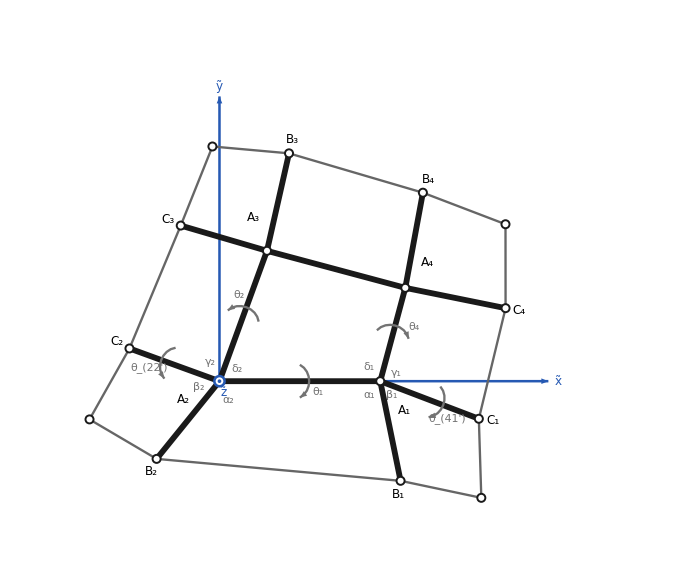
Given hypotheses and definitions:
A 3 x 3 net with, for each i = 1, 2,
the vertices A_i, B_i, C_i, and the vertices A_3, A_4 of the central face
the flat angles α_i, β_i, γ_i, δ_i ∈ (0, π) at A_i
the edge lengths ℓ_1 = |A_1 A_2|,   ℓ_2 = |A_2 A_3|,   ℓ_4 = |A_4 A_1|,   m_i = |A_i B_i|,   v_i = |A_i C_i|
the dihedral angles θ_1, θ_2, θ_4 ∈ [-π, π) \ {0} along the edges A_1 A_2, A_2 A_3, A_4 A_1

σ_i = 1/2 (α_i+β_i+γ_i+δ_i) | (ᾱ)_i = σ_i-α_i | (β̄)_i = σ_i-β_i | (γ̄)_i = σ_i-γ_i | (δ̄)_i = σ_i-δ_i
a_i = (sin α_i)/(sin (ᾱ)_i) | b_i = (sin β_i)/(sin (β̄)_i) | c_i = (sin γ_i)/(sin (γ̄)_i) | d_i = (sin δ_i)/(sin (δ̄)_i) | ε_i = sign(sin σ_i)
M_i = a_i b_i c_i d_i | r_i = a_i d_i | s_i = c_i d_i | f_i = a_i c_i | 
u_i = 1 - M_i | x_i = 1/(r_i - 1) | y_i = 1/(s_i - 1) | z_i = 1/(f_i - 1) | 

α_i ± β_i ± γ_i ± δ_i ≠ 0 (mod 2π)
(ᾱ)_i, (β̄)_i, (γ̄)_i, (δ̄)_i ∈ (0, π)
ε_i ∈ {-1, 1}
r_i, s_i, f_i, M_i ≠ 0, 1;   M_i, f_i > 0
x_i, y_i, z_i ≠ -1, 0;   u_i x_i y_i z_i > 0
x_i(1 + x_i) > 0,   z_i(1 + z_i) > 0
1 + u_i x_i > 0,   1 + u_i z_i > 0

Normals:
(n⃗)_0 = (A_2 A_1)^⟶ × (A_2 A_3)^⟶
(n⃗)_1 = (A_2 A_1)^⟶ × (A_2 B_2)^⟶ | (n⃗)_2 = (A_2 C_2)^⟶ × (A_2 A_3)^⟶ | (n⃗)_4 = (A_1 A_4)^⟶ × (A_1 C_1)^⟶
(n⃗)_(1') = (A_1 B_1)^⟶ × (A_1 C_1)^⟶ | (n⃗)_(2') = (A_2 C_2)^⟶ × (A_2 B_2)^⟶

Dihedral angles:
θ((w⃗)_1, (w⃗)_2, (w⃗)_3) ∶= {∠((w⃗)_1, (w⃗)_2) ∈ (0, π), | if det((w⃗)_1, (w⃗)_2, (w⃗)_3) > 0,
-∠((w⃗)_1, (w⃗)_2) ∈ [-π, 0], | if det((w⃗)_1, (w⃗)_2, (w⃗)_3) ≤ 0.
central dihedral angles:
θ_1 = θ((n⃗)_0, (n⃗)_1, (A_2 A_1)^⟶) | θ_2 = θ((n⃗)_0, (n⃗)_2, (A_3 A_2)^⟶) | θ_4 = θ((n⃗)_0, (n⃗)_4, (A_1 A_4)^⟶)

corner dihedral angles:
θ_(41') = θ((n⃗)_4, (n⃗)_(1'), (A_1 C_1)^⟶) | θ_(22') = θ((n⃗)_2, (n⃗)_(2'), (C_2 A_2)^⟶)

Cartesian coordinates:
origin at A_2
central face in the half-plane ỹ ≥ 0 of the x̃ỹ-plane, the ray A_2 A_1 as the x̃-axis
-Graphics-
Figure 1

A_1 = {ℓ_1,0,0}
A_2 = {0,0,0}
A_3 = {ℓ_2 cos δ_2,ℓ_2 sin δ_2,0}
A_4 = {ℓ_1-ℓ_4 cos δ_1,ℓ_4 sin δ_1,0}
B_1 = A_1 + m_1 {-cos α_1,sin α_1 cos θ_1,sin α_1 sin θ_1}
B_2 = A_2 + m_2 {cos α_2,sin α_2 cos θ_1,sin α_2 sin θ_1}
C_1 = A_1 + v_1 {-sin γ_1 sin δ_1 cos θ_4-cos γ_1 cos δ_1,cos γ_1 sin δ_1-sin γ_1 cos δ_1 cos θ_4,sin γ_1 sin θ_4}
C_2 = A_2 + v_2 {sin γ_2 sin δ_2 cos θ_2+cos γ_2 cos δ_2,cos γ_2 sin δ_2-sin γ_2 cos δ_2 cos θ_2,sin γ_2 sin θ_2}
The definition gives θ((w⃗)_1, (w⃗)_2, (w⃗)_3) = ±∠((w⃗)_1, (w⃗)_2), by the sign of the determinant. The cosine is even and the sine is odd, so cos θ = ((w⃗)_1 · (w⃗)_2)/(|(w⃗)_1| |(w⃗)_2|) and sin θ = (det((w⃗)_1, (w⃗)_2, (w⃗)_3))/(|(w⃗)_1| |(w⃗)_2| |(w⃗)_3|) hold whichever sign the determinant has; the formula for the sine holds because (w⃗)_3, the direction of an edge common to the two faces, is orthogonal to (w⃗)_1 and (w⃗)_2, so that (w⃗)_1 × (w⃗)_2 is a multiple of (w⃗)_3. No formula of the notebook distinguishes the two cases, the coordinates above included.

Flexion:
x_2 = x_1,   u_1 = u_2 = u
e_1, e_2, e_0 ∈ {-1, 1}
D(X, t) = (X t^2 - 1)(1 - u X t^2),      I(X) = {t ∈ ℝ : X D(X, t) > 0},      for X, t ∈ ℝ

cot(θ_4/2) = (ε_1(cot(θ_1/2) √(u x_1 y_1(1 + z_1)(1 + u z_1)) - e_0 e_1 √(u y_1 z_1 D(x_1, cot(θ_1/2)))))/(y_1 u(z_1 + x_1 cot^2(θ_1/2)))
cot(θ_2/2) = (ε_2(cot(θ_1/2) √(u x_1 y_2(1 + z_2)(1 + u z_2)) + e_0 e_2 √(u y_2 z_2 D(x_1, cot(θ_1/2)))))/(y_2 u(z_2 + x_1 cot^2(θ_1/2)))

Each ☑ below certifies that the statement displayed beside it has been verified by a symbolic computation at that point; a × would mean that this verification failed. A • marks a given fact, a definition, a result of an earlier block, or an inference stated in words beside it.

We want to test the following claims ★ :

Claim 1.
◼ (1 - cos θ_(41'))(1 + u_1 x_1)(x_1 cot^2(θ_1/2) - 1) = (1 + cos θ_(41'))(1 + x_1)(1 - u_1 x_1 cot^2(θ_1/2))
◼ (1 - cos θ_(22'))(1 + u_2 x_2)(x_2 cot^2(θ_1/2) - 1) = (1 + cos θ_(22'))(1 + x_2)(1 - u_2 x_2 cot^2(θ_1/2))

In particular,
◼ θ_(41') ≠ 0, ±π   if   (x_1 cot^2(θ_1/2) - 1)(1 - u_1 x_1 cot^2(θ_1/2)) ≠ 0
◼ θ_(22') ≠ 0, ±π   if   (x_2 cot^2(θ_1/2) - 1)(1 - u_2 x_2 cot^2(θ_1/2)) ≠ 0

Claim 2.
If x_2 = x_1,   u_1 = u_2 = u, and cot(θ_1/2) ∈ I(x_1), then

◼ e_1 cot(θ_(41')/2) = -e_2 cot(θ_(22')/2) = e_0 √(((1 + u x_1)(x_1 cot^2(θ_1/2) - 1))/((1 + x_1)(1 - u x_1 cot^2(θ_1/2))))

the coordinatesVerified
Verification: the lengths and the flat angles at A_1, A_2 from dot products, and the side of B_1 from two cross products; with θ_1, θ_2, θ_4 from the next block, these data fix every point.
(1) | (A_2 A_1)^⟶ = {ℓ_1,0,0} | • | from the coordinates
(2) | (A_2 A_3)^⟶ = {ℓ_2 cos δ_2,ℓ_2 sin δ_2,0} | • | from the coordinates
(3) | (A_1 A_2)^⟶ = {-ℓ_1,0,0} | • | from the coordinates
(4) | (A_1 A_4)^⟶ = {ℓ_4 (-cos δ_1),ℓ_4 sin δ_1,0} | • | from the coordinates
(5) | (A_1 B_1)^⟶ = {m_1 (-cos α_1),m_1 sin α_1 cos θ_1,m_1 sin α_1 sin θ_1} | • | from the coordinates
(6) | (A_2 B_2)^⟶ = {m_2 cos α_2,m_2 sin α_2 cos θ_1,m_2 sin α_2 sin θ_1} | • | from the coordinates
(7) | (A_1 C_1)^⟶ = {v_1 (-sin γ_1 sin δ_1 cos θ_4-cos γ_1 cos δ_1),v_1 (cos γ_1 sin δ_1-sin γ_1 cos δ_1 cos θ_4),v_1 sin γ_1 sin θ_4} | • | from the coordinates
(8) | (A_2 C_2)^⟶ = {v_2 (sin γ_2 sin δ_2 cos θ_2+cos γ_2 cos δ_2),v_2 (cos γ_2 sin δ_2-sin γ_2 cos δ_2 cos θ_2),v_2 sin γ_2 sin θ_2} | • | from the coordinates
 |  |  | 
(9) | |(A_2 A_3)^⟶| = ℓ_2,   |(A_1 A_4)^⟶| = ℓ_4 | ☑ | the lengths of (2) and (4)
(10) | |(A_1 B_1)^⟶| = m_1,   |(A_2 B_2)^⟶| = m_2 | ☑ | the lengths of (5) and (6)
(11) | |(A_1 C_1)^⟶| = v_1,   |(A_2 C_2)^⟶| = v_2 | ☑ | the lengths of (7) and (8)
 |  |  | 
(12) | cos δ_1 = ((A_1 A_4)^⟶ · (A_1 A_2)^⟶)/(ℓ_4 ℓ_1),   cos δ_2 = ((A_2 A_1)^⟶ · (A_2 A_3)^⟶)/(ℓ_1 ℓ_2) | ☑ | from (1)–(4) and (9); flat angles in (0, π) are fixed by their cosines
(13) | cos α_1 = ((A_1 A_2)^⟶ · (A_1 B_1)^⟶)/(ℓ_1 m_1),   cos α_2 = ((A_2 A_1)^⟶ · (A_2 B_2)^⟶)/(ℓ_1 m_2) | ☑ | from (1), (3), (5), (6), and (10)
(14) | cos γ_1 = ((A_1 A_4)^⟶ · (A_1 C_1)^⟶)/(ℓ_4 v_1),   cos γ_2 = ((A_2 A_3)^⟶ · (A_2 C_2)^⟶)/(ℓ_2 v_2) | ☑ | from (2), (4), (7), (8), (9), and (11)
 |  |  | 
(15) | the ỹ-coordinates of A_3, A_4 are ℓ_2 sin δ_2, ℓ_4 sin δ_1 > 0 | • | from (2) and (4), because δ_1, δ_2 ∈ (0, π)
 |  |  | 
(16) | (A_2 A_1)^⟶ × (A_2 B_2)^⟶ = m_2 ℓ_1 sin α_2 {0,-sin θ_1,cos θ_1} | ☑ | from (1) and (6)
(17) | (A_2 A_1)^⟶ × (A_1 B_1)^⟶ = m_1 ℓ_1 sin α_1 {0,-sin θ_1,cos θ_1} | ☑ | from (1) and (5); with (16), B_1 and B_2 lie on one side of A_1 A_2, because sin α_1, sin α_2 > 0
Together, these give the lengths and the flat angles α_i, γ_i, δ_i, i = 1, 2, of the coordinates, with B_1 on the side of A_1 A_2 where B_2 lies.

the normals (n⃗)_0, (n⃗)_1, (n⃗)_2, (n⃗)_4Verified
Verification: each normal is the cross product of two edge vectors of its own face; (11) and (12) identify the symbols θ_1, θ_2, θ_4 of the coordinates with the dihedral angles of the definition along A_1 A_2, A_2 A_3, A_4 A_1.
(1) | (A_2 A_1)^⟶ = {ℓ_1,0,0} | • | from the coordinates
(2) | (A_2 A_3)^⟶ = {ℓ_2 cos δ_2,ℓ_2 sin δ_2,0} | • | from the coordinates
(3) | (A_2 B_2)^⟶ = {m_2 cos α_2,m_2 sin α_2 cos θ_1,m_2 sin α_2 sin θ_1} | • | from the coordinates
(4) | (A_2 C_2)^⟶ = {v_2 (sin γ_2 sin δ_2 cos θ_2+cos γ_2 cos δ_2),v_2 (cos γ_2 sin δ_2-sin γ_2 cos δ_2 cos θ_2),v_2 sin γ_2 sin θ_2} | • | from the coordinates
(5) | (A_1 A_4)^⟶ = {ℓ_4 (-cos δ_1),ℓ_4 sin δ_1,0} | • | from the coordinates
(6) | (A_1 C_1)^⟶ = {v_1 (-sin γ_1 sin δ_1 cos θ_4-cos γ_1 cos δ_1),v_1 (cos γ_1 sin δ_1-sin γ_1 cos δ_1 cos θ_4),v_1 sin γ_1 sin θ_4} | • | from the coordinates
 |  |  | 
(7) | (n⃗)_0 = (A_2 A_1)^⟶ × (A_2 A_3)^⟶ = ℓ_1 ℓ_2 sin δ_2 {0,0,1},   |(n⃗)_0| = ℓ_1 ℓ_2 sin δ_2 | ☑ | from (1) and (2)
(8) | (n⃗)_1 = (A_2 A_1)^⟶ × (A_2 B_2)^⟶ = m_2 ℓ_1 sin α_2 {0,-sin θ_1,cos θ_1},   |(n⃗)_1| = m_2 ℓ_1 sin α_2 | ☑ | from (1) and (3)
(9) | (n⃗)_2 = (A_2 C_2)^⟶ × (A_2 A_3)^⟶ = v_2 ℓ_2 sin γ_2 {-sin δ_2 sin θ_2,cos δ_2 sin θ_2,cos θ_2},   |(n⃗)_2| = v_2 ℓ_2 sin γ_2 | ☑ | from (4) and (2)
(10) | (n⃗)_4 = (A_1 A_4)^⟶ × (A_1 C_1)^⟶ = v_1 ℓ_4 sin γ_1 {sin δ_1 sin θ_4,cos δ_1 sin θ_4,cos θ_4},   |(n⃗)_4| = v_1 ℓ_4 sin γ_1 | ☑ | from (5) and (6)
 |  |  | 
(11) | (n⃗)_0 · (n⃗)_i = |(n⃗)_0| |(n⃗)_i| cos θ_i | ☑ | for i = 1, 2, 4, from (7)–(10)
(12) | det((n⃗)_0, (n⃗)_i, (A_(i+1)A_i)^⟶) = |(n⃗)_0| |(n⃗)_i| ℓ_i sin θ_i | ☑ | for i = 1, 2, 4, from (7)–(10), with A_5 := A_1 and |(A_(i+1)A_i)^⟶| = ℓ_i
Together, these give the four normals and identify θ_1, θ_2, θ_4.

θ_(41'), along A_1 C_1Verified
Verification: the corner normal (n⃗)_(1') from its two edge vectors, then the cosine and the sine of the angle between (n⃗)_4 and (n⃗)_(1'). The closed forms are written with β_1, which the coordinates do not contain: (5) gives its cosine, and (6) the length of (n⃗)_(1'), which carries sin β_1.
(1) | (n⃗)_4 = v_1 ℓ_4 sin γ_1 {sin δ_1 sin θ_4,cos δ_1 sin θ_4,cos θ_4},   |(n⃗)_4| = v_1 ℓ_4 sin γ_1 | • | from the block on the normals
 |  |  | 
(2) | (A_1 B_1)^⟶ = {m_1 (-cos α_1),m_1 sin α_1 cos θ_1,m_1 sin α_1 sin θ_1} | • | from the coordinates
(3) | (A_1 C_1)^⟶ = {v_1 (-sin γ_1 sin δ_1 cos θ_4-cos γ_1 cos δ_1),v_1 (cos γ_1 sin δ_1-sin γ_1 cos δ_1 cos θ_4),v_1 sin γ_1 sin θ_4} | • | from the coordinates
(4) | (n⃗)_(1') = (A_1 B_1)^⟶ × (A_1 C_1)^⟶ = {m_1 v_1 (sin θ_1 (sin α_1 sin γ_1 cos δ_1 cos θ_4-sin α_1 cos γ_1 sin δ_1)+sin α_1 sin γ_1 sin θ_4 cos θ_1),m_1 v_1 (sin θ_1 (sin α_1 (-cos γ_1) cos δ_1-sin α_1 sin γ_1 sin δ_1 cos θ_4)+cos α_1 sin γ_1 sin θ_4),m_1 v_1 (cos α_1 sin γ_1 cos δ_1 cos θ_4+cos θ_1 (sin α_1 sin γ_1 sin δ_1 cos θ_4+sin α_1 cos γ_1 cos δ_1)-cos α_1 cos γ_1 sin δ_1)} | ☑ | from (2) and (3)
(5) | cos β_1 = ((A_1 B_1)^⟶ · (A_1 C_1)^⟶)/(m_1 v_1) = cos α_1 (sin γ_1 sin δ_1 cos θ_4+cos γ_1 cos δ_1)+sin α_1 (cos θ_1 (cos γ_1 sin δ_1-sin γ_1 cos δ_1 cos θ_4)+sin γ_1 sin θ_1 sin θ_4) | ☑ | from (2) and (3); the closed forms below are written with β_1
(6) | |(n⃗)_(1')| = m_1 v_1 sin β_1 | ☑ | from (4) and (5), with the positive root because β_1 ∈ (0, π)
 |  |  | 
(7) | cos θ_(41') = ((n⃗)_4 · (n⃗)_(1'))/(|(n⃗)_4| |(n⃗)_(1')|) | • | by the definition
(8) | cos θ_(41') = (sin α_1 sin δ_1 cos θ_1+cos α_1 cos δ_1-cos β_1 cos γ_1)/(sin β_1 sin γ_1) | ☑ | from (1) and (4)–(7)
 |  |  | 
(9) | (A_1 C_1)^⟶ = {v_1 (-sin γ_1 sin δ_1 cos θ_4-cos γ_1 cos δ_1),v_1 (cos γ_1 sin δ_1-sin γ_1 cos δ_1 cos θ_4),v_1 sin γ_1 sin θ_4} | • | the third vector of θ_(41')
(10) | sin θ_(41') = (det((n⃗)_4, (n⃗)_(1'), (A_1 C_1)^⟶))/(|(n⃗)_4| |(n⃗)_(1')| |(A_1 C_1)^⟶|) | • | by the definition
(11) | sin θ_(41') = (cos α_1 sin δ_1 sin θ_4-sin α_1 (cos δ_1 sin θ_4 cos θ_1+sin θ_1 cos θ_4))/(sin β_1) | ☑ | from (1), (4), (6), (9), and (10)
Together, these give the cosine and the sine of θ_(41').

θ_(22'), along A_2 C_2Verified
Verification: the corner normal (n⃗)_(2') from its two edge vectors, then the cosine and the sine of the angle between (n⃗)_2 and (n⃗)_(2'). The closed forms are written with β_2, which the coordinates do not contain: (5) gives its cosine, and (6) the length of (n⃗)_(2'), which carries sin β_2.
(1) | (n⃗)_2 = v_2 ℓ_2 sin γ_2 {-sin δ_2 sin θ_2,cos δ_2 sin θ_2,cos θ_2},   |(n⃗)_2| = v_2 ℓ_2 sin γ_2 | • | from the block on the normals
 |  |  | 
(2) | (A_2 C_2)^⟶ = {m_2 (sin γ_2 sin δ_2 cos θ_2+cos γ_2 cos δ_2),m_2 (cos γ_2 sin δ_2-sin γ_2 cos δ_2 cos θ_2),m_2 sin γ_2 sin θ_2} | • | from the coordinates
(3) | (A_2 B_2)^⟶ = {v_2 cos α_2,v_2 sin α_2 cos θ_1,v_2 sin α_2 sin θ_1} | • | from the coordinates
(4) | (n⃗)_(2') = (A_2 C_2)^⟶ × (A_2 B_2)^⟶ = {m_2 v_2 (sin θ_1 (sin α_2 cos γ_2 sin δ_2-sin α_2 sin γ_2 cos δ_2 cos θ_2)-sin α_2 sin γ_2 sin θ_2 cos θ_1),m_2 v_2 (sin θ_1 (sin α_2 (-cos γ_2) cos δ_2-sin α_2 sin γ_2 sin δ_2 cos θ_2)+cos α_2 sin γ_2 sin θ_2),m_2 v_2 (cos α_2 sin γ_2 cos δ_2 cos θ_2+cos θ_1 (sin α_2 sin γ_2 sin δ_2 cos θ_2+sin α_2 cos γ_2 cos δ_2)-cos α_2 cos γ_2 sin δ_2)} | ☑ | from (2) and (3)
(5) | cos β_2 = ((A_2 B_2)^⟶ · (A_2 C_2)^⟶)/(m_2 v_2) = cos α_2 (sin γ_2 sin δ_2 cos θ_2+cos γ_2 cos δ_2)+sin α_2 (cos θ_1 (cos γ_2 sin δ_2-sin γ_2 cos δ_2 cos θ_2)+sin γ_2 sin θ_1 sin θ_2) | ☑ | from (2) and (3); the closed forms below are written with β_2
(6) | |(n⃗)_(2')| = m_2 v_2 sin β_2 | ☑ | from (4) and (5), with the positive root because β_2 ∈ (0, π)
 |  |  | 
(7) | cos θ_(22') = ((n⃗)_2 · (n⃗)_(2'))/(|(n⃗)_2| |(n⃗)_(2')|) | • | by the definition
(8) | cos θ_(22') = (sin α_2 sin δ_2 cos θ_1+cos α_2 cos δ_2-cos β_2 cos γ_2)/(sin β_2 sin γ_2) | ☑ | from (1) and (4)–(7)
 |  |  | 
(9) | (C_2 A_2)^⟶ = {-(v_2 (sin γ_2 sin δ_2 cos θ_2+cos γ_2 cos δ_2)),-(v_2 (cos γ_2 sin δ_2-sin γ_2 cos δ_2 cos θ_2)),v_2 (-sin γ_2) sin θ_2} | • | the third vector of θ_(22')
(10) | sin θ_(22') = (det((n⃗)_2, (n⃗)_(2'), (C_2 A_2)^⟶))/(|(n⃗)_2| |(n⃗)_(2')| |(C_2 A_2)^⟶|) | • | by the definition
(11) | sin θ_(22') = (cos α_2 sin δ_2 sin θ_2-sin α_2 (cos δ_2 sin θ_2 cos θ_1+sin θ_1 cos θ_2))/(sin β_2) | ☑ | from (1), (4), (6), (9), and (10)
Together, these give the cosine and the sine of θ_(22').

Claim 1: the cleared identitiesVerified
Verification: at each vertex, the coefficients as products of sines and the three ratios as identities in the flat angles, the cleared identity as a trigonometric identity, and the step to the identity of the claim with the displayed quantities as symbols; (1.7) and (2.7) read off that the corner angles are neither 0 nor ±π.
Part 1.  At A_1, the angle θ_(41'): |  |  | 
 | cf_1 := 1/2 (cos(β_1-γ_1)-cos(α_1-δ_1)),   cf_2 := 1/2 (cos(β_1-γ_1)-cos(α_1+δ_1)),   cf_3 := 1/2 (cos(β_1+γ_1)-cos(α_1-δ_1)),   cf_4 := 1/2 (cos(β_1+γ_1)-cos(α_1+δ_1)) | • | definitions
(1.1) | cf_1 = -sin(β_1-(ᾱ)_1) sin(β_1-(δ̄)_1),   cf_2 = sin (β̄)_1 sin (γ̄)_1,
cf_3 = -sin (ᾱ)_1 sin (δ̄)_1,   cf_4 = -sin σ_1 sin(β_1-(γ̄)_1) | ☑ | identities in the flat angles at A_1
(1.2) | cf_1, cf_2, cf_3, cf_4 ≠ 0 | • | each factor in (1.1) is the sine of half of a sum ±α_1 ± β_1 ± γ_1 ± δ_1 ≠ 0 (mod 2π)
(1.3) | (1 - cos θ_(41'))(cf_3 cot^2(θ_1/2) + cf_4) + (1 + cos θ_(41'))(cf_1 cot^2(θ_1/2) + cf_2) = 0 | ☑ | cos θ_(41') from its block and cot^2(θ_1/2) = (1 + cos θ_1)/(1 - cos θ_1), cleared
(1.4) | cf_3/cf_4 = -x_1,   cf_2/cf_4 = (1 + x_1)/(1 + u_1 x_1),   cf_1/cf_4 = -(u_1 x_1(1 + x_1))/(1 + u_1 x_1) | ☑ | identities in the flat angles at A_1
(1.5) | (1 - cos θ_(41'))(1 + u_1 x_1)(x_1 cot^2(θ_1/2) - 1) = (1 + cos θ_(41'))(1 + x_1)(1 - u_1 x_1 cot^2(θ_1/2)) | ☑ | (1.3) divided by cf_4, see (1.2), with (1.4), multiplied by 1 + u_1 x_1
(1.6) | 1 + x_1 ≠ 0,   1 + u_1 x_1 > 0 | • | given
(1.7) | if (x_1 cot^2(θ_1/2) - 1)(1 - u_1 x_1 cot^2(θ_1/2)) ≠ 0, then θ_(41') ≠ 0, ±π | • | by (1.5), cos θ_(41') = 1 would give (1 + x_1)(1 - u_1 x_1 cot^2(θ_1/2)) = 0, and cos θ_(41') = -1 would give (1 + u_1 x_1)(x_1 cot^2(θ_1/2) - 1) = 0; both contradict the hypothesis, by (1.6)
 |  |  | 
Part 2.  At A_2, the angle θ_(22'): |  |  | 
 | cf_1 := 1/2 (cos(β_2-γ_2)-cos(α_2-δ_2)),   cf_2 := 1/2 (cos(β_2-γ_2)-cos(α_2+δ_2)),   cf_3 := 1/2 (cos(β_2+γ_2)-cos(α_2-δ_2)),   cf_4 := 1/2 (cos(β_2+γ_2)-cos(α_2+δ_2)) | • | definitions
(2.1) | cf_1 = -sin(β_2-(ᾱ)_2) sin(β_2-(δ̄)_2),   cf_2 = sin (β̄)_2 sin (γ̄)_2,
cf_3 = -sin (ᾱ)_2 sin (δ̄)_2,   cf_4 = -sin σ_2 sin(β_2-(γ̄)_2) | ☑ | identities in the flat angles at A_2
(2.2) | cf_1, cf_2, cf_3, cf_4 ≠ 0 | • | each factor in (2.1) is the sine of half of a sum ±α_2 ± β_2 ± γ_2 ± δ_2 ≠ 0 (mod 2π)
(2.3) | (1 - cos θ_(22'))(cf_3 cot^2(θ_1/2) + cf_4) + (1 + cos θ_(22'))(cf_1 cot^2(θ_1/2) + cf_2) = 0 | ☑ | cos θ_(22') from its block and cot^2(θ_1/2) = (1 + cos θ_1)/(1 - cos θ_1), cleared
(2.4) | cf_3/cf_4 = -x_2,   cf_2/cf_4 = (1 + x_2)/(1 + u_2 x_2),   cf_1/cf_4 = -(u_2 x_2(1 + x_2))/(1 + u_2 x_2) | ☑ | identities in the flat angles at A_2
(2.5) | (1 - cos θ_(22'))(1 + u_2 x_2)(x_2 cot^2(θ_1/2) - 1) = (1 + cos θ_(22'))(1 + x_2)(1 - u_2 x_2 cot^2(θ_1/2)) | ☑ | (2.3) divided by cf_4, see (2.2), with (2.4), multiplied by 1 + u_2 x_2
(2.6) | 1 + x_2 ≠ 0,   1 + u_2 x_2 > 0 | • | given
(2.7) | if (x_2 cot^2(θ_1/2) - 1)(1 - u_2 x_2 cot^2(θ_1/2)) ≠ 0, then θ_(22') ≠ 0, ±π | • | by (2.5), cos θ_(22') = 1 would give (1 + x_2)(1 - u_2 x_2 cot^2(θ_1/2)) = 0, and cos θ_(22') = -1 would give (1 + u_2 x_2)(x_2 cot^2(θ_1/2) - 1) = 0; both contradict the hypothesis, by (2.6)
 |  |  | 
Together, these give Claim 1.

Claim 2: the formula for the two corner anglesVerified
Verification: at each vertex, the sine and 1 - cos of the corner angle through the two half-angle cotangents give its half-cotangent as a quotient; Bricard's equation reduces the numerator to the radical of the parametrization by θ_1, which fixes the sign. Identities in the angles are checked as trigonometric identities, and each step between lines with the displayed quantities as symbols.
(1) | x_2 = x_1,   u_1 = u_2 = u | • | the flexion; the lines below are written with these values
(2) | cot(θ_1/2) ∈ I(x_1) | • | the admissible set
 |  |  | 
(3) | cot(x/2) = (sin x)/(1 - cos x),      sin x = (2 cot(x/2))/(1 + cot^2(x/2)),      cos x = (cot^2(x/2) - 1)/(cot^2(x/2) + 1) | ☑ | for x ≠ 0 (mod 2π)
 |  |  | 
Part 1.  At A_1, the angle θ_(41') through θ_1 and θ_4: |  |  | 
(1.1) | θ_(41') ≠ 0, ±π | • | Claim 1, because (1) and (2) give D(x_1, cot(θ_1/2)) ≠ 0
(1.2) | sin θ_(41') = (cos α_1 sin δ_1 sin θ_4-sin α_1 (cos δ_1 sin θ_4 cos θ_1+sin θ_1 cos θ_4))/(sin β_1),      cos θ_(41') = (sin α_1 sin δ_1 cos θ_1+cos α_1 cos δ_1-cos β_1 cos γ_1)/(sin β_1 sin γ_1) | • | from the block on θ_(41')
(1.3) | sin θ_(41') sin β_1 ((1 + cot^2(θ_4/2))(1 + cot^2(θ_1/2)))/2 = -sin(α_1-δ_1) cot(θ_4/2) cot^2(θ_1/2) - sin α_1 cot^2(θ_4/2) cot(θ_1/2) + sin(α_1+δ_1) cot(θ_4/2) + sin α_1 cot(θ_1/2) | ☑ | (1.2), with (3)
(1.4) | (1 - cos θ_(41')) sin γ_1 sin β_1 (1 + cot^2(θ_1/2))/2 = -sin(β_1-(ᾱ)_1) sin(β_1-(δ̄)_1) cot^2(θ_1/2) + sin (β̄)_1 sin (γ̄)_1 | ☑ | (1.2), with (3) and (1.1) of the block on Claim 1
 | Φ := -sin(α_1-δ_1) cot(θ_4/2) cot^2(θ_1/2) - sin α_1 cot^2(θ_4/2) cot(θ_1/2) + sin(α_1+δ_1) cot(θ_4/2) + sin α_1 cot(θ_1/2) | • | a name for the right side of (1.3)
 | Φ_2 := -sin(β_1-(ᾱ)_1) sin(β_1-(δ̄)_1) cot^2(θ_1/2) + sin (β̄)_1 sin (γ̄)_1 | • | a name for the right side of (1.4)
(1.5) | cot(θ_(41')/2) = (sin θ_(41'))/(1 - cos θ_(41')) = (sin γ_1 Φ)/((1 + cot^2(θ_4/2)) Φ_2) | ☑ | the quotient of (1.3) and (1.4), by (3); here Φ_2 ≠ 0 by (1.4), because θ_(41') ≠ 0 by (1.1)
 |  |  | 
(1.6) | x_1 = (sin (ᾱ)_1 sin (δ̄)_1)/(-sin σ_1 sin(β_1-(γ̄)_1)),      u x_1 = (sin(β_1-(ᾱ)_1) sin(β_1-(δ̄)_1))/(sin (β̄)_1 sin (γ̄)_1) | ☑ | identities in the flat angles at A_1
(1.7) | Φ_2 = sin (β̄)_1 sin (γ̄)_1 (1 - u x_1 cot^2(θ_1/2)) | ☑ | by (1.6)
 | Φ_1 := sin (ᾱ)_1 sin (δ̄)_1 cot^2(θ_1/2) + sin σ_1 sin(β_1-(γ̄)_1) | • | a name
(1.8) | Φ_1 = -sin σ_1 sin(β_1-(γ̄)_1) (x_1 cot^2(θ_1/2) - 1) | ☑ | by (1.6)
(1.9) | (-sin σ_1 sin(β_1-(γ̄)_1))/(sin (β̄)_1 sin (γ̄)_1) = (1 + u x_1)/(1 + x_1) | ☑ | an identity in the flat angles at A_1
(1.10) | cot^2(θ_(41')/2) = Φ_1/Φ_2 | ☑ | from (1.2), cleared, with (1.1) of the block on Claim 1
(1.11) | Φ_1 Φ_2 = -sin σ_1 sin(β_1-(γ̄)_1) sin (β̄)_1 sin (γ̄)_1 D(x_1, cot(θ_1/2)) | ☑ | (1.7) times (1.8)
 |  |  | 
(1.12) | sin (γ̄)_1 > 0,   sin (β̄)_1 > 0 | • | (γ̄)_1, (β̄)_1 ∈ (0, π)
(1.13) | if x_1 < 0:   x_1 cot^2(θ_1/2) - 1 < 0,   so x_1 D(x_1, cot(θ_1/2)) > 0 gives 1 - u x_1 cot^2(θ_1/2) > 0 | • | cot^2(θ_1/2) ≥ 0
(1.14) | if x_1 > 0 and 1 - u x_1 cot^2(θ_1/2) ≤ 0:   x_1 D(x_1, cot(θ_1/2)) > 0 gives x_1 cot^2(θ_1/2) < 1 ≤ u x_1 cot^2(θ_1/2),   so u ≥ 1 | • | against u = 1 - M_1,   M_1 > 0
(1.15) | Φ_2 > 0 | • | (1.7), (1.12)–(1.14), and (2)
 |  |  | 
(1.16) | (-sin (δ̄)_1 sin(β_1-(δ̄)_1) cot^2(θ_1/2) - sin (γ̄)_1 sin(β_1-(γ̄)_1)) cot^2(θ_4/2)
   - 2 sin α_1 sin γ_1 cot(θ_4/2) cot(θ_1/2)
   + (-sin (ᾱ)_1 sin(β_1-(ᾱ)_1) cot^2(θ_1/2) + sin σ_1 sin (β̄)_1) = 0 | ☑ | the closure (A_1 B_1)^⟶ · (A_1 C_1)^⟶ = m_1 v_1 cos β_1 (Bricard's equation), with (3)
(1.17) | sin (δ̄)_1 (-sin(β_1-(δ̄)_1)) - sin (ᾱ)_1 (-sin(β_1-(ᾱ)_1)) = sin γ_1 sin(α_1-δ_1) | ☑ | an identity in the flat angles at A_1
(1.18) | sin (γ̄)_1 (-sin(β_1-(γ̄)_1)) - sin σ_1 sin (β̄)_1 = -sin γ_1 sin(α_1+δ_1) | ☑ | the same
(1.19) | sin γ_1 Φ = cot(θ_4/2) (-sin γ_1 sin(α_1-δ_1) cot^2(θ_1/2) + sin γ_1 sin(α_1+δ_1)) + sin α_1 sin γ_1 cot(θ_1/2) (1 - cot^2(θ_4/2)) | ☑ | Φ expanded
(1.20) | sin γ_1 Φ = cot(θ_4/2) ((-sin (ᾱ)_1 sin(β_1-(ᾱ)_1) cot^2(θ_1/2) + sin σ_1 sin (β̄)_1) - (-sin (δ̄)_1 sin(β_1-(δ̄)_1) cot^2(θ_1/2) - sin (γ̄)_1 sin(β_1-(γ̄)_1))) + sin α_1 sin γ_1 cot(θ_1/2) (1 - cot^2(θ_4/2)) | ☑ | (1.19), with (1.17) and (1.18)
(1.21) | (-sin (ᾱ)_1 sin(β_1-(ᾱ)_1) cot^2(θ_1/2) + sin σ_1 sin (β̄)_1) cot(θ_4/2) = 2 sin α_1 sin γ_1 cot^2(θ_4/2) cot(θ_1/2) - (-sin (δ̄)_1 sin(β_1-(δ̄)_1) cot^2(θ_1/2) - sin (γ̄)_1 sin(β_1-(γ̄)_1)) cot^3(θ_4/2) | ☑ | (1.16) times cot(θ_4/2)
(1.22) | (sin γ_1 Φ)/(1 + cot^2(θ_4/2)) = cot(θ_1/2) sin α_1 sin γ_1 - cot(θ_4/2) (-sin (δ̄)_1 sin(β_1-(δ̄)_1) cot^2(θ_1/2) - sin (γ̄)_1 sin(β_1-(γ̄)_1)),
      that is   cot(θ_4/2) (-sin (δ̄)_1 sin(β_1-(δ̄)_1) cot^2(θ_1/2) - sin (γ̄)_1 sin(β_1-(γ̄)_1)) - cot(θ_1/2) sin α_1 sin γ_1 = -Φ_2 cot(θ_(41')/2) | ☑ | (1.20) and (1.21), divided by 1 + cot^2(θ_4/2); then (1.5)
 |  |  | 
(1.23) | cot(θ_4/2) = (ε_1(cot(θ_1/2) √(u x_1 y_1(1 + z_1)(1 + u z_1)) - e_0 e_1 √(u y_1 z_1 D(x_1, cot(θ_1/2)))))/(y_1 u(z_1 + x_1 cot^2(θ_1/2))) | • | the parametrization by θ_1
(1.24) | e_0 e_1 √(u y_1 z_1 D(x_1, cot(θ_1/2))) =
      -ε_1 cot(θ_4/2) y_1 u(z_1 + x_1 cot^2(θ_1/2)) + cot(θ_1/2) √(u x_1 y_1(1 + z_1)(1 + u z_1)) | ☑ | (1.23), solved for its radical
(1.25) | u y_1 z_1 = (sin (γ̄)_1 (-sin(β_1-(γ̄)_1)))/(sin σ_1 sin (β̄)_1) | ☑ | an identity in the flat angles at A_1
(1.26) | u x_1 y_1 = (sin (δ̄)_1 (-sin(β_1-(δ̄)_1)))/(sin σ_1 sin (β̄)_1) | ☑ | the same
(1.27) | u x_1 y_1(1 + z_1)(1 + u z_1) = (sin^2(α_1) sin^2(γ_1))/(sin^2(σ_1) sin^2((β̄)_1)) | ☑ | the same
(1.28) | sin σ_1 sin (β̄)_1 y_1 u(z_1 + x_1 cot^2(θ_1/2)) = -sin (δ̄)_1 sin(β_1-(δ̄)_1) cot^2(θ_1/2) - sin (γ̄)_1 sin(β_1-(γ̄)_1) | ☑ | (1.25) and (1.26)
(1.29) | sin σ_1 sin (β̄)_1 √(u x_1 y_1(1 + z_1)(1 + u z_1)) = ε_1 sin α_1 sin γ_1 | ☑ | (1.27), as squares; ε_1 = sign sin σ_1 and (β̄)_1 ∈ (0, π)
(1.30) | sin σ_1 sin (β̄)_1 √(u y_1 z_1 D(x_1, cot(θ_1/2))) = ε_1 √(Φ_1 Φ_2) | ☑ | (1.25) and (1.11), as squares; the signs as in (1.29)
(1.31) | -e_0 e_1 √(Φ_1 Φ_2) =
      cot(θ_4/2) (-sin (δ̄)_1 sin(β_1-(δ̄)_1) cot^2(θ_1/2) - sin (γ̄)_1 sin(β_1-(γ̄)_1)) - cot(θ_1/2) sin α_1 sin γ_1 = -Φ_2 cot(θ_(41')/2) | ☑ | (1.24) multiplied by sin σ_1 sin (β̄)_1 and divided by ε_1, with (1.28)–(1.30); then (1.22)
(1.32) | cot(θ_(41')/2) = e_0 e_1 √(Φ_1/Φ_2) = e_0 e_1 √(((1 + u x_1)(x_1 cot^2(θ_1/2) - 1))/((1 + x_1)(1 - u x_1 cot^2(θ_1/2)))) | ☑ | (1.31) divided by Φ_2 > 0, see (1.15); then (1.7)–(1.9)
 |  |  | 
Part 2.  At A_2, the angle θ_(22') through θ_1 and θ_2: |  |  | 
(2.1) | θ_(22') ≠ 0, ±π | • | Claim 1, because (1) and (2) give D(x_1, cot(θ_1/2)) ≠ 0
(2.2) | sin θ_(22') = (cos α_2 sin δ_2 sin θ_2-sin α_2 (cos δ_2 sin θ_2 cos θ_1+sin θ_1 cos θ_2))/(sin β_2),      cos θ_(22') = (sin α_2 sin δ_2 cos θ_1+cos α_2 cos δ_2-cos β_2 cos γ_2)/(sin β_2 sin γ_2) | • | from the block on θ_(22')
(2.3) | sin θ_(22') sin β_2 ((1 + cot^2(θ_2/2))(1 + cot^2(θ_1/2)))/2 = -sin(α_2-δ_2) cot(θ_2/2) cot^2(θ_1/2) - sin α_2 cot^2(θ_2/2) cot(θ_1/2) + sin(α_2+δ_2) cot(θ_2/2) + sin α_2 cot(θ_1/2) | ☑ | (2.2), with (3)
(2.4) | (1 - cos θ_(22')) sin γ_2 sin β_2 (1 + cot^2(θ_1/2))/2 = -sin(β_2-(ᾱ)_2) sin(β_2-(δ̄)_2) cot^2(θ_1/2) + sin (β̄)_2 sin (γ̄)_2 | ☑ | (2.2), with (3) and (2.1) of the block on Claim 1
 | Φ := -sin(α_2-δ_2) cot(θ_2/2) cot^2(θ_1/2) - sin α_2 cot^2(θ_2/2) cot(θ_1/2) + sin(α_2+δ_2) cot(θ_2/2) + sin α_2 cot(θ_1/2) | • | a name for the right side of (2.3)
 | Φ_2 := -sin(β_2-(ᾱ)_2) sin(β_2-(δ̄)_2) cot^2(θ_1/2) + sin (β̄)_2 sin (γ̄)_2 | • | a name for the right side of (2.4)
(2.5) | cot(θ_(22')/2) = (sin θ_(22'))/(1 - cos θ_(22')) = (sin γ_2 Φ)/((1 + cot^2(θ_2/2)) Φ_2) | ☑ | the quotient of (2.3) and (2.4), by (3); here Φ_2 ≠ 0 by (2.4), because θ_(22') ≠ 0 by (2.1)
 |  |  | 
(2.6) | x_1 = (sin (ᾱ)_2 sin (δ̄)_2)/(-sin σ_2 sin(β_2-(γ̄)_2)),      u x_1 = (sin(β_2-(ᾱ)_2) sin(β_2-(δ̄)_2))/(sin (β̄)_2 sin (γ̄)_2) | ☑ | identities in the flat angles at A_2
(2.7) | Φ_2 = sin (β̄)_2 sin (γ̄)_2 (1 - u x_1 cot^2(θ_1/2)) | ☑ | by (2.6)
 | Φ_1 := sin (ᾱ)_2 sin (δ̄)_2 cot^2(θ_1/2) + sin σ_2 sin(β_2-(γ̄)_2) | • | a name
(2.8) | Φ_1 = -sin σ_2 sin(β_2-(γ̄)_2) (x_1 cot^2(θ_1/2) - 1) | ☑ | by (2.6)
(2.9) | (-sin σ_2 sin(β_2-(γ̄)_2))/(sin (β̄)_2 sin (γ̄)_2) = (1 + u x_1)/(1 + x_1) | ☑ | an identity in the flat angles at A_2
(2.10) | cot^2(θ_(22')/2) = Φ_1/Φ_2 | ☑ | from (2.2), cleared, with (2.1) of the block on Claim 1
(2.11) | Φ_1 Φ_2 = -sin σ_2 sin(β_2-(γ̄)_2) sin (β̄)_2 sin (γ̄)_2 D(x_1, cot(θ_1/2)) | ☑ | (2.7) times (2.8)
 |  |  | 
(2.12) | sin (γ̄)_2 > 0,   sin (β̄)_2 > 0 | • | (γ̄)_2, (β̄)_2 ∈ (0, π)
(2.13) | if x_1 < 0:   x_1 cot^2(θ_1/2) - 1 < 0,   so x_1 D(x_1, cot(θ_1/2)) > 0 gives 1 - u x_1 cot^2(θ_1/2) > 0 | • | cot^2(θ_1/2) ≥ 0
(2.14) | if x_1 > 0 and 1 - u x_1 cot^2(θ_1/2) ≤ 0:   x_1 D(x_1, cot(θ_1/2)) > 0 gives x_1 cot^2(θ_1/2) < 1 ≤ u x_1 cot^2(θ_1/2),   so u ≥ 1 | • | against u = 1 - M_2,   M_2 > 0
(2.15) | Φ_2 > 0 | • | (2.7), (2.12)–(2.14), and (2)
 |  |  | 
(2.16) | (-sin (δ̄)_2 sin(β_2-(δ̄)_2) cot^2(θ_1/2) - sin (γ̄)_2 sin(β_2-(γ̄)_2)) cot^2(θ_2/2)
   - 2 sin α_2 sin γ_2 cot(θ_2/2) cot(θ_1/2)
   + (-sin (ᾱ)_2 sin(β_2-(ᾱ)_2) cot^2(θ_1/2) + sin σ_2 sin (β̄)_2) = 0 | ☑ | the closure (A_2 B_2)^⟶ · (A_2 C_2)^⟶ = m_2 v_2 cos β_2 (Bricard's equation), with (3)
(2.17) | sin (δ̄)_2 (-sin(β_2-(δ̄)_2)) - sin (ᾱ)_2 (-sin(β_2-(ᾱ)_2)) = sin γ_2 sin(α_2-δ_2) | ☑ | an identity in the flat angles at A_2
(2.18) | sin (γ̄)_2 (-sin(β_2-(γ̄)_2)) - sin σ_2 sin (β̄)_2 = -sin γ_2 sin(α_2+δ_2) | ☑ | the same
(2.19) | sin γ_2 Φ = cot(θ_2/2) (-sin γ_2 sin(α_2-δ_2) cot^2(θ_1/2) + sin γ_2 sin(α_2+δ_2)) + sin α_2 sin γ_2 cot(θ_1/2) (1 - cot^2(θ_2/2)) | ☑ | Φ expanded
(2.20) | sin γ_2 Φ = cot(θ_2/2) ((-sin (ᾱ)_2 sin(β_2-(ᾱ)_2) cot^2(θ_1/2) + sin σ_2 sin (β̄)_2) - (-sin (δ̄)_2 sin(β_2-(δ̄)_2) cot^2(θ_1/2) - sin (γ̄)_2 sin(β_2-(γ̄)_2))) + sin α_2 sin γ_2 cot(θ_1/2) (1 - cot^2(θ_2/2)) | ☑ | (2.19), with (2.17) and (2.18)
(2.21) | (-sin (ᾱ)_2 sin(β_2-(ᾱ)_2) cot^2(θ_1/2) + sin σ_2 sin (β̄)_2) cot(θ_2/2) = 2 sin α_2 sin γ_2 cot^2(θ_2/2) cot(θ_1/2) - (-sin (δ̄)_2 sin(β_2-(δ̄)_2) cot^2(θ_1/2) - sin (γ̄)_2 sin(β_2-(γ̄)_2)) cot^3(θ_2/2) | ☑ | (2.16) times cot(θ_2/2)
(2.22) | (sin γ_2 Φ)/(1 + cot^2(θ_2/2)) = cot(θ_1/2) sin α_2 sin γ_2 - cot(θ_2/2) (-sin (δ̄)_2 sin(β_2-(δ̄)_2) cot^2(θ_1/2) - sin (γ̄)_2 sin(β_2-(γ̄)_2)),
      that is   cot(θ_2/2) (-sin (δ̄)_2 sin(β_2-(δ̄)_2) cot^2(θ_1/2) - sin (γ̄)_2 sin(β_2-(γ̄)_2)) - cot(θ_1/2) sin α_2 sin γ_2 = -Φ_2 cot(θ_(22')/2) | ☑ | (2.20) and (2.21), divided by 1 + cot^2(θ_2/2); then (2.5)
 |  |  | 
(2.23) | cot(θ_2/2) = (ε_2(cot(θ_1/2) √(u x_1 y_2(1 + z_2)(1 + u z_2)) + e_0 e_2 √(u y_2 z_2 D(x_1, cot(θ_1/2)))))/(y_2 u(z_2 + x_1 cot^2(θ_1/2))) | • | the parametrization by θ_1
(2.24) | e_0 e_2 √(u y_2 z_2 D(x_1, cot(θ_1/2))) =
      ε_2 cot(θ_2/2) y_2 u(z_2 + x_1 cot^2(θ_1/2)) - cot(θ_1/2) √(u x_1 y_2(1 + z_2)(1 + u z_2)) | ☑ | (2.23), solved for its radical
(2.25) | u y_2 z_2 = (sin (γ̄)_2 (-sin(β_2-(γ̄)_2)))/(sin σ_2 sin (β̄)_2) | ☑ | an identity in the flat angles at A_2
(2.26) | u x_1 y_2 = (sin (δ̄)_2 (-sin(β_2-(δ̄)_2)))/(sin σ_2 sin (β̄)_2) | ☑ | the same
(2.27) | u x_1 y_2(1 + z_2)(1 + u z_2) = (sin^2(α_2) sin^2(γ_2))/(sin^2(σ_2) sin^2((β̄)_2)) | ☑ | the same
(2.28) | sin σ_2 sin (β̄)_2 y_2 u(z_2 + x_1 cot^2(θ_1/2)) = -sin (δ̄)_2 sin(β_2-(δ̄)_2) cot^2(θ_1/2) - sin (γ̄)_2 sin(β_2-(γ̄)_2) | ☑ | (2.25) and (2.26)
(2.29) | sin σ_2 sin (β̄)_2 √(u x_1 y_2(1 + z_2)(1 + u z_2)) = ε_2 sin α_2 sin γ_2 | ☑ | (2.27), as squares; ε_2 = sign sin σ_2 and (β̄)_2 ∈ (0, π)
(2.30) | sin σ_2 sin (β̄)_2 √(u y_2 z_2 D(x_1, cot(θ_1/2))) = ε_2 √(Φ_1 Φ_2) | ☑ | (2.25) and (2.11), as squares; the signs as in (2.29)
(2.31) | e_0 e_2 √(Φ_1 Φ_2) =
      cot(θ_2/2) (-sin (δ̄)_2 sin(β_2-(δ̄)_2) cot^2(θ_1/2) - sin (γ̄)_2 sin(β_2-(γ̄)_2)) - cot(θ_1/2) sin α_2 sin γ_2 = -Φ_2 cot(θ_(22')/2) | ☑ | (2.24) multiplied by sin σ_2 sin (β̄)_2 and divided by ε_2, with (2.28)–(2.30); then (2.22)
(2.32) | cot(θ_(22')/2) = -e_0 e_2 √(Φ_1/Φ_2) = -e_0 e_2 √(((1 + u x_1)(x_1 cot^2(θ_1/2) - 1))/((1 + x_1)(1 - u x_1 cot^2(θ_1/2)))) | ☑ | (2.31) divided by Φ_2 > 0, see (2.15); then (2.7)–(2.9)
 |  |  | 
(4) | ((1 + u_1 x_1)(x_1 cot^2(θ_1/2) - 1))/((1 + x_1)(1 - u_1 x_1 cot^2(θ_1/2))) = ((1 + u_2 x_2)(x_2 cot^2(θ_1/2) - 1))/((1 + x_2)(1 - u_2 x_2 cot^2(θ_1/2))) = ((1 + u x_1)(x_1 cot^2(θ_1/2) - 1))/((1 + x_1)(1 - u x_1 cot^2(θ_1/2))) | ☑ | the radicands of (1.32) and (2.32), under (1)
(5) | e_1 cot(θ_(41')/2) = -e_2 cot(θ_(22')/2) = e_0 √(((1 + u x_1)(x_1 cot^2(θ_1/2) - 1))/((1 + x_1)(1 - u x_1 cot^2(θ_1/2)))) | ☑ | (1.32) and (2.32), with (4)
Together, these give Claim 2.

ALL CLAIMS VERIFIED

```mathematica
(* ============================================================*)(*PART 1:SETUP*)(* ============================================================*)ClearAll[statusChip,smallChip,givenChip,colTest,cols,bullet,ind,vlift,idxB,prmB,tagB,ptB,pt,edg,evec,nv,nvP,uv,wv,tld,gk,thI,thP,cfS,cotTag,cotSqTag,dTag,mulR,bx,frac,absR,caseDef,firstBase,vrow,nrow,prow,hrow,vgrid,vgap,note,iv,dispRule,trigNames,simpleBoxQ,trigBoxRule,disp,sgnBox,polyRow,ratForm,iSet,uPlain,capX,tSym,Apt,Bpt,Cpt,uB,uC,wB,wC,wBout,wCout,wCent,wCentLen,eNext,ePrev,nraw,nrawP,nlen,nlenP,ndir,nPshow,nPfirst,nPsec,nPname,nvecIdx,nextA,prevA,thNextIdx,thPrevIdx,nIdx,pIdx,xRp,yRp,qXr,qYr,e0Tag,sigTag,radTag,flxF,bLen,cLen,ll1,ll2,ll3,ll4,mm1,mm2,mm3,mm4,vv1,vv2,vv3,vv4,lens,tw,hh,weier,halfRule,zeroT,zeroF,angA,angB,angG,angD,thNext,thPrev,thCent,sgnV,betaForm,vclose,outBnum,outBden,outCnum,outCden,outB,outC,eqB,eqC,sinBform,sinCform,sgD,bAD,bBD,bGD,bDD,barRule,sig,barA,barB,barG,barD,ratA,ratB,ratG,ratD,prodM,prodR,prodS,prodF,quU,quX,quY,quZ,biqBar,biqC,qBarD,nameB,nameC,spec,figBlock,cqList,resultsAll];
statusChip[True]:=Framed[Style["Verified",Bold,White,13],Background->RGBColor[0.13,0.55,0.13],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
statusChip[False]:=Framed[Style["Failed",Bold,White,13],Background->RGBColor[0.82,0.10,0.10],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
smallChip[True]:=Style["☑",14,RGBColor[0.13,0.55,0.13]];
smallChip[False]:=Style["×",14,Bold,RGBColor[0.82,0.10,0.10]];
givenChip=Style["•",12,GrayLevel[0.45]];
colTest=RGBColor[0.10,0.35,0.75];
cols={RGBColor[0.10,0.35,0.75],RGBColor[0.50,0.20,0.65],RGBColor[0.00,0.55,0.55],RGBColor[0.20,0.50,0.20],RGBColor[0.75,0.35,0.05],RGBColor[0.70,0.15,0.40],RGBColor[0.30,0.25,0.70],RGBColor[0.45,0.35,0.15],RGBColor[0.35,0.35,0.35]};
bullet=Style["◼ ",12,colTest];ind="    ";vlift=0.16;
idxB[x_]:=If[IntegerQ[x],ToString[x],StyleBox[ToString[x],FontSlant->"Italic"]];
prmB[x_]:=SuperscriptBox[idxB[x],"′"];
tagB[x_,y_]:=If[IntegerQ[x]&&IntegerQ[y],ToString[x]<>ToString[y],StyleBox[ToString[x]<>ToString[y],FontSlant->"Italic"]];
ptB[s_,i_]:=SubscriptBox[StyleBox[s,FontSlant->"Italic"],idxB[i]];pt[s_,i_]:=DisplayForm[ptB[s,i]];
edg[s1_,i1_,s2_,i2_]:=DisplayForm[RowBox[{ptB[s1,i1],ptB[s2,i2]}]];
evec[s1_,i1_,s2_,i2_]:=DisplayForm[OverscriptBox[RowBox[{ptB[s1,i1],ptB[s2,i2]}],AdjustmentBox["⟶",BoxBaselineShift->-vlift]]];
nv[x_]:=DisplayForm[SubscriptBox[OverscriptBox[StyleBox["n",FontSlant->"Italic"],AdjustmentBox["→",BoxBaselineShift->-vlift]],idxB[x]]];
nvP[x_]:=DisplayForm[SubscriptBox[OverscriptBox[StyleBox["n",FontSlant->"Italic"],AdjustmentBox["→",BoxBaselineShift->-vlift]],prmB[x]]];
uv[s_]:=DisplayForm[OverscriptBox[StyleBox[s,FontSlant->"Italic"],AdjustmentBox["→",BoxBaselineShift->-vlift]]];
wv[x_]:=DisplayForm[SubscriptBox[OverscriptBox[StyleBox["w",FontSlant->"Italic"],AdjustmentBox["→",BoxBaselineShift->-vlift]],idxB[x]]];
tld[s_]:=DisplayForm[OverscriptBox[StyleBox[s,FontSlant->"Italic"],"~"]];
gk[g_,i_]:=DisplayForm[SubscriptBox[g,idxB[i]]];
thI[x_]:=DisplayForm[SubscriptBox["θ",idxB[x]]];
thP[x_,y_]:=DisplayForm[SubscriptBox["θ",SuperscriptBox[tagB[x,y],"′"]]];
cfS[k_]:=DisplayForm[SubscriptBox[StyleBox["cf",FontSlant->"Italic"],ToString[k]]];
bx[DisplayForm[b_]]:=b;bx[x_]:=ToBoxes[x,TraditionalForm];
cotSqTag[t_]:=DisplayForm[RowBox[{SuperscriptBox["cot","2"],"(",bx[t],"/","2",")"}]];
cotTag[t_]:=DisplayForm[RowBox[{"cot","(",bx[t],"/","2",")"}]];
dTag[q_,s_]:=Row[{DisplayForm[StyleBox["D",FontSlant->"Italic"]],"(",q,", ",s,")"}];
mulR[args___]:=Row[Riffle[{args}," "]];absR[e_]:=Row[{"|",e,"|"}];
uPlain=DisplayForm[StyleBox["u",FontSlant->"Italic"]];capX=DisplayForm[StyleBox["X",FontSlant->"Italic"]];tSym=DisplayForm[StyleBox["t",FontSlant->"Italic"]];
frac[num_,den_]:=DisplayForm[FractionBox[bx[num],bx[den]]];
caseDef[lhs_,rows_]:=DisplayForm[RowBox[{bx[lhs]," ∶= ",StyleBox["{",SpanMaxSize->Infinity],GridBox[Map[bx,rows,{2}],ColumnAlignments->Left,ColumnSpacings->1.6,RowSpacings->0.9]}]];
note[s_]:=Style[s,12,GrayLevel[0.5]];
firstBase[e_]:=If[Head[e]===Column,Append[e,BaselinePosition->{1,1}],e];
(*a numbered line,an unnumbered line (for a name),and a heading line of a block*)
nrow[n_,stmt_,mark_,nt_]:={Style["("<>ToString[n]<>")",13],Style[firstBase[stmt],13],mark,note[nt]};
prow[stmt_,mark_,nt_]:={"",Style[firstBase[stmt],13],mark,note[nt]};
hrow[t_]:={Style[t,13],SpanFromLeft,SpanFromLeft,SpanFromLeft};
vrow[stmt_,mark_,nt_]:={Spacer[10],Style[firstBase[stmt],13],mark,note[nt]};
vgap={"",Spacer[{0,7}],"",""};
vgrid[rows_]:=Grid[rows,Alignment->{Left,Baseline},Spacings->{1.2,0.8}];
(*every symbol that is only displayed is a string,so that no value given to a symbol elsewhere in the notebook can enter the display;the displayed index i is an italic string as well*)
iv=Style["i",Italic];
dispRule=Join[Thread[{α1,α2,α3,α4}->Table[Subscript["α",k],{k,4}]],Thread[{β1,β2,β3,β4}->Table[Subscript["β",k],{k,4}]],Thread[{γ1,γ2,γ3,γ4}->Table[Subscript["γ",k],{k,4}]],Thread[{δ1,δ2,δ3,δ4}->Table[Subscript["δ",k],{k,4}]],Thread[{θ1,θ2,θ3,θ4}->Table[Subscript["θ",k],{k,4}]],Thread[{ll1,ll2,ll3,ll4}->Table[Subscript[Style["ℓ",Italic],k],{k,4}]],Thread[{mm1,mm2,mm3,mm4}->Table[Subscript[Style["m",Italic],k],{k,4}]],Thread[{vv1,vv2,vv3,vv4}->Table[Subscript[Style["v",Italic],k],{k,4}]]];
trigNames={"sin","cos","tan","cot","sec","csc"};
simpleBoxQ[b_String]:=True;simpleBoxQ[StyleBox[b_,___]]:=simpleBoxQ[b];
simpleBoxQ[(SubscriptBox|SuperscriptBox|OverscriptBox|UnderscriptBox)[bs__]]:=AllTrue[{bs},simpleBoxQ];simpleBoxQ[_]:=False;
trigBoxRule={RowBox[{f_String/;MemberQ[trigNames,f],"(",a_,")"}]/;simpleBoxQ[a]:>RowBox[{f," ",a}],RowBox[{f_String/;MemberQ[trigNames,f],RowBox[{"(",a_,")"}]}]/;simpleBoxQ[a]:>RowBox[{f," ",a}]};
disp[e_]:=DisplayForm[ToBoxes[e/. dispRule,TraditionalForm]//.trigBoxRule];
sgnBox[e_]:=Module[{f=e/. dispRule,s=1},If[Head[f]===Times&&NumericQ[First[f]]&&TrueQ[First[f]<0],s=-1;f=-f];{s,DisplayForm[ToBoxes[f,TraditionalForm]//.trigBoxRule]}];
polyRow[terms_]:=Module[{res={},sg,mg,tl},Do[{sg,mg}=sgnBox[terms[[k,1]]];tl=terms[[k,2]];If[k==1,If[sg<0,AppendTo[res,"-"]],AppendTo[res,If[sg<0," - "," + "]]];AppendTo[res,mg];If[tl=!=None,AppendTo[res," "];AppendTo[res,tl]],{k,Length[terms]}];Row[res]];
ratForm[qd_,ud_,opTag_]:=frac[Row[{"(1 + ",mulR[ud,qd],")(",mulR[qd,cotSqTag[opTag]]," - 1)"}],Row[{"(1 + ",qd,")(1 - ",mulR[ud,qd,cotSqTag[opTag]],")"}]];
iSet[q_]:=DisplayForm[RowBox[{StyleBox["I",FontSlant->"Italic"],"(",bx[q],")"}]];
(*the rule lens carries the two lengths that close the central face and is used for the figure alone,never in a verification.A trigonometric identity is decided without Simplify:every argument is broken into single symbols by TrigExpand,each sine and cosine is replaced by its rational form in the tangent of the half of its own symbol,and the numerator is expanded and compared with zero;zeroF halves the four flat angles first,so that the half sums of the quantities of the vertices become integer combinations*)
lens={ll4->(ll2 Sin[δ3]-ll1 Sin[δ2+δ3])/Sin[δ4],ll3->(ll1 Sin[δ1]-ll2 Sin[δ1+δ2])/Sin[δ4]};
weier[e0_]:=Module[{e=TrigExpand[e0],vs},vs=Union[Cases[e,(Sin|Cos)[x_]:>x,Infinity]];e=e/. Flatten[Table[{Sin[v]->2 tw[v]/(1+tw[v]^2),Cos[v]->(1-tw[v]^2)/(1+tw[v]^2)},{v,vs}]];Expand[Numerator[Together[e]]]];
halfRule=Flatten[Table[{{α1,α2,α3,α4}[[k]]->2 hh["a",k],{β1,β2,β3,β4}[[k]]->2 hh["b",k],{γ1,γ2,γ3,γ4}[[k]]->2 hh["c",k],{δ1,δ2,δ3,δ4}[[k]]->2 hh["d",k]},{k,4}]];
zeroT[e_]:=AllTrue[Flatten[{weier[e]}],#===0&];
zeroF[e_]:=zeroT[e/. halfRule];
(*the coordinates;B_3,B_4,C_3,C_4 are used for the figure alone*)
Apt[2]={0,0,0};Apt[1]={ll1,0,0};Apt[3]=ll2 {Cos[δ2],Sin[δ2],0};Apt[4]=Apt[1]+ll4 {-Cos[δ1],Sin[δ1],0};
Bpt[1]=Apt[1]+mm1 {-Cos[α1],Sin[α1] Cos[θ1],Sin[α1] Sin[θ1]};
Bpt[2]=Apt[2]+mm2 {Cos[α2],Sin[α2] Cos[θ1],Sin[α2] Sin[θ1]};
Bpt[3]=Apt[3]+mm3 {-(Cos[α3] Cos[δ2+δ3]+Sin[α3] Cos[θ3] Sin[δ2+δ3]),-(Cos[α3] Sin[δ2+δ3]-Sin[α3] Cos[θ3] Cos[δ2+δ3]),Sin[α3] Sin[θ3]};
Bpt[4]=Apt[4]+mm4 {Cos[α4] Cos[δ2+δ3]-Sin[α4] Cos[θ3] Sin[δ2+δ3],Cos[α4] Sin[δ2+δ3]+Sin[α4] Cos[θ3] Cos[δ2+δ3],Sin[α4] Sin[θ3]};
Cpt[1]=Apt[1]+vv1 {-(Cos[γ1] Cos[δ1]+Sin[γ1] Cos[θ4] Sin[δ1]),Cos[γ1] Sin[δ1]-Sin[γ1] Cos[θ4] Cos[δ1],Sin[γ1] Sin[θ4]};
Cpt[2]=Apt[2]+vv2 {Cos[γ2] Cos[δ2]+Sin[γ2] Cos[θ2] Sin[δ2],Cos[γ2] Sin[δ2]-Sin[γ2] Cos[θ2] Cos[δ2],Sin[γ2] Sin[θ2]};
Cpt[3]=Apt[3]+vv3 {-(Cos[γ3] Cos[δ2]-Sin[γ3] Cos[θ2] Sin[δ2]),-(Cos[γ3] Sin[δ2]+Sin[γ3] Cos[θ2] Cos[δ2]),Sin[γ3] Sin[θ2]};
Cpt[4]=Apt[4]+vv4 {Cos[γ4] Cos[δ1]-Sin[γ4] Cos[θ4] Sin[δ1],-(Cos[γ4] Sin[δ1]+Sin[γ4] Cos[θ4] Cos[δ1]),Sin[γ4] Sin[θ4]};
uB[i_]:=(Bpt[i]-Apt[i])/{mm1,mm2,mm3,mm4}[[i]];uC[i_]:=(Cpt[i]-Apt[i])/{vv1,vv2,vv3,vv4}[[i]];
eNext[2]={1,0,0};ePrev[1]={-Cos[δ1],Sin[δ1],0};ePrev[2]={Cos[δ2],Sin[δ2],0};
nextA={2,1,4,3};prevA={4,3,2,1};thNextIdx={1,1,3,3};thPrevIdx={4,2,2,4};
(*the central angle on the alpha-side of A_i and the one on the gamma-side,and the representative of each shared quantity:x is shared by A_1 and A_2*)
nIdx={1,1,3,3};pIdx={4,2,2,4};xRp={1,1,3,3};yRp={1,2,2,1};
qXr[i_]:=pt["x",xRp[[i]]];qYr[i_]:=pt["y",yRp[[i]]];
(*the branch sign of the flexion parametrized by cot(theta_1/2)*)
e0Tag[k_]:=DisplayForm[SubscriptBox[StyleBox["e",FontSlant->"Italic"],"0"]];
sigTag[i_]:=DisplayForm[SqrtBox[bx[Row[{mulR[uPlain,qXr[i],qYr[i]],"(1 + ",pt["z",i],")(1 + ",mulR[uPlain,pt["z",i]],")"}]]]];
radTag[i_,fwd_]:=DisplayForm[SqrtBox[bx[Row[{mulR[uPlain,If[fwd,qYr[i],qXr[i]],pt["z",i]]," ",dTag[If[fwd,qXr[i],qYr[i]],cotTag[thI[If[fwd,nIdx[[i]],pIdx[[i]]]]]]}]]]];
flxF[i_,fwd_]:=Module[{src=If[fwd,nIdx[[i]],pIdx[[i]]],dst=If[fwd,pIdx[[i]],nIdx[[i]]],sg=If[fwd,(-1)^i,(-1)^(i+1)],qA=If[fwd,qYr[i],qXr[i]],qB=If[fwd,qXr[i],qYr[i]]},Row[{cotTag[thI[dst]]," = ",frac[Row[{gk["ε",i],"(",mulR[cotTag[thI[src]],sigTag[i]],If[sg<0," - "," + "],mulR[e0Tag[src],pt["e",i],radTag[i,fwd]],")"}],Row[{mulR[qA,uPlain],"(",pt["z",i]," + ",mulR[qB,cotSqTag[thI[src]]],")"}]]}]];
bLen={mm1,mm2,mm3,mm4};cLen={vv1,vv2,vv3,vv4};
angA={α1,α2,α3,α4};angB={β1,β2,β3,β4};angG={γ1,γ2,γ3,γ4};angD={δ1,δ2,δ3,δ4};
thNext={θ1,θ1,θ3,θ3};thPrev={θ4,θ2,θ2,θ4};thCent={θ1,θ2,θ3,θ4};sgnV={-1,1,-1,1};
wCent[1]=ll1 eNext[2];wCent[2]=-ll2 ePrev[2];wCent[4]=ll4 ePrev[1];wCentLen={ll1,ll2,ll3,ll4};
wB[i_]:=sgnV[[i]] (Bpt[i]-Apt[i]);wC[i_]:=-sgnV[[i]] (Cpt[i]-Apt[i]);
wBout[i_]:=sgnV[[i]]>0;wCout[i_]:=sgnV[[i]]<0;
nraw[0]=Cross[ll1 eNext[2],ll2 ePrev[2]];nraw[1]=Cross[ll1 eNext[2],Bpt[2]-Apt[2]];nraw[2]=Cross[Cpt[2]-Apt[2],ll2 ePrev[2]];nraw[4]=Cross[ll4 ePrev[1],Cpt[1]-Apt[1]];
nrawP[1]=Cross[Bpt[1]-Apt[1],Cpt[1]-Apt[1]];nrawP[2]=Cross[Cpt[2]-Apt[2],Bpt[2]-Apt[2]];
nlen[0]=ll1 ll2 Sin[δ2];nlen[1]=ll1 mm2 Sin[α2];nlen[2]=ll2 vv2 Sin[γ2];nlen[4]=ll4 vv1 Sin[γ1];
nlenP[i_]:=bLen[[i]] cLen[[i]] Sin[angB[[i]]];
nPfirst[i_]:=If[OddQ[i],uB[i],uC[i]];nPsec[i_]:=If[OddQ[i],uC[i],uB[i]];
nPname[i_]:=If[OddQ[i],{evec["A",i,"B",i],evec["A",i,"C",i]},{evec["A",i,"C",i],evec["A",i,"B",i]}];
nPshow[i_]:=bLen[[i]] cLen[[i]] Collect[Cross[nPfirst[i],nPsec[i]],{Sin[thNext[[i]]],Cos[thNext[[i]]],Sin[thPrev[[i]]],Cos[thPrev[[i]]]},Factor];
ndir[0]={0,0,1};ndir[1]={0,-Sin[θ1],Cos[θ1]};ndir[2]={-Sin[θ2] Sin[δ2],Sin[θ2] Cos[δ2],Cos[θ2]};ndir[4]={Sin[δ1] Sin[θ4],Cos[δ1] Sin[θ4],Cos[θ4]};
nvecIdx={{1,4},{1,2},{3,2},{3,4}};
betaForm[i_]:=Cos[angA[[i]]] (Cos[angG[[i]]] Cos[angD[[i]]]+Sin[angG[[i]]] Sin[angD[[i]]] Cos[thPrev[[i]]])+Sin[angA[[i]]] (Cos[thNext[[i]]] (Cos[angG[[i]]] Sin[angD[[i]]]-Sin[angG[[i]]] Cos[angD[[i]]] Cos[thPrev[[i]]])+Sin[thNext[[i]]] Sin[angG[[i]]] Sin[thPrev[[i]]]);
vclose=Table[Cos[angB[[k]]]->betaForm[k],{k,2}];
outBnum[i_]:=Cos[angD[[i]]] Cos[angG[[i]]]+Sin[angD[[i]]] Sin[angG[[i]]] Cos[thPrev[[i]]]-Cos[angA[[i]]] Cos[angB[[i]]];outBden[i_]:=Sin[angA[[i]]] Sin[angB[[i]]];
outCnum[i_]:=Cos[angD[[i]]] Cos[angA[[i]]]+Sin[angD[[i]]] Sin[angA[[i]]] Cos[thNext[[i]]]-Cos[angB[[i]]] Cos[angG[[i]]];outCden[i_]:=Sin[angB[[i]]] Sin[angG[[i]]];
outB[i_]:=outBnum[i]/outBden[i];outC[i_]:=outCnum[i]/outCden[i];
eqB[i_]:=Sin[thNext[[i]]] (Cos[angG[[i]]] Sin[angD[[i]]]-Sin[angG[[i]]] Cos[angD[[i]]] Cos[thPrev[[i]]])-Cos[thNext[[i]]] Sin[angG[[i]]] Sin[thPrev[[i]]];
eqC[i_]:=Sin[angA[[i]]] (Sin[thNext[[i]]] Cos[thPrev[[i]]]+Cos[thNext[[i]]] Sin[thPrev[[i]]] Cos[angD[[i]]])-Cos[angA[[i]]] Sin[angD[[i]]] Sin[thPrev[[i]]];
sinBform[i_]:=eqB[i];sinCform[i_]:=-eqC[i];
sgD[i_]:=Subscript["σ",i];bAD[i_]:=Subscript[OverBar["α"],i];bBD[i_]:=Subscript[OverBar["β"],i];bGD[i_]:=Subscript[OverBar["γ"],i];bDD[i_]:=Subscript[OverBar["δ"],i];
sig[i_]:=(angA[[i]]+angB[[i]]+angG[[i]]+angD[[i]])/2;
barA[i_]:=sig[i]-angA[[i]];barB[i_]:=sig[i]-angB[[i]];barG[i_]:=sig[i]-angG[[i]];barD[i_]:=sig[i]-angD[[i]];
barRule[i_]:={sgD[i]->sig[i],bAD[i]->barA[i],bBD[i]->barB[i],bGD[i]->barG[i],bDD[i]->barD[i]};
ratA[i_]:=Sin[angA[[i]]]/Sin[barA[i]];ratB[i_]:=Sin[angB[[i]]]/Sin[barB[i]];ratG[i_]:=Sin[angG[[i]]]/Sin[barG[i]];ratD[i_]:=Sin[angD[[i]]]/Sin[barD[i]];
prodM[i_]:=ratA[i] ratB[i] ratG[i] ratD[i];prodR[i_]:=ratA[i] ratD[i];prodS[i_]:=ratG[i] ratD[i];prodF[i_]:=ratA[i] ratG[i];
quU[i_]:=1-prodM[i];quX[i_]:=1/(prodR[i]-1);quY[i_]:=1/(prodS[i]-1);quZ[i_]:=1/(prodF[i]-1);
biqBar[sg_,bA_,bB_,bD_,bG_,bb_]:={-Sin[bG-bb] Sin[bD-bb],Sin[bA] Sin[bB],-Sin[bG] Sin[bD],Sin[sg] Sin[bA-bb]};
biqC[aa_,bb_,dd_,gg_]:={Cos[aa-bb]-Cos[dd-gg],Cos[aa-bb]-Cos[dd+gg],Cos[aa+bb]-Cos[dd-gg],Cos[aa+bb]-Cos[dd+gg]}/2;
(*the four coefficients of biqC as products of sines of half sums of the flat angles,in the same order*)
qBarD[i_,isB_]:=biqBar[sgD[i],Sequence@@If[isB,{bAD[i],bBD[i],bDD[i],bGD[i]},{bGD[i],bBD[i],bDD[i],bAD[i]}],angB[[i]]];
nameB={thP[1,1],thP[1,2],thP[3,3],thP[3,4]};nameC={thP[4,1],thP[2,2],thP[2,3],thP[4,4]};
(*the two corner angles of this section:along A_1C_1 and along A_2C_2*)
spec={{1,"C"},{2,"C"}};
resultsAll={};cqList={};
(*the figure:the orthogonal projection of the nine faces of one net onto the plane of the first two axes,seen from the positive side of the third,which is drawn as the mark with a dot at A_2;only the flat and dihedral angles used in this section are marked.The data num,rAv,rV,rO,the three nudge tables,the two axis lengths,pad and shiftL are the only entries to be tuned by hand*)
figBlock=Module[{dg=π/180.,num,vA,vB,vC,vD,grey=GrayLevel[0.45],blue=RGBColor[0.15,0.35,0.7],rAv={0.5,0.58,0.40,0.40},rV=0.72,rO=0.46,aNudge,bNudge,cNudge,xEnd=9.0,yEnd=7.8,pad=0.7,shiftL=1.2,prj,bis,angLab,gapDir,arcTo,arcs,angLabs,vtxLabs,thinE,thickE,dots,axes,zmark,xd,yd,allPts,xr,yr},num={ll1->4.4,ll2->3.8,mm1->3.2,mm2->3.0,mm3->3.1,mm4->3.0,vv1->3.4,vv2->3.2,vv3->3.0,vv4->3.3,δ1->105 dg,δ2->70 dg,δ3->95 dg,δ4->90 dg,θ1->150 dg,θ2->145 dg,θ3->152 dg,θ4->148 dg,α1->100 dg,α2->125 dg,α3->92 dg,α4->86 dg,γ1->95 dg,γ2->90 dg,γ3->87 dg,γ4->93 dg};
aNudge={{0.2,-0.25},{-0.30,-0.30},{0,0.30},{0,0.30}};bNudge={{0,0.08},{0,0.08},{0,-0.08},{0,-0.08}};cNudge={{-0.08,0},{0.08,0},{0.08,0},{-0.08,0}};
prj[vec_]:=N[Take[vec/. lens/. num,2]];
vA=Table[prj[Apt[i]],{i,4}];vB=Table[prj[Bpt[i]],{i,4}];vC=Table[prj[Cpt[i]],{i,4}];
vD=Table[vA[[i]]+0.85 (vB[[i]]+vC[[i]]-2 vA[[i]]),{i,4}];
bis[o_,p_,qq_]:=Normalize[Normalize[p-o]+Normalize[qq-o]];
angLab[o_,p_,qq_,lbl_,r_]:=Text[Style[lbl,11,grey],o+r bis[o,p,qq]];
gapDir[o_,nbrs_]:=Module[{an,gp,kk},an=Sort[ArcTan[#[[1]],#[[2]]]&/@((#-o)&/@nbrs)];gp=Differences[Append[an,First[an]+2 π]];kk=First[Ordering[gp,-1]];{Cos[#],Sin[#]}&[an[[kk]]+gp[[kk]]/2]];
arcTo[pa_,pb_,lbl_,tq_,into_,rr_,sw_,le_]:=Module[{d,nn,mp,sg,cps,hd},d=Normalize[pb-pa];nn={-d[[2]],d[[1]]};mp=pa+tq (pb-pa);sg=Sign[nn.(into-mp)];cps={mp-0.45 rr sg nn,mp-0.27 rr sg nn+0.34 rr d,mp+0.27 rr sg nn+0.34 rr d,mp+0.45 rr sg nn};If[sw<0,cps=Reverse[cps]];hd=Last[cps];{{grey,Thickness[0.0024],Arrowheads[0.016],Arrow[BezierCurve[cps]]},Text[Style[lbl,11,grey],If[le>0,hd+0.05 Normalize[hd-mp]+0.35 rr d,mp+0.50 rr d+0.30 rr sg nn]]}];
arcs=Join[{arcTo[vA[[2]],vA[[1]],thI[1],0.50,Mean[{vB[[1]],vB[[2]]}],1,1,0],arcTo[vA[[2]],vA[[3]],thI[2],0.50,Mean[{vC[[2]],vC[[3]]}],1,1,0],arcTo[vA[[4]],vA[[1]],thI[4],0.50,Mean[{vC[[4]],vC[[1]]}],-1,-1,1]},Table[arcTo[vA[[i]],vC[[i]],nameC[[i]],0.55,vB[[i]],1,1,0],{i,{1,2}}]];
angLabs=Flatten[Table[{angLab[vA[[i]],vA[[nextA[[i]]]],vA[[prevA[[i]]]],gk["δ",i],rAv[[i]]],angLab[vA[[i]],vA[[nextA[[i]]]],vB[[i]],gk["α",i],rAv[[i]]],angLab[vA[[i]],vB[[i]],vC[[i]],gk["β",i],rAv[[i]]],angLab[vA[[i]],vA[[prevA[[i]]]],vC[[i]],gk["γ",i],rAv[[i]]]},{i,{1,2}}]];
vtxLabs=Join[Table[Text[Style[pt["A",i],12],vA[[i]]+rV bis[vA[[i]],vB[[i]],vC[[i]]]+aNudge[[i]]],{i,4}],Table[Text[Style[pt["B",i],12],vB[[i]]+rO gapDir[vB[[i]],{vA[[i]],vD[[i]],vB[[nextA[[i]]]]}]+bNudge[[i]]],{i,4}],Table[Text[Style[pt["C",i],12],vC[[i]]+rO gapDir[vC[[i]],{vA[[i]],vD[[i]],vC[[prevA[[i]]]]}]+cNudge[[i]]],{i,4}]];
thinE={Thickness[0.0024],GrayLevel[0.4],Line[{vB[[2]],vB[[1]]}],Line[{vC[[3]],vC[[2]]}],Line[{vB[[4]],vB[[3]]}],Line[{vC[[1]],vC[[4]]}],Sequence@@Table[Line[{vB[[i]],vD[[i]],vC[[i]]}],{i,4}]};
thickE={Thickness[0.006],GrayLevel[0.1],Line[{vA[[1]],vA[[2]],vA[[3]],vA[[4]],vA[[1]]}],Sequence@@Table[Line[{vA[[i]],vB[[i]]}],{i,4}],Sequence@@Table[Line[{vA[[i]],vC[[i]]}],{i,4}]};
xd=Normalize[vA[[1]]-vA[[2]]];yd={-xd[[2]],xd[[1]]};
axes={blue,Thickness[0.0026],Arrowheads[0.018],Arrow[{vA[[2]],vA[[2]]+xEnd xd}],Arrow[{vA[[2]],vA[[2]]+yEnd yd}],Text[Style[tld["x"],12,blue],vA[[2]]+(xEnd+0.26) xd],Text[Style[tld["y"],12,blue],vA[[2]]+(yEnd+0.26) yd]};
dots={White,EdgeForm[{GrayLevel[0.1],Thickness[0.002]}],Sequence@@Table[Disk[pp,0.11],{pp,Join[{vA[[1]],vA[[3]],vA[[4]]},vB,vC,vD]}]};
zmark={White,EdgeForm[{blue,Thickness[0.0026]}],Disk[vA[[2]],0.14],EdgeForm[None],blue,Disk[vA[[2]],0.05],Text[Style[tld["z"],12,blue],vA[[2]]+0.10 xd-0.3 yd]};
allPts=Join[vA,vB,vC,vD,{vA[[2]]+(xEnd+0.5) xd,vA[[2]]+(yEnd+0.5) yd}];
xr={Min[First/@allPts]-pad,Max[First/@allPts]+pad+shiftL};yr={Min[Last/@allPts]-pad,Max[Last/@allPts]+pad};
Graphics[{axes,thinE,thickE,arcs,angLabs,dots,zmark,vtxLabs},ImageSize->700,PlotRange->{xr,yr},PlotRangePadding->None,Background->None,BaseStyle->{FontFamily->"Times"}]];

(* ============================================================*)
(*PART 2:GIVEN PANEL*)
(* ============================================================*)
Print[Panel[Column[{Style["Given hypotheses and definitions:",Bold,14],Style["A 3 x 3 net with, for each i = 1, 2,",Bold,13],Style[Column[{Row[{"the vertices ",pt["A","i"],", ",pt["B","i"],", ",pt["C","i"],", and the vertices ",pt["A",3],", ",pt["A",4]," of the central face"}],Row[{"the flat angles ",gk["α","i"],", ",gk["β","i"],", ",gk["γ","i"],", ",gk["δ","i"]," ∈ (0, π) at ",pt["A","i"]}],Row[{"the edge lengths ",pt["ℓ",1]," = |",edg["A",1,"A",2],"|,   ",pt["ℓ",2]," = |",edg["A",2,"A",3],"|,   ",pt["ℓ",4]," = |",edg["A",4,"A",1],"|,   ",pt["m","i"]," = |",edg["A","i","B","i"],"|,   ",pt["v","i"]," = |",edg["A","i","C","i"],"|"}],Row[{"the dihedral angles ",thI[1],", ",thI[2],", ",thI[4]," ∈ [-π, π) \\ {0} along the edges ",edg["A",1,"A",2],", ",edg["A",2,"A",3],", ",edg["A",4,"A",1]}],Spacer[{0,6}],Grid[{{Row[{disp[sgD[iv]]," = ",disp[(Subscript["α",iv]+Subscript["β",iv]+Subscript["γ",iv]+Subscript["δ",iv])/2]}],Row[{disp[bAD[iv]]," = ",disp[sgD[iv]-Subscript["α",iv]]}],Row[{disp[bBD[iv]]," = ",disp[sgD[iv]-Subscript["β",iv]]}],Row[{disp[bGD[iv]]," = ",disp[sgD[iv]-Subscript["γ",iv]]}],Row[{disp[bDD[iv]]," = ",disp[sgD[iv]-Subscript["δ",iv]]}]},{Row[{pt["a","i"]," = ",frac[Row[{"sin ",gk["α","i"]}],Row[{"sin ",disp[bAD[iv]]}]]}],Row[{pt["b","i"]," = ",frac[Row[{"sin ",gk["β","i"]}],Row[{"sin ",disp[bBD[iv]]}]]}],Row[{pt["c","i"]," = ",frac[Row[{"sin ",gk["γ","i"]}],Row[{"sin ",disp[bGD[iv]]}]]}],Row[{pt["d","i"]," = ",frac[Row[{"sin ",gk["δ","i"]}],Row[{"sin ",disp[bDD[iv]]}]]}],Row[{pt["ε","i"]," = sign(sin ",disp[sgD[iv]],")"}]},{Row[{pt["M","i"]," = ",mulR[pt["a","i"],pt["b","i"],pt["c","i"],pt["d","i"]]}],Row[{pt["r","i"]," = ",mulR[pt["a","i"],pt["d","i"]]}],Row[{pt["s","i"]," = ",mulR[pt["c","i"],pt["d","i"]]}],Row[{pt["f","i"]," = ",mulR[pt["a","i"],pt["c","i"]]}],""},{Row[{pt["u","i"]," = 1 - ",pt["M","i"]}],Row[{pt["x","i"]," = ",frac["1",Row[{pt["r","i"]," - 1"}]]}],Row[{pt["y","i"]," = ",frac["1",Row[{pt["s","i"]," - 1"}]]}],Row[{pt["z","i"]," = ",frac["1",Row[{pt["f","i"]," - 1"}]]}],""}},Alignment->Left,Spacings->{2.4,1.1}],Spacer[{0,6}],Row[{gk["α","i"]," ± ",gk["β","i"]," ± ",gk["γ","i"]," ± ",gk["δ","i"]," ≠ 0 (mod 2π)"}],Row[{disp[bAD[iv]],", ",disp[bBD[iv]],", ",disp[bGD[iv]],", ",disp[bDD[iv]]," ∈ (0, π)"}],Row[{pt["ε","i"]," ∈ {-1, 1}"}],Row[{pt["r","i"],", ",pt["s","i"],", ",pt["f","i"],", ",pt["M","i"]," ≠ 0, 1;   ",pt["M","i"],", ",pt["f","i"]," > 0"}],Row[{pt["x","i"],", ",pt["y","i"],", ",pt["z","i"]," ≠ -1, 0;   ",mulR[pt["u","i"],pt["x","i"],pt["y","i"],pt["z","i"]]," > 0"}],Row[{pt["x","i"],"(1 + ",pt["x","i"],") > 0,   ",pt["z","i"],"(1 + ",pt["z","i"],") > 0"}],Row[{"1 + ",mulR[pt["u","i"],pt["x","i"]]," > 0,   1 + ",mulR[pt["u","i"],pt["z","i"]]," > 0"}]},Spacings->0.7],13],Spacer[{0,10}],Style["Normals:",Bold,14],Style[Row[{nv[0]," = ",evec["A",2,"A",1]," × ",evec["A",2,"A",3]}],13],Style[Grid[{{Row[{nv[1]," = ",evec["A",2,"A",1]," × ",evec["A",2,"B",2]}],Row[{nv[2]," = ",evec["A",2,"C",2]," × ",evec["A",2,"A",3]}],Row[{nv[4]," = ",evec["A",1,"A",4]," × ",evec["A",1,"C",1]}]}},Spacings->{3,0}],13],Style[Grid[{{Row[{nvP[1]," = ",evec["A",1,"B",1]," × ",evec["A",1,"C",1]}],Row[{nvP[2]," = ",evec["A",2,"C",2]," × ",evec["A",2,"B",2]}]}},Spacings->{3,0}],13],Spacer[{0,10}],Style["Dihedral angles:",Bold,14],Style[caseDef[Row[{"θ(",wv[1],", ",wv[2],", ",wv[3],")"}],{{Row[{"∠(",wv[1],", ",wv[2],") ∈ (0, π),"}],Row[{"if det(",wv[1],", ",wv[2],", ",wv[3],") > 0,"}]},{Row[{"-∠(",wv[1],", ",wv[2],") ∈ [-π, 0],"}],Row[{"if det(",wv[1],", ",wv[2],", ",wv[3],") ≤ 0."}]}}],13],Style["central dihedral angles:",Italic,13],Style[Grid[{{Row[{thI[1]," = θ(",nv[0],", ",nv[1],", ",evec["A",2,"A",1],")"}],Row[{thI[2]," = θ(",nv[0],", ",nv[2],", ",evec["A",3,"A",2],")"}],Row[{thI[4]," = θ(",nv[0],", ",nv[4],", ",evec["A",1,"A",4],")"}]}},Alignment->Left,Spacings->{2,0.8}],13],Spacer[{0,6}],Style["corner dihedral angles:",Italic,13],Style[Grid[{{Row[{thP[4,1]," = θ(",nv[4],", ",nvP[1],", ",evec["A",1,"C",1],")"}],Row[{thP[2,2]," = θ(",nv[2],", ",nvP[2],", ",evec["C",2,"A",2],")"}]}},Alignment->Left,Spacings->{2,0.8}],13],Spacer[{0,10}],Style["Cartesian coordinates:",Bold,14],Style[Row[{"origin at ",pt["A",2]}],13],Style[Row[{"central face in the half-plane ",tld["y"]," ≥ 0 of the ",tld["x"],tld["y"],"-plane, the ray ",edg["A",2,"A",1]," as the ",tld["x"],"-axis"}],13],Column[{figBlock,Style["Figure 1",12,GrayLevel[0.5]]},Alignment->Center],Spacer[{0,8}],Style[Column[Join[Table[Row[{pt["A",k]," = ",disp[Apt[k]]}],{k,4}],Table[Row[{pt["B",k]," = ",pt["A",k]," + ",pt["m",k]," ",disp[uB[k]]}],{k,2}],Table[Row[{pt["C",k]," = ",pt["A",k]," + ",pt["v",k]," ",disp[uC[k]]}],{k,2}]],Spacings->0.5],13],Style[Row[{"The definition gives θ(",wv[1],", ",wv[2],", ",wv[3],") = ±∠(",wv[1],", ",wv[2],"), by the sign of the determinant. The cosine is even and the sine is odd, so cos θ = ",frac[Row[{wv[1]," · ",wv[2]}],mulR[absR[wv[1]],absR[wv[2]]]]," and sin θ = ",frac[Row[{"det(",wv[1],", ",wv[2],", ",wv[3],")"}],mulR[absR[wv[1]],absR[wv[2]],absR[wv[3]]]]," hold whichever sign the determinant has; the formula for the sine holds because ",wv[3],", the direction of an edge common to the two faces, is orthogonal to ",wv[1]," and ",wv[2],", so that ",wv[1]," × ",wv[2]," is a multiple of ",wv[3],". No formula of the notebook distinguishes the two cases, the coordinates above included."}],12,GrayLevel[0.5]],Spacer[{0,10}],Style["Flexion:",Bold,14],Style[Row[{pt["x",2]," = ",pt["x",1],",   ",pt["u",1]," = ",pt["u",2]," = ",uPlain}],13],Style[Row[{pt["e",1],", ",pt["e",2],", ",e0Tag[1]," ∈ {-1, 1}"}],13],Style[Row[{dTag[capX,tSym]," = (",mulR[capX,DisplayForm[SuperscriptBox[StyleBox["t",FontSlant->"Italic"],"2"]]]," - 1)(1 - ",mulR[uPlain,capX,DisplayForm[SuperscriptBox[StyleBox["t",FontSlant->"Italic"],"2"]]],"),      ",iSet[capX]," = {",tSym," ∈ ℝ : ",mulR[capX,dTag[capX,tSym]]," > 0},      for ",capX,", ",tSym," ∈ ℝ"}],13],Spacer[{0,6}],Style[Column[{flxF[1,True],flxF[2,True]},Spacings->0.8],13],Spacer[{0,10}],Style[Row[{"Each ",smallChip[True]," below certifies that the statement displayed beside it has been verified by a symbolic computation at that point; a ",smallChip[False]," would mean that this verification failed. A ",givenChip," marks a given fact, a definition, a result of an earlier block, or an inference stated in words beside it."}],12,GrayLevel[0.35]],"",Style[Row[{Style["We want to test the following claims ",Bold,14],Style["★",14,colTest],Style[" :",Bold,14]}]],Spacer[{0,6}],Style["Claim 1.",Bold,13,colTest],Sequence@@Table[Module[{i=spec[[q,1]],tg,op,qu},tg=nameC[[i]];op=thI[thNextIdx[[i]]];qu=pt["x",i];Row[{bullet,Style[Row[{"(1 - cos ",tg,")(1 + ",mulR[pt["u",i],qu],")(",mulR[qu,cotSqTag[op]]," - 1) = (1 + cos ",tg,")(1 + ",qu,")(1 - ",mulR[pt["u",i],qu,cotSqTag[op]],")"}],Bold,13,colTest]}]],{q,2}],Spacer[{0,8}],Style["In particular,",Bold,13,colTest],Sequence@@Table[Module[{i=spec[[q,1]],tg,op,qu},tg=nameC[[i]];op=thI[thNextIdx[[i]]];qu=pt["x",i];Row[{bullet,Style[Row[{tg," ≠ 0, ±π   if   (",mulR[qu,cotSqTag[op]]," - 1)(1 - ",mulR[pt["u",i],qu,cotSqTag[op]],") ≠ 0"}],Bold,13,colTest]}]],{q,2}],Spacer[{0,16}],Style["Claim 2.",Bold,13,colTest],Style[Row[{"If ",pt["x",2]," = ",pt["x",1],",   ",pt["u",1]," = ",pt["u",2]," = ",uPlain,", and ",cotTag[thI[1]]," ∈ ",iSet[pt["x",1]],", then"}],Bold,13,colTest],Spacer[{0,6}],Row[{bullet,Style[Row[{mulR[pt["e",1],cotTag[thP[4,1]]]," = -",mulR[pt["e",2],cotTag[thP[2,2]]]," = ",mulR[e0Tag[1],DisplayForm[SqrtBox[bx[ratForm[pt["x",1],uPlain,thI[1]]]]]]}],Bold,13,colTest]}]},Spacings->1.1],Background->RGBColor[0.99,0.96,0.88],FrameMargins->14]];

(* ============================================================*)
(*PART 3:THE COORDINATES*)
(* ============================================================*)
Module[{col=cols[[1]],vecs,lenOK,angOK,sideOK,wdir,chk,rows},vecs={{Apt[1]-Apt[2],evec["A",2,"A",1]},{Apt[3]-Apt[2],evec["A",2,"A",3]},{Apt[2]-Apt[1],evec["A",1,"A",2]},{Apt[4]-Apt[1],evec["A",1,"A",4]},{Bpt[1]-Apt[1],evec["A",1,"B",1]},{Bpt[2]-Apt[2],evec["A",2,"B",2]},{Cpt[1]-Apt[1],evec["A",1,"C",1]},{Cpt[2]-Apt[2],evec["A",2,"C",2]}};
lenOK=MapThread[zeroT[vecs[[#1,1]].vecs[[#1,1]]-#2^2]&,{{2,4,5,6,7,8},{ll2,ll4,mm1,mm2,vv1,vv2}}];
angOK=MapThread[zeroT[vecs[[#1,1]].vecs[[#2,1]]-#3]&,{{4,1,3,1,4,2},{3,2,5,6,7,8},{ll4 ll1 Cos[δ1],ll1 ll2 Cos[δ2],ll1 mm1 Cos[α1],ll1 mm2 Cos[α2],ll4 vv1 Cos[γ1],ll2 vv2 Cos[γ2]}}];
wdir={0,-Sin[θ1],Cos[θ1]};
sideOK={zeroT[Cross[vecs[[1,1]],vecs[[6,1]]]-ll1 mm2 Sin[α2] wdir],zeroT[Cross[vecs[[1,1]],vecs[[5,1]]]-ll1 mm1 Sin[α1] wdir]};
chk=And@@Join[lenOK,angOK,sideOK];AppendTo[resultsAll,chk];
rows=Join[Table[nrow[k,Row[{vecs[[k,2]]," = ",disp[vecs[[k,1]]]}],givenChip,"from the coordinates"],{k,8}],{vgap,nrow[9,Row[{absR[vecs[[2,2]]]," = ",pt["ℓ",2],",   ",absR[vecs[[4,2]]]," = ",pt["ℓ",4]}],smallChip[lenOK[[1]]&&lenOK[[2]]],"the lengths of (2) and (4)"],nrow[10,Row[{absR[vecs[[5,2]]]," = ",pt["m",1],",   ",absR[vecs[[6,2]]]," = ",pt["m",2]}],smallChip[lenOK[[3]]&&lenOK[[4]]],"the lengths of (5) and (6)"],nrow[11,Row[{absR[vecs[[7,2]]]," = ",pt["v",1],",   ",absR[vecs[[8,2]]]," = ",pt["v",2]}],smallChip[lenOK[[5]]&&lenOK[[6]]],"the lengths of (7) and (8)"],vgap,nrow[12,Row[{"cos ",gk["δ",1]," = ",frac[Row[{vecs[[4,2]]," · ",vecs[[3,2]]}],mulR[pt["ℓ",4],pt["ℓ",1]]],",   cos ",gk["δ",2]," = ",frac[Row[{vecs[[1,2]]," · ",vecs[[2,2]]}],mulR[pt["ℓ",1],pt["ℓ",2]]]}],smallChip[angOK[[1]]&&angOK[[2]]],"from (1)–(4) and (9); flat angles in (0, π) are fixed by their cosines"],nrow[13,Row[{"cos ",gk["α",1]," = ",frac[Row[{vecs[[3,2]]," · ",vecs[[5,2]]}],mulR[pt["ℓ",1],pt["m",1]]],",   cos ",gk["α",2]," = ",frac[Row[{vecs[[1,2]]," · ",vecs[[6,2]]}],mulR[pt["ℓ",1],pt["m",2]]]}],smallChip[angOK[[3]]&&angOK[[4]]],"from (1), (3), (5), (6), and (10)"],nrow[14,Row[{"cos ",gk["γ",1]," = ",frac[Row[{vecs[[4,2]]," · ",vecs[[7,2]]}],mulR[pt["ℓ",4],pt["v",1]]],",   cos ",gk["γ",2]," = ",frac[Row[{vecs[[2,2]]," · ",vecs[[8,2]]}],mulR[pt["ℓ",2],pt["v",2]]]}],smallChip[angOK[[5]]&&angOK[[6]]],"from (2), (4), (7), (8), (9), and (11)"],vgap,nrow[15,Row[{"the ",tld["y"],"-coordinates of ",pt["A",3],", ",pt["A",4]," are ",disp[ll2 Sin[δ2]],", ",disp[ll4 Sin[δ1]]," > 0"}],givenChip,Row[{"from (2) and (4), because ",gk["δ",1],", ",gk["δ",2]," ∈ (0, π)"}]],vgap,nrow[16,Row[{vecs[[1,2]]," × ",vecs[[6,2]]," = ",disp[ll1 mm2 Sin[α2]]," ",disp[wdir]}],smallChip[sideOK[[1]]],"from (1) and (6)"],nrow[17,Row[{vecs[[1,2]]," × ",vecs[[5,2]]," = ",disp[ll1 mm1 Sin[α1]]," ",disp[wdir]}],smallChip[sideOK[[2]]],Row[{"from (1) and (5); with (16), ",pt["B",1]," and ",pt["B",2]," lie on one side of ",edg["A",1,"A",2],", because sin ",gk["α",1],", sin ",gk["α",2]," > 0"}]]}];
Print[Panel[Column[{Row[{Style["the coordinates",Bold,15,col],Spacer[20],statusChip[chk]}],Style[Row[{"Verification: the lengths and the flat angles at ",pt["A",1],", ",pt["A",2]," from dot products, and the side of ",pt["B",1]," from two cross products; with ",thI[1],", ",thI[2],", ",thI[4]," from the next block, these data fix every point."}],Bold,13],vgrid[rows],Style[Row[{"Together, these give the lengths and the flat angles ",gk["α","i"],", ",gk["γ","i"],", ",gk["δ","i"],", i = 1, 2, of the coordinates, with ",pt["B",1]," on the side of ",edg["A",1,"A",2]," where ",pt["B",2]," lies."}],13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 4:THE NORMALS*)
(* ============================================================*)
Module[{col=cols[[2]],vec,nrm,nOK,oC,oS,chk,rows},vec={{Apt[1]-Apt[2],evec["A",2,"A",1]},{Apt[3]-Apt[2],evec["A",2,"A",3]},{Bpt[2]-Apt[2],evec["A",2,"B",2]},{Cpt[2]-Apt[2],evec["A",2,"C",2]},{Apt[4]-Apt[1],evec["A",1,"A",4]},{Cpt[1]-Apt[1],evec["A",1,"C",1]}};
(*each normal:its index and the numbers of its two vectors*)nrm={{0,1,2},{1,1,3},{2,4,2},{4,5,6}};
nOK=Table[zeroT[Cross[vec[[p[[2]],1]],vec[[p[[3]],1]]]-nlen[p[[1]]] ndir[p[[1]]]]&&zeroT[nraw[p[[1]]].nraw[p[[1]]]-nlen[p[[1]]]^2],{p,nrm}];
oC=And@@Table[zeroT[nraw[0].nraw[k]-nlen[0] nlen[k] Cos[thCent[[k]]]],{k,{1,2,4}}];
oS=And@@Table[zeroT[Det[{nraw[0],nraw[k],wCent[k]}]-nlen[0] nlen[k] wCentLen[[k]] Sin[thCent[[k]]]],{k,{1,2,4}}];
chk=(And@@nOK)&&oC&&oS;AppendTo[resultsAll,chk];
rows=Join[Table[nrow[j,Row[{vec[[j,2]]," = ",disp[vec[[j,1]]]}],givenChip,"from the coordinates"],{j,6}],{vgap},Table[With[{p=nrm[[r]]},nrow[6+r,Row[{nv[p[[1]]]," = ",vec[[p[[2]],2]]," × ",vec[[p[[3]],2]]," = ",disp[nlen[p[[1]]]]," ",disp[ndir[p[[1]]]],",   ",absR[nv[p[[1]]]]," = ",disp[nlen[p[[1]]]]}],smallChip[nOK[[r]]],Row[{"from (",p[[2]],") and (",p[[3]],")"}]]],{r,4}],{vgap,nrow[11,Row[{nv[0]," · ",nv["i"]," = ",mulR[absR[nv[0]],absR[nv["i"]],Row[{"cos ",thI["i"]}]]}],smallChip[oC],"for i = 1, 2, 4, from (7)–(10)"],nrow[12,Row[{"det(",nv[0],", ",nv["i"],", ",evec["A","i+1","A","i"],") = ",mulR[absR[nv[0]],absR[nv["i"]],pt["ℓ","i"],Row[{"sin ",thI["i"]}]]}],smallChip[oS],Row[{"for i = 1, 2, 4, from (7)–(10), with ",pt["A",5]," := ",pt["A",1]," and ",absR[evec["A","i+1","A","i"]]," = ",pt["ℓ","i"]}]]}];
Print[Panel[Column[{Row[{Style[Row[{"the normals ",nv[0],", ",nv[1],", ",nv[2],", ",nv[4]}],Bold,15,col],Spacer[20],statusChip[chk]}],Style[Row[{"Verification: each normal is the cross product of two edge vectors of its own face; (11) and (12) identify the symbols ",thI[1],", ",thI[2],", ",thI[4]," of the coordinates with the dihedral angles of the definition along ",edg["A",1,"A",2],", ",edg["A",2,"A",3],", ",edg["A",4,"A",1],"."}],Bold,13],vgrid[rows],Style[Row[{"Together, these give the four normals and identify ",thI[1],", ",thI[2],", ",thI[4],"."}],13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PARTS 5 AND 6:THE TWO CORNER DIHEDRAL ANGLES*)
(* ============================================================*)
Do[Module[{i=spec[[q,1]],isB=spec[[q,2]]==="B",col=cols[[q+2]],tag,nearLet,ang1,fIdx,nms,oPv,oB,oP,oF,oS,chk,rows,sForm,wraw,wlen,wName},tag=If[isB,nameB[[i]],nameC[[i]]];nearLet=If[isB,"B","C"];ang1=If[isB,angA[[i]],angG[[i]]];
fIdx=If[isB,nvecIdx[[i,1]],nvecIdx[[i,2]]];nms=nPname[i];sForm=If[isB,sinBform[i],sinCform[i]];
wraw=If[isB,wB[i],wC[i]];wlen=If[isB,bLen[[i]],cLen[[i]]];
wName=If[isB,If[wBout[i],evec["A",i,"B",i],evec["B",i,"A",i]],If[wCout[i],evec["A",i,"C",i],evec["C",i,"A",i]]];
oPv=zeroT[nrawP[i]-nPshow[i]];
oB=zeroT[(Bpt[i]-Apt[i]).(Cpt[i]-Apt[i])-bLen[[i]] cLen[[i]] betaForm[i]];
oP=zeroT[(nrawP[i].nrawP[i]-bLen[[i]]^2 cLen[[i]]^2 (1-Cos[angB[[i]]]^2))/. vclose];
oF=zeroT[((nraw[fIdx].nrawP[i]) Sin[ang1]-If[isB,outBnum[i],outCnum[i]] nlen[fIdx] bLen[[i]] cLen[[i]])/. vclose];
oS=zeroT[Det[{nraw[fIdx],nrawP[i],wraw}]-sForm nlen[fIdx] bLen[[i]] cLen[[i]] wlen];
chk=oPv&&oB&&oP&&oF&&oS;AppendTo[resultsAll,chk];
rows={nrow[1,Row[{nv[fIdx]," = ",disp[nlen[fIdx]]," ",disp[ndir[fIdx]],",   ",absR[nv[fIdx]]," = ",disp[nlen[fIdx]]}],givenChip,"from the block on the normals"],vgap,nrow[2,Row[{nms[[1]]," = ",disp[bLen[[i]] nPfirst[i]]}],givenChip,"from the coordinates"],nrow[3,Row[{nms[[2]]," = ",disp[cLen[[i]] nPsec[i]]}],givenChip,"from the coordinates"],nrow[4,Row[{nvP[i]," = ",nms[[1]]," × ",nms[[2]]," = ",disp[nPshow[i]]}],smallChip[oPv],"from (2) and (3)"],nrow[5,Row[{"cos ",disp[angB[[i]]]," = ",frac[Row[{evec["A",i,"B",i]," · ",evec["A",i,"C",i]}],mulR[pt["m",i],pt["v",i]]]," = ",disp[betaForm[i]]}],smallChip[oB],Row[{"from (2) and (3); the closed forms below are written with ",disp[angB[[i]]]}]],nrow[6,Row[{absR[nvP[i]]," = ",mulR[pt["m",i],pt["v",i],Row[{"sin ",disp[angB[[i]]]}]]}],smallChip[oP],Row[{"from (4) and (5), with the positive root because ",disp[angB[[i]]]," ∈ (0, π)"}]],vgap,nrow[7,Row[{"cos ",tag," = ",frac[Row[{nv[fIdx]," · ",nvP[i]}],mulR[absR[nv[fIdx]],absR[nvP[i]]]]}],givenChip,"by the definition"],nrow[8,Row[{"cos ",tag," = ",If[isB,frac[disp[outBnum[i]],disp[outBden[i]]],frac[disp[outCnum[i]],disp[outCden[i]]]]}],smallChip[oF],"from (1) and (4)–(7)"],vgap,nrow[9,Row[{wName," = ",disp[wraw]}],givenChip,Row[{"the third vector of ",tag}]],nrow[10,Row[{"sin ",tag," = ",frac[Row[{"det(",nv[fIdx],", ",nvP[i],", ",wName,")"}],mulR[absR[nv[fIdx]],absR[nvP[i]],absR[wName]]]}],givenChip,"by the definition"],nrow[11,Row[{"sin ",tag," = ",frac[disp[sForm],Row[{"sin ",disp[angB[[i]]]}]]}],smallChip[oS],"from (1), (4), (6), (9), and (10)"]};
Print[Panel[Column[{Row[{Style[Row[{tag,", along ",edg["A",i,nearLet,i]}],Bold,15,col],Spacer[20],statusChip[chk]}],Style[Row[{"Verification: the corner normal ",nvP[i]," from its two edge vectors, then the cosine and the sine of the angle between ",nv[fIdx]," and ",nvP[i],". The closed forms are written with ",disp[angB[[i]]],", which the coordinates do not contain: (5) gives its cosine, and (6) the length of ",nvP[i],", which carries sin ",disp[angB[[i]]],"."}],Bold,13],vgrid[rows],Style[Row[{"Together, these give the cosine and the sine of ",tag,"."}],13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];],{q,2}];

(* ============================================================*)(*PART 7:CLAIM 1,THE CLEARED IDENTITIES*)(* ============================================================*)Module[{col=cols[[5]],oA,oQ3,oR1,oR2,oCQ,oCl1,c1S,c2S,c3S,c4S,cCS,lS,xS,uS,chk,rows},(*the step from the cleared identity and the three ratios to the identity of the claim,with the coefficients,x,u,the cosine of the corner angle and the square of the half-cotangent as symbols*)oCl1=Expand[Numerator[Together[((1-cCS) (1+uS xS) (xS lS-1)-(1+cCS) (1+xS) (1-uS xS lS)+(1+uS xS)/c4S ((1-cCS) (c3S lS+c4S)+(1+cCS) (c1S lS+c2S)))/. {c3S->-xS c4S,c2S->c4S (1+xS)/(1+uS xS),c1S->-c4S uS xS (1+xS)/(1+uS xS)}]]]===0;
{oA,oQ3,oR1,oR2,oCQ}=Transpose[Table[Module[{i=spec[[q,1]],isB=spec[[q,2]]==="B",aa,bb,dd,gg,cv,nu,de,cosOp,quV,qV},aa=If[isB,angA[[i]],angG[[i]]];bb=angB[[i]];dd=angD[[i]];gg=If[isB,angG[[i]],angA[[i]]];
cv=biqC[aa,bb,dd,gg];nu=If[isB,outBnum[i],outCnum[i]];de=If[isB,outBden[i],outCden[i]];
cosOp=Cos[If[isB,thPrev[[i]],thNext[[i]]]];quV=If[isB,quY[i],quX[i]];
qV=qBarD[i,isB]/. barRule[i];
{zeroT[(de-nu) (cv[[3]] (1+cosOp)+cv[[4]] (1-cosOp))+(de+nu) (cv[[1]] (1+cosOp)+cv[[2]] (1-cosOp))],zeroF[quV+cv[[3]]/cv[[4]]],zeroF[cv[[2]]/cv[[4]]-(1+quV)/(1+quV quU[i])],zeroF[cv[[1]]/cv[[4]]+quU[i] quV (1+quV)/(1+quV quU[i])],And@@Table[zeroF[cv[[k]]-qV[[k]]],{k,4}]}],{q,2}]];
cqList=oCQ;
chk=And@@Flatten[{oA,oQ3,oR1,oR2,oCQ,oCl1}];AppendTo[resultsAll,chk];
rows=Flatten[Table[Module[{i=spec[[q,1]],isB=spec[[q,2]]==="B",tg,op,qu,aa,bb,dd,gg,cv,cnd,qD,lb,rf},(*the lines of Part q are numbered q.1,q.2,...*)lb[k_]:=ToString[q]<>"."<>ToString[k];rf[k_]:="("<>lb[k]<>")";
tg=If[isB,nameB[[i]],nameC[[i]]];op=If[isB,thI[thPrevIdx[[i]]],thI[thNextIdx[[i]]]];qu=If[isB,pt["y",i],pt["x",i]];
aa=If[isB,angA[[i]],angG[[i]]];bb=angB[[i]];dd=angD[[i]];gg=If[isB,angG[[i]],angA[[i]]];cv=biqC[aa,bb,dd,gg];qD=qBarD[i,isB];
cnd=Row[{"(",mulR[qu,cotSqTag[op]]," - 1)(1 - ",mulR[pt["u",i],qu,cotSqTag[op]],")"}];
{hrow[Row[{Style["Part "<>ToString[q]<>".",Bold],"  At ",pt["A",i],", the angle ",tg,":"}]],prow[Row[{cfS[1]," := ",disp[cv[[1]]],",   ",cfS[2]," := ",disp[cv[[2]]],",   ",cfS[3]," := ",disp[cv[[3]]],",   ",cfS[4]," := ",disp[cv[[4]]]}],givenChip,"definitions"],nrow[lb[1],Column[{Row[{cfS[1]," = ",disp[qD[[1]]],",   ",cfS[2]," = ",disp[qD[[2]]],","}],Row[{cfS[3]," = ",disp[qD[[3]]],",   ",cfS[4]," = ",disp[qD[[4]]]}]},Spacings->0.6],smallChip[oCQ[[q]]],Row[{"identities in the flat angles at ",pt["A",i]}]],nrow[lb[2],Row[{cfS[1],", ",cfS[2],", ",cfS[3],", ",cfS[4]," ≠ 0"}],givenChip,Row[{"each factor in ",rf[1]," is the sine of half of a sum ±",gk["α",i]," ± ",gk["β",i]," ± ",gk["γ",i]," ± ",gk["δ",i]," ≠ 0 (mod 2π)"}]],nrow[lb[3],Row[{"(1 - cos ",tg,")(",mulR[cfS[3],cotSqTag[op]]," + ",cfS[4],") + (1 + cos ",tg,")(",mulR[cfS[1],cotSqTag[op]]," + ",cfS[2],") = 0"}],smallChip[oA[[q]]],Row[{"cos ",tg," from its block and ",cotSqTag[op]," = (1 + cos ",disp[If[isB,thPrev[[i]],thNext[[i]]]],")/(1 - cos ",disp[If[isB,thPrev[[i]],thNext[[i]]]],"), cleared"}]],nrow[lb[4],Row[{frac[cfS[3],cfS[4]]," = -",qu,",   ",frac[cfS[2],cfS[4]]," = ",frac[Row[{"1 + ",qu}],Row[{"1 + ",mulR[pt["u",i],qu]}]],",   ",frac[cfS[1],cfS[4]]," = -",frac[Row[{mulR[pt["u",i],qu],"(1 + ",qu,")"}],Row[{"1 + ",mulR[pt["u",i],qu]}]]}],smallChip[oQ3[[q]]&&oR1[[q]]&&oR2[[q]]],Row[{"identities in the flat angles at ",pt["A",i]}]],nrow[lb[5],Row[{"(1 - cos ",tg,")(1 + ",mulR[pt["u",i],qu],")(",mulR[qu,cotSqTag[op]]," - 1) = (1 + cos ",tg,")(1 + ",qu,")(1 - ",mulR[pt["u",i],qu,cotSqTag[op]],")"}],smallChip[oCl1&&oA[[q]]&&oQ3[[q]]&&oR1[[q]]&&oR2[[q]]],Row[{rf[3]," divided by ",cfS[4],", see ",rf[2],", with ",rf[4],", multiplied by 1 + ",mulR[pt["u",i],qu]}]],nrow[lb[6],Row[{"1 + ",qu," ≠ 0,   1 + ",mulR[pt["u",i],qu]," > 0"}],givenChip,"given"],nrow[lb[7],Row[{"if ",cnd," ≠ 0, then ",tg," ≠ 0, ±π"}],givenChip,Row[{"by ",rf[5],", cos ",tg," = 1 would give (1 + ",qu,")(1 - ",mulR[pt["u",i],qu,cotSqTag[op]],") = 0, and cos ",tg," = -1 would give (1 + ",mulR[pt["u",i],qu],")(",mulR[qu,cotSqTag[op]]," - 1) = 0; both contradict the hypothesis, by ",rf[6]}]],vgap}],{q,2}],1];
Print[Panel[Column[{Row[{Style["Claim 1: the cleared identities",Bold,15,col],Spacer[20],statusChip[chk]}],Style["Verification: at each vertex, the coefficients as products of sines and the three ratios as identities in the flat angles, the cleared identity as a trigonometric identity, and the step to the identity of the claim with the displayed quantities as symbols; (1.7) and (2.7) read off that the corner angles are neither 0 nor ±π.",Bold,13],vgrid[rows],Style["Together, these give Claim 1.",13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 8:CLAIM 2,THE FORMULA FOR THE TWO CORNER ANGLES*)
(* ============================================================*)
Module[{col=cols[[6]],hy,oCt,oW1,oW2,xI,perV,Fg,xS,uS,L,okPair,chk,rows},xI=DisplayForm[StyleBox["x",FontSlant->"Italic"]];
oCt=zeroT[Cos[hy] (1-Cos[2 hy])-Sin[hy] Sin[2 hy]];
oW1=zeroT[Sin[2 hy] (Sin[hy]^2+Cos[hy]^2)-2 Cos[hy] Sin[hy]];
oW2=zeroT[Cos[2 hy] (Cos[hy]^2+Sin[hy]^2)-(Cos[hy]^2-Sin[hy]^2)];
perV=Table[Module[{i=spec[[q,1]],isB=spec[[q,2]]==="B",lb,rf,tag,oppTag,oppSym,othTag,othSym,LL,KK,KKK,bb,ang1,oth2,dd,brs,qD,qV,cv,nu,de,cosOp,quD,quV,qOth,qOthV,sForm,e0T,sigT,radT,flx,sgnR,eTerms,eHand,fmlP,aCo,wCo,vCo,dCo,pq,bsD,yNum,yDen,uyNum,uyDen,kn,kp,lq,wRule,EE,F1D,F2D,oE,oK,oCQ,oQ,oU,oR,oP2,oI1,oI2,oI3,oS1,oS2,oS3,oM1,oM2,oM3,oCl,stQ,stX,stB,stC1,stC2,stF,stM,stR,stS,cQuot,cBric,cR26,cR35,cR36,phiS,f1S,f2S,sbS,sa1S,lS,xT,uT,qd2S,qd4S,aaS,wwS,vvS,ddS,ppS,e0S,eiS,qS,sgtS,rdS,bsS,sFS,chkV,rowsV},(*the lines of Part q are numbered q.1,q.2,...*)lb[k_]:=ToString[q]<>"."<>ToString[k];rf[k_]:="("<>lb[k]<>")";
tag=If[isB,nameB[[i]],nameC[[i]]];
oppTag=If[isB,thI[pIdx[[i]]],thI[nIdx[[i]]]];othTag=If[isB,thI[nIdx[[i]]],thI[pIdx[[i]]]];
oppSym=If[isB,thPrev[[i]],thNext[[i]]];othSym=If[isB,thNext[[i]],thPrev[[i]]];
LL=cotSqTag[oppTag];KK=cotSqTag[othTag];bb=angB[[i]];dd=angD[[i]];
KKK=DisplayForm[RowBox[{SuperscriptBox["cot","3"],"(",bx[othTag],"/","2",")"}]];
ang1=If[isB,angA[[i]],angG[[i]]];oth2=If[isB,angG[[i]],angA[[i]]];
brs=If[isB,{bAD[i],bBD[i],bDD[i],bGD[i]},{bGD[i],bBD[i],bDD[i],bAD[i]}];
qD=qBarD[i,isB];qV=qD/. barRule[i];cv=biqC[ang1,bb,dd,oth2];
nu=If[isB,outBnum[i],outCnum[i]];de=If[isB,outBden[i],outCden[i]];cosOp=Cos[oppSym];
quD=If[isB,qYr[i],qXr[i]];qOth=If[isB,qXr[i],qYr[i]];quV=If[isB,quY[i],quX[i]];qOthV=If[isB,quX[i],quY[i]];
sForm=If[isB,sinBform[i],sinCform[i]];
EE=DisplayForm[StyleBox["Φ",FontSlant->"Italic"]];F1D=DisplayForm[SubscriptBox["Φ","1"]];F2D=DisplayForm[SubscriptBox["Φ","2"]];
e0T=e0Tag[If[isB,pIdx[[i]],nIdx[[i]]]];sigT=sigTag[i];radT=radTag[i,!isB];
flx=If[isB,(-1)^(i+1),(-1)^i];sgnR=If[-flx<0,"-",""];
aCo=-Sin[bDD[i]] Sin[bb-bDD[i]];dCo=Sin[sgD[i]] Sin[bBD[i]];wCo=-Sin[brs[[1]]] Sin[bb-brs[[1]]];
vCo=If[isB,-Sin[bGD[i]] Sin[bb-bGD[i]],-Sin[bAD[i]] Sin[bb-bAD[i]]];
pq=Sin[angA[[i]]] Sin[angG[[i]]];bsD=Sin[bBD[i]] Sin[sgD[i]];
yNum=Sin[brs[[4]]] Sin[brs[[3]]];yDen=Sin[sgD[i]] Sin[brs[[1]]-bb];uyNum=Sin[brs[[4]]-bb] Sin[brs[[3]]-bb];uyDen=Sin[brs[[1]]] Sin[brs[[2]]];
eHand=Sin[dd-oth2] kn kp^2-Sin[oth2] kn^2 kp+Sin[oth2+dd] kn+Sin[oth2] kp;
eTerms=polyRow[{{Sin[dd-oth2],Row[{cotTag[othTag]," ",LL}]},{-Sin[oth2],Row[{KK," ",cotTag[oppTag]}]},{Sin[oth2+dd],cotTag[othTag]},{Sin[oth2],cotTag[oppTag]}}];
fmlP=flxF[i,!isB];
wRule={Sin[othSym]->2 kn/(1+kn^2),Cos[othSym]->(kn^2-1)/(kn^2+1),Sin[oppSym]->2 kp/(1+kp^2),Cos[oppSym]->(kp^2-1)/(kp^2+1)};
(*identities in the angles*)oE=zeroT[Together[(sForm/. wRule) (1+kn^2) (1+kp^2)/2-eHand]];
oK=zeroT[Together[((de-nu)/. wRule) (1+kp^2)-2 (cv[[1]] kp^2+cv[[2]])]];
oCQ=cqList[[q]];
oQ=zeroF[quV-(yNum/yDen/. barRule[i])];
oU=zeroF[quU[i] quV-(uyNum/uyDen/. barRule[i])];
oR=zeroT[(de+nu) (cv[[1]] (1+cosOp)+cv[[2]] (1-cosOp))+(de-nu) (cv[[3]] (1+cosOp)+cv[[4]] (1-cosOp))];
oP2=zeroF[qV[[1]]+quU[i] quV qV[[2]]];
oI1=zeroF[(aCo-vCo+Sin[ang1] Sin[dd-oth2])/. barRule[i]];
oI2=zeroF[(wCo-dCo+Sin[ang1] Sin[oth2+dd])/. barRule[i]];
oI3=zeroF[(qD[[4]]/qD[[2]]/. barRule[i])-(1+quU[i] quV)/(1+quV)];
oS1=zeroF[quU[i] qOthV quZ[i]-(wCo/bsD/. barRule[i])];
oS2=zeroF[quU[i] quX[i] quY[i]-(aCo/bsD/. barRule[i])];
oS3=zeroF[quU[i] quX[i] quY[i] (1+quZ[i]) (1+quU[i] quZ[i])-(pq^2/bsD^2/. barRule[i])];
oM1=zeroF[(bsD/. barRule[i]) qOthV quU[i] (quZ[i]+quV lq)-((aCo lq+wCo)/. barRule[i])];
oM2=zeroF[((bsD/. barRule[i])^2 quU[i] quX[i] quY[i] (1+quZ[i]) (1+quU[i] quZ[i]))-(pq^2/. barRule[i])];
oM3=zeroF[((bsD/. barRule[i])^2 quU[i] qOthV quZ[i])-(qD[[2]] qD[[4]]/. barRule[i])];
(*the closure contains both the flat angles and their half sums,so it is checked after halving the flat angles*)oCl=zeroF[Together[((uB[i].uC[i]-Cos[bb])/. wRule) (1+kn^2) (1+kp^2)+2 (((aCo kp^2+wCo) kn^2-2 pq kn kp+(vCo kp^2+dCo))/. barRule[i])]];
(*the steps between displayed lines,with the displayed quantities as symbols;kn and kp stand for the two half-cotangents*)stQ=Together[(2 phiS/(sbS (1+kn^2) (1+lS)))/(2 f2S/(sa1S sbS (1+lS)))-sa1S phiS/((1+kn^2) f2S)]===0;
stX=Expand[Sin[ang1] eHand-(kn (Sin[ang1] Sin[dd-oth2] kp^2+Sin[ang1] Sin[oth2+dd])+pq kp (1-kn^2))]===0;
stB=Expand[kn ((aaS lS+wwS) kn^2-2 ppS kn kp+(vvS lS+ddS))-((vvS lS+ddS) kn-(2 ppS kn^2 kp-(aaS lS+wwS) kn^3))]===0;
stC1=Expand[((2 ppS kn^2 kp-(aaS lS+wwS) kn^3)-kn (aaS lS+wwS)+ppS kp (1-kn^2))-(1+kn^2) (ppS kp-(aaS lS+wwS) kn)]===0;
stC2=Together[(-f2S (sa1S phiS/((1+kn^2) f2S))-((aaS lS+wwS) kn-ppS kp))/. phiS->(1+kn^2) (ppS kp-(aaS lS+wwS) kn)/sa1S]===0;
stF=And@@Table[Together[(flx (ep kn qS-kp sgtS)/. kn->ep (kp sgtS+flx e0S eiS rdS)/qS)-e0S eiS rdS]===0,{ep,{-1,1}}];
stM=And@@Table[Together[(flx e0S eiS sFS-(kn (aaS lS+wwS)-kp ppS))-flx bsS ep ((e0S eiS rdS-flx (ep kn qS-kp sgtS))/. {qS->(aaS lS+wwS)/bsS,sgtS->ep ppS/bsS,rdS->ep sFS/bsS})]===0,{ep,{-1,1}}];
stR=Together[((qd4S (xT lS-1))/(qd2S (1-uT xT lS))-(1+uT xT) (xT lS-1)/((1+xT) (1-uT xT lS)))/. qd4S->qd2S (1+uT xT)/(1+xT)]===0;
stS=Together[(Sqrt[f1S f2S]/f2S)^2-f1S/f2S]===0;
cQuot=stQ&&oE&&oK&&oCQ&&oCt;cBric=stB&&oCl;
cR26=stC1&&stC2&&stX&&oI1&&oI2&&cBric&&cQuot;
cR35=stM&&stF&&oM1&&oM2&&oM3&&oS1&&oS2&&oS3&&cR26;
cR36=stS&&stR&&oQ&&oP2&&oI3&&cR35;
chkV=oE&&oK&&oCQ&&oQ&&oU&&oR&&oP2&&oI1&&oI2&&oI3&&oS1&&oS2&&oS3&&oM1&&oM2&&oM3&&oCl&&stQ&&stX&&stB&&stC1&&stC2&&stF&&stM&&stR&&stS;
rowsV={hrow[Row[{Style["Part "<>ToString[q]<>".",Bold],"  At ",pt["A",i],", the angle ",tag," through ",oppTag," and ",othTag,":"}]],nrow[lb[1],Row[{tag," ≠ 0, ±π"}],givenChip,Row[{"Claim 1, because (1) and (2) give ",dTag[quD,cotTag[oppTag]]," ≠ 0"}]],nrow[lb[2],Row[{"sin ",tag," = ",frac[disp[sForm],Row[{"sin ",disp[bb]}]],",      cos ",tag," = ",frac[disp[nu],disp[de]]}],givenChip,Row[{"from the block on ",tag}]],nrow[lb[3],Row[{"sin ",tag," sin ",disp[bb]," ",frac[Row[{"(1 + ",KK,")(1 + ",LL,")"}],"2"]," = ",eTerms}],smallChip[oE],Row[{rf[2],", with (3)"}]],nrow[lb[4],Row[{"(1 - cos ",tag,") sin ",disp[ang1]," sin ",disp[bb]," ",frac[Row[{"1 + ",LL}],"2"]," = ",polyRow[{{qD[[1]],LL},{qD[[2]],None}}]}],smallChip[oK&&oCQ],Row[{rf[2],", with (3) and ",rf[1]," of the block on Claim 1"}]],prow[Row[{EE," := ",eTerms}],givenChip,Row[{"a name for the right side of ",rf[3]}]],prow[Row[{F2D," := ",polyRow[{{qD[[1]],LL},{qD[[2]],None}}]}],givenChip,Row[{"a name for the right side of ",rf[4]}]],nrow[lb[5],Row[{cotTag[tag]," = ",frac[Row[{"sin ",tag}],Row[{"1 - cos ",tag}]]," = ",frac[Row[{"sin ",disp[ang1]," ",EE}],Row[{"(1 + ",KK,") ",F2D}]]}],smallChip[cQuot],Row[{"the quotient of ",rf[3]," and ",rf[4],", by (3); here ",F2D," ≠ 0 by ",rf[4],", because ",tag," ≠ 0 by ",rf[1]}]],vgap,nrow[lb[6],Row[{quD," = ",frac[disp[yNum],disp[yDen]],",      ",mulR[uPlain,quD]," = ",frac[disp[uyNum],disp[uyDen]]}],smallChip[oQ&&oU],Row[{"identities in the flat angles at ",pt["A",i]}]],nrow[lb[7],Row[{F2D," = ",disp[qD[[2]]]," (1 - ",mulR[uPlain,quD,LL],")"}],smallChip[oP2],Row[{"by ",rf[6]}]],prow[Row[{F1D," := ",polyRow[{{-qD[[3]],LL},{-qD[[4]],None}}]}],givenChip,"a name"],nrow[lb[8],Row[{F1D," = ",disp[qD[[4]]]," (",mulR[quD,LL]," - 1)"}],smallChip[oQ],Row[{"by ",rf[6]}]],nrow[lb[9],Row[{frac[disp[qD[[4]]],disp[qD[[2]]]]," = ",frac[Row[{"1 + ",mulR[uPlain,quD]}],Row[{"1 + ",quD}]]}],smallChip[oI3],Row[{"an identity in the flat angles at ",pt["A",i]}]],nrow[lb[10],Row[{cotSqTag[tag]," = ",frac[F1D,F2D]}],smallChip[oR&&oCQ],Row[{"from ",rf[2],", cleared, with ",rf[1]," of the block on Claim 1"}]],nrow[lb[11],Row[{mulR[F1D,F2D]," = ",mulR[disp[qD[[4]]],disp[qD[[2]]]]," ",dTag[quD,cotTag[oppTag]]}],smallChip[oQ&&oP2],Row[{rf[7]," times ",rf[8]}]],vgap,nrow[lb[12],Row[{"sin ",disp[brs[[1]]]," > 0,   sin ",disp[brs[[2]]]," > 0"}],givenChip,Row[{disp[brs[[1]]],", ",disp[brs[[2]]]," ∈ (0, π)"}]],nrow[lb[13],Row[{"if ",quD," < 0:   ",mulR[quD,LL]," - 1 < 0,   so ",mulR[quD,dTag[quD,cotTag[oppTag]]]," > 0 gives 1 - ",mulR[uPlain,quD,LL]," > 0"}],givenChip,Row[{LL," ≥ 0"}]],nrow[lb[14],Row[{"if ",quD," > 0 and 1 - ",mulR[uPlain,quD,LL]," ≤ 0:   ",mulR[quD,dTag[quD,cotTag[oppTag]]]," > 0 gives ",mulR[quD,LL]," < 1 ≤ ",mulR[uPlain,quD,LL],",   so ",uPlain," ≥ 1"}],givenChip,Row[{"against ",uPlain," = 1 - ",pt["M",i],",   ",pt["M",i]," > 0"}]],nrow[lb[15],Row[{F2D," > 0"}],givenChip,Row[{rf[7],", ",rf[12],"–",rf[14],", and (2)"}]],vgap,nrow[lb[16],Column[{Row[{"(",polyRow[{{aCo,LL},{wCo,None}}],") ",KK}],Row[{"   - 2 ",mulR[disp[pq],cotTag[othTag],cotTag[oppTag]]}],Row[{"   + (",polyRow[{{vCo,LL},{dCo,None}}],") = 0"}]},Spacings->0.6],smallChip[oCl],Row[{"the closure ",evec["A",i,"B",i]," · ",evec["A",i,"C",i]," = ",mulR[pt["m",i],pt["v",i],Row[{"cos ",disp[bb]}]]," (Bricard's equation), with (3)"}]],nrow[lb[17],Row[{disp[aCo]," - ",disp[vCo]," = ",disp[-Sin[ang1] Sin[dd-oth2]]}],smallChip[oI1],Row[{"an identity in the flat angles at ",pt["A",i]}]],nrow[lb[18],Row[{disp[wCo]," - ",disp[dCo]," = ",disp[-Sin[ang1] Sin[oth2+dd]]}],smallChip[oI2],"the same"],nrow[lb[19],Row[{"sin ",disp[ang1]," ",EE," = ",cotTag[othTag]," (",polyRow[{{Sin[ang1] Sin[dd-oth2],LL},{Sin[ang1] Sin[oth2+dd],None}}],") + ",mulR[disp[pq],cotTag[oppTag]]," (1 - ",KK,")"}],smallChip[stX],Row[{EE," expanded"}]],nrow[lb[20],Row[{"sin ",disp[ang1]," ",EE," = ",cotTag[othTag]," ((",polyRow[{{vCo,LL},{dCo,None}}],") - (",polyRow[{{aCo,LL},{wCo,None}}],")) + ",mulR[disp[pq],cotTag[oppTag]]," (1 - ",KK,")"}],smallChip[stX&&oI1&&oI2],Row[{rf[19],", with ",rf[17]," and ",rf[18]}]],nrow[lb[21],Row[{"(",polyRow[{{vCo,LL},{dCo,None}}],") ",cotTag[othTag]," = 2 ",mulR[disp[pq],KK,cotTag[oppTag]]," - (",polyRow[{{aCo,LL},{wCo,None}}],") ",KKK}],smallChip[cBric],Row[{rf[16]," times ",cotTag[othTag]}]],nrow[lb[22],Column[{Row[{frac[Row[{"sin ",disp[ang1]," ",EE}],Row[{"1 + ",KK}]]," = ",mulR[cotTag[oppTag],disp[pq]]," - ",cotTag[othTag]," (",polyRow[{{aCo,LL},{wCo,None}}],"),"}],Row[{"      that is   ",cotTag[othTag]," (",polyRow[{{aCo,LL},{wCo,None}}],") - ",mulR[cotTag[oppTag],disp[pq]]," = -",mulR[F2D,cotTag[tag]]}]},Spacings->0.6],smallChip[cR26],Row[{rf[20]," and ",rf[21],", divided by 1 + ",KK,"; then ",rf[5]}]],vgap,nrow[lb[23],fmlP,givenChip,Row[{"the parametrization by ",oppTag}]],nrow[lb[24],Column[{Row[{mulR[e0T,pt["e",i],radT]," ="}],Row[{"      ",If[flx<0,"-",""],mulR[gk["ε",i],cotTag[othTag],qOth,uPlain],"(",pt["z",i]," + ",mulR[quD,LL],")",If[flx<0," + "," - "],mulR[cotTag[oppTag],sigT]}]},Spacings->0.6],smallChip[stF],Row[{rf[23],", solved for its radical"}]],nrow[lb[25],Row[{mulR[uPlain,qOth,pt["z",i]]," = ",frac[disp[wCo],disp[bsD]]}],smallChip[oS1],Row[{"an identity in the flat angles at ",pt["A",i]}]],nrow[lb[26],Row[{mulR[uPlain,qXr[i],qYr[i]]," = ",frac[disp[aCo],disp[bsD]]}],smallChip[oS2],"the same"],nrow[lb[27],Row[{mulR[uPlain,qXr[i],qYr[i]],"(1 + ",pt["z",i],")(1 + ",mulR[uPlain,pt["z",i]],") = ",frac[disp[pq^2],disp[bsD^2]]}],smallChip[oS3],"the same"],nrow[lb[28],Row[{disp[bsD]," ",mulR[qOth,uPlain],"(",pt["z",i]," + ",mulR[quD,LL],") = ",polyRow[{{aCo,LL},{wCo,None}}]}],smallChip[oM1],Row[{rf[25]," and ",rf[26]}]],nrow[lb[29],Row[{disp[bsD]," ",sigT," = ",mulR[gk["ε",i],disp[pq]]}],smallChip[oM2],Row[{rf[27],", as squares; ",gk["ε",i]," = sign sin ",disp[sgD[i]]," and ",disp[bBD[i]]," ∈ (0, π)"}]],nrow[lb[30],Row[{disp[bsD]," ",radT," = ",mulR[gk["ε",i],DisplayForm[SqrtBox[bx[mulR[F1D,F2D]]]]]}],smallChip[oM3],Row[{rf[25]," and ",rf[11],", as squares; the signs as in ",rf[29]}]],nrow[lb[31],Column[{Row[{If[flx<0,"-",""],mulR[e0T,pt["e",i]]," ",DisplayForm[SqrtBox[bx[mulR[F1D,F2D]]]]," ="}],Row[{"      ",cotTag[othTag]," (",polyRow[{{aCo,LL},{wCo,None}}],") - ",mulR[cotTag[oppTag],disp[pq]]," = -",mulR[F2D,cotTag[tag]]}]},Spacings->0.6],smallChip[cR35],Row[{rf[24]," multiplied by ",disp[bsD]," and divided by ",gk["ε",i],", with ",rf[28],"–",rf[30],"; then ",rf[22]}]],nrow[lb[32],Row[{cotTag[tag]," = ",sgnR,mulR[e0T,pt["e",i]]," ",DisplayForm[SqrtBox[FractionBox[SubscriptBox["Φ","1"],SubscriptBox["Φ","2"]]]]," = ",sgnR,mulR[e0T,pt["e",i]]," ",DisplayForm[SqrtBox[bx[ratForm[quD,uPlain,oppTag]]]]}],smallChip[cR36],Row[{rf[31]," divided by ",F2D," > 0, see ",rf[15],"; then ",rf[7],"–",rf[9]}]]};
{chkV,rowsV}],{q,2}];
(*the radicand of each corner angle at its own vertex;under the flexion the two coincide*)Fg[qq_,uq_]:=(1+uq qq) (qq L-1)/((1+qq) (1-uq qq L));
okPair=Expand[Numerator[Together[(Fg[xS[1],uS[1]]-Fg[xS[2],uS[2]])/. {xS[2]->xS[1],uS[1]->uS[0],uS[2]->uS[0]}]]]===0;
chk=oCt&&oW1&&oW2&&perV[[1,1]]&&perV[[2,1]]&&okPair;AppendTo[resultsAll,chk];
rows=Join[{nrow[1,Row[{pt["x",2]," = ",pt["x",1],",   ",pt["u",1]," = ",pt["u",2]," = ",uPlain}],givenChip,"the flexion; the lines below are written with these values"],nrow[2,Row[{cotTag[thI[1]]," ∈ ",iSet[pt["x",1]]}],givenChip,"the admissible set"],vgap,nrow[3,Row[{cotTag[xI]," = ",frac[Row[{"sin ",xI}],Row[{"1 - cos ",xI}]],",      sin ",xI," = ",frac[Row[{"2 ",cotTag[xI]}],Row[{"1 + ",cotSqTag[xI]}]],",      cos ",xI," = ",frac[Row[{cotSqTag[xI]," - 1"}],Row[{cotSqTag[xI]," + 1"}]]}],smallChip[oCt&&oW1&&oW2],Row[{"for ",xI," ≠ 0 (mod 2π)"}]],vgap},perV[[1,2]],{vgap},perV[[2,2]],{vgap,nrow[4,Row[{ratForm[pt["x",1],pt["u",1],thI[1]]," = ",ratForm[pt["x",2],pt["u",2],thI[1]]," = ",ratForm[pt["x",1],uPlain,thI[1]]}],smallChip[okPair],"the radicands of (1.32) and (2.32), under (1)"],nrow[5,Row[{mulR[pt["e",1],cotTag[thP[4,1]]]," = -",mulR[pt["e",2],cotTag[thP[2,2]]]," = ",mulR[e0Tag[1],DisplayForm[SqrtBox[bx[ratForm[pt["x",1],uPlain,thI[1]]]]]]}],smallChip[chk],"(1.32) and (2.32), with (4)"]}];
Print[Panel[Column[{Row[{Style["Claim 2: the formula for the two corner angles",Bold,15,col],Spacer[20],statusChip[chk]}],Style[Row[{"Verification: at each vertex, the sine and 1 - cos of the corner angle through the two half-angle cotangents give its half-cotangent as a quotient; Bricard's equation reduces the numerator to the radical of the parametrization by ",thI[1],", which fixes the sign. Identities in the angles are checked as trigonometric identities, and each step between lines with the displayed quantities as symbols."}],Bold,13],vgrid[rows],Style["Together, these give Claim 2.",13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 9:SUMMARY*)
(* ============================================================*)
Print[Framed[Style[If[And@@resultsAll,"ALL CLAIMS VERIFIED","SOME CLAIMS FAILED"],Bold,White,16],Background->If[And@@resultsAll,RGBColor[0.13,0.55,0.13],RGBColor[0.82,0.10,0.10]],FrameStyle->None,RoundingRadius->10,FrameMargins->{{18,18},{8,8}}]];
```

## Section 12

## Results of Section 12 are used in the proof of Remark 9

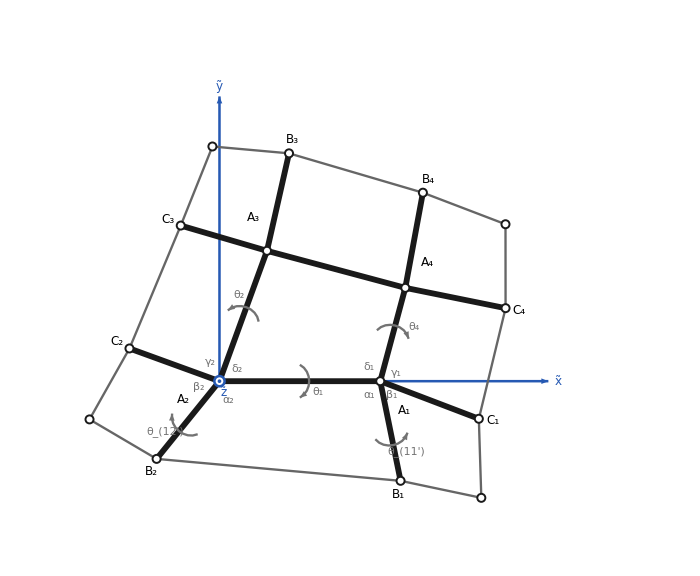
Given hypotheses and definitions:
A 3 x 3 net with, for each i = 1, 2,
the vertices A_i, B_i, C_i, and the vertices A_3, A_4 of the central face
the flat angles α_i, β_i, γ_i, δ_i ∈ (0, π) at A_i
the edge lengths ℓ_1 = |A_1 A_2|,   ℓ_2 = |A_2 A_3|,   ℓ_4 = |A_4 A_1|,   m_i = |A_i B_i|,   v_i = |A_i C_i|
the dihedral angles θ_1, θ_2, θ_4 ∈ [-π, π) \ {0} along the edges A_1 A_2, A_2 A_3, A_4 A_1

σ_i = 1/2 (α_i+β_i+γ_i+δ_i) | (ᾱ)_i = σ_i-α_i | (β̄)_i = σ_i-β_i | (γ̄)_i = σ_i-γ_i | (δ̄)_i = σ_i-δ_i
a_i = (sin α_i)/(sin (ᾱ)_i) | b_i = (sin β_i)/(sin (β̄)_i) | c_i = (sin γ_i)/(sin (γ̄)_i) | d_i = (sin δ_i)/(sin (δ̄)_i) | ε_i = sign(sin σ_i)
M_i = a_i b_i c_i d_i | r_i = a_i d_i | s_i = c_i d_i | f_i = a_i c_i | 
u_i = 1 - M_i | x_i = 1/(r_i - 1) | y_i = 1/(s_i - 1) | z_i = 1/(f_i - 1) | 
(ỹ)_i = (-(1 + y_i))/(1 + u_i y_i) | (z̃)_i = (-(1 + z_i))/(1 + u_i z_i) |  |  | 

α_i ± β_i ± γ_i ± δ_i ≠ 0 (mod 2π)
(ᾱ)_i, (β̄)_i, (γ̄)_i, (δ̄)_i ∈ (0, π)
ε_i ∈ {-1, 1}
x_i, y_i, z_i, (ỹ)_i, (z̃)_i ≠ -1, 0;   u_i x_i y_i z_i > 0

Normals:
(n⃗)_0 = (A_2 A_1)^⟶ × (A_2 A_3)^⟶
(n⃗)_1 = (A_2 A_1)^⟶ × (A_2 B_2)^⟶ | (n⃗)_2 = (A_2 C_2)^⟶ × (A_2 A_3)^⟶ | (n⃗)_4 = (A_1 A_4)^⟶ × (A_1 C_1)^⟶
(n⃗)_(1') = (A_1 B_1)^⟶ × (A_1 C_1)^⟶ | (n⃗)_(2') = (A_2 C_2)^⟶ × (A_2 B_2)^⟶

Dihedral angles:
θ((w⃗)_1, (w⃗)_2, (w⃗)_3) ∶= {∠((w⃗)_1, (w⃗)_2) ∈ (0, π), | if det((w⃗)_1, (w⃗)_2, (w⃗)_3) > 0,
-∠((w⃗)_1, (w⃗)_2) ∈ [-π, 0], | if det((w⃗)_1, (w⃗)_2, (w⃗)_3) ≤ 0.
central dihedral angles:
θ_1 = θ((n⃗)_0, (n⃗)_1, (A_2 A_1)^⟶) | θ_2 = θ((n⃗)_0, (n⃗)_2, (A_3 A_2)^⟶) | θ_4 = θ((n⃗)_0, (n⃗)_4, (A_1 A_4)^⟶)

corner dihedral angles:
θ_(11') = θ((n⃗)_1, (n⃗)_(1'), (B_1 A_1)^⟶) | θ_(12') = θ((n⃗)_1, (n⃗)_(2'), (A_2 B_2)^⟶)

Cartesian coordinates:
origin at A_2
central face in the half-plane ỹ ≥ 0 of the x̃ỹ-plane, the ray A_2 A_1 as the x̃-axis
-Graphics-
Figure 1

A_1 = {ℓ_1,0,0}
A_2 = {0,0,0}
A_3 = {ℓ_2 cos δ_2,ℓ_2 sin δ_2,0}
A_4 = {ℓ_1-ℓ_4 cos δ_1,ℓ_4 sin δ_1,0}
B_1 = A_1 + m_1 {-cos α_1,sin α_1 cos θ_1,sin α_1 sin θ_1}
B_2 = A_2 + m_2 {cos α_2,sin α_2 cos θ_1,sin α_2 sin θ_1}
C_1 = A_1 + v_1 {-sin γ_1 sin δ_1 cos θ_4-cos γ_1 cos δ_1,cos γ_1 sin δ_1-sin γ_1 cos δ_1 cos θ_4,sin γ_1 sin θ_4}
C_2 = A_2 + v_2 {sin γ_2 sin δ_2 cos θ_2+cos γ_2 cos δ_2,cos γ_2 sin δ_2-sin γ_2 cos δ_2 cos θ_2,sin γ_2 sin θ_2}
The definition gives θ((w⃗)_1, (w⃗)_2, (w⃗)_3) = ±∠((w⃗)_1, (w⃗)_2), by the sign of the determinant. The cosine is even and the sine is odd, so cos θ = ((w⃗)_1 · (w⃗)_2)/(|(w⃗)_1| |(w⃗)_2|) and sin θ = (det((w⃗)_1, (w⃗)_2, (w⃗)_3))/(|(w⃗)_1| |(w⃗)_2| |(w⃗)_3|) hold whichever sign the determinant has; the formula for the sine holds because (w⃗)_3, the direction of an edge common to the two faces, is orthogonal to (w⃗)_1 and (w⃗)_2, so that (w⃗)_1 × (w⃗)_2 is a multiple of (w⃗)_3. No formula of the notebook distinguishes the two cases, the coordinates above included.

Flexion:
x_2 = x_1,   u_1 = u_2 = u
e_1, e_2, e_0 ∈ {-1, 1}
D(X, t) = (X t^2 - 1)(1 - u X t^2),      I(X) = {t ∈ ℝ : X D(X, t) > 0},      for X, t ∈ ℝ

cot(θ_4/2) = (ε_1(cot(θ_1/2) √(u x_1 y_1(1 + z_1)(1 + u z_1)) - e_0 e_1 √(u y_1 z_1 D(x_1, cot(θ_1/2)))))/(y_1 u(z_1 + x_1 cot^2(θ_1/2)))
cot(θ_2/2) = (ε_2(cot(θ_1/2) √(u x_1 y_2(1 + z_2)(1 + u z_2)) + e_0 e_2 √(u y_2 z_2 D(x_1, cot(θ_1/2)))))/(y_2 u(z_2 + x_1 cot^2(θ_1/2)))
for cot(θ_1/2) ∈ I(x_1) with cot^2(θ_1/2) ≠ -z_1/x_1, -z_2/x_1

Each ☑ below certifies that the statement displayed beside it has been verified by a symbolic computation at that point; a × would mean that this verification failed. A • marks a given fact, a definition, a result of an earlier block, or an inference stated in words beside it.

We want to test the following claims ★ :

Claim 1.
For each i = 1, 2, the substitution
◼ (α_i, β_i, γ_i, δ_i)  ↦  (δ_i, γ_i, β_i, α_i)
takes the numbers of the vertex
◼ (u_i, x_i, y_i, z_i, ε_i)  ↦  (u_i, x_i, (ỹ)_i, (z̃)_i, ε_i)

Claim 2.
If θ_(11') ≠ 0, respectively θ_(12') ≠ 0, then

◼ cot(θ_(11')/2) = (sin α_1 sin γ_1 cot(θ_4/2) + sin (δ̄)_1 sin(β_1-(δ̄)_1) cot(θ_1/2) cot^2(θ_4/2) + sin (ᾱ)_1 sin(β_1-(ᾱ)_1) cot(θ_1/2))/(-sin(β_1-(γ̄)_1) sin(β_1-(δ̄)_1) cot^2(θ_4/2) + sin (ᾱ)_1 sin (β̄)_1)
◼ cot(θ_(12')/2) = (sin α_2 sin γ_2 cot(θ_2/2) + sin (δ̄)_2 sin(β_2-(δ̄)_2) cot(θ_1/2) cot^2(θ_2/2) + sin (ᾱ)_2 sin(β_2-(ᾱ)_2) cot(θ_1/2))/(-sin(β_2-(γ̄)_2) sin(β_2-(δ̄)_2) cot^2(θ_2/2) + sin (ᾱ)_2 sin (β̄)_2)

Claim 3.
◼ θ_(11') ≠ 0   if   cot^2(θ_1/2) ≠ -(z̃)_1/x_1
◼ θ_(12') ≠ 0   if   cot^2(θ_1/2) ≠ -(z̃)_2/x_2

Claim 4.
If x_2 = x_1,   u_1 = u_2 = u,   cot(θ_1/2) ∈ I(x_1), and cot^2(θ_1/2) ≠ -z_i/x_1, -(z̃)_i/x_1 for i = 1, 2, then

◼ cot(θ_(11')/2) = (ε_1(cot(θ_1/2) √(u x_1 (ỹ)_1(1 + (z̃)_1)(1 + u (z̃)_1)) - e_0 e_1 √(u (ỹ)_1 (z̃)_1 D(x_1, cot(θ_1/2)))))/((ỹ)_1 u((z̃)_1 + x_1 cot^2(θ_1/2)))
◼ cot(θ_(12')/2) = (ε_2(cot(θ_1/2) √(u x_1 (ỹ)_2(1 + (z̃)_2)(1 + u (z̃)_2)) + e_0 e_2 √(u (ỹ)_2 (z̃)_2 D(x_1, cot(θ_1/2)))))/((ỹ)_2 u((z̃)_2 + x_1 cot^2(θ_1/2)))

Claim 1: the substitutionVerified
Verification: the numbers of the given panel for the substituted angles, compared with those of the vertex; each line is an identity in the four flat angles.
Part 1.  At A_1: |  |  | 
(1.1) | (δ_1 + γ_1 + β_1 + α_1)/2 = σ_1 | ☑ | the half sum does not change, so each barred angle stays with its angle, and ε_1 does not change
(1.2) | (a_1, b_1, c_1, d_1)  ↦  (d_1, c_1, b_1, a_1) | ☑ | each is the sine of an angle over the sine of its barred angle
(1.3) | u_1  ↦  1 - d_1 c_1 b_1 a_1 = u_1 | ☑ | the product does not change
(1.4) | x_1  ↦  1/(d_1 a_1 - 1) = x_1 | ☑ | the product a_1 d_1 does not change
(1.5) | y_1  ↦  1/(b_1 a_1 - 1) = (-(1 + y_1))/(1 + u_1 y_1) = (ỹ)_1 | ☑ | because a_1 b_1 = M_1/(c_1 d_1) and c_1 d_1 = 1 + 1/y_1
(1.6) | z_1  ↦  1/(d_1 b_1 - 1) = (-(1 + z_1))/(1 + u_1 z_1) = (z̃)_1 | ☑ | because b_1 d_1 = M_1/(a_1 c_1) and a_1 c_1 = 1 + 1/z_1
 |  |  | 
Part 2.  At A_2: |  |  | 
(2.1) | (δ_2 + γ_2 + β_2 + α_2)/2 = σ_2 | ☑ | the half sum does not change, so each barred angle stays with its angle, and ε_2 does not change
(2.2) | (a_2, b_2, c_2, d_2)  ↦  (d_2, c_2, b_2, a_2) | ☑ | each is the sine of an angle over the sine of its barred angle
(2.3) | u_2  ↦  1 - d_2 c_2 b_2 a_2 = u_2 | ☑ | the product does not change
(2.4) | x_2  ↦  1/(d_2 a_2 - 1) = x_2 | ☑ | the product a_2 d_2 does not change
(2.5) | y_2  ↦  1/(b_2 a_2 - 1) = (-(1 + y_2))/(1 + u_2 y_2) = (ỹ)_2 | ☑ | because a_2 b_2 = M_2/(c_2 d_2) and c_2 d_2 = 1 + 1/y_2
(2.6) | z_2  ↦  1/(d_2 b_2 - 1) = (-(1 + z_2))/(1 + u_2 z_2) = (z̃)_2 | ☑ | because b_2 d_2 = M_2/(a_2 c_2) and a_2 c_2 = 1 + 1/z_2
 |  |  | 
Together, these give Claim 1.

the normals (n⃗)_0, (n⃗)_1, (n⃗)_2, (n⃗)_4 and the central dihedral anglesVerified
Verification: each normal from two edge vectors of its face; (11) and (12) identify θ_1, θ_2, θ_4 with the dihedral angles of the definition.
(1) | (A_2 A_1)^⟶ = {ℓ_1,0,0} | • | from the coordinates
(2) | (A_2 A_3)^⟶ = {ℓ_2 cos δ_2,ℓ_2 sin δ_2,0} | • | from the coordinates
(3) | (A_2 B_2)^⟶ = {m_2 cos α_2,m_2 sin α_2 cos θ_1,m_2 sin α_2 sin θ_1} | • | from the coordinates
(4) | (A_2 C_2)^⟶ = {v_2 (sin γ_2 sin δ_2 cos θ_2+cos γ_2 cos δ_2),v_2 (cos γ_2 sin δ_2-sin γ_2 cos δ_2 cos θ_2),v_2 sin γ_2 sin θ_2} | • | from the coordinates
(5) | (A_1 A_4)^⟶ = {ℓ_4 (-cos δ_1),ℓ_4 sin δ_1,0} | • | from the coordinates
(6) | (A_1 C_1)^⟶ = {v_1 (-sin γ_1 sin δ_1 cos θ_4-cos γ_1 cos δ_1),v_1 (cos γ_1 sin δ_1-sin γ_1 cos δ_1 cos θ_4),v_1 sin γ_1 sin θ_4} | • | from the coordinates
 |  |  | 
(7) | (n⃗)_0 = (A_2 A_1)^⟶ × (A_2 A_3)^⟶ = ℓ_1 ℓ_2 sin δ_2 {0,0,1},   |(n⃗)_0| = ℓ_1 ℓ_2 sin δ_2 | ☑ | from (1) and (2); the length because ℓ_1 ℓ_2 sin δ_2 > 0
(8) | (n⃗)_1 = (A_2 A_1)^⟶ × (A_2 B_2)^⟶ = m_2 ℓ_1 sin α_2 {0,-sin θ_1,cos θ_1},   |(n⃗)_1| = m_2 ℓ_1 sin α_2 | ☑ | from (1) and (3); the length because m_2 ℓ_1 sin α_2 > 0
(9) | (n⃗)_2 = (A_2 C_2)^⟶ × (A_2 A_3)^⟶ = v_2 ℓ_2 sin γ_2 {-sin δ_2 sin θ_2,cos δ_2 sin θ_2,cos θ_2},   |(n⃗)_2| = v_2 ℓ_2 sin γ_2 | ☑ | from (4) and (2); the length because v_2 ℓ_2 sin γ_2 > 0
(10) | (n⃗)_4 = (A_1 A_4)^⟶ × (A_1 C_1)^⟶ = v_1 ℓ_4 sin γ_1 {sin δ_1 sin θ_4,cos δ_1 sin θ_4,cos θ_4},   |(n⃗)_4| = v_1 ℓ_4 sin γ_1 | ☑ | from (5) and (6); the length because v_1 ℓ_4 sin γ_1 > 0
 |  |  | 
(11) | (n⃗)_0 · (n⃗)_i = |(n⃗)_0| |(n⃗)_i| cos θ_i | ☑ | for i = 1, 2, 4, from (7)–(10)
(12) | det((n⃗)_0, (n⃗)_i, (A_(i+1)A_i)^⟶) = |(n⃗)_0| |(n⃗)_i| ℓ_i sin θ_i | ☑ | for i = 1, 2, 4, from (7)–(10), with A_5 := A_1 and |(A_(i+1)A_i)^⟶| = ℓ_i
Together, these give the four normals and the three central dihedral angles.

the corner dihedral angles θ_(11') and θ_(12')Verified
Verification: at each vertex, the corner normal from its two edge vectors, then the cosine and the sine of its angle with (n⃗)_1; β_i enters through its cosine and the length of (n⃗)_i'.
Part 1.  At A_1, the angle θ_(11') along A_1 B_1: |  |  | 
(1.1) | (A_1 B_1)^⟶ = {m_1 (-cos α_1),m_1 sin α_1 cos θ_1,m_1 sin α_1 sin θ_1} | • | from the coordinates
(1.2) | (A_1 C_1)^⟶ = {v_1 (-sin γ_1 sin δ_1 cos θ_4-cos γ_1 cos δ_1),v_1 (cos γ_1 sin δ_1-sin γ_1 cos δ_1 cos θ_4),v_1 sin γ_1 sin θ_4} | • | from the coordinates
(1.3) | (n⃗)_(1') = (A_1 B_1)^⟶ × (A_1 C_1)^⟶ = {m_1 v_1 (sin θ_1 (sin α_1 sin γ_1 cos δ_1 cos θ_4-sin α_1 cos γ_1 sin δ_1)+sin α_1 sin γ_1 sin θ_4 cos θ_1),m_1 v_1 (sin θ_1 (sin α_1 (-cos γ_1) cos δ_1-sin α_1 sin γ_1 sin δ_1 cos θ_4)+cos α_1 sin γ_1 sin θ_4),m_1 v_1 (cos α_1 sin γ_1 cos δ_1 cos θ_4+cos θ_1 (sin α_1 sin γ_1 sin δ_1 cos θ_4+sin α_1 cos γ_1 cos δ_1)-cos α_1 cos γ_1 sin δ_1)} | ☑ | from (1.1) and (1.2)
(1.4) | cos β_1 = ((A_1 B_1)^⟶ · (A_1 C_1)^⟶)/(m_1 v_1) = cos α_1 (sin γ_1 sin δ_1 cos θ_4+cos γ_1 cos δ_1)+sin α_1 (cos θ_1 (cos γ_1 sin δ_1-sin γ_1 cos δ_1 cos θ_4)+sin γ_1 sin θ_1 sin θ_4) | ☑ | β_1 is the angle of the corner face at A_1; the closed forms below are written with it
(1.5) | |(n⃗)_(1')| = m_1 v_1 sin β_1 | ☑ | from (1.3) and (1.4), with the positive root because β_1 ∈ (0, π)
 |  |  | 
(1.6) | cos θ_(11') = ((n⃗)_1 · (n⃗)_(1'))/(|(n⃗)_1| |(n⃗)_(1')|) | • | by the definition
(1.7) | cos θ_(11') = (-cos α_1 cos β_1+sin γ_1 sin δ_1 cos θ_4+cos γ_1 cos δ_1)/(sin α_1 sin β_1) | ☑ | from (n⃗)_1 of the block above and (1.3)–(1.6)
 |  |  | 
(1.8) | (B_1 A_1)^⟶ = {m_1 cos α_1,m_1 sin α_1 (-cos θ_1),m_1 (-sin α_1) sin θ_1} | • | the third vector of θ_(11'), of length m_1
(1.9) | sin θ_(11') = (det((n⃗)_1, (n⃗)_(1'), (B_1 A_1)^⟶))/(|(n⃗)_1| |(n⃗)_(1')| |(B_1 A_1)^⟶|) | • | by the definition
(1.10) | sin θ_(11') = (sin θ_1 (cos γ_1 sin δ_1-sin γ_1 cos δ_1 cos θ_4)-sin γ_1 sin θ_4 cos θ_1)/(sin β_1) | ☑ | from (n⃗)_1 of the block above, (1.3), (1.5), (1.8), and (1.9)
 |  |  | 
Part 2.  At A_2, the angle θ_(12') along A_2 B_2: |  |  | 
(2.1) | (A_2 C_2)^⟶ = {v_2 (sin γ_2 sin δ_2 cos θ_2+cos γ_2 cos δ_2),v_2 (cos γ_2 sin δ_2-sin γ_2 cos δ_2 cos θ_2),v_2 sin γ_2 sin θ_2} | • | from the coordinates
(2.2) | (A_2 B_2)^⟶ = {m_2 cos α_2,m_2 sin α_2 cos θ_1,m_2 sin α_2 sin θ_1} | • | from the coordinates
(2.3) | (n⃗)_(2') = (A_2 C_2)^⟶ × (A_2 B_2)^⟶ = {m_2 v_2 (sin θ_1 (sin α_2 cos γ_2 sin δ_2-sin α_2 sin γ_2 cos δ_2 cos θ_2)-sin α_2 sin γ_2 sin θ_2 cos θ_1),m_2 v_2 (sin θ_1 (sin α_2 (-cos γ_2) cos δ_2-sin α_2 sin γ_2 sin δ_2 cos θ_2)+cos α_2 sin γ_2 sin θ_2),m_2 v_2 (cos α_2 sin γ_2 cos δ_2 cos θ_2+cos θ_1 (sin α_2 sin γ_2 sin δ_2 cos θ_2+sin α_2 cos γ_2 cos δ_2)-cos α_2 cos γ_2 sin δ_2)} | ☑ | from (2.1) and (2.2)
(2.4) | cos β_2 = ((A_2 B_2)^⟶ · (A_2 C_2)^⟶)/(m_2 v_2) = cos α_2 (sin γ_2 sin δ_2 cos θ_2+cos γ_2 cos δ_2)+sin α_2 (cos θ_1 (cos γ_2 sin δ_2-sin γ_2 cos δ_2 cos θ_2)+sin γ_2 sin θ_1 sin θ_2) | ☑ | β_2 is the angle of the corner face at A_2; the closed forms below are written with it
(2.5) | |(n⃗)_(2')| = m_2 v_2 sin β_2 | ☑ | from (2.3) and (2.4), with the positive root because β_2 ∈ (0, π)
 |  |  | 
(2.6) | cos θ_(12') = ((n⃗)_1 · (n⃗)_(2'))/(|(n⃗)_1| |(n⃗)_(2')|) | • | by the definition
(2.7) | cos θ_(12') = (-cos α_2 cos β_2+sin γ_2 sin δ_2 cos θ_2+cos γ_2 cos δ_2)/(sin α_2 sin β_2) | ☑ | from (n⃗)_1 of the block above and (2.3)–(2.6)
 |  |  | 
(2.8) | (A_2 B_2)^⟶ = {m_2 cos α_2,m_2 sin α_2 cos θ_1,m_2 sin α_2 sin θ_1} | • | the third vector of θ_(12'), of length m_2
(2.9) | sin θ_(12') = (det((n⃗)_1, (n⃗)_(2'), (A_2 B_2)^⟶))/(|(n⃗)_1| |(n⃗)_(2')| |(A_2 B_2)^⟶|) | • | by the definition
(2.10) | sin θ_(12') = (sin θ_1 (cos γ_2 sin δ_2-sin γ_2 cos δ_2 cos θ_2)-sin γ_2 sin θ_2 cos θ_1)/(sin β_2) | ☑ | from (n⃗)_1 of the block above, (2.3), (2.5), (2.8), and (2.9)
 |  |  | 
Together, these give the cosine and the sine of θ_(11') and θ_(12').

Claim 2: the corner dihedral angles through the central onesVerified
Verification: at each vertex, the sine and 1 - cos of the corner angle through the two half-angle cotangents; Bricard's equation reduces their quotient to Φ_1/Φ_2. Each step between lines is checked with the displayed quantities as symbols.
(1) | cot(θ/2) = (sin θ)/(1 - cos θ),      sin θ = (2 cot(θ/2))/(1 + cot^2(θ/2)),      cos θ = (cot^2(θ/2) - 1)/(cot^2(θ/2) + 1) | ☑ | for θ ≠ 0 (mod 2π)
 |  |  | 
Part 1.  At A_1, the angle θ_(11') through θ_1 and θ_4: |  |  | 
(1.1) | sin θ_(11') sin β_1 ((1 + cot^2(θ_1/2))(1 + cot^2(θ_4/2)))/2 = -sin(γ_1-δ_1) cot(θ_1/2) cot^2(θ_4/2) - sin γ_1 cot^2(θ_1/2) cot(θ_4/2) + sin(γ_1+δ_1) cot(θ_1/2) + sin γ_1 cot(θ_4/2) | ☑ | sin θ_(11') of the block of the corner angles, with (1)
(1.2) | (1 - cos θ_(11')) sin α_1 sin β_1 (1 + cot^2(θ_4/2))/2 = -sin(β_1-(γ̄)_1) sin(β_1-(δ̄)_1) cot^2(θ_4/2) + sin (ᾱ)_1 sin (β̄)_1 | ☑ | cos θ_(11') of the block of the corner angles, with (1)
 | Φ := -sin(γ_1-δ_1) cot(θ_1/2) cot^2(θ_4/2) - sin γ_1 cot^2(θ_1/2) cot(θ_4/2) + sin(γ_1+δ_1) cot(θ_1/2) + sin γ_1 cot(θ_4/2) | • | a name for the right side of (1.1)
 | Φ_2 := -sin(β_1-(γ̄)_1) sin(β_1-(δ̄)_1) cot^2(θ_4/2) + sin (ᾱ)_1 sin (β̄)_1 | • | a name for the right side of (1.2)
(1.3) | cot(θ_(11')/2) = (sin θ_(11'))/(1 - cos θ_(11')) = (sin α_1 Φ)/((1 + cot^2(θ_1/2)) Φ_2) | ☑ | the quotient of (1.1) and (1.2), by (1); here Φ_2 ≠ 0 by (1.2), because θ_(11') ≠ 0
 |  |  | 
(1.4) | Φ_0 := (-sin (δ̄)_1 sin(β_1-(δ̄)_1) cot^2(θ_4/2) - sin (ᾱ)_1 sin(β_1-(ᾱ)_1)) cot^2(θ_1/2)
          - 2 sin α_1 sin γ_1 cot(θ_1/2) cot(θ_4/2)
          + (-sin (γ̄)_1 sin(β_1-(γ̄)_1) cot^2(θ_4/2) + sin σ_1 sin (β̄)_1) = 0 | ☑ | the closure (A_1 B_1)^⟶ · (A_1 C_1)^⟶ = m_1 v_1 cos β_1 (Bricard's equation), with (1)
(1.5) | -sin α_1 sin(γ_1-δ_1) = sin (δ̄)_1 sin(β_1-(δ̄)_1) - sin (γ̄)_1 sin(β_1-(γ̄)_1) | ☑ | by sin x sin y = (cos(x - y) - cos(x + y))/2, each side is 1/2 (cos(α_1+γ_1-δ_1)-cos(α_1-γ_1+δ_1))
(1.6) | sin α_1 sin(γ_1+δ_1) = sin σ_1 sin (β̄)_1 + sin (ᾱ)_1 sin(β_1-(ᾱ)_1) | ☑ | in the same way, each side is 1/2 (cos(α_1-γ_1-δ_1)-cos(α_1+γ_1+δ_1))
 | Φ_1 := sin α_1 sin γ_1 cot(θ_4/2) + sin (δ̄)_1 sin(β_1-(δ̄)_1) cot(θ_1/2) cot^2(θ_4/2) + sin (ᾱ)_1 sin(β_1-(ᾱ)_1) cot(θ_1/2) | • | a name for the numerator of the formula in Claim 2
(1.7) | sin α_1 Φ - (1 + cot^2(θ_1/2)) Φ_1 = cot(θ_1/2) Φ_0 | ☑ | expand the three products: the coefficients of cot(θ_1/2) cot^2(θ_4/2) and of cot(θ_1/2) cancel by (1.5) and (1.6), the other four term by term
(1.8) | cot(θ_(11')/2) = Φ_1/Φ_2 | ☑ | (1.3), where sin α_1 Φ = (1 + cot^2(θ_1/2)) Φ_1 by (1.7), because Φ_0 = 0 by (1.4)
 |  |  | 
Part 2.  At A_2, the angle θ_(12') through θ_1 and θ_2: |  |  | 
(2.1) | sin θ_(12') sin β_2 ((1 + cot^2(θ_1/2))(1 + cot^2(θ_2/2)))/2 = -sin(γ_2-δ_2) cot(θ_1/2) cot^2(θ_2/2) - sin γ_2 cot^2(θ_1/2) cot(θ_2/2) + sin(γ_2+δ_2) cot(θ_1/2) + sin γ_2 cot(θ_2/2) | ☑ | sin θ_(12') of the block of the corner angles, with (1)
(2.2) | (1 - cos θ_(12')) sin α_2 sin β_2 (1 + cot^2(θ_2/2))/2 = -sin(β_2-(γ̄)_2) sin(β_2-(δ̄)_2) cot^2(θ_2/2) + sin (ᾱ)_2 sin (β̄)_2 | ☑ | cos θ_(12') of the block of the corner angles, with (1)
 | Φ := -sin(γ_2-δ_2) cot(θ_1/2) cot^2(θ_2/2) - sin γ_2 cot^2(θ_1/2) cot(θ_2/2) + sin(γ_2+δ_2) cot(θ_1/2) + sin γ_2 cot(θ_2/2) | • | a name for the right side of (2.1)
 | Φ_2 := -sin(β_2-(γ̄)_2) sin(β_2-(δ̄)_2) cot^2(θ_2/2) + sin (ᾱ)_2 sin (β̄)_2 | • | a name for the right side of (2.2)
(2.3) | cot(θ_(12')/2) = (sin θ_(12'))/(1 - cos θ_(12')) = (sin α_2 Φ)/((1 + cot^2(θ_1/2)) Φ_2) | ☑ | the quotient of (2.1) and (2.2), by (1); here Φ_2 ≠ 0 by (2.2), because θ_(12') ≠ 0
 |  |  | 
(2.4) | Φ_0 := (-sin (δ̄)_2 sin(β_2-(δ̄)_2) cot^2(θ_2/2) - sin (ᾱ)_2 sin(β_2-(ᾱ)_2)) cot^2(θ_1/2)
          - 2 sin α_2 sin γ_2 cot(θ_1/2) cot(θ_2/2)
          + (-sin (γ̄)_2 sin(β_2-(γ̄)_2) cot^2(θ_2/2) + sin σ_2 sin (β̄)_2) = 0 | ☑ | the closure (A_2 B_2)^⟶ · (A_2 C_2)^⟶ = m_2 v_2 cos β_2 (Bricard's equation), with (1)
(2.5) | -sin α_2 sin(γ_2-δ_2) = sin (δ̄)_2 sin(β_2-(δ̄)_2) - sin (γ̄)_2 sin(β_2-(γ̄)_2) | ☑ | by sin x sin y = (cos(x - y) - cos(x + y))/2, each side is 1/2 (cos(α_2+γ_2-δ_2)-cos(α_2-γ_2+δ_2))
(2.6) | sin α_2 sin(γ_2+δ_2) = sin σ_2 sin (β̄)_2 + sin (ᾱ)_2 sin(β_2-(ᾱ)_2) | ☑ | in the same way, each side is 1/2 (cos(α_2-γ_2-δ_2)-cos(α_2+γ_2+δ_2))
 | Φ_1 := sin α_2 sin γ_2 cot(θ_2/2) + sin (δ̄)_2 sin(β_2-(δ̄)_2) cot(θ_1/2) cot^2(θ_2/2) + sin (ᾱ)_2 sin(β_2-(ᾱ)_2) cot(θ_1/2) | • | a name for the numerator of the formula in Claim 2
(2.7) | sin α_2 Φ - (1 + cot^2(θ_1/2)) Φ_1 = cot(θ_1/2) Φ_0 | ☑ | expand the three products: the coefficients of cot(θ_1/2) cot^2(θ_2/2) and of cot(θ_1/2) cancel by (2.5) and (2.6), the other four term by term
(2.8) | cot(θ_(12')/2) = Φ_1/Φ_2 | ☑ | (2.3), where sin α_2 Φ = (1 + cot^2(θ_1/2)) Φ_1 by (2.7), because Φ_0 = 0 by (2.4)
 |  |  | 
Together, these give Claim 2.

Claim 3: the corner angles are not 0Verified
Verification: at each vertex, with t = cot(θ_1/2): if the corner angle were 0, the identity (i.8) would make the left side of (i.2) vanish.
Part 1.  At A_1: |  |  | 
(1.1) | sin σ_1 sin (γ̄)_1 (ỹ)_1 u_1((z̃)_1 + x_1 t^2) = -sin (ᾱ)_1 sin(γ_1-(ᾱ)_1) t^2 - sin (β̄)_1 sin(γ_1-(β̄)_1) | ☑ | an identity in the flat angles at the vertex
(1.2) | -sin (ᾱ)_1 sin(γ_1-(ᾱ)_1) t^2 - sin (β̄)_1 sin(γ_1-(β̄)_1) ≠ 0   if   t^2 ≠ -(z̃)_1/x_1 | • | by (1.1), because (ỹ)_1 ≠ 0, u_1 ≠ 0 by u_1 x_1 y_1 z_1 > 0, sin σ_1 ≠ 0 by ε_1 ∈ {-1, 1}, and sin (γ̄)_1 > 0
 |  |  | 
 | Φ := -sin(γ_1-δ_1) t cot^2(θ_4/2) - sin γ_1 t^2 cot(θ_4/2) + sin(γ_1+δ_1) t + sin γ_1 cot(θ_4/2) | • | as in the block of Claim 2, with t = cot(θ_1/2)
 | Φ_0 := (-sin (δ̄)_1 sin(β_1-(δ̄)_1) cot^2(θ_4/2) - sin (ᾱ)_1 sin(β_1-(ᾱ)_1)) t^2
          - 2 sin α_1 sin γ_1 t cot(θ_4/2)
          + (-sin (γ̄)_1 sin(β_1-(γ̄)_1) cot^2(θ_4/2) + sin σ_1 sin (β̄)_1) | • | as there; Φ_0 = 0 by its (1.4)
 | Φ_1 := sin α_1 sin γ_1 cot(θ_4/2) + sin (δ̄)_1 sin(β_1-(δ̄)_1) t cot^2(θ_4/2) + sin (ᾱ)_1 sin(β_1-(ᾱ)_1) t | • | as there
 | Φ_2 := -sin(β_1-(γ̄)_1) sin(β_1-(δ̄)_1) cot^2(θ_4/2) + sin (ᾱ)_1 sin (β̄)_1 | • | as there
(1.3) | sin (ᾱ)_1 sin (γ̄)_1+sin (β̄)_1 sin (δ̄)_1 = sin α_1 sin γ_1+sin β_1 sin δ_1 | ☑ | by sin x sin y = (cos(x - y) - cos(x + y))/2, each side is 1/2 (cos(α_1-γ_1)-cos(α_1+γ_1)+cos(β_1-δ_1)-cos(β_1+δ_1))
(1.4) | sin(β_1-(ᾱ)_1) sin(β_1-(γ̄)_1)+sin (β̄)_1 sin (δ̄)_1 = sin α_1 sin γ_1 | ☑ | in the same way, each side is 1/2 (cos(α_1-γ_1)-cos(α_1+γ_1))
(1.5) | sin (ᾱ)_1 sin (γ̄)_1-sin α_1 sin γ_1 = sin σ_1 sin(β_1-(δ̄)_1) | ☑ | in the same way, each side is 1/2 (cos(α_1+γ_1)-cos(β_1+δ_1))
(1.6) | sin(γ_1-(ᾱ)_1) = -sin(β_1-(δ̄)_1),   sin(γ_1-(β̄)_1) = sin(β_1-(γ̄)_1) | ☑ | because γ_1-(ᾱ)_1 = (δ̄)_1-β_1 and γ_1-(β̄)_1 = β_1-(γ̄)_1
(1.7) | (1 + cos θ_(11')) sin α_1 sin β_1 (1 + cot^2(θ_4/2))/2 = sin (γ̄)_1 sin (δ̄)_1 cot^2(θ_4/2) + sin σ_1 sin(β_1-(ᾱ)_1) =: Ψ | ☑ | cos θ_(11') of the block of the corner angles, with (1) of the block of Claim 2
(1.8) | (-sin (ᾱ)_1 sin(γ_1-(ᾱ)_1) t^2 - sin (β̄)_1 sin(γ_1-(β̄)_1)) Ψ - (sin β_1 sin δ_1 t + (-sin (δ̄)_1 sin(β_1-(δ̄)_1) t^2 - sin (γ̄)_1 sin(β_1-(γ̄)_1)) cot(θ_4/2) - sin α_1 sin γ_1 t) Φ_1
          = (-sin (δ̄)_1 sin(β_1-(δ̄)_1) t cot(θ_4/2) - sin(β_1-(ᾱ)_1) sin(γ_1-(β̄)_1)) Φ_0 | ☑ | expand both sides, with (1.6): the coefficients of t^3 cot^3(θ_4/2), t^3 cot(θ_4/2), t cot^3(θ_4/2), 1 agree term by term, those of t^2 cot^2(θ_4/2), t^2, cot^2(θ_4/2), after taking out the factors sin (δ̄)_1 sin(β_1-(δ̄)_1), sin (ᾱ)_1 sin(β_1-(ᾱ)_1), sin (γ̄)_1 sin(β_1-(γ̄)_1), by (1.3) and (1.4), (1.3) to (1.5), (1.4), and that of t cot(θ_4/2) by (1.3) to (1.5)
(1.9) | θ_(11') ≠ 0   if   t^2 ≠ -(z̃)_1/x_1 | • | if θ_(11') = 0, then, in the block of Claim 2, Φ = Φ_2 = 0 by (1.1) and (1.2), and Φ_1 = 0 by (1.7), because Φ_0 = 0 by (1.4); here Ψ = sin α_1 sin β_1(1 + cot^2(θ_4/2)) > 0 by (1.7), so (1.8) gives (-sin (ᾱ)_1 sin(γ_1-(ᾱ)_1) t^2 - sin (β̄)_1 sin(γ_1-(β̄)_1)) Ψ = 0, against (1.2)
 |  |  | 
Part 2.  At A_2: |  |  | 
(2.1) | sin σ_2 sin (γ̄)_2 (ỹ)_2 u_2((z̃)_2 + x_2 t^2) = -sin (ᾱ)_2 sin(γ_2-(ᾱ)_2) t^2 - sin (β̄)_2 sin(γ_2-(β̄)_2) | ☑ | an identity in the flat angles at the vertex
(2.2) | -sin (ᾱ)_2 sin(γ_2-(ᾱ)_2) t^2 - sin (β̄)_2 sin(γ_2-(β̄)_2) ≠ 0   if   t^2 ≠ -(z̃)_2/x_2 | • | by (2.1), because (ỹ)_2 ≠ 0, u_2 ≠ 0 by u_2 x_2 y_2 z_2 > 0, sin σ_2 ≠ 0 by ε_2 ∈ {-1, 1}, and sin (γ̄)_2 > 0
 |  |  | 
 | Φ := -sin(γ_2-δ_2) t cot^2(θ_2/2) - sin γ_2 t^2 cot(θ_2/2) + sin(γ_2+δ_2) t + sin γ_2 cot(θ_2/2) | • | as in the block of Claim 2, with t = cot(θ_1/2)
 | Φ_0 := (-sin (δ̄)_2 sin(β_2-(δ̄)_2) cot^2(θ_2/2) - sin (ᾱ)_2 sin(β_2-(ᾱ)_2)) t^2
          - 2 sin α_2 sin γ_2 t cot(θ_2/2)
          + (-sin (γ̄)_2 sin(β_2-(γ̄)_2) cot^2(θ_2/2) + sin σ_2 sin (β̄)_2) | • | as there; Φ_0 = 0 by its (2.4)
 | Φ_1 := sin α_2 sin γ_2 cot(θ_2/2) + sin (δ̄)_2 sin(β_2-(δ̄)_2) t cot^2(θ_2/2) + sin (ᾱ)_2 sin(β_2-(ᾱ)_2) t | • | as there
 | Φ_2 := -sin(β_2-(γ̄)_2) sin(β_2-(δ̄)_2) cot^2(θ_2/2) + sin (ᾱ)_2 sin (β̄)_2 | • | as there
(2.3) | sin (ᾱ)_2 sin (γ̄)_2+sin (β̄)_2 sin (δ̄)_2 = sin α_2 sin γ_2+sin β_2 sin δ_2 | ☑ | by sin x sin y = (cos(x - y) - cos(x + y))/2, each side is 1/2 (cos(α_2-γ_2)-cos(α_2+γ_2)+cos(β_2-δ_2)-cos(β_2+δ_2))
(2.4) | sin(β_2-(ᾱ)_2) sin(β_2-(γ̄)_2)+sin (β̄)_2 sin (δ̄)_2 = sin α_2 sin γ_2 | ☑ | in the same way, each side is 1/2 (cos(α_2-γ_2)-cos(α_2+γ_2))
(2.5) | sin (ᾱ)_2 sin (γ̄)_2-sin α_2 sin γ_2 = sin σ_2 sin(β_2-(δ̄)_2) | ☑ | in the same way, each side is 1/2 (cos(α_2+γ_2)-cos(β_2+δ_2))
(2.6) | sin(γ_2-(ᾱ)_2) = -sin(β_2-(δ̄)_2),   sin(γ_2-(β̄)_2) = sin(β_2-(γ̄)_2) | ☑ | because γ_2-(ᾱ)_2 = (δ̄)_2-β_2 and γ_2-(β̄)_2 = β_2-(γ̄)_2
(2.7) | (1 + cos θ_(12')) sin α_2 sin β_2 (1 + cot^2(θ_2/2))/2 = sin (γ̄)_2 sin (δ̄)_2 cot^2(θ_2/2) + sin σ_2 sin(β_2-(ᾱ)_2) =: Ψ | ☑ | cos θ_(12') of the block of the corner angles, with (1) of the block of Claim 2
(2.8) | (-sin (ᾱ)_2 sin(γ_2-(ᾱ)_2) t^2 - sin (β̄)_2 sin(γ_2-(β̄)_2)) Ψ - (sin β_2 sin δ_2 t + (-sin (δ̄)_2 sin(β_2-(δ̄)_2) t^2 - sin (γ̄)_2 sin(β_2-(γ̄)_2)) cot(θ_2/2) - sin α_2 sin γ_2 t) Φ_1
          = (-sin (δ̄)_2 sin(β_2-(δ̄)_2) t cot(θ_2/2) - sin(β_2-(ᾱ)_2) sin(γ_2-(β̄)_2)) Φ_0 | ☑ | expand both sides, with (2.6): the coefficients of t^3 cot^3(θ_2/2), t^3 cot(θ_2/2), t cot^3(θ_2/2), 1 agree term by term, those of t^2 cot^2(θ_2/2), t^2, cot^2(θ_2/2), after taking out the factors sin (δ̄)_2 sin(β_2-(δ̄)_2), sin (ᾱ)_2 sin(β_2-(ᾱ)_2), sin (γ̄)_2 sin(β_2-(γ̄)_2), by (2.3) and (2.4), (2.3) to (2.5), (2.4), and that of t cot(θ_2/2) by (2.3) to (2.5)
(2.9) | θ_(12') ≠ 0   if   t^2 ≠ -(z̃)_2/x_2 | • | if θ_(12') = 0, then, in the block of Claim 2, Φ = Φ_2 = 0 by (2.1) and (2.2), and Φ_1 = 0 by (2.7), because Φ_0 = 0 by (2.4); here Ψ = sin α_2 sin β_2(1 + cot^2(θ_2/2)) > 0 by (2.7), so (2.8) gives (-sin (ᾱ)_2 sin(γ_2-(ᾱ)_2) t^2 - sin (β̄)_2 sin(γ_2-(β̄)_2)) Ψ = 0, against (2.2)
 |  |  | 
Together, these give Claim 3.

Claim 4: the formulasVerified
Verification: at each vertex, t = cot(θ_1/2) and ω = e_0 e_i ε_i sin σ_i sin (β̄)_i √(u y_i z_i D(x_1, t)). Lines (i.3) and (i.7) reduce Claim 4 to line (i.9), which has no radical, and line (i.8) proves (i.9). Each step between lines is checked with the displayed quantities as symbols.
Part 1.  At A_1, where u_1 = u: |  |  | 
(1.1) | u x_1 y_1(1 + z_1)(1 + u z_1) = ((sin α_1 sin γ_1)/(sin σ_1 sin (β̄)_1))^2 | ☑ | hence ε_1 √(u x_1 y_1(1 + z_1)(1 + u z_1)) = (sin α_1 sin γ_1)/(sin σ_1 sin (β̄)_1), because sin α_1 sin γ_1 > 0, sin (β̄)_1 > 0 and ε_1 = sign(sin σ_1)
(1.2) | sin σ_1 sin (β̄)_1 y_1 u(z_1 + x_1 t^2) = -sin (δ̄)_1 sin(β_1-(δ̄)_1) t^2 - sin (γ̄)_1 sin(β_1-(γ̄)_1) | ☑ | the denominator of the formula for cot(θ_4/2), times sin σ_1 sin (β̄)_1
(1.3) | (-sin (δ̄)_1 sin(β_1-(δ̄)_1) t^2 - sin (γ̄)_1 sin(β_1-(γ̄)_1)) cot(θ_4/2) - sin α_1 sin γ_1 t = -ω | ☑ | the formula for cot(θ_4/2) of the given panel, whose denominator is not 0 because t^2 ≠ -z_1/x_1 by assumption and y_1, u ≠ 0, multiplied by the left side of (1.2), with (1.1)
 |  |  | 
(1.4) | u x_1 (ỹ)_1(1 + (z̃)_1)(1 + u (z̃)_1) = ((sin β_1 sin δ_1)/(sin σ_1 sin (γ̄)_1))^2 | ☑ | hence ε_1 √(u x_1 (ỹ)_1(1 + (z̃)_1)(1 + u (z̃)_1)) = (sin β_1 sin δ_1)/(sin σ_1 sin (γ̄)_1), in the same way
(1.5) | u (ỹ)_1 (z̃)_1 sin^2 (γ̄)_1 = u y_1 z_1 sin^2 (β̄)_1 | ☑ | hence sin (γ̄)_1 √(u (ỹ)_1 (z̃)_1 D(x_1, cot(θ_1/2))) = sin (β̄)_1 √(u y_1 z_1 D(x_1, cot(θ_1/2))), because u y_1 z_1 D(x_1, t) = u x_1 y_1 z_1 · x_1 D(x_1, t)/x_1^2 > 0
(1.6) | sin σ_1 sin (γ̄)_1 (ỹ)_1 u((z̃)_1 + x_1 t^2) = -sin (ᾱ)_1 sin(γ_1-(ᾱ)_1) t^2 - sin (β̄)_1 sin(γ_1-(β̄)_1) ≠ 0 | • | (1.1) and (1.2) of the block of Claim 3, with u_1 = u, because t^2 ≠ -(z̃)_1/x_1 by assumption
(1.7) | (-sin (ᾱ)_1 sin(γ_1-(ᾱ)_1) t^2 - sin (β̄)_1 sin(γ_1-(β̄)_1)) (ε_1(t √(u x_1 (ỹ)_1(1 + (z̃)_1)(1 + u (z̃)_1)) - e_0 e_1 √(u (ỹ)_1 (z̃)_1 D(x_1, t))))/((ỹ)_1 u((z̃)_1 + x_1 t^2)) - sin β_1 sin δ_1 t = -ω | ☑ | by (1.6), the factor before the fraction is sin σ_1 sin (γ̄)_1 times its denominator; then (1.4), (1.5), and the definition of ω
 |  |  | 
 | Φ := -sin(γ_1-δ_1) t cot^2(θ_4/2) - sin γ_1 t^2 cot(θ_4/2) + sin(γ_1+δ_1) t + sin γ_1 cot(θ_4/2) | • | as in the block of Claim 2, with t = cot(θ_1/2)
 | Φ_0 := (-sin (δ̄)_1 sin(β_1-(δ̄)_1) cot^2(θ_4/2) - sin (ᾱ)_1 sin(β_1-(ᾱ)_1)) t^2
          - 2 sin α_1 sin γ_1 t cot(θ_4/2)
          + (-sin (γ̄)_1 sin(β_1-(γ̄)_1) cot^2(θ_4/2) + sin σ_1 sin (β̄)_1) | • | as there; Φ_0 = 0 by its (1.4)
 | Φ_1 := sin α_1 sin γ_1 cot(θ_4/2) + sin (δ̄)_1 sin(β_1-(δ̄)_1) t cot^2(θ_4/2) + sin (ᾱ)_1 sin(β_1-(ᾱ)_1) t | • | as there
 | Φ_2 := -sin(β_1-(γ̄)_1) sin(β_1-(δ̄)_1) cot^2(θ_4/2) + sin (ᾱ)_1 sin (β̄)_1 | • | as there
(1.8) | (-sin (ᾱ)_1 sin(γ_1-(ᾱ)_1) t^2 - sin (β̄)_1 sin(γ_1-(β̄)_1)) Φ_1 - (sin β_1 sin δ_1 t + (-sin (δ̄)_1 sin(β_1-(δ̄)_1) t^2 - sin (γ̄)_1 sin(β_1-(γ̄)_1)) cot(θ_4/2) - sin α_1 sin γ_1 t) Φ_2
          = -(-sin(β_1-(γ̄)_1) sin(β_1-(δ̄)_1) cot(θ_4/2) - sin (ᾱ)_1 sin(γ_1-(ᾱ)_1) t) Φ_0 | ☑ | expand both sides, with (1.6) of the block of Claim 3: the coefficients of t^3 cot^2(θ_4/2), t^3, t^2 cot^3(θ_4/2), cot^3(θ_4/2) agree term by term, and those of t^2 cot(θ_4/2), t cot^2(θ_4/2), t, cot(θ_4/2), after taking out the factors sin (ᾱ)_1 sin(β_1-(δ̄)_1), sin(β_1-(γ̄)_1) sin(β_1-(δ̄)_1), sin (ᾱ)_1 sin (β̄)_1, sin (β̄)_1 sin(β_1-(γ̄)_1), by its (1.4), (1.3), (1.3) to (1.5), (1.5)
(1.9) | (-sin (ᾱ)_1 sin(γ_1-(ᾱ)_1) t^2 - sin (β̄)_1 sin(γ_1-(β̄)_1)) cot(θ_(11')/2) - sin β_1 sin δ_1 t = (-sin (δ̄)_1 sin(β_1-(δ̄)_1) t^2 - sin (γ̄)_1 sin(β_1-(γ̄)_1)) cot(θ_4/2) - sin α_1 sin γ_1 t | ☑ | (1.8) divided by Φ_2, which is not 0 by Claim 3 and (1.2) of the block of Claim 2, because Φ_1/Φ_2 = cot(θ_(11')/2) by Claim 2 and Φ_0 = 0
(1.10) | cot(θ_(11')/2) = (ε_1(t √(u x_1 (ỹ)_1(1 + (z̃)_1)(1 + u (z̃)_1)) - e_0 e_1 √(u (ỹ)_1 (z̃)_1 D(x_1, t))))/((ỹ)_1 u((z̃)_1 + x_1 t^2)) | ☑ | the right sides of (1.7) and (1.9) are equal by (1.3), hence so are their left sides; divide by -sin (ᾱ)_1 sin(γ_1-(ᾱ)_1) t^2 - sin (β̄)_1 sin(γ_1-(β̄)_1), which is not 0 by (1.6)
 |  |  | 
Part 2.  At A_2, where x_2 = x_1 and u_2 = u: |  |  | 
(2.1) | u x_1 y_2(1 + z_2)(1 + u z_2) = ((sin α_2 sin γ_2)/(sin σ_2 sin (β̄)_2))^2 | ☑ | hence ε_2 √(u x_1 y_2(1 + z_2)(1 + u z_2)) = (sin α_2 sin γ_2)/(sin σ_2 sin (β̄)_2), because sin α_2 sin γ_2 > 0, sin (β̄)_2 > 0 and ε_2 = sign(sin σ_2)
(2.2) | sin σ_2 sin (β̄)_2 y_2 u(z_2 + x_1 t^2) = -sin (δ̄)_2 sin(β_2-(δ̄)_2) t^2 - sin (γ̄)_2 sin(β_2-(γ̄)_2) | ☑ | the denominator of the formula for cot(θ_2/2), times sin σ_2 sin (β̄)_2
(2.3) | (-sin (δ̄)_2 sin(β_2-(δ̄)_2) t^2 - sin (γ̄)_2 sin(β_2-(γ̄)_2)) cot(θ_2/2) - sin α_2 sin γ_2 t = ω | ☑ | the formula for cot(θ_2/2) of the given panel, whose denominator is not 0 because t^2 ≠ -z_2/x_1 by assumption and y_2, u ≠ 0, multiplied by the left side of (2.2), with (2.1)
 |  |  | 
(2.4) | u x_1 (ỹ)_2(1 + (z̃)_2)(1 + u (z̃)_2) = ((sin β_2 sin δ_2)/(sin σ_2 sin (γ̄)_2))^2 | ☑ | hence ε_2 √(u x_1 (ỹ)_2(1 + (z̃)_2)(1 + u (z̃)_2)) = (sin β_2 sin δ_2)/(sin σ_2 sin (γ̄)_2), in the same way
(2.5) | u (ỹ)_2 (z̃)_2 sin^2 (γ̄)_2 = u y_2 z_2 sin^2 (β̄)_2 | ☑ | hence sin (γ̄)_2 √(u (ỹ)_2 (z̃)_2 D(x_1, cot(θ_1/2))) = sin (β̄)_2 √(u y_2 z_2 D(x_1, cot(θ_1/2))), because u y_2 z_2 D(x_1, t) = u x_1 y_2 z_2 · x_1 D(x_1, t)/x_1^2 > 0
(2.6) | sin σ_2 sin (γ̄)_2 (ỹ)_2 u((z̃)_2 + x_1 t^2) = -sin (ᾱ)_2 sin(γ_2-(ᾱ)_2) t^2 - sin (β̄)_2 sin(γ_2-(β̄)_2) ≠ 0 | • | (2.1) and (2.2) of the block of Claim 3, with x_2 = x_1 and u_2 = u, because t^2 ≠ -(z̃)_2/x_1 by assumption
(2.7) | (-sin (ᾱ)_2 sin(γ_2-(ᾱ)_2) t^2 - sin (β̄)_2 sin(γ_2-(β̄)_2)) (ε_2(t √(u x_1 (ỹ)_2(1 + (z̃)_2)(1 + u (z̃)_2)) + e_0 e_2 √(u (ỹ)_2 (z̃)_2 D(x_1, t))))/((ỹ)_2 u((z̃)_2 + x_1 t^2)) - sin β_2 sin δ_2 t = ω | ☑ | by (2.6), the factor before the fraction is sin σ_2 sin (γ̄)_2 times its denominator; then (2.4), (2.5), and the definition of ω
 |  |  | 
 | Φ := -sin(γ_2-δ_2) t cot^2(θ_2/2) - sin γ_2 t^2 cot(θ_2/2) + sin(γ_2+δ_2) t + sin γ_2 cot(θ_2/2) | • | as in the block of Claim 2, with t = cot(θ_1/2)
 | Φ_0 := (-sin (δ̄)_2 sin(β_2-(δ̄)_2) cot^2(θ_2/2) - sin (ᾱ)_2 sin(β_2-(ᾱ)_2)) t^2
          - 2 sin α_2 sin γ_2 t cot(θ_2/2)
          + (-sin (γ̄)_2 sin(β_2-(γ̄)_2) cot^2(θ_2/2) + sin σ_2 sin (β̄)_2) | • | as there; Φ_0 = 0 by its (2.4)
 | Φ_1 := sin α_2 sin γ_2 cot(θ_2/2) + sin (δ̄)_2 sin(β_2-(δ̄)_2) t cot^2(θ_2/2) + sin (ᾱ)_2 sin(β_2-(ᾱ)_2) t | • | as there
 | Φ_2 := -sin(β_2-(γ̄)_2) sin(β_2-(δ̄)_2) cot^2(θ_2/2) + sin (ᾱ)_2 sin (β̄)_2 | • | as there
(2.8) | (-sin (ᾱ)_2 sin(γ_2-(ᾱ)_2) t^2 - sin (β̄)_2 sin(γ_2-(β̄)_2)) Φ_1 - (sin β_2 sin δ_2 t + (-sin (δ̄)_2 sin(β_2-(δ̄)_2) t^2 - sin (γ̄)_2 sin(β_2-(γ̄)_2)) cot(θ_2/2) - sin α_2 sin γ_2 t) Φ_2
          = -(-sin(β_2-(γ̄)_2) sin(β_2-(δ̄)_2) cot(θ_2/2) - sin (ᾱ)_2 sin(γ_2-(ᾱ)_2) t) Φ_0 | ☑ | expand both sides, with (2.6) of the block of Claim 3: the coefficients of t^3 cot^2(θ_2/2), t^3, t^2 cot^3(θ_2/2), cot^3(θ_2/2) agree term by term, and those of t^2 cot(θ_2/2), t cot^2(θ_2/2), t, cot(θ_2/2), after taking out the factors sin (ᾱ)_2 sin(β_2-(δ̄)_2), sin(β_2-(γ̄)_2) sin(β_2-(δ̄)_2), sin (ᾱ)_2 sin (β̄)_2, sin (β̄)_2 sin(β_2-(γ̄)_2), by its (2.4), (2.3), (2.3) to (2.5), (2.5)
(2.9) | (-sin (ᾱ)_2 sin(γ_2-(ᾱ)_2) t^2 - sin (β̄)_2 sin(γ_2-(β̄)_2)) cot(θ_(12')/2) - sin β_2 sin δ_2 t = (-sin (δ̄)_2 sin(β_2-(δ̄)_2) t^2 - sin (γ̄)_2 sin(β_2-(γ̄)_2)) cot(θ_2/2) - sin α_2 sin γ_2 t | ☑ | (2.8) divided by Φ_2, which is not 0 by Claim 3 and (2.2) of the block of Claim 2, because Φ_1/Φ_2 = cot(θ_(12')/2) by Claim 2 and Φ_0 = 0
(2.10) | cot(θ_(12')/2) = (ε_2(t √(u x_1 (ỹ)_2(1 + (z̃)_2)(1 + u (z̃)_2)) + e_0 e_2 √(u (ỹ)_2 (z̃)_2 D(x_1, t))))/((ỹ)_2 u((z̃)_2 + x_1 t^2)) | ☑ | the right sides of (2.7) and (2.9) are equal by (2.3), hence so are their left sides; divide by -sin (ᾱ)_2 sin(γ_2-(ᾱ)_2) t^2 - sin (β̄)_2 sin(γ_2-(β̄)_2), which is not 0 by (2.6)
 |  |  | 
Together, these give Claim 4.

ALL CLAIMS VERIFIED

```mathematica
(* ============================================================*)(*PART 1:SETUP*)(* ============================================================*)ClearAll[statusChip,smallChip,givenChip,colTest,cols,bullet,ind,vlift,idxB,prmB,tagB,ptB,pt,ptTB,ptT,edg,evec,nv,nvP,wv,tld,gk,thI,thP,bx,cotSqTag,cotTag,dTag,mulR,absR,uPlain,capX,tSym,frac,caseDef,note,firstBase,vrow,nrow,prow,hrow,vgap,vgrid,iv,dispRule,trigNames,simpleBoxQ,trigBoxRule,disp,sgnBox,polyRow,iSet,lens,angSyms,hh,zz,hRule,zeroE,Apt,Bpt,Cpt,uB,uC,eNext,ePrev,nextA,prevA,thNextIdx,thPrevIdx,nIdx,pIdx,xRp,yRp,qXr,qYr,e0Tag,sigTag,radTag,flxF,bLen,cLen,ll1,ll2,ll3,ll4,mm1,mm2,mm3,mm4,vv1,vv2,vv3,vv4,angA,angB,angG,angD,thNext,thPrev,thCent,sgnV,nraw,nrawP,nlen,nSrc,ndir,nPsrc,nPshow,wCent,wCentLen,wName,betaForm,outBnum,outBden,eqB,sgD,bAD,bBD,bGD,bDD,barRule,sig,barA,barB,barG,barD,ratA,ratB,ratG,ratD,prodM,prodR,prodS,prodF,quU,quX,quY,quZ,quYt,quZt,vRat,kn,kp,coA,coW,coV,coD,coP,coQ1,coQ2,coA2,coV2,coP2,coQ3,coQ4,coC0,phiE,bric,c2Num,c2Den,c2Psi,sn,sinSq,sqR,tSq,omD,phD,sigTagT,radTagT,radTagTt,rhsTt,flxT,formalRed,linkList,monoD,phiRows,nameB,figBlock,resultsAll];
statusChip[True]:=Framed[Style["Verified",Bold,White,13],Background->RGBColor[0.13,0.55,0.13],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
statusChip[False]:=Framed[Style["Failed",Bold,White,13],Background->RGBColor[0.82,0.10,0.10],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
smallChip[True]:=Style["☑",14,RGBColor[0.13,0.55,0.13]];
smallChip[False]:=Style["×",14,Bold,RGBColor[0.82,0.10,0.10]];
givenChip=Style["•",12,GrayLevel[0.45]];
colTest=RGBColor[0.10,0.35,0.75];
cols={RGBColor[0.10,0.35,0.75],RGBColor[0.50,0.20,0.65],RGBColor[0.00,0.55,0.55],RGBColor[0.20,0.50,0.20],RGBColor[0.75,0.35,0.05],RGBColor[0.70,0.15,0.40],RGBColor[0.30,0.25,0.70],RGBColor[0.45,0.35,0.15],RGBColor[0.35,0.35,0.35]};
bullet=Style["◼ ",12,colTest];ind="    ";vlift=0.16;
idxB[x_]:=If[IntegerQ[x],ToString[x],StyleBox[ToString[x],FontSlant->"Italic"]];
prmB[x_]:=SuperscriptBox[idxB[x],"′"];
tagB[x_,y_]:=If[IntegerQ[x]&&IntegerQ[y],ToString[x]<>ToString[y],StyleBox[ToString[x]<>ToString[y],FontSlant->"Italic"]];
ptB[s_,i_]:=SubscriptBox[StyleBox[s,FontSlant->"Italic"],idxB[i]];pt[s_,i_]:=DisplayForm[ptB[s,i]];
ptTB[s_,i_]:=SubscriptBox[OverscriptBox[StyleBox[s,FontSlant->"Italic"],"~"],idxB[i]];ptT[s_,i_]:=DisplayForm[ptTB[s,i]];
edg[s1_,i1_,s2_,i2_]:=DisplayForm[RowBox[{ptB[s1,i1],ptB[s2,i2]}]];
evec[s1_,i1_,s2_,i2_]:=DisplayForm[OverscriptBox[RowBox[{ptB[s1,i1],ptB[s2,i2]}],AdjustmentBox["⟶",BoxBaselineShift->-vlift]]];
nv[x_]:=DisplayForm[SubscriptBox[OverscriptBox[StyleBox["n",FontSlant->"Italic"],AdjustmentBox["→",BoxBaselineShift->-vlift]],idxB[x]]];
nvP[x_]:=DisplayForm[SubscriptBox[OverscriptBox[StyleBox["n",FontSlant->"Italic"],AdjustmentBox["→",BoxBaselineShift->-vlift]],prmB[x]]];
wv[x_]:=DisplayForm[SubscriptBox[OverscriptBox[StyleBox["w",FontSlant->"Italic"],AdjustmentBox["→",BoxBaselineShift->-vlift]],idxB[x]]];
tld[s_]:=DisplayForm[OverscriptBox[StyleBox[s,FontSlant->"Italic"],"~"]];
gk[g_,i_]:=DisplayForm[SubscriptBox[g,idxB[i]]];
thI[x_]:=DisplayForm[SubscriptBox["θ",idxB[x]]];
thP[x_,y_]:=DisplayForm[SubscriptBox["θ",SuperscriptBox[tagB[x,y],"′"]]];
bx[DisplayForm[b_]]:=b;bx[x_]:=ToBoxes[x,TraditionalForm];
cotSqTag[t_]:=DisplayForm[RowBox[{SuperscriptBox["cot","2"],"(",bx[t],"/","2",")"}]];
cotTag[t_]:=DisplayForm[RowBox[{"cot","(",bx[t],"/","2",")"}]];
dTag[q_,s_]:=Row[{DisplayForm[StyleBox["D",FontSlant->"Italic"]],"(",q,", ",s,")"}];
mulR[args___]:=Row[Riffle[{args}," "]];absR[e_]:=Row[{"|",e,"|"}];
uPlain=DisplayForm[StyleBox["u",FontSlant->"Italic"]];capX=DisplayForm[StyleBox["X",FontSlant->"Italic"]];tSym=DisplayForm[StyleBox["t",FontSlant->"Italic"]];
frac[num_,den_]:=DisplayForm[FractionBox[bx[num],bx[den]]];
caseDef[lhs_,rows_]:=DisplayForm[RowBox[{bx[lhs]," ∶= ",StyleBox["{",SpanMaxSize->Infinity],GridBox[Map[bx,rows,{2}],ColumnAlignments->Left,ColumnSpacings->1.6,RowSpacings->0.9]}]];
note[s_]:=Style[s,12,GrayLevel[0.5]];
firstBase[e_]:=If[Head[e]===Column,Append[e,BaselinePosition->{1,1}],e];
vrow[stmt_,mark_,nt_]:={Spacer[10],Style[firstBase[stmt],13],mark,note[nt]};
(*a numbered line,an unnumbered line (for a name),and a heading line of a block*)
nrow[n_,stmt_,mark_,nt_]:={Style["("<>ToString[n]<>")",13],Style[firstBase[stmt],13],mark,note[nt]};
prow[stmt_,mark_,nt_]:={"",Style[firstBase[stmt],13],mark,note[nt]};
hrow[t_]:={Style[t,13],SpanFromLeft,SpanFromLeft,SpanFromLeft};
vgap={"",Spacer[{0,7}],"",""};
vgrid[rows_]:=Grid[rows,Alignment->{Left,Baseline},Spacings->{1.2,0.8}];
(*every symbol that is only displayed is a string,so that no value given to a symbol elsewhere in the notebook can enter the display;the displayed index i is an italic string as well*)
iv=Style["i",Italic];
dispRule=Join[Thread[{α1,α2,α3,α4}->Table[Subscript["α",k],{k,4}]],Thread[{β1,β2,β3,β4}->Table[Subscript["β",k],{k,4}]],Thread[{γ1,γ2,γ3,γ4}->Table[Subscript["γ",k],{k,4}]],Thread[{δ1,δ2,δ3,δ4}->Table[Subscript["δ",k],{k,4}]],Thread[{θ1,θ2,θ3,θ4}->Table[Subscript["θ",k],{k,4}]],Thread[{ll1,ll2,ll3,ll4}->Table[Subscript[Style["ℓ",Italic],k],{k,4}]],Thread[{mm1,mm2,mm3,mm4}->Table[Subscript[Style["m",Italic],k],{k,4}]],Thread[{vv1,vv2,vv3,vv4}->Table[Subscript[Style["v",Italic],k],{k,4}]]];
trigNames={"sin","cos","tan","cot","sec","csc"};
simpleBoxQ[b_String]:=True;simpleBoxQ[StyleBox[b_,___]]:=simpleBoxQ[b];
simpleBoxQ[(SubscriptBox|SuperscriptBox|OverscriptBox|UnderscriptBox)[bs__]]:=AllTrue[{bs},simpleBoxQ];simpleBoxQ[_]:=False;
trigBoxRule={RowBox[{f_String/;MemberQ[trigNames,f],"(",a_,")"}]/;simpleBoxQ[a]:>RowBox[{f," ",a}],RowBox[{f_String/;MemberQ[trigNames,f],RowBox[{"(",a_,")"}]}]/;simpleBoxQ[a]:>RowBox[{f," ",a}]};
disp[e_]:=DisplayForm[ToBoxes[e/. dispRule,TraditionalForm]//.trigBoxRule];
sgnBox[e_]:=Module[{f=e/. dispRule,s=1},If[Head[f]===Times&&NumericQ[First[f]]&&TrueQ[First[f]<0],s=-1;f=-f];{s,DisplayForm[ToBoxes[f,TraditionalForm]//.trigBoxRule]}];
polyRow[terms_]:=Module[{res={},sg,mg,tl},Do[{sg,mg}=sgnBox[terms[[k,1]]];tl=terms[[k,2]];If[k==1,If[sg<0,AppendTo[res,"-"]],AppendTo[res,If[sg<0," - "," + "]]];AppendTo[res,mg];If[tl=!=None,AppendTo[res," "];AppendTo[res,tl]],{k,Length[terms]}];Row[res]];
iSet[q_]:=DisplayForm[RowBox[{StyleBox["I",FontSlant->"Italic"],"(",bx[q],")"}]];
(*the rule lens carries the two lengths that close the central face and is used for the figure alone,never in a verification.A trigonometric identity is decided without Simplify:every angle is written as twice a half angle,each trigonometric function of an integer combination of the half angles is written through the exponentials of the half angles,and the resulting rational function,or each component of a vector,must be 0*)
lens={ll4->(ll2 Sin[δ3]-ll1 Sin[δ2+δ3])/Sin[δ4],ll3->(ll1 Sin[δ1]-ll2 Sin[δ1+δ2])/Sin[δ4]};
angSyms={α1,α2,β1,β2,γ1,γ2,δ1,δ2,θ1,θ2,θ4};
hRule=Thread[angSyms->Table[2 hh[k],{k,Length[angSyms]}]];
zeroE[e_]:=Module[{f=e/. hRule,hv,mon},hv=Union[Cases[f,hh[_],{0,Infinity}]];mon[x_]:=Product[zz[h]^Coefficient[x,h],{h,hv}];
f=f/. {Sin[x_]:>(mon[x]-1/mon[x])/(2 I),Cos[x_]:>(mon[x]+1/mon[x])/2,Tan[x_]:>(mon[x]-1/mon[x])/(I (mon[x]+1/mon[x])),Cot[x_]:>I (mon[x]+1/mon[x])/(mon[x]-1/mon[x]),Sec[x_]:>2/(mon[x]+1/mon[x]),Csc[x_]:>2 I/(mon[x]-1/mon[x])};
AllTrue[Flatten[{Together[f]}],#===0&]];
(*the coordinates;B_3,B_4,C_3,C_4 are used for the figure alone*)
Apt[2]={0,0,0};Apt[1]={ll1,0,0};Apt[3]=ll2 {Cos[δ2],Sin[δ2],0};Apt[4]=Apt[1]+ll4 {-Cos[δ1],Sin[δ1],0};
Bpt[1]=Apt[1]+mm1 {-Cos[α1],Sin[α1] Cos[θ1],Sin[α1] Sin[θ1]};
Bpt[2]=Apt[2]+mm2 {Cos[α2],Sin[α2] Cos[θ1],Sin[α2] Sin[θ1]};
Bpt[3]=Apt[3]+mm3 {-(Cos[α3] Cos[δ2+δ3]+Sin[α3] Cos[θ3] Sin[δ2+δ3]),-(Cos[α3] Sin[δ2+δ3]-Sin[α3] Cos[θ3] Cos[δ2+δ3]),Sin[α3] Sin[θ3]};
Bpt[4]=Apt[4]+mm4 {Cos[α4] Cos[δ2+δ3]-Sin[α4] Cos[θ3] Sin[δ2+δ3],Cos[α4] Sin[δ2+δ3]+Sin[α4] Cos[θ3] Cos[δ2+δ3],Sin[α4] Sin[θ3]};
Cpt[1]=Apt[1]+vv1 {-(Cos[γ1] Cos[δ1]+Sin[γ1] Cos[θ4] Sin[δ1]),Cos[γ1] Sin[δ1]-Sin[γ1] Cos[θ4] Cos[δ1],Sin[γ1] Sin[θ4]};
Cpt[2]=Apt[2]+vv2 {Cos[γ2] Cos[δ2]+Sin[γ2] Cos[θ2] Sin[δ2],Cos[γ2] Sin[δ2]-Sin[γ2] Cos[θ2] Cos[δ2],Sin[γ2] Sin[θ2]};
Cpt[3]=Apt[3]+vv3 {-(Cos[γ3] Cos[δ2]-Sin[γ3] Cos[θ2] Sin[δ2]),-(Cos[γ3] Sin[δ2]+Sin[γ3] Cos[θ2] Cos[δ2]),Sin[γ3] Sin[θ2]};
Cpt[4]=Apt[4]+vv4 {Cos[γ4] Cos[δ1]-Sin[γ4] Cos[θ4] Sin[δ1],-(Cos[γ4] Sin[δ1]+Sin[γ4] Cos[θ4] Cos[δ1]),Sin[γ4] Sin[θ4]};
uB[i_]:=(Bpt[i]-Apt[i])/{mm1,mm2,mm3,mm4}[[i]];uC[i_]:=(Cpt[i]-Apt[i])/{vv1,vv2,vv3,vv4}[[i]];
eNext[2]={1,0,0};ePrev[1]={-Cos[δ1],Sin[δ1],0};ePrev[2]={Cos[δ2],Sin[δ2],0};
nextA={2,1,4,3};prevA={4,3,2,1};thNextIdx={1,1,3,3};thPrevIdx={4,2,2,4};
(*the central angle on the alpha-side of A_i and the one on the gamma-side,and the representative of each shared quantity:x is shared by A_1 and A_2*)
nIdx={1,1,3,3};pIdx={4,2,2,4};xRp={1,1,3,3};yRp={1,2,2,1};
qXr[i_]:=pt["x",xRp[[i]]];qYr[i_]:=pt["y",yRp[[i]]];
(*the branch sign of the flexion parametrized by cot(theta_1/2)*)
e0Tag[k_]:=DisplayForm[SubscriptBox[StyleBox["e",FontSlant->"Italic"],"0"]];
sigTag[i_]:=DisplayForm[SqrtBox[bx[Row[{mulR[uPlain,qXr[i],qYr[i]],"(1 + ",pt["z",i],")(1 + ",mulR[uPlain,pt["z",i]],")"}]]]];
radTag[i_,fwd_]:=DisplayForm[SqrtBox[bx[Row[{mulR[uPlain,If[fwd,qYr[i],qXr[i]],pt["z",i]]," ",dTag[If[fwd,qXr[i],qYr[i]],cotTag[thI[If[fwd,nIdx[[i]],pIdx[[i]]]]]]}]]]];
flxF[i_,fwd_]:=Module[{src=If[fwd,nIdx[[i]],pIdx[[i]]],dst=If[fwd,pIdx[[i]],nIdx[[i]]],sg=If[fwd,(-1)^i,(-1)^(i+1)],qA=If[fwd,qYr[i],qXr[i]],qB=If[fwd,qXr[i],qYr[i]]},Row[{cotTag[thI[dst]]," = ",frac[Row[{gk["ε",i],"(",mulR[cotTag[thI[src]],sigTag[i]],If[sg<0," - "," + "],mulR[e0Tag[src],pt["e",i],radTag[i,fwd]],")"}],Row[{mulR[qA,uPlain],"(",pt["z",i]," + ",mulR[qB,cotSqTag[thI[src]]],")"}]]}]];
bLen={mm1,mm2,mm3,mm4};cLen={vv1,vv2,vv3,vv4};
angA={α1,α2,α3,α4};angB={β1,β2,β3,β4};angG={γ1,γ2,γ3,γ4};angD={δ1,δ2,δ3,δ4};
thNext={θ1,θ1,θ3,θ3};thPrev={θ4,θ2,θ2,θ4};thCent={θ1,θ2,θ3,θ4};sgnV={-1,1,-1,1};
nraw[0]=Cross[ll1 eNext[2],ll2 ePrev[2]];nraw[1]=Cross[ll1 eNext[2],Bpt[2]-Apt[2]];nraw[2]=Cross[Cpt[2]-Apt[2],ll2 ePrev[2]];nraw[4]=Cross[ll4 ePrev[1],Cpt[1]-Apt[1]];
nrawP[1]=Cross[Bpt[1]-Apt[1],Cpt[1]-Apt[1]];nrawP[2]=Cross[Cpt[2]-Apt[2],Bpt[2]-Apt[2]];
nlen[0]=ll1 ll2 Sin[δ2];nlen[1]=ll1 mm2 Sin[α2];nlen[2]=ll2 vv2 Sin[γ2];nlen[4]=ll4 vv1 Sin[γ1];
(*for each normal:its unit vector;for each corner normal:its two edge vectors in the order of the definition,and its components;the third vectors of the central dihedral angles*)
ndir[0]={0,0,1};ndir[1]={0,-Sin[θ1],Cos[θ1]};ndir[2]={-Sin[θ2] Sin[δ2],Sin[θ2] Cos[δ2],Cos[θ2]};ndir[4]={Sin[δ1] Sin[θ4],Cos[δ1] Sin[θ4],Cos[θ4]};
nPsrc[1]={{Bpt[1]-Apt[1],evec["A",1,"B",1]},{Cpt[1]-Apt[1],evec["A",1,"C",1]}};nPsrc[2]={{Cpt[2]-Apt[2],evec["A",2,"C",2]},{Bpt[2]-Apt[2],evec["A",2,"B",2]}};
nPshow[i_]:=bLen[[i]] cLen[[i]] Collect[Cross[nPsrc[i][[1,1]],nPsrc[i][[2,1]]]/(bLen[[i]] cLen[[i]]),{Sin[thNext[[i]]],Cos[thNext[[i]]],Sin[thPrev[[i]]],Cos[thPrev[[i]]]},Factor];
wCent[1]=ll1 eNext[2];wCent[2]=-ll2 ePrev[2];wCent[4]=ll4 ePrev[1];wCentLen[1]=ll1;wCentLen[2]=ll2;wCentLen[4]=ll4;
wName[1]=evec["A",2,"A",1];wName[2]=evec["A",3,"A",2];wName[4]=evec["A",1,"A",4];
betaForm[i_]:=Cos[angA[[i]]] (Cos[angG[[i]]] Cos[angD[[i]]]+Sin[angG[[i]]] Sin[angD[[i]]] Cos[thPrev[[i]]])+Sin[angA[[i]]] (Cos[thNext[[i]]] (Cos[angG[[i]]] Sin[angD[[i]]]-Sin[angG[[i]]] Cos[angD[[i]]] Cos[thPrev[[i]]])+Sin[thNext[[i]]] Sin[angG[[i]]] Sin[thPrev[[i]]]);
outBnum[i_]:=Cos[angD[[i]]] Cos[angG[[i]]]+Sin[angD[[i]]] Sin[angG[[i]]] Cos[thPrev[[i]]]-Cos[angA[[i]]] Cos[angB[[i]]];outBden[i_]:=Sin[angA[[i]]] Sin[angB[[i]]];
eqB[i_]:=Sin[thNext[[i]]] (Cos[angG[[i]]] Sin[angD[[i]]]-Sin[angG[[i]]] Cos[angD[[i]]] Cos[thPrev[[i]]])-Cos[thNext[[i]]] Sin[angG[[i]]] Sin[thPrev[[i]]];
sgD[i_]:=Subscript["σ",i];bAD[i_]:=Subscript[OverBar["α"],i];bBD[i_]:=Subscript[OverBar["β"],i];bGD[i_]:=Subscript[OverBar["γ"],i];bDD[i_]:=Subscript[OverBar["δ"],i];
sig[i_]:=(angA[[i]]+angB[[i]]+angG[[i]]+angD[[i]])/2;
barA[i_]:=sig[i]-angA[[i]];barB[i_]:=sig[i]-angB[[i]];barG[i_]:=sig[i]-angG[[i]];barD[i_]:=sig[i]-angD[[i]];
barRule[i_]:={sgD[i]->sig[i],bAD[i]->barA[i],bBD[i]->barB[i],bGD[i]->barG[i],bDD[i]->barD[i]};
ratA[i_]:=Sin[angA[[i]]]/Sin[barA[i]];ratB[i_]:=Sin[angB[[i]]]/Sin[barB[i]];ratG[i_]:=Sin[angG[[i]]]/Sin[barG[i]];ratD[i_]:=Sin[angD[[i]]]/Sin[barD[i]];
prodM[i_]:=ratA[i] ratB[i] ratG[i] ratD[i];prodR[i_]:=ratA[i] ratD[i];prodS[i_]:=ratG[i] ratD[i];prodF[i_]:=ratA[i] ratG[i];
quU[i_]:=1-prodM[i];quX[i_]:=1/(prodR[i]-1);quY[i_]:=1/(prodS[i]-1);quZ[i_]:=1/(prodF[i]-1);
(*the two corner angles of this section,along A_1 B_1 and along A_2 B_2,and the numbers of their formulas:the tilde numbers and the four sine ratios of the angles a,b,g,d in the roles of alpha,beta,gamma,delta.With kn=cot(theta_1/2) and kp=cot of the half of the other central angle at the vertex,phiE is the polynomial of the sine of the corner angle,bric is the left side of Bricard's equation at the vertex,with the coefficients coA,coW,coV,coD,coP;coQ1,coQ2 are the coefficients of the polynomial of 1-cos of the corner angle and-coQ3,-coQ4 those of 1+cos;coC0 enters the long identity of the block of Claim 3;coA2,coV2,coP2 are coA,coV,coP of the substituted angles.The coefficients are written with the display symbols of the half sums and are compared through barRule*)
nameB={thP[1,1],thP[1,2]};
quYt[i_]:=-(1+quY[i])/(1+quU[i] quY[i]);quZt[i_]:=-(1+quZ[i])/(1+quU[i] quZ[i]);
vRat[a_,b_,g_,d_]:=With[{s=(a+b+g+d)/2},{Sin[a]/Sin[s-a],Sin[b]/Sin[s-b],Sin[g]/Sin[s-g],Sin[d]/Sin[s-d]}];
coA[i_]:=-Sin[bDD[i]] Sin[angB[[i]]-bDD[i]];coW[i_]:=-Sin[bAD[i]] Sin[angB[[i]]-bAD[i]];coV[i_]:=-Sin[bGD[i]] Sin[angB[[i]]-bGD[i]];coD[i_]:=Sin[sgD[i]] Sin[bBD[i]];coP[i_]:=Sin[angA[[i]]] Sin[angG[[i]]];
coQ1[i_]:=-Sin[bGD[i]-angB[[i]]] Sin[bDD[i]-angB[[i]]];coQ2[i_]:=Sin[bAD[i]] Sin[bBD[i]];
coA2[i_]:=-Sin[bAD[i]] Sin[angG[[i]]-bAD[i]];coV2[i_]:=-Sin[bBD[i]] Sin[angG[[i]]-bBD[i]];coP2[i_]:=Sin[angB[[i]]] Sin[angD[[i]]];
coQ3[i_]:=-Sin[bGD[i]] Sin[bDD[i]];coQ4[i_]:=Sin[sgD[i]] Sin[bAD[i]-angB[[i]]];coC0[i_]:=Sin[angG[[i]]-bBD[i]] Sin[bAD[i]-angB[[i]]];
phiE[i_]:=Sin[angD[[i]]-angG[[i]]] kn kp^2-Sin[angG[[i]]] kn^2 kp+Sin[angG[[i]]+angD[[i]]] kn+Sin[angG[[i]]] kp;
bric[i_]:=(coA[i] kp^2+coW[i]) kn^2-2 coP[i] kn kp+(coV[i] kp^2+coD[i]);
c2Num[i_]:=polyRow[{{coP[i],cotTag[thI[thPrevIdx[[i]]]]},{-coA[i],Row[{cotTag[thI[1]]," ",cotSqTag[thI[thPrevIdx[[i]]]]}]},{-coW[i],cotTag[thI[1]]}}];
c2Den[i_]:=polyRow[{{coQ1[i],cotSqTag[thI[thPrevIdx[[i]]]]},{coQ2[i],None}}];
c2Psi[i_]:=polyRow[{{-coQ3[i],cotSqTag[thI[thPrevIdx[[i]]]]},{-coQ4[i],None}}];
sn[v_]:=Row[{"sin ",v}];sinSq[v_]:=Row[{DisplayForm[SuperscriptBox["sin","2"]]," ",v}];sqR[e_]:=DisplayForm[SuperscriptBox[RowBox[{"(",bx[e],")"}],"2"]];
tSq=DisplayForm[SuperscriptBox[StyleBox["t",FontSlant->"Italic"],"2"]];omD=DisplayForm[StyleBox["ω",FontSlant->"Italic"]];
phD[""]=DisplayForm["Φ"];phD[j_Integer]:=DisplayForm[SubscriptBox["Φ",ToString[j]]];
sigTagT[i_]:=DisplayForm[SqrtBox[bx[Row[{mulR[uPlain,pt["x",1],ptT["y",i]],"(1 + ",ptT["z",i],")(1 + ",mulR[uPlain,ptT["z",i]],")"}]]]];
radTagT[i_]:=DisplayForm[SqrtBox[bx[Row[{mulR[uPlain,ptT["y",i],ptT["z",i]]," ",dTag[pt["x",1],cotTag[thI[1]]]}]]]];
radTagTt[i_]:=DisplayForm[SqrtBox[bx[Row[{mulR[uPlain,ptT["y",i],ptT["z",i]]," ",dTag[pt["x",1],tSym]}]]]];
rhsTt[i_]:=frac[Row[{gk["ε",i],"(",mulR[tSym,sigTagT[i]],If[i==1," - "," + "],mulR[e0Tag[1],pt["e",i],radTagTt[i]],")"}],Row[{mulR[ptT["y",i],uPlain],"(",ptT["z",i]," + ",mulR[pt["x",1],tSq],")"}]];
flxT[i_]:=Row[{cotTag[nameB[[i]]]," = ",frac[Row[{gk["ε",i],"(",mulR[cotTag[thI[1]],sigTagT[i]],If[i==1," - "," + "],mulR[e0Tag[1],pt["e",i],radTagT[i]],")"}],Row[{mulR[ptT["y",i],uPlain],"(",ptT["z",i]," + ",mulR[pt["x",1],cotSqTag[thI[1]]],")"}]]}];
(*the reductions of the two long identities,checked with the sines as independent symbols:sA,sB,sG,sD,sS for the sines of the barred angles and of the half sum,xA,xG,xD for sin(beta-abar),sin(beta-gbar),sin(beta-dbar),pP,pQ for sin(alpha) sin(gamma),sin(beta) sin(delta);d9,d10,d11 are the left sides minus the right sides of the three product-to-sum identities;linkList rewrites the coefficients in these symbols.monoD displays t^a cot^b of the half of the central angle k,phiRows restates the polynomials of the block of Claim 2 with t=cot(theta_1/2)*)
formalRed=Module[{sA,sB,sG,sD,sS,xA,xG,xD,pP,pQ,fa,fw,fv,fd,fq1,fq2,fq3,fq4,fa2,fv2,fc0,fb,fR,fph1,fph2,fpsi,d9,d10,d11},fa=-sD xD;fw=-sA xA;fv=-sG xG;fd=sS sB;fq1=-xG xD;fq2=sA sB;fq3=-sG sD;fq4=-sS xA;fa2=sA xD;fv2=-sB xG;fc0=-xG xA;
fb=(fa kp^2+fw) kn^2-2 pP kn kp+(fv kp^2+fd);fph1=pP kp-kn (fa kp^2+fw);fph2=fq1 kp^2+fq2;fpsi=-fq3 kp^2-fq4;fR=(pQ-pP) kn+(fa kn^2+fv) kp;
d9=sA sG+sB sD-pP-pQ;d10=xA xG+sB sD-pP;d11=sA sG-pP-sS xD;
{(fa2 kn^2+fv2) fph1-fR fph2+(fq1 kp+fa2 kn) fb-(sA xD d10 kn^2 kp-xG xD d9 kn kp^2+sA sB (d9-d10-d11) kn+sB xG d11 kp),(fa2 kn^2+fv2) fpsi-fR fph1-(fa kn kp+fc0) fb-(sD xD (d9-d10) kn^2 kp^2+sA xA (d9-d10-d11) kn^2-sG xG d10 kp^2+(pP d9+(sS xD-pP) d10+(xA xG-pP) d11) kn kp)}];
linkList[i_]:={coA2[i]-Sin[bAD[i]] Sin[angB[[i]]-bDD[i]],coV2[i]+Sin[bBD[i]] Sin[angB[[i]]-bGD[i]],coQ1[i]+Sin[angB[[i]]-bGD[i]] Sin[angB[[i]]-bDD[i]],coQ4[i]+Sin[sgD[i]] Sin[angB[[i]]-bAD[i]],coC0[i]+Sin[angB[[i]]-bGD[i]] Sin[angB[[i]]-bAD[i]]}/. barRule[i];
monoD[a_,b_,k_]:=Row[Riffle[Join[Which[a==0,{},a==1,{tSym},True,{DisplayForm[SuperscriptBox[StyleBox["t",FontSlant->"Italic"],ToString[a]]]}],Which[b==0,{},b==1,{cotTag[thI[k]]},True,{DisplayForm[RowBox[{SuperscriptBox["cot",ToString[b]],"(",bx[thI[k]],"/","2",")"}]]}]]," "]];
phiRows[i_]:=Module[{k=thPrevIdx[[i]],lT,LT},lT=cotTag[thI[k]];LT=cotSqTag[thI[k]];
{prow[Row[{phD[""]," := ",polyRow[{{Sin[angD[[i]]-angG[[i]]],Row[{tSym," ",LT}]},{-Sin[angG[[i]]],Row[{tSq," ",lT}]},{Sin[angG[[i]]+angD[[i]]],tSym},{Sin[angG[[i]]],lT}}]}],givenChip,Row[{"as in the block of Claim 2, with ",tSym," = ",cotTag[thI[1]]}]],prow[Column[{Row[{phD[0]," := (",polyRow[{{coA[i],LT},{coW[i],None}}],") ",tSq}],Row[{"          - 2 ",mulR[disp[coP[i]],tSym,lT]}],Row[{"          + (",polyRow[{{coV[i],LT},{coD[i],None}}],")"}]},Spacings->0.6],givenChip,Row[{"as there; ",phD[0]," = 0 by its (",i,".4)"}]],prow[Row[{phD[1]," := ",polyRow[{{coP[i],lT},{-coA[i],Row[{tSym," ",LT}]},{-coW[i],tSym}}]}],givenChip,"as there"],prow[Row[{phD[2]," := ",c2Den[i]}],givenChip,"as there"]}];
resultsAll={};
(*the figure:the orthogonal projection of the nine faces of one net onto the plane of the first two axes,seen from the positive side of the third,which is drawn as the mark with a dot at A_2;only the flat and dihedral angles used in this section are marked.The data num,rAv,rV,rO,the three nudge tables,the two axis lengths,pad and shiftL are the only entries to be tuned by hand*)
figBlock=Module[{dg=π/180.,num,vA,vB,vC,vD,grey=GrayLevel[0.45],blue=RGBColor[0.15,0.35,0.7],rAv={0.5,0.58,0.40,0.40},rV=0.72,rO=0.46,aNudge,bNudge,cNudge,xEnd=9.0,yEnd=7.8,pad=0.7,shiftL=1.2,prj,bis,angLab,gapDir,arcTo,arcs,angLabs,vtxLabs,thinE,thickE,dots,axes,zmark,xd,yd,allPts,xr,yr},num={ll1->4.4,ll2->3.8,mm1->3.2,mm2->3.0,mm3->3.1,mm4->3.0,vv1->3.4,vv2->3.2,vv3->3.0,vv4->3.3,δ1->105 dg,δ2->70 dg,δ3->95 dg,δ4->90 dg,θ1->150 dg,θ2->145 dg,θ3->152 dg,θ4->148 dg,α1->100 dg,α2->125 dg,α3->92 dg,α4->86 dg,γ1->95 dg,γ2->90 dg,γ3->87 dg,γ4->93 dg};
aNudge={{0.2,-0.25},{-0.30,-0.30},{0,0.30},{0,0.30}};bNudge={{0,0.08},{0,0.08},{0,-0.08},{0,-0.08}};cNudge={{-0.08,0},{0.08,0},{0.08,0},{-0.08,0}};
prj[vec_]:=N[Take[vec/. lens/. num,2]];
vA=Table[prj[Apt[i]],{i,4}];vB=Table[prj[Bpt[i]],{i,4}];vC=Table[prj[Cpt[i]],{i,4}];
vD=Table[vA[[i]]+0.85 (vB[[i]]+vC[[i]]-2 vA[[i]]),{i,4}];
bis[o_,p_,qq_]:=Normalize[Normalize[p-o]+Normalize[qq-o]];
angLab[o_,p_,qq_,lbl_,r_]:=Text[Style[lbl,11,grey],o+r bis[o,p,qq]];
gapDir[o_,nbrs_]:=Module[{an,gp,kk},an=Sort[ArcTan[#[[1]],#[[2]]]&/@((#-o)&/@nbrs)];gp=Differences[Append[an,First[an]+2 π]];kk=First[Ordering[gp,-1]];{Cos[#],Sin[#]}&[an[[kk]]+gp[[kk]]/2]];
arcTo[pa_,pb_,lbl_,tq_,into_,rr_,sw_,le_]:=Module[{d,nn,mp,sg,cps,hd},d=Normalize[pb-pa];nn={-d[[2]],d[[1]]};mp=pa+tq (pb-pa);sg=Sign[nn.(into-mp)];cps={mp-0.45 rr sg nn,mp-0.27 rr sg nn+0.34 rr d,mp+0.27 rr sg nn+0.34 rr d,mp+0.45 rr sg nn};If[sw<0,cps=Reverse[cps]];hd=Last[cps];{{grey,Thickness[0.0024],Arrowheads[0.016],Arrow[BezierCurve[cps]]},Text[Style[lbl,11,grey],If[le>0,hd+0.05 Normalize[hd-mp]+0.35 rr d,mp+0.50 rr d+0.30 rr sg nn]]}];
arcs=Join[{arcTo[vA[[2]],vA[[1]],thI[1],0.50,Mean[{vB[[1]],vB[[2]]}],1,1,0],arcTo[vA[[2]],vA[[3]],thI[2],0.50,Mean[{vC[[2]],vC[[3]]}],1,1,0],arcTo[vA[[4]],vA[[1]],thI[4],0.50,Mean[{vC[[4]],vC[[1]]}],-1,-1,1]},Table[arcTo[vA[[i]],vB[[i]],nameB[[i]],0.55,vC[[i]],1,1,0],{i,{1,2}}]];
angLabs=Flatten[Table[{angLab[vA[[i]],vA[[nextA[[i]]]],vA[[prevA[[i]]]],gk["δ",i],rAv[[i]]],angLab[vA[[i]],vA[[nextA[[i]]]],vB[[i]],gk["α",i],rAv[[i]]],angLab[vA[[i]],vB[[i]],vC[[i]],gk["β",i],rAv[[i]]],angLab[vA[[i]],vA[[prevA[[i]]]],vC[[i]],gk["γ",i],rAv[[i]]]},{i,{1,2}}]];
vtxLabs=Join[Table[Text[Style[pt["A",i],12],vA[[i]]+rV bis[vA[[i]],vB[[i]],vC[[i]]]+aNudge[[i]]],{i,4}],Table[Text[Style[pt["B",i],12],vB[[i]]+rO gapDir[vB[[i]],{vA[[i]],vD[[i]],vB[[nextA[[i]]]]}]+bNudge[[i]]],{i,4}],Table[Text[Style[pt["C",i],12],vC[[i]]+rO gapDir[vC[[i]],{vA[[i]],vD[[i]],vC[[prevA[[i]]]]}]+cNudge[[i]]],{i,4}]];
thinE={Thickness[0.0024],GrayLevel[0.4],Line[{vB[[2]],vB[[1]]}],Line[{vC[[3]],vC[[2]]}],Line[{vB[[4]],vB[[3]]}],Line[{vC[[1]],vC[[4]]}],Sequence@@Table[Line[{vB[[i]],vD[[i]],vC[[i]]}],{i,4}]};
thickE={Thickness[0.006],GrayLevel[0.1],Line[{vA[[1]],vA[[2]],vA[[3]],vA[[4]],vA[[1]]}],Sequence@@Table[Line[{vA[[i]],vB[[i]]}],{i,4}],Sequence@@Table[Line[{vA[[i]],vC[[i]]}],{i,4}]};
xd=Normalize[vA[[1]]-vA[[2]]];yd={-xd[[2]],xd[[1]]};
axes={blue,Thickness[0.0026],Arrowheads[0.018],Arrow[{vA[[2]],vA[[2]]+xEnd xd}],Arrow[{vA[[2]],vA[[2]]+yEnd yd}],Text[Style[tld["x"],12,blue],vA[[2]]+(xEnd+0.26) xd],Text[Style[tld["y"],12,blue],vA[[2]]+(yEnd+0.26) yd]};
dots={White,EdgeForm[{GrayLevel[0.1],Thickness[0.002]}],Sequence@@Table[Disk[pp,0.11],{pp,Join[{vA[[1]],vA[[3]],vA[[4]]},vB,vC,vD]}]};
zmark={White,EdgeForm[{blue,Thickness[0.0026]}],Disk[vA[[2]],0.14],EdgeForm[None],blue,Disk[vA[[2]],0.05],Text[Style[tld["z"],12,blue],vA[[2]]+0.10 xd-0.3 yd]};
allPts=Join[vA,vB,vC,vD,{vA[[2]]+(xEnd+0.5) xd,vA[[2]]+(yEnd+0.5) yd}];
xr={Min[First/@allPts]-pad,Max[First/@allPts]+pad+shiftL};yr={Min[Last/@allPts]-pad,Max[Last/@allPts]+pad};
Graphics[{axes,thinE,thickE,arcs,angLabs,dots,zmark,vtxLabs},ImageSize->700,PlotRange->{xr,yr},PlotRangePadding->None,Background->None,BaseStyle->{FontFamily->"Times"}]];

(* ============================================================*)
(*PART 2:GIVEN PANEL*)
(* ============================================================*)
Print[Panel[Column[{Style["Given hypotheses and definitions:",Bold,14],Style["A 3 x 3 net with, for each i = 1, 2,",Bold,13],Style[Column[{Row[{"the vertices ",pt["A","i"],", ",pt["B","i"],", ",pt["C","i"],", and the vertices ",pt["A",3],", ",pt["A",4]," of the central face"}],Row[{"the flat angles ",gk["α","i"],", ",gk["β","i"],", ",gk["γ","i"],", ",gk["δ","i"]," ∈ (0, π) at ",pt["A","i"]}],Row[{"the edge lengths ",pt["ℓ",1]," = |",edg["A",1,"A",2],"|,   ",pt["ℓ",2]," = |",edg["A",2,"A",3],"|,   ",pt["ℓ",4]," = |",edg["A",4,"A",1],"|,   ",pt["m","i"]," = |",edg["A","i","B","i"],"|,   ",pt["v","i"]," = |",edg["A","i","C","i"],"|"}],Row[{"the dihedral angles ",thI[1],", ",thI[2],", ",thI[4]," ∈ [-π, π) \\ {0} along the edges ",edg["A",1,"A",2],", ",edg["A",2,"A",3],", ",edg["A",4,"A",1]}],Spacer[{0,6}],Grid[{{Row[{disp[sgD[iv]]," = ",disp[(Subscript["α",iv]+Subscript["β",iv]+Subscript["γ",iv]+Subscript["δ",iv])/2]}],Row[{disp[bAD[iv]]," = ",disp[sgD[iv]-Subscript["α",iv]]}],Row[{disp[bBD[iv]]," = ",disp[sgD[iv]-Subscript["β",iv]]}],Row[{disp[bGD[iv]]," = ",disp[sgD[iv]-Subscript["γ",iv]]}],Row[{disp[bDD[iv]]," = ",disp[sgD[iv]-Subscript["δ",iv]]}]},{Row[{pt["a","i"]," = ",frac[Row[{"sin ",gk["α","i"]}],Row[{"sin ",disp[bAD[iv]]}]]}],Row[{pt["b","i"]," = ",frac[Row[{"sin ",gk["β","i"]}],Row[{"sin ",disp[bBD[iv]]}]]}],Row[{pt["c","i"]," = ",frac[Row[{"sin ",gk["γ","i"]}],Row[{"sin ",disp[bGD[iv]]}]]}],Row[{pt["d","i"]," = ",frac[Row[{"sin ",gk["δ","i"]}],Row[{"sin ",disp[bDD[iv]]}]]}],Row[{pt["ε","i"]," = sign(sin ",disp[sgD[iv]],")"}]},{Row[{pt["M","i"]," = ",mulR[pt["a","i"],pt["b","i"],pt["c","i"],pt["d","i"]]}],Row[{pt["r","i"]," = ",mulR[pt["a","i"],pt["d","i"]]}],Row[{pt["s","i"]," = ",mulR[pt["c","i"],pt["d","i"]]}],Row[{pt["f","i"]," = ",mulR[pt["a","i"],pt["c","i"]]}],""},{Row[{pt["u","i"]," = 1 - ",pt["M","i"]}],Row[{pt["x","i"]," = ",frac["1",Row[{pt["r","i"]," - 1"}]]}],Row[{pt["y","i"]," = ",frac["1",Row[{pt["s","i"]," - 1"}]]}],Row[{pt["z","i"]," = ",frac["1",Row[{pt["f","i"]," - 1"}]]}],""},{Row[{ptT["y","i"]," = ",frac[Row[{"-(1 + ",pt["y","i"],")"}],Row[{"1 + ",mulR[pt["u","i"],pt["y","i"]]}]]}],Row[{ptT["z","i"]," = ",frac[Row[{"-(1 + ",pt["z","i"],")"}],Row[{"1 + ",mulR[pt["u","i"],pt["z","i"]]}]]}],"","",""}},Alignment->Left,Spacings->{2.4,1.1}],Spacer[{0,6}],Row[{gk["α","i"]," ± ",gk["β","i"]," ± ",gk["γ","i"]," ± ",gk["δ","i"]," ≠ 0 (mod 2π)"}],Row[{disp[bAD[iv]],", ",disp[bBD[iv]],", ",disp[bGD[iv]],", ",disp[bDD[iv]]," ∈ (0, π)"}],Row[{pt["ε","i"]," ∈ {-1, 1}"}],Row[{pt["x","i"],", ",pt["y","i"],", ",pt["z","i"],", ",ptT["y","i"],", ",ptT["z","i"]," ≠ -1, 0;   ",mulR[pt["u","i"],pt["x","i"],pt["y","i"],pt["z","i"]]," > 0"}]},Spacings->0.7],13],Spacer[{0,10}],Style["Normals:",Bold,14],Style[Row[{nv[0]," = ",evec["A",2,"A",1]," × ",evec["A",2,"A",3]}],13],Style[Grid[{{Row[{nv[1]," = ",evec["A",2,"A",1]," × ",evec["A",2,"B",2]}],Row[{nv[2]," = ",evec["A",2,"C",2]," × ",evec["A",2,"A",3]}],Row[{nv[4]," = ",evec["A",1,"A",4]," × ",evec["A",1,"C",1]}]}},Spacings->{3,0}],13],Style[Grid[{{Row[{nvP[1]," = ",evec["A",1,"B",1]," × ",evec["A",1,"C",1]}],Row[{nvP[2]," = ",evec["A",2,"C",2]," × ",evec["A",2,"B",2]}]}},Spacings->{3,0}],13],Spacer[{0,10}],Style["Dihedral angles:",Bold,14],Style[caseDef[Row[{"θ(",wv[1],", ",wv[2],", ",wv[3],")"}],{{Row[{"∠(",wv[1],", ",wv[2],") ∈ (0, π),"}],Row[{"if det(",wv[1],", ",wv[2],", ",wv[3],") > 0,"}]},{Row[{"-∠(",wv[1],", ",wv[2],") ∈ [-π, 0],"}],Row[{"if det(",wv[1],", ",wv[2],", ",wv[3],") ≤ 0."}]}}],13],Style["central dihedral angles:",Italic,13],Style[Grid[{{Row[{thI[1]," = θ(",nv[0],", ",nv[1],", ",evec["A",2,"A",1],")"}],Row[{thI[2]," = θ(",nv[0],", ",nv[2],", ",evec["A",3,"A",2],")"}],Row[{thI[4]," = θ(",nv[0],", ",nv[4],", ",evec["A",1,"A",4],")"}]}},Alignment->Left,Spacings->{2,0.8}],13],Spacer[{0,6}],Style["corner dihedral angles:",Italic,13],Style[Grid[{{Row[{thP[1,1]," = θ(",nv[1],", ",nvP[1],", ",evec["B",1,"A",1],")"}],Row[{thP[1,2]," = θ(",nv[1],", ",nvP[2],", ",evec["A",2,"B",2],")"}]}},Alignment->Left,Spacings->{2,0.8}],13],Spacer[{0,10}],Style["Cartesian coordinates:",Bold,14],Style[Row[{"origin at ",pt["A",2]}],13],Style[Row[{"central face in the half-plane ",tld["y"]," ≥ 0 of the ",tld["x"],tld["y"],"-plane, the ray ",edg["A",2,"A",1]," as the ",tld["x"],"-axis"}],13],Column[{figBlock,Style["Figure 1",12,GrayLevel[0.5]]},Alignment->Center],Spacer[{0,8}],Style[Column[Join[Table[Row[{pt["A",k]," = ",disp[Apt[k]]}],{k,4}],Table[Row[{pt["B",k]," = ",pt["A",k]," + ",pt["m",k]," ",disp[uB[k]]}],{k,2}],Table[Row[{pt["C",k]," = ",pt["A",k]," + ",pt["v",k]," ",disp[uC[k]]}],{k,2}]],Spacings->0.5],13],Style[Row[{"The definition gives θ(",wv[1],", ",wv[2],", ",wv[3],") = ±∠(",wv[1],", ",wv[2],"), by the sign of the determinant. The cosine is even and the sine is odd, so cos θ = ",frac[Row[{wv[1]," · ",wv[2]}],mulR[absR[wv[1]],absR[wv[2]]]]," and sin θ = ",frac[Row[{"det(",wv[1],", ",wv[2],", ",wv[3],")"}],mulR[absR[wv[1]],absR[wv[2]],absR[wv[3]]]]," hold whichever sign the determinant has; the formula for the sine holds because ",wv[3],", the direction of an edge common to the two faces, is orthogonal to ",wv[1]," and ",wv[2],", so that ",wv[1]," × ",wv[2]," is a multiple of ",wv[3],". No formula of the notebook distinguishes the two cases, the coordinates above included."}],12,GrayLevel[0.5]],Spacer[{0,10}],Style["Flexion:",Bold,14],Style[Row[{pt["x",2]," = ",pt["x",1],",   ",pt["u",1]," = ",pt["u",2]," = ",uPlain}],13],Style[Row[{pt["e",1],", ",pt["e",2],", ",e0Tag[1]," ∈ {-1, 1}"}],13],Style[Row[{dTag[capX,tSym]," = (",mulR[capX,tSq]," - 1)(1 - ",mulR[uPlain,capX,tSq],"),      ",iSet[capX]," = {",tSym," ∈ ℝ : ",mulR[capX,dTag[capX,tSym]]," > 0},      for ",capX,", ",tSym," ∈ ℝ"}],13],Spacer[{0,6}],Style[Column[{flxF[1,True],flxF[2,True]},Spacings->0.8],13],Style[Row[{"for ",cotTag[thI[1]]," ∈ ",iSet[pt["x",1]]," with ",cotSqTag[thI[1]]," ≠ -",pt["z",1],"/",pt["x",1],", -",pt["z",2],"/",pt["x",1]}],13],Spacer[{0,10}],Style[Row[{"Each ",smallChip[True]," below certifies that the statement displayed beside it has been verified by a symbolic computation at that point; a ",smallChip[False]," would mean that this verification failed. A ",givenChip," marks a given fact, a definition, a result of an earlier block, or an inference stated in words beside it."}],12,GrayLevel[0.35]],"",Style[Row[{Style["We want to test the following claims ",Bold,14],Style["★",14,colTest],Style[" :",Bold,14]}]],Spacer[{0,6}],Style["Claim 1.",Bold,13,colTest],Style["For each i = 1, 2, the substitution",Bold,13,colTest],Row[{bullet,Style[Row[{"(",gk["α","i"],", ",gk["β","i"],", ",gk["γ","i"],", ",gk["δ","i"],")  ↦  (",gk["δ","i"],", ",gk["γ","i"],", ",gk["β","i"],", ",gk["α","i"],")"}],Bold,13,colTest]}],Style["takes the numbers of the vertex",Bold,13,colTest],Row[{bullet,Style[Row[{"(",pt["u","i"],", ",pt["x","i"],", ",pt["y","i"],", ",pt["z","i"],", ",pt["ε","i"],")  ↦  (",pt["u","i"],", ",pt["x","i"],", ",ptT["y","i"],", ",ptT["z","i"],", ",pt["ε","i"],")"}],Bold,13,colTest]}],Spacer[{0,16}],Style["Claim 2.",Bold,13,colTest],Style[Row[{"If ",nameB[[1]]," ≠ 0, respectively ",nameB[[2]]," ≠ 0, then"}],Bold,13,colTest],Spacer[{0,6}],Sequence@@Table[Row[{bullet,Style[Row[{cotTag[nameB[[q]]]," = ",frac[c2Num[q],c2Den[q]]}],Bold,13,colTest]}],{q,2}],Spacer[{0,16}],Style["Claim 3.",Bold,13,colTest],Sequence@@Table[Row[{bullet,Style[Row[{nameB[[q]]," ≠ 0   if   ",cotSqTag[thI[1]]," ≠ -",ptT["z",q],"/",pt["x",q]}],Bold,13,colTest]}],{q,2}],Spacer[{0,16}],Style["Claim 4.",Bold,13,colTest],Style[Row[{"If ",pt["x",2]," = ",pt["x",1],",   ",pt["u",1]," = ",pt["u",2]," = ",uPlain,",   ",cotTag[thI[1]]," ∈ ",iSet[pt["x",1]],", and ",cotSqTag[thI[1]]," ≠ -",pt["z","i"],"/",pt["x",1],", -",ptT["z","i"],"/",pt["x",1]," for i = 1, 2, then"}],Bold,13,colTest],Spacer[{0,6}],Sequence@@Table[Row[{bullet,Style[flxT[q],Bold,13,colTest]}],{q,2}]},Spacings->1.1],Background->RGBColor[0.99,0.96,0.88],FrameMargins->14]];

(* ============================================================*)
(*PART 3:CLAIM 1*)
(* ============================================================*)
Module[{col=cols[[1]],oks={},chk,rows},chk[e_]:=Module[{r=zeroE[e]},AppendTo[oks,r];r];
rows=Flatten[Table[Module[{a=pt["a",i],b=pt["b",i],c=pt["c",i],d=pt["d",i],nw=vRat[angD[[i]],angG[[i]],angB[[i]],angA[[i]]],lb},lb[k_]:=ToString[i]<>"."<>ToString[k];
{hrow[Row[{Style["Part "<>ToString[i]<>".",Bold],"  At ",pt["A",i],":"}]],nrow[lb[1],Row[{"(",gk["δ",i]," + ",gk["γ",i]," + ",gk["β",i]," + ",gk["α",i],")/2 = ",gk["σ",i]}],smallChip[chk[(angD[[i]]+angG[[i]]+angB[[i]]+angA[[i]])/2-sig[i]]],Row[{"the half sum does not change, so each barred angle stays with its angle, and ",pt["ε",i]," does not change"}]],nrow[lb[2],Row[{"(",a,", ",b,", ",c,", ",d,")  ↦  (",d,", ",c,", ",b,", ",a,")"}],smallChip[And@@(chk/@(nw-{ratD[i],ratG[i],ratB[i],ratA[i]}))],"each is the sine of an angle over the sine of its barred angle"],nrow[lb[3],Row[{pt["u",i],"  ↦  1 - ",mulR[d,c,b,a]," = ",pt["u",i]}],smallChip[chk[(1-Times@@nw)-quU[i]]],"the product does not change"],nrow[lb[4],Row[{pt["x",i],"  ↦  ",frac["1",Row[{mulR[d,a]," - 1"}]]," = ",pt["x",i]}],smallChip[chk[1/(nw[[1]] nw[[4]]-1)-quX[i]]],Row[{"the product ",mulR[a,d]," does not change"}]],nrow[lb[5],Row[{pt["y",i],"  ↦  ",frac["1",Row[{mulR[b,a]," - 1"}]]," = ",frac[Row[{"-(1 + ",pt["y",i],")"}],Row[{"1 + ",mulR[pt["u",i],pt["y",i]]}]]," = ",ptT["y",i]}],smallChip[chk[1/(nw[[3]] nw[[4]]-1)-quYt[i]]],Row[{"because ",mulR[a,b]," = ",pt["M",i],"/(",mulR[c,d],") and ",mulR[c,d]," = 1 + 1/",pt["y",i]}]],nrow[lb[6],Row[{pt["z",i],"  ↦  ",frac["1",Row[{mulR[d,b]," - 1"}]]," = ",frac[Row[{"-(1 + ",pt["z",i],")"}],Row[{"1 + ",mulR[pt["u",i],pt["z",i]]}]]," = ",ptT["z",i]}],smallChip[chk[1/(nw[[1]] nw[[3]]-1)-quZt[i]]],Row[{"because ",mulR[b,d]," = ",pt["M",i],"/(",mulR[a,c],") and ",mulR[a,c]," = 1 + 1/",pt["z",i]}]],vgap}],{i,2}],1];
AppendTo[resultsAll,And@@oks];
Print[Panel[Column[{Row[{Style["Claim 1: the substitution",Bold,15,col],Spacer[20],statusChip[And@@oks]}],Style["Verification: the numbers of the given panel for the substituted angles, compared with those of the vertex; each line is an identity in the four flat angles.",Bold,13],vgrid[rows],Style["Together, these give Claim 1.",13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 4:THE NORMALS AND THE CENTRAL DIHEDRAL ANGLES*)
(* ============================================================*)
Module[{col=cols[[9]],oks={},chk,vec,nrm,nOK,oC,oS,rows},chk[e_]:=Module[{r=zeroE[e]},AppendTo[oks,r];r];
vec={{Apt[1]-Apt[2],evec["A",2,"A",1]},{Apt[3]-Apt[2],evec["A",2,"A",3]},{Bpt[2]-Apt[2],evec["A",2,"B",2]},{Cpt[2]-Apt[2],evec["A",2,"C",2]},{Apt[4]-Apt[1],evec["A",1,"A",4]},{Cpt[1]-Apt[1],evec["A",1,"C",1]}};
(*each normal:its index and the numbers of its two vectors*)nrm={{0,1,2},{1,1,3},{2,4,2},{4,5,6}};
nOK=Table[chk[Cross[vec[[p[[2]],1]],vec[[p[[3]],1]]]-nlen[p[[1]]] ndir[p[[1]]]]&&chk[nraw[p[[1]]].nraw[p[[1]]]-nlen[p[[1]]]^2],{p,nrm}];
oC=And@@Table[chk[nraw[0].nraw[k]-nlen[0] nlen[k] Cos[thCent[[k]]]],{k,{1,2,4}}];
oS=And@@Table[chk[Det[{nraw[0],nraw[k],wCent[k]}]-nlen[0] nlen[k] wCentLen[k] Sin[thCent[[k]]]],{k,{1,2,4}}];
rows=Join[Table[nrow[j,Row[{vec[[j,2]]," = ",disp[vec[[j,1]]]}],givenChip,"from the coordinates"],{j,6}],{vgap},Table[With[{p=nrm[[r]]},nrow[6+r,Row[{nv[p[[1]]]," = ",vec[[p[[2]],2]]," × ",vec[[p[[3]],2]]," = ",disp[nlen[p[[1]]]]," ",disp[ndir[p[[1]]]],",   ",absR[nv[p[[1]]]]," = ",disp[nlen[p[[1]]]]}],smallChip[nOK[[r]]],Row[{"from (",p[[2]],") and (",p[[3]],"); the length because ",disp[nlen[p[[1]]]]," > 0"}]]],{r,4}],{vgap,nrow[11,Row[{nv[0]," · ",nv["i"]," = ",mulR[absR[nv[0]],absR[nv["i"]],Row[{"cos ",thI["i"]}]]}],smallChip[oC],"for i = 1, 2, 4, from (7)–(10)"],nrow[12,Row[{"det(",nv[0],", ",nv["i"],", ",evec["A","i+1","A","i"],") = ",mulR[absR[nv[0]],absR[nv["i"]],pt["ℓ","i"],Row[{"sin ",thI["i"]}]]}],smallChip[oS],Row[{"for i = 1, 2, 4, from (7)–(10), with ",pt["A",5]," := ",pt["A",1]," and ",absR[evec["A","i+1","A","i"]]," = ",pt["ℓ","i"]}]]}];
AppendTo[resultsAll,And@@oks];
Print[Panel[Column[{Row[{Style[Row[{"the normals ",nv[0],", ",nv[1],", ",nv[2],", ",nv[4]," and the central dihedral angles"}],Bold,15,col],Spacer[20],statusChip[And@@oks]}],Style[Row[{"Verification: each normal from two edge vectors of its face; (11) and (12) identify ",thI[1],", ",thI[2],", ",thI[4]," with the dihedral angles of the definition."}],Bold,13],vgrid[rows],Style["Together, these give the four normals and the three central dihedral angles.",13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 5:THE CORNER DIHEDRAL ANGLES FROM THE COORDINATES*)
(* ============================================================*)
Module[{col=cols[[9]],oks={},chk,rows},chk[e_]:=Module[{r=zeroE[e]},AppendTo[oks,r];r];
rows=Flatten[Table[Module[{be=angB[[i]],mi=bLen[[i]],vi=cLen[[i]],tg=nameB[[i]],w3=If[i==1,Apt[1]-Bpt[1],Bpt[2]-Apt[2]],w3d=If[i==1,evec["B",1,"A",1],evec["A",2,"B",2]],cl,lb,rf},cl=Cos[be]->betaForm[i];lb[k_]:=ToString[i]<>"."<>ToString[k];rf[k_]:="("<>lb[k]<>")";
{hrow[Row[{Style["Part "<>ToString[i]<>".",Bold],"  At ",pt["A",i],", the angle ",tg," along ",edg["A",i,"B",i],":"}]],nrow[lb[1],Row[{nPsrc[i][[1,2]]," = ",disp[nPsrc[i][[1,1]]]}],givenChip,"from the coordinates"],nrow[lb[2],Row[{nPsrc[i][[2,2]]," = ",disp[nPsrc[i][[2,1]]]}],givenChip,"from the coordinates"],nrow[lb[3],Row[{nvP[i]," = ",nPsrc[i][[1,2]]," × ",nPsrc[i][[2,2]]," = ",disp[nPshow[i]]}],smallChip[chk[nrawP[i]-nPshow[i]]],Row[{"from ",rf[1]," and ",rf[2]}]],nrow[lb[4],Row[{"cos ",disp[be]," = ",frac[Row[{evec["A",i,"B",i]," · ",evec["A",i,"C",i]}],mulR[pt["m",i],pt["v",i]]]," = ",disp[betaForm[i]]}],smallChip[chk[(Bpt[i]-Apt[i]).(Cpt[i]-Apt[i])-mi vi betaForm[i]]],Row[{disp[be]," is the angle of the corner face at ",pt["A",i],"; the closed forms below are written with it"}]],nrow[lb[5],Row[{absR[nvP[i]]," = ",mulR[pt["m",i],pt["v",i],Row[{"sin ",disp[be]}]]}],smallChip[chk[(nrawP[i].nrawP[i]-(mi vi)^2 (1-Cos[be]^2))/. cl]],Row[{"from ",rf[3]," and ",rf[4],", with the positive root because ",disp[be]," ∈ (0, π)"}]],vgap,nrow[lb[6],Row[{"cos ",tg," = ",frac[Row[{nv[1]," · ",nvP[i]}],mulR[absR[nv[1]],absR[nvP[i]]]]}],givenChip,"by the definition"],nrow[lb[7],Row[{"cos ",tg," = ",frac[disp[outBnum[i]],disp[outBden[i]]]}],smallChip[chk[((nraw[1].nrawP[i]) Sin[angA[[i]]]-outBnum[i] nlen[1] mi vi)/. cl]],Row[{"from ",nv[1]," of the block above and ",rf[3],"–",rf[6]}]],vgap,nrow[lb[8],Row[{w3d," = ",disp[w3]}],givenChip,Row[{"the third vector of ",tg,", of length ",pt["m",i]}]],nrow[lb[9],Row[{"sin ",tg," = ",frac[Row[{"det(",nv[1],", ",nvP[i],", ",w3d,")"}],mulR[absR[nv[1]],absR[nvP[i]],absR[w3d]]]}],givenChip,"by the definition"],nrow[lb[10],Row[{"sin ",tg," = ",frac[disp[eqB[i]],Row[{"sin ",disp[be]}]]}],smallChip[chk[Det[{nraw[1],nrawP[i],w3}]-eqB[i] nlen[1] mi vi mi]],Row[{"from ",nv[1]," of the block above, ",rf[3],", ",rf[5],", ",rf[8],", and ",rf[9]}]],vgap}],{i,2}],1];
AppendTo[resultsAll,And@@oks];
Print[Panel[Column[{Row[{Style[Row[{"the corner dihedral angles ",nameB[[1]]," and ",nameB[[2]]}],Bold,15,col],Spacer[20],statusChip[And@@oks]}],Style[Row[{"Verification: at each vertex, the corner normal from its two edge vectors, then the cosine and the sine of its angle with ",nv[1],"; ",gk["β","i"]," enters through its cosine and the length of ",nvP["i"],"."}],Bold,13],vgrid[rows],Style[Row[{"Together, these give the cosine and the sine of ",nameB[[1]]," and ",nameB[[2]],"."}],13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 6:CLAIM 2*)
(* ============================================================*)
Module[{col=cols[[2]],oks={},chk,stp,gT=DisplayForm["θ"],w1,perV,rows},chk[e_]:=Module[{r=zeroE[e]},AppendTo[oks,r];r];
stp[e_]:=Module[{r=TrueQ[Together[e]===0]},AppendTo[oks,r];r];
w1=And@@(chk/@{Cot[θ1/2] (1-Cos[θ1])-Sin[θ1],Sin[θ1] (1+Cot[θ1/2]^2)-2 Cot[θ1/2],Cos[θ1] (1+Cot[θ1/2]^2)-(Cot[θ1/2]^2-1)});
perV=Table[Module[{k=thPrevIdx[[i]],tg=nameB[[i]],br=barRule[i],kT=cotTag[thI[1]],KT=cotSqTag[thI[1]],lT,LT,wR,eT,lb,rf,c1,c2,c4,c5,c6,c7,s3,s8,phS,f0S,f1S,f2S,saS,sbS,lS},lb[q_]:=ToString[i]<>"."<>ToString[q];rf[q_]:="("<>lb[q]<>")";
lT=cotTag[thI[k]];LT=cotSqTag[thI[k]];
wR={Sin[θ1]->2 kn/(1+kn^2),Cos[θ1]->(kn^2-1)/(kn^2+1),Sin[thPrev[[i]]]->2 kp/(1+kp^2),Cos[thPrev[[i]]]->(kp^2-1)/(kp^2+1)};
eT=polyRow[{{Sin[angD[[i]]-angG[[i]]],Row[{kT," ",LT}]},{-Sin[angG[[i]]],Row[{KT," ",lT}]},{Sin[angG[[i]]+angD[[i]]],kT},{Sin[angG[[i]]],lT}}];
c1=chk[(eqB[i]/. wR) (1+kn^2) (1+kp^2)/2-phiE[i]];
c2=chk[((outBden[i]-outBnum[i])/. wR) (1+kp^2)/2-(coQ1[i] kp^2+coQ2[i]/. br)];
c4=chk[((uB[i].uC[i]-Cos[angB[[i]]])/. wR) (1+kn^2) (1+kp^2)+2 (bric[i]/. br)];
c5=chk[(coV[i]-coA[i]-Sin[angA[[i]]] Sin[angD[[i]]-angG[[i]]])/. br];
c6=chk[(coD[i]-coW[i]-Sin[angA[[i]]] Sin[angG[[i]]+angD[[i]]])/. br];
c7=chk[(Sin[angA[[i]]] phiE[i]-(1+kn^2) (coP[i] kp-kn (coA[i] kp^2+coW[i]))-kn bric[i])/. br];
(*the two steps between displayed lines,with the displayed quantities as symbols*)s3=stp[(2 phS/(sbS (1+kn^2) (1+lS)))/(2 f2S/(saS sbS (1+lS)))-saS phS/((1+kn^2) f2S)];
s8=stp[(((1+kn^2) f1S+kn f0S)/((1+kn^2) f2S)/. f0S->0)-f1S/f2S];
{c1&&c2&&c4&&c5&&c6&&c7&&s3&&s8,{hrow[Row[{Style["Part "<>ToString[i]<>".",Bold],"  At ",pt["A",i],", the angle ",tg," through ",thI[1]," and ",thI[k],":"}]],nrow[lb[1],Row[{"sin ",tg," sin ",disp[angB[[i]]]," ",frac[Row[{"(1 + ",KT,")(1 + ",LT,")"}],"2"]," = ",eT}],smallChip[c1],Row[{"sin ",tg," of the block of the corner angles, with (1)"}]],nrow[lb[2],Row[{"(1 - cos ",tg,") sin ",disp[angA[[i]]]," sin ",disp[angB[[i]]]," ",frac[Row[{"1 + ",LT}],"2"]," = ",c2Den[i]}],smallChip[c2],Row[{"cos ",tg," of the block of the corner angles, with (1)"}]],prow[Row[{phD[""]," := ",eT}],givenChip,Row[{"a name for the right side of ",rf[1]}]],prow[Row[{phD[2]," := ",c2Den[i]}],givenChip,Row[{"a name for the right side of ",rf[2]}]],nrow[lb[3],Row[{cotTag[tg]," = ",frac[Row[{"sin ",tg}],Row[{"1 - cos ",tg}]]," = ",frac[Row[{"sin ",disp[angA[[i]]]," ",phD[""]}],Row[{"(1 + ",KT,") ",phD[2]}]]}],smallChip[s3&&c1&&c2&&w1],Row[{"the quotient of ",rf[1]," and ",rf[2],", by (1); here ",phD[2]," ≠ 0 by ",rf[2],", because ",tg," ≠ 0"}]],vgap,nrow[lb[4],Column[{Row[{phD[0]," := (",polyRow[{{coA[i],LT},{coW[i],None}}],") ",KT}],Row[{"          - 2 ",mulR[disp[coP[i]],kT,lT]}],Row[{"          + (",polyRow[{{coV[i],LT},{coD[i],None}}],") = 0"}]},Spacings->0.6],smallChip[c4],Row[{"the closure ",evec["A",i,"B",i]," · ",evec["A",i,"C",i]," = ",mulR[pt["m",i],pt["v",i]]," cos ",disp[angB[[i]]]," (Bricard's equation), with (1)"}]],nrow[lb[5],Row[{disp[Sin[angA[[i]]] Sin[angD[[i]]-angG[[i]]]]," = ",polyRow[{{-coA[i],None},{coV[i],None}}]}],smallChip[c5],Row[{"by sin x sin y = (cos(x - y) - cos(x + y))/2, each side is ",disp[(Cos[angA[[i]]+angG[[i]]-angD[[i]]]-Cos[angA[[i]]-angG[[i]]+angD[[i]]])/2]}]],nrow[lb[6],Row[{disp[Sin[angA[[i]]] Sin[angG[[i]]+angD[[i]]]]," = ",polyRow[{{coD[i],None},{-coW[i],None}}]}],smallChip[c6],Row[{"in the same way, each side is ",disp[(Cos[angG[[i]]+angD[[i]]-angA[[i]]]-Cos[angA[[i]]+angG[[i]]+angD[[i]]])/2]}]],prow[Row[{phD[1]," := ",c2Num[i]}],givenChip,"a name for the numerator of the formula in Claim 2"],nrow[lb[7],Row[{"sin ",disp[angA[[i]]]," ",phD[""]," - (1 + ",KT,") ",phD[1]," = ",mulR[kT,phD[0]]}],smallChip[c7],Row[{"expand the three products: the coefficients of ",kT," ",LT," and of ",kT," cancel by ",rf[5]," and ",rf[6],", the other four term by term"}]],nrow[lb[8],Row[{cotTag[tg]," = ",frac[phD[1],phD[2]]}],smallChip[s8&&s3&&c7&&c4],Row[{rf[3],", where sin ",disp[angA[[i]]]," ",phD[""]," = (1 + ",KT,") ",phD[1]," by ",rf[7],", because ",phD[0]," = 0 by ",rf[4]}]],vgap}}],{i,2}];
rows=Join[{nrow[1,Row[{cotTag[gT]," = ",frac[Row[{"sin ",gT}],Row[{"1 - cos ",gT}]],",      sin ",gT," = ",frac[Row[{"2 ",cotTag[gT]}],Row[{"1 + ",cotSqTag[gT]}]],",      cos ",gT," = ",frac[Row[{cotSqTag[gT]," - 1"}],Row[{cotSqTag[gT]," + 1"}]]}],smallChip[w1],Row[{"for ",gT," ≠ 0 (mod 2π)"}]],vgap},perV[[1,2]],perV[[2,2]]];
AppendTo[resultsAll,And@@oks];
Print[Panel[Column[{Row[{Style["Claim 2: the corner dihedral angles through the central ones",Bold,15,col],Spacer[20],statusChip[And@@oks]}],Style[Row[{"Verification: at each vertex, the sine and 1 - cos of the corner angle through the two half-angle cotangents; Bricard's equation reduces their quotient to ",phD[1],"/",phD[2],". Each step between lines is checked with the displayed quantities as symbols."}],Bold,13],vgrid[rows],Style["Together, these give Claim 2.",13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 7:CLAIM 3*)
(* ============================================================*)
Module[{col=cols[[3]],oks={},chk,fchk,rows},chk[e_]:=Module[{r=zeroE[e]},AppendTo[oks,r];r];
fchk[e_]:=Module[{r=TrueQ[Expand[e]===0]},AppendTo[oks,r];r];
rows=Flatten[Table[Module[{k=thPrevIdx[[i]],tg=nameB[[i]],br=barRule[i],uu=quU[i],xx=quX[i],yt=quYt[i],zt=quZt[i],s=sig[i],gB=barG[i],S=gk["σ",i],gBd=disp[bGD[i]],xi=pt["x",i],ui=pt["u",i],ytd=ptT["y",i],ztd=ptT["z",i],ep=pt["ε",i],lT,aKv,aKv2,pqD,pq2D,lb,rf},lb[q_]:=ToString[i]<>"."<>ToString[q];rf[q_]:="("<>lb[q]<>")";
lT=cotTag[thI[k]];aKv=polyRow[{{coA[i],tSq},{coV[i],None}}];aKv2=polyRow[{{coA2[i],tSq},{coV2[i],None}}];pqD=disp[coP[i]];pq2D=disp[coP2[i]];
Join[{hrow[Row[{Style["Part "<>ToString[i]<>".",Bold],"  At ",pt["A",i],":"}]],nrow[lb[1],Row[{mulR[sn[S],sn[gBd],ytd,ui],"(",ztd," + ",mulR[xi,tSq],") = ",aKv2}],smallChip[chk[Sin[s] Sin[gB] yt uu (zt+xx kn^2)-(coA2[i] kn^2+coV2[i]/. br)]],"an identity in the flat angles at the vertex"],nrow[lb[2],Row[{aKv2," ≠ 0   if   ",tSq," ≠ -",ztd,"/",xi}],givenChip,Row[{"by ",rf[1],", because ",ytd," ≠ 0, ",ui," ≠ 0 by ",mulR[ui,xi,pt["y",i],pt["z",i]]," > 0, sin ",S," ≠ 0 by ",ep," ∈ {-1, 1}, and sin ",gBd," > 0"}]],vgap},phiRows[i],{nrow[lb[3],Row[{disp[Sin[bAD[i]] Sin[bGD[i]]+Sin[bBD[i]] Sin[bDD[i]]]," = ",disp[Sin[angA[[i]]] Sin[angG[[i]]]+Sin[angB[[i]]] Sin[angD[[i]]]]}],smallChip[chk[(Sin[bAD[i]] Sin[bGD[i]]+Sin[bBD[i]] Sin[bDD[i]]-Sin[angA[[i]]] Sin[angG[[i]]]-Sin[angB[[i]]] Sin[angD[[i]]])/. br]],Row[{"by sin x sin y = (cos(x - y) - cos(x + y))/2, each side is ",disp[(Cos[angA[[i]]-angG[[i]]]+Cos[angB[[i]]-angD[[i]]]-Cos[angA[[i]]+angG[[i]]]-Cos[angB[[i]]+angD[[i]]])/2]}]],nrow[lb[4],Row[{disp[Sin[angB[[i]]-bAD[i]] Sin[angB[[i]]-bGD[i]]+Sin[bBD[i]] Sin[bDD[i]]]," = ",disp[Sin[angA[[i]]] Sin[angG[[i]]]]}],smallChip[chk[(Sin[angB[[i]]-bAD[i]] Sin[angB[[i]]-bGD[i]]+Sin[bBD[i]] Sin[bDD[i]]-Sin[angA[[i]]] Sin[angG[[i]]])/. br]],Row[{"in the same way, each side is ",disp[(Cos[angA[[i]]-angG[[i]]]-Cos[angA[[i]]+angG[[i]]])/2]}]],nrow[lb[5],Row[{disp[Sin[bAD[i]] Sin[bGD[i]]-Sin[angA[[i]]] Sin[angG[[i]]]]," = ",disp[Sin[sgD[i]] Sin[angB[[i]]-bDD[i]]]}],smallChip[chk[(Sin[bAD[i]] Sin[bGD[i]]-Sin[angA[[i]]] Sin[angG[[i]]]-Sin[sgD[i]] Sin[angB[[i]]-bDD[i]])/. br]],Row[{"in the same way, each side is ",disp[(Cos[angA[[i]]+angG[[i]]]-Cos[angB[[i]]+angD[[i]]])/2]}]],nrow[lb[6],Row[{disp[Sin[angG[[i]]-bAD[i]]]," = -",disp[Sin[angB[[i]]-bDD[i]]],",   ",disp[Sin[angG[[i]]-bBD[i]]]," = ",disp[Sin[angB[[i]]-bGD[i]]]}],smallChip[And@@(chk/@({Sin[angG[[i]]-bAD[i]]+Sin[angB[[i]]-bDD[i]],Sin[angG[[i]]-bBD[i]]-Sin[angB[[i]]-bGD[i]]}/. br))],Row[{"because ",disp[angG[[i]]-bAD[i]]," = ",disp[bDD[i]-angB[[i]]]," and ",disp[angG[[i]]-bBD[i]]," = ",disp[angB[[i]]-bGD[i]]}]],nrow[lb[7],Row[{"(1 + cos ",tg,") sin ",disp[angA[[i]]]," sin ",disp[angB[[i]]]," ",frac[Row[{"1 + ",cotSqTag[thI[k]]}],"2"]," = ",c2Psi[i]," =: Ψ"}],smallChip[chk[((outBden[i]+outBnum[i])/. {Cos[thPrev[[i]]]->(kp^2-1)/(kp^2+1)}) (1+kp^2)/2-(-coQ3[i] kp^2-coQ4[i]/. br)]],Row[{"cos ",tg," of the block of the corner angles, with (1) of the block of Claim 2"}]],nrow[lb[8],Column[{Row[{"(",aKv2,") Ψ - (",mulR[pq2D,tSym]," + (",aKv,") ",lT," - ",mulR[pqD,tSym],") ",phD[1]}],Row[{"          = (",polyRow[{{coA[i],Row[{tSym," ",lT}]},{coC0[i],None}}],") ",phD[0]}]},Spacings->0.6],smallChip[chk[((coA2[i] kn^2+coV2[i]) (-coQ3[i] kp^2-coQ4[i])-((coP2[i]-coP[i]) kn+(coA[i] kn^2+coV[i]) kp) (coP[i] kp-kn (coA[i] kp^2+coW[i]))-(coA[i] kn kp+coC0[i]) bric[i])/. br]&&chk[linkList[i]]&&fchk[formalRed[[2]]]],Row[{"expand both sides, with ",rf[6],": the coefficients of ",monoD[3,3,k],", ",monoD[3,1,k],", ",monoD[1,3,k],", 1 agree term by term, those of ",monoD[2,2,k],", ",monoD[2,0,k],", ",monoD[0,2,k],", after taking out the factors ",disp[Sin[bDD[i]] Sin[angB[[i]]-bDD[i]]],", ",disp[Sin[bAD[i]] Sin[angB[[i]]-bAD[i]]],", ",disp[Sin[bGD[i]] Sin[angB[[i]]-bGD[i]]],", by ",rf[3]," and ",rf[4],", ",rf[3]," to ",rf[5],", ",rf[4],", and that of ",monoD[1,1,k]," by ",rf[3]," to ",rf[5]}]],nrow[lb[9],Row[{tg," ≠ 0   if   ",tSq," ≠ -",ztd,"/",xi}],givenChip,Row[{"if ",tg," = 0, then, in the block of Claim 2, ",phD[""]," = ",phD[2]," = 0 by ",rf[1]," and ",rf[2],", and ",phD[1]," = 0 by ",rf[7],", because ",phD[0]," = 0 by ",rf[4],"; here Ψ = sin ",disp[angA[[i]]]," sin ",disp[angB[[i]]],"(1 + ",cotSqTag[thI[k]],") > 0 by ",rf[7],", so ",rf[8]," gives (",aKv2,") Ψ = 0, against ",rf[2]}]],vgap}]],{i,2}],1];
AppendTo[resultsAll,And@@oks];
Print[Panel[Column[{Row[{Style["Claim 3: the corner angles are not 0",Bold,15,col],Spacer[20],statusChip[And@@oks]}],Style[Row[{"Verification: at each vertex, with ",tSym," = ",cotTag[thI[1]],": if the corner angle were 0, the identity (i.8) would make the left side of (i.2) vanish."}],Bold,13],vgrid[rows],Style["Together, these give Claim 3.",13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 8:CLAIM 4*)
(* ============================================================*)
Module[{col=cols[[4]],oks={},chk,fchk,stp,rows},chk[e_]:=Module[{r=zeroE[e]},AppendTo[oks,r];r];
fchk[e_]:=Module[{r=TrueQ[Expand[e]===0]},AppendTo[oks,r];r];
stp[e_]:=Module[{r=TrueQ[Together[e]===0]},AppendTo[oks,r];r];
rows=Flatten[Table[Module[{k=thPrevIdx[[i]],tg=nameB[[i]],br=barRule[i],sg=(-1)^i,uu=quU[i],xx=quX[i],yy=quY[i],zv=quZ[i],yt=quYt[i],zt=quZt[i],s=sig[i],bB=barB[i],gB=barG[i],S=gk["σ",i],bBd=disp[bBD[i]],gBd=disp[bGD[i]],x1=pt["x",1],y=pt["y",i],z=pt["z",i],ytd=ptT["y",i],ztd=ptT["z",i],ep=pt["ε",i],lT,dt,sgS,aKv,aKv2,pqD,pq2D,lb,rf,c1,c2,c4,c5,c8,s3,s7,s9,s10,aA,aA2,pP,pP2,lTs,cS,rT,Sg,SgT,Rd,RdT,Q,QT,bs,bsT,om,e0S,eiS,f0S,f1S,f2S,q1S,a2S,tS},lb[q_]:=ToString[i]<>"."<>ToString[q];rf[q_]:="("<>lb[q]<>")";
lT=cotTag[thI[k]];dt=dTag[x1,tSym];sgS=If[sg<0,"-",""];
aKv=polyRow[{{coA[i],tSq},{coV[i],None}}];aKv2=polyRow[{{coA2[i],tSq},{coV2[i],None}}];pqD=disp[coP[i]];pq2D=disp[coP2[i]];
(*identities in the angles*)c1=chk[uu xx yy (1+zv) (1+uu zv)-(coP[i]/(Sin[s] Sin[bB]))^2];
c2=chk[Sin[s] Sin[bB] yy uu (zv+xx kn^2)-(coA[i] kn^2+coV[i]/. br)];
c4=chk[uu xx yt (1+zt) (1+uu zt)-(coP2[i]/(Sin[s] Sin[gB]))^2];
c5=chk[uu yt zt Sin[gB]^2-uu yy zv Sin[bB]^2];
c8=chk[((coA2[i] kn^2+coV2[i]) (coP[i] kp-kn (coA[i] kp^2+coW[i]))-((coP2[i]-coP[i]) kn+(coA[i] kn^2+coV[i]) kp) (coQ1[i] kp^2+coQ2[i])+(coQ1[i] kp+coA2[i] kn) bric[i])/. br]&&chk[linkList[i]]&&fchk[formalRed[[1]]];
(*the steps between displayed lines,with the displayed quantities as symbols:aA,aA2 the two polynomials in t,pP,pP2 the two products of sines,lTs and rT the half-cotangent of the central angle and the right side of the formula,Sg,SgT,Rd,RdT the four radicals,Q,QT the two denominators,bs,bsT the two products of sines before them,om the quantity omega;each for both values of the sign epsilon*)s3=And@@Table[stp[((aA lTs-pP tS-sg om)/. {lTs->e (tS Sg+sg e0S eiS Rd)/Q,aA->bs Q,om->e0S eiS e bs Rd})/. Sg->e pP/bs],{e,{-1,1}}];
s7=And@@Table[stp[((aA2 rT-pP2 tS-sg om)/. {rT->e (tS SgT+sg e0S eiS RdT)/QT,aA2->bsT QT,om->e0S eiS e bs Rd})/. {SgT->e pP2/bsT,RdT->bs Rd/bsT}],{e,{-1,1}}];
s9=stp[((((aA2 f1S-(pP2 tS+aA lTs-pP tS) f2S+(q1S lTs+a2S tS) f0S)/. f0S->0)/f2S)-(aA2 cS-pP2 tS-(aA lTs-pP tS)))/. cS->f1S/f2S];
s10=stp[((pP2 tS+aA lTs-pP tS)/aA2-rT)/. {lTs->(pP tS+sg om)/aA,rT->(pP2 tS+sg om)/aA2}];
Join[{hrow[If[i==1,Row[{Style["Part 1.",Bold],"  At ",pt["A",1],", where ",pt["u",1]," = ",uPlain,":"}],Row[{Style["Part 2.",Bold],"  At ",pt["A",2],", where ",pt["x",2]," = ",pt["x",1]," and ",pt["u",2]," = ",uPlain,":"}]]],nrow[lb[1],Row[{mulR[uPlain,x1,y],"(1 + ",z,")(1 + ",mulR[uPlain,z],") = ",sqR[frac[pqD,mulR[sn[S],sn[bBd]]]]}],smallChip[c1],Row[{"hence ",ep," ",sigTag[i]," = ",frac[pqD,mulR[sn[S],sn[bBd]]],", because ",pqD," > 0, sin ",bBd," > 0 and ",ep," = sign(sin ",S,")"}]],nrow[lb[2],Row[{mulR[sn[S],sn[bBd],y,uPlain],"(",z," + ",mulR[x1,tSq],") = ",aKv}],smallChip[c2],Row[{"the denominator of the formula for ",cotTag[thI[k]],", times ",mulR[sn[S],sn[bBd]]}]],nrow[lb[3],Row[{"(",aKv,") ",lT," - ",mulR[pqD,tSym]," = ",sgS,omD}],smallChip[s3&&c1&&c2],Row[{"the formula for ",cotTag[thI[k]]," of the given panel, whose denominator is not 0 because ",tSq," ≠ -",z,"/",x1," by assumption and ",y,", ",uPlain," ≠ 0, multiplied by the left side of ",rf[2],", with ",rf[1]}]],vgap,nrow[lb[4],Row[{mulR[uPlain,x1,ytd],"(1 + ",ztd,")(1 + ",mulR[uPlain,ztd],") = ",sqR[frac[pq2D,mulR[sn[S],sn[gBd]]]]}],smallChip[c4],Row[{"hence ",ep," ",sigTagT[i]," = ",frac[pq2D,mulR[sn[S],sn[gBd]]],", in the same way"}]],nrow[lb[5],Row[{mulR[uPlain,ytd,ztd]," ",sinSq[gBd]," = ",mulR[uPlain,y,z]," ",sinSq[bBd]}],smallChip[c5],Row[{"hence sin ",gBd," ",radTagT[i]," = sin ",bBd," ",radTag[i,True],", because ",mulR[uPlain,y,z]," ",dt," = ",mulR[uPlain,x1,y,z]," · ",mulR[x1,dt],"/",DisplayForm[SuperscriptBox[bx[x1],"2"]]," > 0"}]],nrow[lb[6],Row[{mulR[sn[S],sn[gBd],ytd,uPlain],"(",ztd," + ",mulR[x1,tSq],") = ",aKv2," ≠ 0"}],givenChip,Row[{rf[1]," and ",rf[2]," of the block of Claim 3, ",If[i==1,Row[{"with ",pt["u",1]," = ",uPlain}],Row[{"with ",pt["x",2]," = ",pt["x",1]," and ",pt["u",2]," = ",uPlain}]],", because ",tSq," ≠ -",ztd,"/",x1," by assumption"}]],nrow[lb[7],Row[{"(",aKv2,") ",rhsTt[i]," - ",mulR[pq2D,tSym]," = ",sgS,omD}],smallChip[s7&&c4&&c5],Row[{"by ",rf[6],", the factor before the fraction is ",mulR[sn[S],sn[gBd]]," times its denominator; then ",rf[4],", ",rf[5],", and the definition of ",omD}]],vgap},phiRows[i],{nrow[lb[8],Column[{Row[{"(",aKv2,") ",phD[1]," - (",mulR[pq2D,tSym]," + (",aKv,") ",lT," - ",mulR[pqD,tSym],") ",phD[2]}],Row[{"          = -(",polyRow[{{coQ1[i],lT},{coA2[i],tSym}}],") ",phD[0]}]},Spacings->0.6],smallChip[c8],Row[{"expand both sides, with ",rf[6]," of the block of Claim 3: the coefficients of ",monoD[3,2,k],", ",monoD[3,0,k],", ",monoD[2,3,k],", ",monoD[0,3,k]," agree term by term, and those of ",monoD[2,1,k],", ",monoD[1,2,k],", ",monoD[1,0,k],", ",monoD[0,1,k],", after taking out the factors ",disp[Sin[bAD[i]] Sin[angB[[i]]-bDD[i]]],", ",disp[Sin[angB[[i]]-bGD[i]] Sin[angB[[i]]-bDD[i]]],", ",disp[Sin[bAD[i]] Sin[bBD[i]]],", ",disp[Sin[bBD[i]] Sin[angB[[i]]-bGD[i]]],", by its ",rf[4],", ",rf[3],", ",rf[3]," to ",rf[5],", ",rf[5]}]],nrow[lb[9],Row[{"(",aKv2,") ",cotTag[tg]," - ",mulR[pq2D,tSym]," = (",aKv,") ",lT," - ",mulR[pqD,tSym]}],smallChip[s9&&c8],Row[{rf[8]," divided by ",phD[2],", which is not 0 by Claim 3 and ",rf[2]," of the block of Claim 2, because ",phD[1],"/",phD[2]," = ",cotTag[tg]," by Claim 2 and ",phD[0]," = 0"}]],nrow[lb[10],Row[{cotTag[tg]," = ",rhsTt[i]}],smallChip[s10&&s3&&s7&&s9],Row[{"the right sides of ",rf[7]," and ",rf[9]," are equal by ",rf[3],", hence so are their left sides; divide by ",aKv2,", which is not 0 by ",rf[6]}]],vgap}]],{i,2}],1];
AppendTo[resultsAll,And@@oks];
Print[Panel[Column[{Row[{Style["Claim 4: the formulas",Bold,15,col],Spacer[20],statusChip[And@@oks]}],Style[Row[{"Verification: at each vertex, ",tSym," = ",cotTag[thI[1]]," and ",omD," = ",mulR[e0Tag[1],pt["e","i"],pt["ε","i"]]," sin ",gk["σ","i"]," sin ",disp[bBD[iv]]," ",DisplayForm[SqrtBox[bx[Row[{mulR[uPlain,pt["y","i"],pt["z","i"]]," ",dTag[pt["x",1],tSym]}]]]],". Lines (i.3) and (i.7) reduce Claim 4 to line (i.9), which has no radical, and line (i.8) proves (i.9). Each step between lines is checked with the displayed quantities as symbols."}],Bold,13],vgrid[rows],Style["Together, these give Claim 4.",13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 9:SUMMARY*)
(* ============================================================*)
Print[Framed[Style[If[And@@resultsAll,"ALL CLAIMS VERIFIED","SOME CLAIMS FAILED"],Bold,White,16],Background->If[And@@resultsAll,RGBColor[0.13,0.55,0.13],RGBColor[0.82,0.10,0.10]],FrameStyle->None,RoundingRadius->10,FrameMargins->{{18,18},{8,8}}]];
```

## Section 13

## Results of Section 13 are used in the proof of Remark 10

```mathematica
(* ============================================================*)(*PART 1:SETUP*)(* ============================================================*)ClearAll[statusChip,smallChip,givenChip,colTest,cols,bullet,idxB,ptB,pt,gk,thI,bx,frac,note,firstBase,nrow,prow,hrow,vgap,vgrid,iv,ivp,mulR,uPlain,mSym,xPlain,capX,capY,wSym,fSym,zV,uV,powD,hB,hG,hpt,hgk,hV,sgD,bAD,bBD,bGD,bDD,trigNames,simpleBoxQ,trigBoxRule,dispRule,disp,angAl,angBe,angGa,angDe,allAng,hh,zz,hRuleAll,zeroV,nxt,oldV,newV,sigF,ratF,qM,qR,qS,qF,qX,qY,qZ,cDef,cD,dTag,argD,famD,etD,etH,sums,normS,pp,qq,tt,ee,pH,qH,tH,eH,rS,sS,rH,sH,Fh,wW,XX,YY,k00,k22,k20,k02,k11,cS,zS,xS,uS,dS,normF,ampOf,argOf,iSet,tSym,e0D,yS,rPos,pAB,sq,absD,tSq,cotT,wH,wHat,resultsAll];
statusChip[True]:=Framed[Style["Verified",Bold,White,13],Background->RGBColor[0.13,0.55,0.13],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
statusChip[False]:=Framed[Style["Failed",Bold,White,13],Background->RGBColor[0.82,0.10,0.10],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
smallChip[True]:=Style["☑",14,RGBColor[0.13,0.55,0.13]];
smallChip[False]:=Style["×",14,Bold,RGBColor[0.82,0.10,0.10]];
givenChip=Style["•",12,GrayLevel[0.45]];
colTest=RGBColor[0.10,0.35,0.75];
cols={RGBColor[0.10,0.35,0.75],RGBColor[0.50,0.20,0.65],RGBColor[0.00,0.55,0.55],RGBColor[0.20,0.50,0.20],RGBColor[0.75,0.35,0.05],RGBColor[0.70,0.15,0.40],RGBColor[0.30,0.25,0.70],RGBColor[0.45,0.35,0.15],RGBColor[0.35,0.35,0.35]};
bullet=Style["◼ ",12,colTest];
idxB[x_]:=If[IntegerQ[x],ToString[x],StyleBox[ToString[x],FontSlant->"Italic"]];
ptB[s_,i_]:=SubscriptBox[StyleBox[s,FontSlant->"Italic"],idxB[i]];pt[s_,i_]:=DisplayForm[ptB[s,i]];
gk[g_,i_]:=DisplayForm[SubscriptBox[g,idxB[i]]];
thI[x_]:=DisplayForm[SubscriptBox["θ",idxB[x]]];
bx[DisplayForm[b_]]:=b;bx[x_]:=ToBoxes[x,TraditionalForm];
frac[num_,den_]:=DisplayForm[FractionBox[bx[num],bx[den]]];
note[s_]:=Style[s,12,GrayLevel[0.5]];
firstBase[e_]:=If[Head[e]===Column,Append[e,BaselinePosition->{1,1}],e];
nrow[n_,stmt_,mark_,nt_]:={Style["("<>ToString[n]<>")",13],Style[firstBase[stmt],13],mark,note[nt]};
prow[stmt_,mark_,nt_]:={"",Style[firstBase[stmt],13],mark,note[nt]};
hrow[t_]:={Style[t,13],SpanFromLeft,SpanFromLeft,SpanFromLeft};
vgap={"",Spacer[{0,7}],"",""};
vgrid[rows_]:=Grid[rows,Alignment->{Left,Baseline},Spacings->{1.2,0.8}];
mulR[args___]:=Row[Riffle[{args}," "]];
uPlain=DisplayForm[StyleBox["u",FontSlant->"Italic"]];mSym=DisplayForm[StyleBox["M",FontSlant->"Italic"]];xPlain=DisplayForm[StyleBox["x",FontSlant->"Italic"]];
capX=DisplayForm[StyleBox["X",FontSlant->"Italic"]];capY=DisplayForm[StyleBox["Y",FontSlant->"Italic"]];
wSym=DisplayForm[StyleBox["w",FontSlant->"Italic"]];fSym=DisplayForm[StyleBox["F",FontSlant->"Italic"]];
zV=DisplayForm[StyleBox["Z",FontSlant->"Italic"]];uV=DisplayForm[StyleBox["U",FontSlant->"Italic"]];
powD[s_,n_]:=DisplayForm[SuperscriptBox[StyleBox[s,FontSlant->"Italic"],ToString[n]]];
tSym=DisplayForm[StyleBox["t",FontSlant->"Italic"]];e0D=DisplayForm[SubscriptBox[StyleBox["e",FontSlant->"Italic"],"0"]];
iSet[q_]:=DisplayForm[RowBox[{StyleBox["I",FontSlant->"Italic"],"(",bx[q],")"}]];
rPos=DisplayForm[SubscriptBox["ℝ",RowBox[{">","0"}]]];
pAB[k_,a_,b_]:=DisplayForm[RowBox[{ptB["P",k],"(",bx[a],", ",bx[b],")"}]];
sq[r_]:=DisplayForm[SqrtBox[bx[r]]];absD[e_]:=Row[{"|",e,"|"}];
tSq=DisplayForm[SuperscriptBox[StyleBox["t",FontSlant->"Italic"],"2"]];
cotT[k_]:=Row[{"cot(",thI[k],"(",tSym,")/2)"}];
wHat=DisplayForm[OverscriptBox[StyleBox["w",FontSlant->"Italic"],"^"]];
(*a hat marks what is formed after the permutation*)
hB[s_]:=OverscriptBox[StyleBox[s,FontSlant->"Italic"],"^"];hG[g_]:=OverscriptBox[g,"^"];
hpt[s_,i_]:=DisplayForm[SubscriptBox[hB[s],idxB[i]]];hgk[g_,i_]:=DisplayForm[SubscriptBox[hG[g],idxB[i]]];hV[s_]:=DisplayForm[hB[s]];
(*every symbol that is only displayed is a string,so that no value given to a symbol elsewhere in the notebook can enter the display;the displayed indices are italic strings as well*)
iv=Style["i",Italic];ivp=Style["i+1",Italic];
sgD[i_]:=Subscript["σ",i];bAD[i_]:=Subscript[OverBar["α"],i];bBD[i_]:=Subscript[OverBar["β"],i];bGD[i_]:=Subscript[OverBar["γ"],i];bDD[i_]:=Subscript[OverBar["δ"],i];
trigNames={"sin","cos","tan","cot","sec","csc"};
simpleBoxQ[b_String]:=True;simpleBoxQ[StyleBox[b_,___]]:=simpleBoxQ[b];
simpleBoxQ[(SubscriptBox|SuperscriptBox|OverscriptBox|UnderscriptBox)[bs__]]:=AllTrue[{bs},simpleBoxQ];simpleBoxQ[_]:=False;
trigBoxRule={RowBox[{f_String/;MemberQ[trigNames,f],"(",a_,")"}]/;simpleBoxQ[a]:>RowBox[{f," ",a}],RowBox[{f_String/;MemberQ[trigNames,f],RowBox[{"(",a_,")"}]}]/;simpleBoxQ[a]:>RowBox[{f," ",a}]};
dispRule=Join[Table[angAl[k]->Subscript["α",k],{k,4}],Table[angBe[k]->Subscript["β",k],{k,4}],Table[angGa[k]->Subscript["γ",k],{k,4}],Table[angDe[k]->Subscript["δ",k],{k,4}]];
disp[e_]:=DisplayForm[ToBoxes[e/. dispRule,TraditionalForm]//.trigBoxRule];
(*a trigonometric identity is decided without Simplify:every flat angle is written as twice a half angle,each trigonometric function of an integer combination of the half angles is written through the exponentials of the half angles,and the resulting rational function must be 0;the kernel writes 1/sin as csc,so all six functions are converted*)
allAng=Flatten[Table[{angAl[k],angBe[k],angGa[k],angDe[k]},{k,4}]];
hRuleAll=Thread[allAng->Table[2 hh[k],{k,Length[allAng]}]];
zeroV[e_]:=Module[{f=e/. hRuleAll,hv,mon},hv=Union[Cases[f,hh[_],{0,Infinity}]];mon[x_]:=Product[zz[h]^Coefficient[x,h],{h,hv}];
f=f/. {Sin[x_]:>(mon[x]-1/mon[x])/(2 I),Cos[x_]:>(mon[x]+1/mon[x])/2,Tan[x_]:>(mon[x]-1/mon[x])/(I (mon[x]+1/mon[x])),Cot[x_]:>I (mon[x]+1/mon[x])/(mon[x]-1/mon[x]),Sec[x_]:>2/(mon[x]+1/mon[x]),Csc[x_]:>2 I/(mon[x]-1/mon[x])};
AllTrue[Flatten[{Together[f]}],#===0&]];
(*the numbers of a vertex from its four flat angles,in the order alpha,beta,gamma,delta;the vertex i+1 before the permutation is the vertex i after it,with alpha and gamma exchanged*)
nxt[i_]:=Mod[i,4]+1;
oldV[k_]:={angAl[k],angBe[k],angGa[k],angDe[k]};
newV[i_]:=With[{k=nxt[i]},{angGa[k],angBe[k],angAl[k],angDe[k]}];
sigF[v_]:=Total[v]/2;
ratF[v_]:=With[{s=Total[v]/2},Sin[v]/Sin[s-v]];
qM[v_]:=Times@@ratF[v];qR[v_]:=ratF[v][[1]] ratF[v][[4]];qS[v_]:=ratF[v][[3]] ratF[v][[4]];qF[v_]:=ratF[v][[1]] ratF[v][[3]];
qX[v_]:=1/(qR[v]-1);qY[v_]:=1/(qS[v]-1);qZ[v_]:=1/(qF[v]-1);
(*the coefficients c00,c22,c20,c02,c11 of the polynomial of a vertex*)
cDef[v_]:=With[{a=v[[1]],b=v[[2]],g=v[[3]],d=v[[4]],s=Total[v]/2},{Sin[s] Sin[s-b],Sin[s-d] Sin[s-d-b],Sin[s-a] Sin[s-a-b],Sin[s-g] Sin[s-g-b],-Sin[a] Sin[g]}];
cD[k_String,j_]:=DisplayForm[SubscriptBox[StyleBox["c",FontSlant->"Italic"],RowBox[{k,idxB[j]}]]];
dTag[q_,s_]:=Row[{DisplayForm[StyleBox["D",FontSlant->"Italic"]],"(",q,", ",s,")"}];
argD[terms_]:=Row[Flatten[Table[{If[k==1,If[terms[[k,1]]<0,"-",""],If[terms[[k,1]]<0," - "," + "]],terms[[k,2]]},{k,Length[terms]}]]];
famD[amp_,terms_]:=Row[{amp," ",fSym,"(",argD[terms],")"}];
etD[k_]:=mulR[pt["e",k],pt["t",k]];etH[k_]:=mulR[hpt["e",k],hpt["t",k]];
(*the eight sums of a vertex,and a sum written with the coefficient+1 of the angle a*)
sums[v_]:=Flatten[Table[v[[1]]+s1 v[[2]]+s2 v[[3]]+s3 v[[4]],{s1,{1,-1}},{s2,{1,-1}},{s3,{1,-1}}]];
normS[e_,a_]:=If[Coefficient[e,a]<0,Expand[-e],Expand[e]];
(*the family:the amplitudes pp,qq,the phase shifts tt,the signs ee and the hatted ones pH,qH,tH,eH are symbols,Fh is the function F,wW is w*)
normF[e_]:=e/. Fh[a_]:>Fh[Expand[a]];
ampOf[e_]:=e/. Fh[_]->1;argOf[e_]:=First[Cases[e,Fh[a_]:>a,{0,Infinity}]];
resultsAll={};

(* ============================================================*)
(*PART 2:GIVEN PANEL*)
(* ============================================================*)
Print[Panel[Column[{Style["Given hypotheses and definitions:",Bold,14],Style["A 3 x 3 net with, for each i = 1, 2, 3, 4, the indices taken modulo 4,",Bold,13],Style[Column[{Row[{"the flat angles ",gk["α","i"],", ",gk["β","i"],", ",gk["γ","i"],", ",gk["δ","i"]," ∈ (0, π) at ",pt["A","i"]," and the central dihedral angles ",thI[1],", ",thI[2],", ",thI[3],", ",thI[4]}],Spacer[{0,6}],Grid[{{Row[{disp[sgD[iv]]," = ",disp[(Subscript["α",iv]+Subscript["β",iv]+Subscript["γ",iv]+Subscript["δ",iv])/2]}],Row[{disp[bAD[iv]]," = ",disp[sgD[iv]-Subscript["α",iv]]}],Row[{disp[bBD[iv]]," = ",disp[sgD[iv]-Subscript["β",iv]]}],Row[{disp[bGD[iv]]," = ",disp[sgD[iv]-Subscript["γ",iv]]}],Row[{disp[bDD[iv]]," = ",disp[sgD[iv]-Subscript["δ",iv]]}]},{Row[{pt["a","i"]," = ",frac[Row[{"sin ",gk["α","i"]}],Row[{"sin ",disp[bAD[iv]]}]]}],Row[{pt["b","i"]," = ",frac[Row[{"sin ",gk["β","i"]}],Row[{"sin ",disp[bBD[iv]]}]]}],Row[{pt["c","i"]," = ",frac[Row[{"sin ",gk["γ","i"]}],Row[{"sin ",disp[bGD[iv]]}]]}],Row[{pt["d","i"]," = ",frac[Row[{"sin ",gk["δ","i"]}],Row[{"sin ",disp[bDD[iv]]}]]}],Row[{pt["ε","i"]," = sign(sin ",disp[sgD[iv]],")"}]},{Row[{pt["M","i"]," = ",mulR[pt["a","i"],pt["b","i"],pt["c","i"],pt["d","i"]]}],Row[{pt["r","i"]," = ",mulR[pt["a","i"],pt["d","i"]]}],Row[{pt["s","i"]," = ",mulR[pt["c","i"],pt["d","i"]]}],Row[{pt["f","i"]," = ",mulR[pt["a","i"],pt["c","i"]]}],""},{Row[{pt["x","i"]," = ",frac["1",Row[{pt["r","i"]," - 1"}]]}],Row[{pt["y","i"]," = ",frac["1",Row[{pt["s","i"]," - 1"}]]}],Row[{pt["z","i"]," = ",frac["1",Row[{pt["f","i"]," - 1"}]]}],Row[{uPlain," = 1 - ",mSym}],""}},Alignment->Left,Spacings->{2.4,1.1}],Spacer[{0,6}],Row[{gk["α","i"]," ± ",gk["β","i"]," ± ",gk["γ","i"]," ± ",gk["δ","i"]," ≠ 0 (mod 2π),   ",gk["δ",1]," + ",gk["δ",2]," + ",gk["δ",3]," + ",gk["δ",4]," = 2π"}],Row[{pt["M",1]," = ",pt["M",2]," = ",pt["M",3]," = ",pt["M",4]," = ",mSym," > 0,   ",pt["r",1]," = ",pt["r",2],",   ",pt["s",1]," = ",pt["s",4],",   ",pt["r",3]," = ",pt["r",4],",   ",pt["s",2]," = ",pt["s",3]}],Row[{etD[1]," + ",etD[2]," + ",etD[3]," + ",etD[4]," ∈ Λ,   ",pt["e",1],", ",pt["e",2],", ",pt["e",3],", ",pt["e",4]," ∈ {-1, 1}"}]},Spacings->0.7],13],Spacer[{0,10}],Style["Amplitudes, phase shifts, lattice:",Bold,14],Style[Column[{Row[{pt["p","i"]," = ",DisplayForm[SqrtBox[RowBox[{ptB["r","i"],"-","1"}]]],",   ",pt["q","i"]," = ",DisplayForm[SqrtBox[RowBox[{ptB["s","i"],"-","1"}]]]," ∈ ",rPos," ∪ ⅈ",rPos}],Row[{"dn ",pt["t","i"]," = ",DisplayForm[SqrtBox[ptB["f","i"]]]," if ",mSym," < 1,   dn ",pt["t","i"]," = 1/",DisplayForm[SqrtBox[ptB["f","i"]]]," if ",mSym," > 1,   the interval of ",pt["t","i"]," fixed by ",mulR[pt["p","i"],pt["q","i"]],", ",gk["σ","i"],", ",mSym}],Row[{fSym," = sn if ",mSym," < 1,   ",fSym," = cn if ",mSym," > 1,   Λ depends only on ",mSym}]},Spacings->0.7],13],Spacer[{0,10}],Style["Bricard's equations:",Bold,14],Style[Column[{Row[{"(",zV,", ",pt["W",2],", ",uV,", ",pt["W",1],") = (cot(",thI[1],"/2), cot(",thI[2],"/2), cot(",thI[3],"/2), cot(",thI[4],"/2))"}],Row[{pAB[1,zV,pt["W",1]]," = ",pAB[2,zV,pt["W",2]]," = ",pAB[3,uV,pt["W",2]]," = ",pAB[4,uV,pt["W",1]]," = 0,   where"}],Row[{"          ",pAB["i",capX,capY]," = ",mulR[cD["22","i"],powD["X",2],powD["Y",2]]," + ",mulR[cD["20","i"],powD["X",2]]," + ",mulR[cD["02","i"],powD["Y",2]]," + 2",mulR[cD["11","i"],capX,capY]," + ",cD["00","i"],","}],Row[{"          ",cD["00","i"]," = sin ",disp[sgD[iv]]," sin ",disp[bBD[iv]],",   ",cD["22","i"]," = sin ",disp[bDD[iv]]," sin(",disp[bDD[iv]]," - ",gk["β","i"],"),   ",cD["20","i"]," = sin ",disp[bAD[iv]]," sin(",disp[bAD[iv]]," - ",gk["β","i"],"),"}],Row[{"          ",cD["02","i"]," = sin ",disp[bGD[iv]]," sin(",disp[bGD[iv]]," - ",gk["β","i"],"),   ",cD["11","i"]," = -sin ",gk["α","i"]," sin ",gk["γ","i"]}]},Spacings->0.7],13],Spacer[{0,10}],Style["Family and flexion:",Bold,14],Style[Column[{Row[{"the family of ",pt["e",1],", ",pt["e",2],", ",pt["e",3],", ",pt["e",4],":   (",zV,", ",pt["W",2],", ",uV,", ",pt["W",1],") = (",famD[pt["p",1],{{1,wSym}}],", ",famD[pt["q",2],{{1,wSym},{-1,etD[2]}}],", ",famD[pt["p",3],{{1,wSym},{-1,etD[2]},{-1,etD[3]}}],", ",famD[pt["q",1],{{1,wSym},{1,etD[1]}}],"),   ",wSym," ∈ ℂ,   all four finite"}],Row[{dTag[xPlain,capX]," = (",mulR[xPlain,powD["X",2]]," - 1)(1 - ",mulR[uPlain,xPlain,powD["X",2]],"),   ",iSet[xPlain]," = {",capX," ∈ ℝ : ",mulR[xPlain,dTag[xPlain,capX]]," > 0},   ",xPlain,", ",capX," ∈ ℝ"}],Row[{"the flexion of ",pt["e",1],", ",pt["e",2],", ",pt["e",3],", ",pt["e",4],":   for each ",e0D," ∈ {-1, 1} and each admissible ",tSym,", the point (",zV,", ",pt["W",2],", ",uV,", ",pt["W",1],") = (",tSym,", ",cotT[2],", ",cotT[3],", ",cotT[4],"), where"}],With[{x1=pt["x",1],x3=pt["x",3],y1=pt["y",1],y2=pt["y",2],z1=pt["z",1],z2=pt["z",2],z3=pt["z",3],ee2=mulR[pt["e",2],pt["e",3]],hh1=pt["H",1],hh2=pt["H",2],hh3=pt["H",3]},Column[{Row[{"          ",cotT[2]," = ",frac[Row[{gk["ε",2],"(",mulR[tSym,sq[Row[{mulR[uPlain,x1,y2],"(1 + ",z2,")(1 + ",mulR[uPlain,z2],")"}]]]," + ",mulR[e0D,pt["e",2],sq[Row[{mulR[uPlain,y2,z2]," ",dTag[x1,tSym]}]]],")"}],Row[{mulR[y2,uPlain],"(",z2," + ",mulR[x1,tSq],")"}]]}],Row[{"          ",cotT[4]," = ",frac[Row[{gk["ε",1],"(",mulR[tSym,sq[Row[{mulR[uPlain,x1,y1],"(1 + ",z1,")(1 + ",mulR[uPlain,z1],")"}]]]," - ",mulR[e0D,pt["e",1],sq[Row[{mulR[uPlain,y1,z1]," ",dTag[x1,tSym]}]]],")"}],Row[{mulR[y1,uPlain],"(",z1," + ",mulR[x1,tSq],")"}]]}],Row[{"          ",cotT[3]," = ",mulR[gk["ε",2],gk["ε",3]]," sign(",z2,") ",sq[frac[mulR[z2,z3],mulR[x1,x3]]]," · ",frac[Row[{mulR[absD[x1],hh2,hh3,tSym]," + ",mulR[e0D,pt["e",2],hh1,sq[mulR[x1,dTag[x1,tSym]]]]}],Row[{mulR[z2,z3]," + ",mulR[uPlain,x1,DisplayForm[SuperscriptBox[bx[hh1],"2"]],tSq]}]]}],Row[{"          ",hh1,", ",hh2,", ",hh3,":   if ",mulR[uPlain,z2,z3]," ≠ 1,"}],Row[{"                    ",hh1," = ",frac[Row[{absD[z2]," ",sq[Row[{z3,"(1 + ",z3,")(1 + ",mulR[uPlain,z3],")"}]]," + ",ee2," ",absD[z3]," ",sq[Row[{z2,"(1 + ",z2,")(1 + ",mulR[uPlain,z2],")"}]]}],Row[{mulR[uPlain,z2,z3]," - 1"}]],",   ",hh2," = ",frac[Row[{absD[mulR[z2,z3]]," ",sq[Row[{"(1 + ",mulR[uPlain,z2],")(1 + ",mulR[uPlain,z3],")"}]]," + ",ee2," ",sq[Row[{mulR[z2,z3],"(1 + ",z2,")(1 + ",z3,")"}]]}],Row[{mulR[uPlain,z2,z3]," - 1"}]],","}],Row[{"                    ",hh3," = ",frac[Row[{uPlain," ",sq[Row[{mulR[z2,z3],"(1 + ",z2,")(1 + ",z3,")"}]]," sign(",mulR[z2,z3],") + ",ee2," ",sq[Row[{"(1 + ",mulR[uPlain,z2],")(1 + ",mulR[uPlain,z3],")"}]]}],Row[{mulR[uPlain,z2,z3]," - 1"}]],";"}],Row[{"                    if ",mulR[uPlain,z2,z3]," = 1 and ",pt["e",2]," = -",pt["e",3],","}],Row[{"                    ",hh1," = ",frac[Row[{mulR[z2,z3],"(",z3," - ",z2,")"}],Row[{"2 ",sq[Row[{mulR[z2,z3],"(1 + ",z2,")(1 + ",z3,")"}]]}]],",   ",hh2," = ",frac[Row[{mulR[z2,z3],"(",z2," + ",z3," + 2)"}],Row[{"2 ",sq[Row[{mulR[z2,z3],"(1 + ",z2,")(1 + ",z3,")"}]]}]],",   ",hh3," = ",frac[Row[{"(",z2," + ",z3," + 2",mulR[z2,z3],") sign(",mulR[z2,z3],")"}],Row[{"2 ",sq[Row[{mulR[z2,z3],"(1 + ",z2,")(1 + ",z3,")"}]]}]],";"}],Row[{"          if ",mulR[uPlain,z2,z3]," = 1 and ",pt["e",2]," = ",pt["e",3],", the formula for ",cotT[3]," is replaced by   ",cotT[3]," = ",mulR[gk["ε",2],gk["ε",3]]," ",sq[frac[mulR[z2,z3],mulR[x1,x3]]]," · ",frac[Row[{"sign(",y2,")"}],tSym]}]},Spacings->0.9]],Row[{"admissible ",tSym,":   ",tSym," ∈ ",iSet[pt["x",1]]," outside the finitely many values at which a denominator of these formulas vanishes"}],Row[{"the polyhedra of the flexion with the parameter ",tSym,":   the polyhedra with these flat angles whose (",zV,", ",pt["W",2],", ",uV,", ",pt["W",1],") is this point for ",e0D," = 1 or for ",e0D," = -1"}]},Spacings->0.7],13],Spacer[{0,10}],Style["Cyclic permutation of the indices:",Bold,14],Style[Column[{Row[{"by 1:   ",pt["A","i+1"],", ",pt["B","i+1"],", ",pt["C","i+1"],", ",thI["i+1"],"  ↦  ",pt["A","i"],", ",pt["C","i"],", ",pt["B","i"],", ",thI["i"],";   a hat marks what is formed after it:"}],Row[{"          (",hgk["α","i"],", ",hgk["β","i"],", ",hgk["γ","i"],", ",hgk["δ","i"],") = (",gk["γ","i+1"],", ",gk["β","i+1"],", ",gk["α","i+1"],", ",gk["δ","i+1"],"),   ",hpt["e","i"]," = ",pt["e","i+1"]}],Row[{"by j = 2, 3:   the permutation by 1 applied j times"}]},Spacings->0.7],13],Spacer[{0,10}],Style["Given facts, valid whenever the hypotheses above hold:",Bold,14],Style[Column[{Row[{"(a)   ",pt["x","i"],", ",pt["y","i"],", ",pt["z","i"]," ≠ -1, 0 are well-defined reals,   ",mulR[pt["z","i"],Row[{"(1 + ",pt["z","i"],")"}]]," > 0,   1 + ",mulR[uPlain,pt["z","i"]]," > 0"}],Row[{"(b)   ",fSym,"(v + λ) = ",fSym,"(v) for v ∈ ℂ, λ ∈ Λ"}],Row[{"(c)   every point of the family of ",pt["e",1],", ",pt["e",2],", ",pt["e",3],", ",pt["e",4]," solves Bricard's equations"}],Row[{"(d)   for admissible ",tSym,", the points of the family of ",pt["e",1],", ",pt["e",2],", ",pt["e",3],", ",pt["e",4]," with ",zV," = ",tSym," are the two points of the flexion above, for ",e0D," = 1 and ",e0D," = -1"}]},Spacings->0.7],13],Spacer[{0,10}],Style[Row[{"Each ",smallChip[True]," below certifies that the statement displayed beside it has been verified by a symbolic computation at that point; a ",smallChip[False]," would mean that this verification failed. A ",givenChip," marks a given fact, a definition, a result of an earlier line, or an inference stated in words beside it."}],12,GrayLevel[0.35]],"",Style[Row[{Style["We want to test the following claim ",Bold,14],Style["★",14,colTest],Style[" :",Bold,14]}]],Spacer[{0,6}],Style["Claim.",Bold,13,colTest],Style[Row[{"For j = 1, 2, 3 and all but finitely many admissible ",tSym,","}],Bold,13,colTest],Row[{bullet,Style[Row[{"the polyhedra of the flexion with the parameter ",tSym," are polyhedra of the flexion formed after the cyclic permutation of the indices by j, with ",pt["e","1+j"],", …, ",pt["e","4+j"]," in place of ",pt["e",1],", …, ",pt["e",4]}],Bold,13,colTest]}]},Spacings->1.1],Background->RGBColor[0.99,0.96,0.88],FrameMargins->14]];

(* ============================================================*)
(*PART 3:STEP 1*)
(* ============================================================*)
Module[{col=cols[[9]],oks={},chk,all4,c2,c3,c4,c5,c6,rows},chk[e_]:=Module[{r=zeroV[e]},AppendTo[oks,r];r];
all4[f_]:=And@@Table[f[i],{i,4}];
c2=all4[Function[i,chk[sigF[newV[i]]-sigF[oldV[nxt[i]]]]]];
c3=all4[Function[i,And@@(chk/@((sigF[newV[i]]-newV[i])-(sigF[oldV[nxt[i]]]-oldV[nxt[i]])[[{3,2,1,4}]]))]];
c4=all4[Function[i,And@@(chk/@(ratF[newV[i]]-ratF[oldV[nxt[i]]][[{3,2,1,4}]]))]];
c5=all4[Function[i,And@@(chk/@{qM[newV[i]]-qM[oldV[nxt[i]]],qR[newV[i]]-qS[oldV[nxt[i]]],qS[newV[i]]-qR[oldV[nxt[i]]],qF[newV[i]]-qF[oldV[nxt[i]]]})]];
c6=all4[Function[i,And@@(chk/@{qX[newV[i]]-qY[oldV[nxt[i]]],qY[newV[i]]-qX[oldV[nxt[i]]],qZ[newV[i]]-qZ[oldV[nxt[i]]]})]];
rows={nrow[1,Row[{"(",hgk["α","i"],", ",hgk["β","i"],", ",hgk["γ","i"],", ",hgk["δ","i"],") = (",gk["γ","i+1"],", ",gk["β","i+1"],", ",gk["α","i+1"],", ",gk["δ","i+1"],")"}],givenChip,"the permutation, see the given panel"],nrow[2,Row[{hgk["σ","i"]," = ",gk["σ","i+1"]}],smallChip[c2],"by (1): the half sum of the same four angles"],nrow[3,Row[{"(",hgk["σ","i"]," - ",hgk["α","i"],", ",hgk["σ","i"]," - ",hgk["β","i"],", ",hgk["σ","i"]," - ",hgk["γ","i"],", ",hgk["σ","i"]," - ",hgk["δ","i"],") = (",disp[bGD[ivp]],", ",disp[bBD[ivp]],", ",disp[bAD[ivp]],", ",disp[bDD[ivp]],")"}],smallChip[c3],"by (1) and (2)"],nrow[4,Row[{"(",hpt["a","i"],", ",hpt["b","i"],", ",hpt["c","i"],", ",hpt["d","i"],") = (",pt["c","i+1"],", ",pt["b","i+1"],", ",pt["a","i+1"],", ",pt["d","i+1"],")"}],smallChip[c4],"by (1) and (3): each is the sine of an angle over the sine of its barred angle"],nrow[5,Row[{"(",hpt["M","i"],", ",hpt["r","i"],", ",hpt["s","i"],", ",hpt["f","i"],") = (",pt["M","i+1"],", ",pt["s","i+1"],", ",pt["r","i+1"],", ",pt["f","i+1"],")"}],smallChip[c5],Row[{"by (4), because ",pt["M","i"]," = ",mulR[pt["a","i"],pt["b","i"],pt["c","i"],pt["d","i"]],", ",pt["r","i"]," = ",mulR[pt["a","i"],pt["d","i"]],", ",pt["s","i"]," = ",mulR[pt["c","i"],pt["d","i"]],", ",pt["f","i"]," = ",mulR[pt["a","i"],pt["c","i"]]}]],nrow[6,Row[{"(",hpt["x","i"],", ",hpt["y","i"],", ",hpt["z","i"],") = (",pt["y","i+1"],", ",pt["x","i+1"],", ",pt["z","i+1"],")"}],smallChip[c6],"by (5)"],nrow[7,Row[{hpt["ε","i"]," = ",pt["ε","i+1"]}],givenChip,Row[{"by (2), because ",pt["ε","i"]," = sign(sin ",gk["σ","i"],")"}]],nrow[8,Row[{"(",hpt["p","i"],", ",hpt["q","i"],") = (",pt["q","i+1"],", ",pt["p","i+1"],"),   ",mulR[hpt["p","i"],hpt["q","i"]]," = ",mulR[pt["p","i+1"],pt["q","i+1"]]}],givenChip,Row[{"by (5), because ",pt["p","i"]," = ",DisplayForm[SqrtBox[RowBox[{ptB["r","i"],"-","1"}]]]," and ",pt["q","i"]," = ",DisplayForm[SqrtBox[RowBox[{ptB["s","i"],"-","1"}]]]}]],nrow[9,Row[{hpt["t","i"]," = ",pt["t","i+1"]}],givenChip,Row[{"dn ",hpt["t","i"]," = dn ",pt["t","i+1"],", because ",hpt["f","i"]," = ",pt["f","i+1"]," and ",hpt["M","i"]," = ",pt["M","i+1"]," by (5); the interval is the same, because ",mulR[hpt["p","i"],hpt["q","i"]]," = ",mulR[pt["p","i+1"],pt["q","i+1"]]," by (8) and ",hgk["σ","i"]," = ",gk["σ","i+1"]," by (2)"}]],nrow[10,Row[{"(",hV["Z"],", ",hpt["W",2],", ",hV["U"],", ",hpt["W",1],") = (",pt["W",2],", ",uV,", ",pt["W",1],", ",zV,")"}],givenChip,Row[{thI["i+1"]," is relabeled ",thI["i"]}]]};
AppendTo[resultsAll,And@@oks];
Print[Panel[Column[{Row[{Style["Step 1: the numbers after the permutation",Bold,15,col],Spacer[20],statusChip[And@@oks]}],Style["Verification: each line holds for i = 1, 2, 3, 4, and each checked line is an identity in the flat angles, checked for each of the four values of i.",Bold,13],vgrid[rows],Style["Together, these give the numbers after the permutation.",13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 4:STEP 2*)
(* ============================================================*)
Module[{col=cols[[9]],oks={},reg,d1,d2,d3,d4,d5,newPairs,oldPairs,rows},reg[r_]:=(AppendTo[oks,r];r);
d1=reg[And@@Table[With[{k=nxt[i]},Sort[normS[#,angAl[k]]&/@sums[newV[i]]]===Sort[normS[#,angAl[k]]&/@sums[oldV[k]]]],{i,4}]];
d2=reg[Expand[Sum[newV[i][[4]],{i,4}]-Sum[oldV[k][[4]],{k,4}]]===0];
d3=reg[Sort[Table[nxt[i],{i,4}]]==={1,2,3,4}];
newPairs={{rH[1],rH[2]},{sH[1],sH[4]},{rH[3],rH[4]},{sH[2],sH[3]}}/. {rH[i_]:>sS[nxt[i]],sH[i_]:>rS[nxt[i]]};
oldPairs={{rS[1],rS[2]},{sS[1],sS[4]},{rS[3],rS[4]},{sS[2],sS[3]}};
d4=reg[Sort[Sort/@newPairs]===Sort[Sort/@oldPairs]];
d5=reg[Expand[(Sum[eH[i] tH[i],{i,4}]/. {eH[i_]:>ee[nxt[i]],tH[i_]:>tt[nxt[i]]})-Sum[ee[k] tt[k],{k,4}]]===0];
rows={nrow[1,Row[{"the eight sums ",hgk["α","i"]," ± ",hgk["β","i"]," ± ",hgk["γ","i"]," ± ",hgk["δ","i"]," are, up to sign, the eight sums ",gk["α","i+1"]," ± ",gk["β","i+1"]," ± ",gk["γ","i+1"]," ± ",gk["δ","i+1"]}],smallChip[d1],"for i = 1, 2, 3, 4, by (1) of Step 1; so none of them is 0 modulo 2π"],nrow[2,Row[{hgk["α","i"],", ",hgk["β","i"],", ",hgk["γ","i"],", ",hgk["δ","i"]," ∈ (0, π)"}],givenChip,"by (1) of Step 1: they are flat angles of the net"],nrow[3,Row[{hgk["δ",1]," + ",hgk["δ",2]," + ",hgk["δ",3]," + ",hgk["δ",4]," = ",gk["δ",2]," + ",gk["δ",3]," + ",gk["δ",4]," + ",gk["δ",1]," = 2π"}],smallChip[d2],"by (1) of Step 1"],nrow[4,Row[{hpt["M",1]," = ",hpt["M",2]," = ",hpt["M",3]," = ",hpt["M",4]," reads ",pt["M",2]," = ",pt["M",3]," = ",pt["M",4]," = ",pt["M",1],", so that ",hV["M"]," = ",mSym," > 0"}],smallChip[d3],"by (5) of Step 1"],nrow[5,Row[{hpt["r",1]," = ",hpt["r",2],", ",hpt["s",1]," = ",hpt["s",4],", ",hpt["r",3]," = ",hpt["r",4],", ",hpt["s",2]," = ",hpt["s",3]," read ",pt["s",2]," = ",pt["s",3],", ",pt["r",2]," = ",pt["r",1],", ",pt["s",4]," = ",pt["s",1],", ",pt["r",3]," = ",pt["r",4]}],smallChip[d4],Row[{"by (5) of Step 1; these are ",pt["r",1]," = ",pt["r",2],", ",pt["s",1]," = ",pt["s",4],", ",pt["r",3]," = ",pt["r",4],", ",pt["s",2]," = ",pt["s",3]}]],nrow[6,Row[{etH[1]," + ",etH[2]," + ",etH[3]," + ",etH[4]," = ",etD[2]," + ",etD[3]," + ",etD[4]," + ",etD[1]," ∈ Λ"}],smallChip[d5],Row[{"by (9) of Step 1 and ",hpt["e","i"]," = ",pt["e","i+1"],"; the lattice is the same, because ",hV["M"]," = ",mSym}]]};
AppendTo[resultsAll,And@@oks];
Print[Panel[Column[{Row[{Style["Step 2: the hypotheses after the permutation",Bold,15,col],Spacer[20],statusChip[And@@oks]}],Style["Verification: each hypothesis of the given panel, written with the hats, is compared with the hypotheses written without them.",Bold,13],vgrid[rows],Style[Row[{"Together, these show that the hypotheses of the given panel hold after the permutation, with ",pt["e","i+1"]," in place of ",pt["e","i"],"."}],13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 5:STEP 3*)
(* ============================================================*)
Module[{col=cols[[9]],oks={},reg,famOld,famHat,hatRule,step3,exp3,inOld,step5,exp5,sumE,k3,k5,k6,k7,rows},reg[r_]:=(AppendTo[oks,r];r);
famOld={pp[1] Fh[wW],qq[2] Fh[wW-ee[2] tt[2]],pp[3] Fh[wW-ee[2] tt[2]-ee[3] tt[3]],qq[1] Fh[wW+ee[1] tt[1]]};
famHat={pH[1] Fh[wH],qH[2] Fh[wH-eH[2] tH[2]],pH[3] Fh[wH-eH[2] tH[2]-eH[3] tH[3]],qH[1] Fh[wH+eH[1] tH[1]]};
hatRule={pH[i_]:>qq[nxt[i]],qH[i_]:>pp[nxt[i]],tH[i_]:>tt[nxt[i]],eH[i_]:>ee[nxt[i]]};
(*the hatted family,with (8) and (9) of Step 1,is the list of W2,U,W1,Z*)step3=normF[famHat/. hatRule];
exp3=normF[{qq[2] Fh[wH],pp[3] Fh[wH-ee[3] tt[3]],qq[4] Fh[wH-ee[3] tt[3]-ee[4] tt[4]],pp[2] Fh[wH+ee[2] tt[2]]}];
k3=reg[step3===exp3];
inOld={step3[[4]],step3[[1]],step3[[2]],step3[[3]]};
step5=normF[(inOld/. {pp[2]->pp[1],qq[4]->qq[1]})/. wH->wW-ee[2] tt[2]];
exp5=normF[{pp[1] Fh[wW],qq[2] Fh[wW-ee[2] tt[2]],pp[3] Fh[wW-ee[2] tt[2]-ee[3] tt[3]],qq[1] Fh[wW-ee[2] tt[2]-ee[3] tt[3]-ee[4] tt[4]]}];
k5=reg[step5===exp5];
sumE=Expand[ee[1] tt[1]+ee[2] tt[2]+ee[3] tt[3]+ee[4] tt[4]];
k6=reg[Expand[(wW-ee[2] tt[2]-ee[3] tt[3]-ee[4] tt[4])-(wW+ee[1] tt[1])+sumE]===0];
k7=reg[And@@MapThread[(ampOf[#1]===ampOf[#2])&&MemberQ[{0,sumE,Expand[-sumE]},Expand[argOf[#1]-argOf[#2]]]&,{step5,normF[famOld]}]];
rows={nrow[1,Row[{"(",zV,", ",pt["W",2],", ",uV,", ",pt["W",1],") = (",famD[pt["p",1],{{1,wSym}}],", ",famD[pt["q",2],{{1,wSym},{-1,etD[2]}}],", ",famD[pt["p",3],{{1,wSym},{-1,etD[2]},{-1,etD[3]}}],", ",famD[pt["q",1],{{1,wSym},{1,etD[1]}}],")"}],givenChip,Row[{"the family of ",pt["e",1],", ",pt["e",2],", ",pt["e",3],", ",pt["e",4]}]],nrow[2,Row[{"(",hV["Z"],", ",hpt["W",2],", ",hV["U"],", ",hpt["W",1],") = (",famD[hpt["p",1],{{1,wHat}}],", ",famD[hpt["q",2],{{1,wHat},{-1,etH[2]}}],", ",famD[hpt["p",3],{{1,wHat},{-1,etH[2]},{-1,etH[3]}}],", ",famD[hpt["q",1],{{1,wHat},{1,etH[1]}}],")"}],givenChip,Row[{"the family of ",hpt["e",1],", ",hpt["e",2],", ",hpt["e",3],", ",hpt["e",4],"; its parameter ",wHat," runs over ℂ, as ",wSym," does in (1); ",fSym," is the same, because ",hV["M"]," = ",mSym}]],nrow[3,Row[{"(",pt["W",2],", ",uV,", ",pt["W",1],", ",zV,") = (",famD[pt["q",2],{{1,wHat}}],", ",famD[pt["p",3],{{1,wHat},{-1,etD[3]}}],", ",famD[pt["q",4],{{1,wHat},{-1,etD[3]},{-1,etD[4]}}],", ",famD[pt["p",2],{{1,wHat},{1,etD[2]}}],")"}],smallChip[k3],Row[{"(2) with (8)–(10) of Step 1 and ",hpt["e","i"]," = ",pt["e","i+1"]}]],nrow[4,Row[{pt["p",2]," = ",pt["p",1],",   ",pt["q",4]," = ",pt["q",1]}],givenChip,Row[{"by ",pt["r",2]," = ",pt["r",1],", ",pt["s",4]," = ",pt["s",1]}]],nrow[5,Row[{"(",zV,", ",pt["W",2],", ",uV,", ",pt["W",1],") = (",famD[pt["p",1],{{1,wSym}}],", ",famD[pt["q",2],{{1,wSym},{-1,etD[2]}}],", ",famD[pt["p",3],{{1,wSym},{-1,etD[2]},{-1,etD[3]}}],", ",famD[pt["q",1],{{1,wSym},{-1,etD[2]},{-1,etD[3]},{-1,etD[4]}}],")"}],smallChip[k5],Row[{"(3) with (4), written at ",wHat," = ",wSym," - ",etD[2],": as ",wSym," runs over ℂ, so does ",wHat,", so (3) and (5) give the same set of points; this shift makes the first entry ",famD[pt["p",1],{{1,wSym}}],", as in (1)"}]],nrow[6,Row[{"(",argD[{{1,wSym},{-1,etD[2]},{-1,etD[3]},{-1,etD[4]}}],") - (",argD[{{1,wSym},{1,etD[1]}}],") = -(",etD[1]," + ",etD[2]," + ",etD[3]," + ",etD[4],")"}],smallChip[k6],Row[{"the right side is in Λ, because ",etD[1]," + ",etD[2]," + ",etD[3]," + ",etD[4]," ∈ Λ"}]],nrow[7,Row[{"thus ",famD["",{{1,wSym},{-1,etD[2]},{-1,etD[3]},{-1,etD[4]}}]," = ",famD["",{{1,wSym},{1,etD[1]}}]}],givenChip,Row[{"by (6) and (b)"}]],nrow[8,"the formulas (5) are the formulas (1)",smallChip[k7],Row[{"by (7): the amplitudes agree, and the arguments of ",fSym," agree or differ by a point of Λ"}]]};
AppendTo[resultsAll,And@@oks];
Print[Panel[Column[{Row[{Style["Step 3: the family after the permutation",Bold,15,col],Spacer[20],statusChip[And@@oks]}],Style["Verification: the amplitudes, the phase shifts and the signs are symbols, and F is a symbol for a function.",Bold,13],vgrid[rows],Style[Row[{"Together, these show that the family of ",hpt["e",1],", ",hpt["e",2],", ",hpt["e",3],", ",hpt["e",4]," formed after the permutation is the family of ",pt["e",1],", ",pt["e",2],", ",pt["e",3],", ",pt["e",4],"."}],13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 6:STEP 4*)
(* ============================================================*)
Module[{col=cols[[9]],oks={},reg,chk,m1,m2,m3,m4,c11S,pOne,rhsD,lhsD,facD,rows},reg[r_]:=(AppendTo[oks,r];r);
chk[e_]:=Module[{r=zeroV[e]},AppendTo[oks,r];r];
m1=reg[Expand[(k22 XX^2 YY^2+k20 XX^2+k02 YY^2+2 k11 XX YY+k00)-((k22 XX^2+k02) YY^2+2 k11 XX YY+k20 XX^2+k00)]===0];
m2=Module[{v=oldV[1],c,x,z,u,dd},c=cDef[v];x=qX[v];z=qZ[v];u=1-qM[v];dd=(x XX^2-1) (1-u x XX^2);
chk[c[[5]]^2 XX^2-(c[[2]] XX^2+c[[4]]) (c[[3]] XX^2+c[[1]])-c[[5]]^2 z dd/(x (1+z) (1+u z))]];
m3=reg[Together[cS^2 zS dS/(xS (1+zS) (1+uS zS))-(cS^2 zS (1+zS)/(xS^2 (1+zS)^2 (1+uS zS))) xS dS]===0];
m4=reg[Expand[(2 k11 XX)^2-4 (k22 XX^2+k02) (k20 XX^2+k00)-4 (k11^2 XX^2-(k22 XX^2+k02) (k20 XX^2+k00))]===0];
c11S=DisplayForm[SuperscriptBox[bx[cD["11",1]],"2"]];
pOne[y_]:=DisplayForm[RowBox[{ptB["P",1],"(",StyleBox["X",FontSlant->"Italic"],", ",y,")"}]];
rhsD=frac[mulR[c11S,pt["z",1],dTag[pt["x",1],capX]],Row[{pt["x",1],"(1 + ",pt["z",1],")(1 + ",mulR[uPlain,pt["z",1]],")"}]];
lhsD=Row[{mulR[c11S,powD["X",2]]," - (",mulR[cD["22",1],powD["X",2]]," + ",cD["02",1],")(",mulR[cD["20",1],powD["X",2]]," + ",cD["00",1],")"}];
facD=frac[mulR[c11S,pt["z",1],Row[{"(1 + ",pt["z",1],")"}]],mulR[DisplayForm[SuperscriptBox[bx[pt["x",1]],"2"]],DisplayForm[SuperscriptBox[RowBox[{"(","1","+",bx[pt["z",1]],")"}],"2"]],Row[{"(1 + ",mulR[uPlain,pt["z",1]],")"}]]];
rows={nrow[1,Row[{pOne[StyleBox["Y",FontSlant->"Italic"]]," = (",mulR[cD["22",1],powD["X",2]]," + ",cD["02",1],") ",powD["Y",2]," + 2",mulR[cD["11",1],capX,capY]," + ",mulR[cD["20",1],powD["X",2]]," + ",cD["00",1]}],smallChip[m1],Row[{"the definition, ordered by the powers of ",capY}]],nrow[2,Row[{lhsD," = ",rhsD}],smallChip[m2],Row[{"an identity in the four flat angles at ",pt["A",1]," and ",capX,", with ",uPlain," = 1 - ",pt["M",1]}]],nrow[3,Row[{rhsD," = ",facD," ",mulR[pt["x",1],dTag[pt["x",1],capX]]}],smallChip[m3],"the same quotient, written with the factor on the right"],nrow[4,Row[{facD," > 0"}],givenChip,Row[{"because ",cD["11",1]," = -sin ",gk["α",1]," sin ",gk["γ",1]," ≠ 0 by ",gk["α",1],", ",gk["γ",1]," ∈ (0, π), and ",pt["x",1]," ≠ 0, ",mulR[pt["z",1],Row[{"(1 + ",pt["z",1],")"}]]," > 0, 1 + ",mulR[uPlain,pt["z",1]]," > 0 by (a)"}]],nrow[5,Row[{DisplayForm[SuperscriptBox[RowBox[{"(","2",bx[mulR[cD["11",1],capX]],")"}],"2"]]," - 4(",mulR[cD["22",1],powD["X",2]]," + ",cD["02",1],")(",mulR[cD["20",1],powD["X",2]]," + ",cD["00",1],") = 4(",lhsD,")"}],smallChip[m4],Row[{"the left side is the discriminant in ",capY," of ",pOne["·"],", written as in (1)"}]],nrow[6,Row[{"if ",capX,", ",capY," ∈ ℝ satisfy ",pOne[StyleBox["Y",FontSlant->"Italic"]]," = 0, then ",lhsD," ≥ 0"}],givenChip,Row[{"if ",mulR[cD["22",1],powD["X",2]]," + ",cD["02",1]," ≠ 0, then, by (1), ",pOne["·"]," is a quadratic polynomial with real coefficients and the real root ",capY,", so its discriminant is ≥ 0, and (5) applies; if ",mulR[cD["22",1],powD["X",2]]," + ",cD["02",1]," = 0, then the left side is ",mulR[c11S,powD["X",2]]," ≥ 0"}]],nrow[7,Row[{"if ",capX,", ",capY," ∈ ℝ satisfy ",pOne[StyleBox["Y",FontSlant->"Italic"]]," = 0, then ",mulR[pt["x",1],dTag[pt["x",1],capX]]," ≥ 0"}],givenChip,"by (6), (2), (3) and (4)"]};
AppendTo[resultsAll,And@@oks];
Print[Panel[Column[{Row[{Style["Step 4: the real solutions of the polynomial at the first vertex",Bold,15,col],Spacer[20],statusChip[And@@oks]}],Style["Verification: (2) is an identity in the flat angles and X; (1), (3) and (5) are checked with the coefficients and the quotients as symbols.",Bold,13],vgrid[rows],Style["Together, these give line (7).",13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 7:CLAIM*)
(* ============================================================*)
Module[{col=cols[[1]],oks={},reg,it1,it2,dz,cf,hs,ctD,pD,rows},reg[r_]:=(AppendTo[oks,r];r);
(*the permutation by j is the permutation by 1 applied j times;x1 and the signs after it,written in the numbering before it*)it1=reg[Table[Nest[#/. {xS[k_]:>yS[nxt[k]],yS[k_]:>xS[nxt[k]]}&,xS[1],j],{j,3}]==={yS[2],xS[3],yS[4]}];
it2=reg[And@@Table[Nest[#/. ee[k_]:>ee[nxt[k]]&,Table[ee[i],{i,4}],j]===Table[ee[Mod[i+j-1,4]+1],{i,4}],{j,3}]];
dz=reg[Expand[((xS[1] XX^2-1) (1-uS xS[1] XX^2))/. XX->0]===-1];
cf=reg[CoefficientList[k22 XX^2 YY^2+k20 XX^2+k02 YY^2+2 k11 XX YY+k00,YY]==={k20 XX^2+k00,2 k11 XX,k22 XX^2+k02}&&CoefficientList[k22 XX^2 YY^2+k20 XX^2+k02 YY^2+2 k11 XX YY+k00,XX]==={k02 YY^2+k00,2 k11 YY,k22 YY^2+k20}];
hs=reg[And@@Table[Expand[2 sigF[oldV[i]]-Total[oldV[i]]]===0&&Expand[2 (sigF[oldV[i]]-oldV[i][[2]])-(oldV[i][[1]]-oldV[i][[2]]+oldV[i][[3]]+oldV[i][[4]])]===0,{i,4}]];
ctD=Row[{"cot(",thI["1+j"],"/2)"}];
pD[k_,a_,b_]:=DisplayForm[RowBox[{ptB["P",k],"(",bx[a],", ",bx[b],")"}]];
rows={nrow[1,Row[{hpt["x",1]," = ",pt["y",2],", ",pt["x",3],", ",pt["y",4],"   and   (",hpt["e",1],", ",hpt["e",2],", ",hpt["e",3],", ",hpt["e",4],") = (",pt["e","1+j"],", ",pt["e","2+j"],", ",pt["e","3+j"],", ",pt["e","4+j"],")"}],smallChip[it1&&it2],Row[{"for j = 1, 2, 3, respectively: (6) of Step 1 and ",hpt["e","i"]," = ",pt["e","i+1"],", applied j times"}]],nrow[2,"after the permutation by j, the hypotheses of the given panel hold, and the family of the new signs is the family of the old ones",givenChip,"by Steps 2 and 3, applied j times; each time the hypotheses hold for the numbers they are applied to"],vgap,nrow[3,Row[{"(",zV,", ",pt["W",2],", ",uV,", ",pt["W",1],") of a polyhedron of the flexion with an admissible parameter ",tSym," is a real point of the family of ",pt["e",1],", ",pt["e",2],", ",pt["e",3],", ",pt["e",4]}],givenChip,Row[{"by (d); it is real, because ",thI[1],", ",thI[2],", ",thI[3],", ",thI[4]," are real and not 0"}]],nrow[4,Row[{"after the permutation by j, this point is a real solution of Bricard's equations formed after it, with ",hV["Z"]," = ",ctD}],givenChip,Row[{"by (2) and by (c) after the permutation, which holds by (2); ",hV["Z"]," = ",ctD," by (10) of Step 1, applied j times"}]],nrow[5,Row[{mulR[hpt["x",1],dTag[hpt["x",1],ctD]]," ≥ 0,   so   ",ctD," ∈ ",iSet[hpt["x",1]],"   unless   ",dTag[hpt["x",1],ctD]," = 0"}],givenChip,Row[{"by (4) and by line (7) of Step 4 after the permutation, which holds by (2); ",hpt["x",1]," ≠ 0 by (a) after the permutation, and ",iSet[hpt["x",1]]," = {",capX," ∈ ℝ : ",mulR[hpt["x",1],dTag[hpt["x",1],capX]]," > 0}"}]],nrow[6,Row[{"if ",ctD," is admissible after the permutation, then the polyhedron is a polyhedron of the flexion formed after it, with the signs ",hpt["e","i"]," = ",pt["e","i+j"]}],givenChip,"by (d) after the permutation, which holds by (2), and by (1)–(4)"],vgap,nrow[7,Row[{dTag[xPlain,0]," = -1"}],smallChip[dz],Row[{"so, by (5), a value of ",ctD," that is not admissible after the permutation is one of the at most four zeros of the nonzero polynomial ",dTag[hpt["x",1],"·"]," or one of the finitely many excluded values; these values form a finite set"}]],nrow[8,Row[{"2",gk["σ","i"]," = ",gk["α","i"]," + ",gk["β","i"]," + ",gk["γ","i"]," + ",gk["δ","i"],"   and   2",disp[bBD[iv]]," = ",gk["α","i"]," - ",gk["β","i"]," + ",gk["γ","i"]," + ",gk["δ","i"]}],smallChip[hs],Row[{"so ",cD["00","i"]," = sin ",disp[sgD[iv]]," sin ",disp[bBD[iv]]," ≠ 0, because ",gk["α","i"]," + ",gk["β","i"]," + ",gk["γ","i"]," + ",gk["δ","i"]," ≠ 0 and ",gk["α","i"]," - ",gk["β","i"]," + ",gk["γ","i"]," + ",gk["δ","i"]," ≠ 0 (mod 2π); also ",cD["11","i"]," = -sin ",gk["α","i"]," sin ",gk["γ","i"]," ≠ 0, because ",gk["α","i"],", ",gk["γ","i"]," ∈ (0, π)"}]],nrow[9,Row[{"the coefficients of ",pD["i",capX,capY]," in ",capY," are ",mulR[cD["20","i"],powD["X",2]]," + ",cD["00","i"],", 2",mulR[cD["11","i"],capX],", ",mulR[cD["22","i"],powD["X",2]]," + ",cD["02","i"],", and in ",capX," are ",mulR[cD["02","i"],powD["Y",2]]," + ",cD["00","i"],", 2",mulR[cD["11","i"],capY],", ",mulR[cD["22","i"],powD["Y",2]]," + ",cD["20","i"]}],smallChip[cf],Row[{"so, by (8), for a fixed value of one variable, ",pD["i",capX,capY]," is a nonzero polynomial of degree at most 2 in the other: its constant coefficient is ",cD["00","i"]," when the fixed value is 0, and its linear coefficient is not 0 otherwise"}]],nrow[10,Row[{ctD," is linked to ",tSym," = ",zV," by ",pD[2,zV,pt["W",2]]," = 0 for j = 1, by ",pD[2,zV,pt["W",2]]," = ",pD[3,uV,pt["W",2]]," = 0 for j = 2, and by ",pD[1,zV,pt["W",1]]," = 0 for j = 3"}],givenChip,Row[{"by (3) and (c), because ",ctD," is ",pt["W",2],", ",uV,", ",pt["W",1]," for j = 1, 2, 3, respectively"}]],nrow[11,Row[{"each value of ",ctD," is taken for at most two values of ",tSym," for odd j, and for at most four for j = 2"}],givenChip,"by (9) and (10)"],vgap,nrow[12,Row[{"the admissible ",tSym," for which some polyhedron of the flexion with the parameter ",tSym," has ",ctD," in the finite set of (7) form a finite set"}],givenChip,"by (11), applied to each value of this finite set"],nrow[13,Row[{"for every other admissible ",tSym,", every polyhedron of the flexion with the parameter ",tSym," is a polyhedron of the flexion formed after the permutation by j, with ",pt["e","1+j"],", …, ",pt["e","4+j"]," in place of ",pt["e",1],", …, ",pt["e",4]}],givenChip,Row[{"by (6), because for such ",tSym," the value ",ctD," is not in the finite set of (7), so it is admissible after the permutation"}]]};
AppendTo[resultsAll,And@@oks];
Print[Panel[Column[{Row[{Style["Claim: the flexions after the permutation",Bold,15,col],Spacer[20],statusChip[And@@oks]}],Style[Row[{"Verification: in this block, j ∈ {1, 2, 3} is fixed and a hat marks what is formed after the permutation by j; ",tSym," is admissible."}],Bold,13],vgrid[rows],Style["Together, these give the claim.",13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 8:SUMMARY*)
(* ============================================================*)
Print[Framed[Style[If[And@@resultsAll,"ALL CLAIMS VERIFIED","SOME CLAIMS FAILED"],Bold,White,16],Background->If[And@@resultsAll,RGBColor[0.13,0.55,0.13],RGBColor[0.82,0.10,0.10]],FrameStyle->None,RoundingRadius->10,FrameMargins->{{18,18},{8,8}}]];
```

Given hypotheses and definitions:
A 3 x 3 net with, for each i = 1, 2, 3, 4, the indices taken modulo 4,
the flat angles α_i, β_i, γ_i, δ_i ∈ (0, π) at A_i and the central dihedral angles θ_1, θ_2, θ_3, θ_4

σ_i = 1/2 (α_i+β_i+γ_i+δ_i) | (ᾱ)_i = σ_i-α_i | (β̄)_i = σ_i-β_i | (γ̄)_i = σ_i-γ_i | (δ̄)_i = σ_i-δ_i
a_i = (sin α_i)/(sin (ᾱ)_i) | b_i = (sin β_i)/(sin (β̄)_i) | c_i = (sin γ_i)/(sin (γ̄)_i) | d_i = (sin δ_i)/(sin (δ̄)_i) | ε_i = sign(sin σ_i)
M_i = a_i b_i c_i d_i | r_i = a_i d_i | s_i = c_i d_i | f_i = a_i c_i | 
x_i = 1/(r_i - 1) | y_i = 1/(s_i - 1) | z_i = 1/(f_i - 1) | u = 1 - M | 

α_i ± β_i ± γ_i ± δ_i ≠ 0 (mod 2π),   δ_1 + δ_2 + δ_3 + δ_4 = 2π
M_1 = M_2 = M_3 = M_4 = M > 0,   r_1 = r_2,   s_1 = s_4,   r_3 = r_4,   s_2 = s_3
e_1 t_1 + e_2 t_2 + e_3 t_3 + e_4 t_4 ∈ Λ,   e_1, e_2, e_3, e_4 ∈ {-1, 1}

Amplitudes, phase shifts, lattice:
p_i = √(r_i-1),   q_i = √(s_i-1) ∈ ℝ_(>0) ∪ ⅈℝ_(>0)
dn t_i = √f_i if M < 1,   dn t_i = 1/√f_i if M > 1,   the interval of t_i fixed by p_i q_i, σ_i, M
F = sn if M < 1,   F = cn if M > 1,   Λ depends only on M

Bricard's equations:
(Z, W_2, U, W_1) = (cot(θ_1/2), cot(θ_2/2), cot(θ_3/2), cot(θ_4/2))
P_1(Z, W_1) = P_2(Z, W_2) = P_3(U, W_2) = P_4(U, W_1) = 0,   where
          P_i(X, Y) = c_(22i) X^2 Y^2 + c_(20i) X^2 + c_(02i) Y^2 + 2c_(11i) X Y + c_(00i),
          c_(00i) = sin σ_i sin (β̄)_i,   c_(22i) = sin (δ̄)_i sin((δ̄)_i - β_i),   c_(20i) = sin (ᾱ)_i sin((ᾱ)_i - β_i),
          c_(02i) = sin (γ̄)_i sin((γ̄)_i - β_i),   c_(11i) = -sin α_i sin γ_i

Family and flexion:
the family of e_1, e_2, e_3, e_4:   (Z, W_2, U, W_1) = (p_1 F(w), q_2 F(w - e_2 t_2), p_3 F(w - e_2 t_2 - e_3 t_3), q_1 F(w + e_1 t_1)),   w ∈ ℂ,   all four finite
D(x, X) = (x X^2 - 1)(1 - u x X^2),   I(x) = {X ∈ ℝ : x D(x, X) > 0},   x, X ∈ ℝ
the flexion of e_1, e_2, e_3, e_4:   for each e_0 ∈ {-1, 1} and each admissible t, the point (Z, W_2, U, W_1) = (t, cot(θ_2(t)/2), cot(θ_3(t)/2), cot(θ_4(t)/2)), where
          cot(θ_2(t)/2) = (ε_2(t √(u x_1 y_2(1 + z_2)(1 + u z_2)) + e_0 e_2 √(u y_2 z_2 D(x_1, t))))/(y_2 u(z_2 + x_1 t^2))
          cot(θ_4(t)/2) = (ε_1(t √(u x_1 y_1(1 + z_1)(1 + u z_1)) - e_0 e_1 √(u y_1 z_1 D(x_1, t))))/(y_1 u(z_1 + x_1 t^2))
          cot(θ_3(t)/2) = ε_2 ε_3 sign(z_2) √((z_2 z_3)/(x_1 x_3)) · (|x_1| H_2 H_3 t + e_0 e_2 H_1 √(x_1 D(x_1, t)))/(z_2 z_3 + u x_1 H_1^2 t^2)
          H_1, H_2, H_3:   if u z_2 z_3 ≠ 1,
                    H_1 = (|z_2| √(z_3(1 + z_3)(1 + u z_3)) + e_2 e_3 |z_3| √(z_2(1 + z_2)(1 + u z_2)))/(u z_2 z_3 - 1),   H_2 = (|z_2 z_3| √((1 + u z_2)(1 + u z_3)) + e_2 e_3 √(z_2 z_3(1 + z_2)(1 + z_3)))/(u z_2 z_3 - 1),
                    H_3 = (u √(z_2 z_3(1 + z_2)(1 + z_3)) sign(z_2 z_3) + e_2 e_3 √((1 + u z_2)(1 + u z_3)))/(u z_2 z_3 - 1);
                    if u z_2 z_3 = 1 and e_2 = -e_3,
                    H_1 = (z_2 z_3(z_3 - z_2))/(2 √(z_2 z_3(1 + z_2)(1 + z_3))),   H_2 = (z_2 z_3(z_2 + z_3 + 2))/(2 √(z_2 z_3(1 + z_2)(1 + z_3))),   H_3 = ((z_2 + z_3 + 2z_2 z_3) sign(z_2 z_3))/(2 √(z_2 z_3(1 + z_2)(1 + z_3)));
          if u z_2 z_3 = 1 and e_2 = e_3, the formula for cot(θ_3(t)/2) is replaced by   cot(θ_3(t)/2) = ε_2 ε_3 √((z_2 z_3)/(x_1 x_3)) · (sign(y_2))/t
admissible t:   t ∈ I(x_1) outside the finitely many values at which a denominator of these formulas vanishes
the polyhedra of the flexion with the parameter t:   the polyhedra with these flat angles whose (Z, W_2, U, W_1) is this point for e_0 = 1 or for e_0 = -1

Cyclic permutation of the indices:
by 1:   A_(i+1), B_(i+1), C_(i+1), θ_(i+1)  ↦  A_i, C_i, B_i, θ_i;   a hat marks what is formed after it:
          ((α̂)_i, (β̂)_i, (γ̂)_i, (δ̂)_i) = (γ_(i+1), β_(i+1), α_(i+1), δ_(i+1)),   (ê)_i = e_(i+1)
by j = 2, 3:   the permutation by 1 applied j times

Given facts, valid whenever the hypotheses above hold:
(a)   x_i, y_i, z_i ≠ -1, 0 are well-defined reals,   z_i (1 + z_i) > 0,   1 + u z_i > 0
(b)   F(v + λ) = F(v) for v ∈ ℂ, λ ∈ Λ
(c)   every point of the family of e_1, e_2, e_3, e_4 solves Bricard's equations
(d)   for admissible t, the points of the family of e_1, e_2, e_3, e_4 with Z = t are the two points of the flexion above, for e_0 = 1 and e_0 = -1

Each ☑ below certifies that the statement displayed beside it has been verified by a symbolic computation at that point; a × would mean that this verification failed. A • marks a given fact, a definition, a result of an earlier line, or an inference stated in words beside it.

We want to test the following claim ★ :

Claim.
For j = 1, 2, 3 and all but finitely many admissible t,
◼ the polyhedra of the flexion with the parameter t are polyhedra of the flexion formed after the cyclic permutation of the indices by j, with e_(1+j), …, e_(4+j) in place of e_1, …, e_4

Step 1: the numbers after the permutationVerified
Verification: each line holds for i = 1, 2, 3, 4, and each checked line is an identity in the flat angles, checked for each of the four values of i.
(1) | ((α̂)_i, (β̂)_i, (γ̂)_i, (δ̂)_i) = (γ_(i+1), β_(i+1), α_(i+1), δ_(i+1)) | • | the permutation, see the given panel
(2) | (σ̂)_i = σ_(i+1) | ☑ | by (1): the half sum of the same four angles
(3) | ((σ̂)_i - (α̂)_i, (σ̂)_i - (β̂)_i, (σ̂)_i - (γ̂)_i, (σ̂)_i - (δ̂)_i) = ((γ̄)_(i+1), (β̄)_(i+1), (ᾱ)_(i+1), (δ̄)_(i+1)) | ☑ | by (1) and (2)
(4) | ((â)_i, (b̂)_i, (ĉ)_i, (d̂)_i) = (c_(i+1), b_(i+1), a_(i+1), d_(i+1)) | ☑ | by (1) and (3): each is the sine of an angle over the sine of its barred angle
(5) | ((M̂)_i, (r̂)_i, (ŝ)_i, (f̂)_i) = (M_(i+1), s_(i+1), r_(i+1), f_(i+1)) | ☑ | by (4), because M_i = a_i b_i c_i d_i, r_i = a_i d_i, s_i = c_i d_i, f_i = a_i c_i
(6) | ((x̂)_i, (ŷ)_i, (ẑ)_i) = (y_(i+1), x_(i+1), z_(i+1)) | ☑ | by (5)
(7) | (ε̂)_i = ε_(i+1) | • | by (2), because ε_i = sign(sin σ_i)
(8) | ((p̂)_i, (q̂)_i) = (q_(i+1), p_(i+1)),   (p̂)_i (q̂)_i = p_(i+1) q_(i+1) | • | by (5), because p_i = √(r_i-1) and q_i = √(s_i-1)
(9) | (t̂)_i = t_(i+1) | • | dn (t̂)_i = dn t_(i+1), because (f̂)_i = f_(i+1) and (M̂)_i = M_(i+1) by (5); the interval is the same, because (p̂)_i (q̂)_i = p_(i+1) q_(i+1) by (8) and (σ̂)_i = σ_(i+1) by (2)
(10) | (Ẑ, (Ŵ)_2, Û, (Ŵ)_1) = (W_2, U, W_1, Z) | • | θ_(i+1) is relabeled θ_i
Together, these give the numbers after the permutation.

Step 2: the hypotheses after the permutationVerified
Verification: each hypothesis of the given panel, written with the hats, is compared with the hypotheses written without them.
(1) | the eight sums (α̂)_i ± (β̂)_i ± (γ̂)_i ± (δ̂)_i are, up to sign, the eight sums α_(i+1) ± β_(i+1) ± γ_(i+1) ± δ_(i+1) | ☑ | for i = 1, 2, 3, 4, by (1) of Step 1; so none of them is 0 modulo 2π
(2) | (α̂)_i, (β̂)_i, (γ̂)_i, (δ̂)_i ∈ (0, π) | • | by (1) of Step 1: they are flat angles of the net
(3) | (δ̂)_1 + (δ̂)_2 + (δ̂)_3 + (δ̂)_4 = δ_2 + δ_3 + δ_4 + δ_1 = 2π | ☑ | by (1) of Step 1
(4) | (M̂)_1 = (M̂)_2 = (M̂)_3 = (M̂)_4 reads M_2 = M_3 = M_4 = M_1, so that M̂ = M > 0 | ☑ | by (5) of Step 1
(5) | (r̂)_1 = (r̂)_2, (ŝ)_1 = (ŝ)_4, (r̂)_3 = (r̂)_4, (ŝ)_2 = (ŝ)_3 read s_2 = s_3, r_2 = r_1, s_4 = s_1, r_3 = r_4 | ☑ | by (5) of Step 1; these are r_1 = r_2, s_1 = s_4, r_3 = r_4, s_2 = s_3
(6) | (ê)_1 (t̂)_1 + (ê)_2 (t̂)_2 + (ê)_3 (t̂)_3 + (ê)_4 (t̂)_4 = e_2 t_2 + e_3 t_3 + e_4 t_4 + e_1 t_1 ∈ Λ | ☑ | by (9) of Step 1 and (ê)_i = e_(i+1); the lattice is the same, because M̂ = M
Together, these show that the hypotheses of the given panel hold after the permutation, with e_(i+1) in place of e_i.

Step 3: the family after the permutationVerified
Verification: the amplitudes, the phase shifts and the signs are symbols, and F is a symbol for a function.
(1) | (Z, W_2, U, W_1) = (p_1 F(w), q_2 F(w - e_2 t_2), p_3 F(w - e_2 t_2 - e_3 t_3), q_1 F(w + e_1 t_1)) | • | the family of e_1, e_2, e_3, e_4
(2) | (Ẑ, (Ŵ)_2, Û, (Ŵ)_1) = ((p̂)_1 F(ŵ), (q̂)_2 F(ŵ - (ê)_2 (t̂)_2), (p̂)_3 F(ŵ - (ê)_2 (t̂)_2 - (ê)_3 (t̂)_3), (q̂)_1 F(ŵ + (ê)_1 (t̂)_1)) | • | the family of (ê)_1, (ê)_2, (ê)_3, (ê)_4; its parameter ŵ runs over ℂ, as w does in (1); F is the same, because M̂ = M
(3) | (W_2, U, W_1, Z) = (q_2 F(ŵ), p_3 F(ŵ - e_3 t_3), q_4 F(ŵ - e_3 t_3 - e_4 t_4), p_2 F(ŵ + e_2 t_2)) | ☑ | (2) with (8)–(10) of Step 1 and (ê)_i = e_(i+1)
(4) | p_2 = p_1,   q_4 = q_1 | • | by r_2 = r_1, s_4 = s_1
(5) | (Z, W_2, U, W_1) = (p_1 F(w), q_2 F(w - e_2 t_2), p_3 F(w - e_2 t_2 - e_3 t_3), q_1 F(w - e_2 t_2 - e_3 t_3 - e_4 t_4)) | ☑ | (3) with (4), written at ŵ = w - e_2 t_2: as w runs over ℂ, so does ŵ, so (3) and (5) give the same set of points; this shift makes the first entry p_1 F(w), as in (1)
(6) | (w - e_2 t_2 - e_3 t_3 - e_4 t_4) - (w + e_1 t_1) = -(e_1 t_1 + e_2 t_2 + e_3 t_3 + e_4 t_4) | ☑ | the right side is in Λ, because e_1 t_1 + e_2 t_2 + e_3 t_3 + e_4 t_4 ∈ Λ
(7) | thus  F(w - e_2 t_2 - e_3 t_3 - e_4 t_4) =  F(w + e_1 t_1) | • | by (6) and (b)
(8) | the formulas (5) are the formulas (1) | ☑ | by (7): the amplitudes agree, and the arguments of F agree or differ by a point of Λ
Together, these show that the family of (ê)_1, (ê)_2, (ê)_3, (ê)_4 formed after the permutation is the family of e_1, e_2, e_3, e_4.

Step 4: the real solutions of the polynomial at the first vertexVerified
Verification: (2) is an identity in the flat angles and X; (1), (3) and (5) are checked with the coefficients and the quotients as symbols.
(1) | P_1(X, Y) = (c_221 X^2 + c_021) Y^2 + 2c_111 X Y + c_201 X^2 + c_001 | ☑ | the definition, ordered by the powers of Y
(2) | c_111^2 X^2 - (c_221 X^2 + c_021)(c_201 X^2 + c_001) = (c_111^2 z_1 D(x_1, X))/(x_1(1 + z_1)(1 + u z_1)) | ☑ | an identity in the four flat angles at A_1 and X, with u = 1 - M_1
(3) | (c_111^2 z_1 D(x_1, X))/(x_1(1 + z_1)(1 + u z_1)) = (c_111^2 z_1 (1 + z_1))/(x_1^2 (1+z_1)^2 (1 + u z_1)) x_1 D(x_1, X) | ☑ | the same quotient, written with the factor on the right
(4) | (c_111^2 z_1 (1 + z_1))/(x_1^2 (1+z_1)^2 (1 + u z_1)) > 0 | • | because c_111 = -sin α_1 sin γ_1 ≠ 0 by α_1, γ_1 ∈ (0, π), and x_1 ≠ 0, z_1 (1 + z_1) > 0, 1 + u z_1 > 0 by (a)
(5) | (2c_111 X)^2 - 4(c_221 X^2 + c_021)(c_201 X^2 + c_001) = 4(c_111^2 X^2 - (c_221 X^2 + c_021)(c_201 X^2 + c_001)) | ☑ | the left side is the discriminant in Y of P_1(X, ·), written as in (1)
(6) | if X, Y ∈ ℝ satisfy P_1(X, Y) = 0, then c_111^2 X^2 - (c_221 X^2 + c_021)(c_201 X^2 + c_001) ≥ 0 | • | if c_221 X^2 + c_021 ≠ 0, then, by (1), P_1(X, ·) is a quadratic polynomial with real coefficients and the real root Y, so its discriminant is ≥ 0, and (5) applies; if c_221 X^2 + c_021 = 0, then the left side is c_111^2 X^2 ≥ 0
(7) | if X, Y ∈ ℝ satisfy P_1(X, Y) = 0, then x_1 D(x_1, X) ≥ 0 | • | by (6), (2), (3) and (4)
Together, these give line (7).

Claim: the flexions after the permutationVerified
Verification: in this block, j ∈ {1, 2, 3} is fixed and a hat marks what is formed after the permutation by j; t is admissible.
(1) | (x̂)_1 = y_2, x_3, y_4   and   ((ê)_1, (ê)_2, (ê)_3, (ê)_4) = (e_(1+j), e_(2+j), e_(3+j), e_(4+j)) | ☑ | for j = 1, 2, 3, respectively: (6) of Step 1 and (ê)_i = e_(i+1), applied j times
(2) | after the permutation by j, the hypotheses of the given panel hold, and the family of the new signs is the family of the old ones | • | by Steps 2 and 3, applied j times; each time the hypotheses hold for the numbers they are applied to
 |  |  | 
(3) | (Z, W_2, U, W_1) of a polyhedron of the flexion with an admissible parameter t is a real point of the family of e_1, e_2, e_3, e_4 | • | by (d); it is real, because θ_1, θ_2, θ_3, θ_4 are real and not 0
(4) | after the permutation by j, this point is a real solution of Bricard's equations formed after it, with Ẑ = cot(θ_(1+j)/2) | • | by (2) and by (c) after the permutation, which holds by (2); Ẑ = cot(θ_(1+j)/2) by (10) of Step 1, applied j times
(5) | (x̂)_1 D((x̂)_1, cot(θ_(1+j)/2)) ≥ 0,   so   cot(θ_(1+j)/2) ∈ I((x̂)_1)   unless   D((x̂)_1, cot(θ_(1+j)/2)) = 0 | • | by (4) and by line (7) of Step 4 after the permutation, which holds by (2); (x̂)_1 ≠ 0 by (a) after the permutation, and I((x̂)_1) = {X ∈ ℝ : (x̂)_1 D((x̂)_1, X) > 0}
(6) | if cot(θ_(1+j)/2) is admissible after the permutation, then the polyhedron is a polyhedron of the flexion formed after it, with the signs (ê)_i = e_(i+j) | • | by (d) after the permutation, which holds by (2), and by (1)–(4)
 |  |  | 
(7) | D(x, 0) = -1 | ☑ | so, by (5), a value of cot(θ_(1+j)/2) that is not admissible after the permutation is one of the at most four zeros of the nonzero polynomial D((x̂)_1, ·) or one of the finitely many excluded values; these values form a finite set
(8) | 2σ_i = α_i + β_i + γ_i + δ_i   and   2(β̄)_i = α_i - β_i + γ_i + δ_i | ☑ | so c_(00i) = sin σ_i sin (β̄)_i ≠ 0, because α_i + β_i + γ_i + δ_i ≠ 0 and α_i - β_i + γ_i + δ_i ≠ 0 (mod 2π); also c_(11i) = -sin α_i sin γ_i ≠ 0, because α_i, γ_i ∈ (0, π)
(9) | the coefficients of P_i(X, Y) in Y are c_(20i) X^2 + c_(00i), 2c_(11i) X, c_(22i) X^2 + c_(02i), and in X are c_(02i) Y^2 + c_(00i), 2c_(11i) Y, c_(22i) Y^2 + c_(20i) | ☑ | so, by (8), for a fixed value of one variable, P_i(X, Y) is a nonzero polynomial of degree at most 2 in the other: its constant coefficient is c_(00i) when the fixed value is 0, and its linear coefficient is not 0 otherwise
(10) | cot(θ_(1+j)/2) is linked to t = Z by P_2(Z, W_2) = 0 for j = 1, by P_2(Z, W_2) = P_3(U, W_2) = 0 for j = 2, and by P_1(Z, W_1) = 0 for j = 3 | • | by (3) and (c), because cot(θ_(1+j)/2) is W_2, U, W_1 for j = 1, 2, 3, respectively
(11) | each value of cot(θ_(1+j)/2) is taken for at most two values of t for odd j, and for at most four for j = 2 | • | by (9) and (10)
 |  |  | 
(12) | the admissible t for which some polyhedron of the flexion with the parameter t has cot(θ_(1+j)/2) in the finite set of (7) form a finite set | • | by (11), applied to each value of this finite set
(13) | for every other admissible t, every polyhedron of the flexion with the parameter t is a polyhedron of the flexion formed after the permutation by j, with e_(1+j), …, e_(4+j) in place of e_1, …, e_4 | • | by (6), because for such t the value cot(θ_(1+j)/2) is not in the finite set of (7), so it is admissible after the permutation
Together, these give the claim.

ALL CLAIMS VERIFIED